```mathematica
(*Load Data*)

(*OR data (split by N, vote)*)

Needs["CustomTicks`"];
Needs["PlotLegends`"];
Needs["JLink`"]
ReinstallJava[JVMArguments -> "-Xmx1024m"]
s=OpenRead["~/Google Drive/DelibWork/DelibData/OR-ICPSR_09030/DS0001/09030-0001-Data-card_image.txt"];

CaseNumbers={};
NumCrim=0;
NumCivil=0;
DontKnow=0;
JuryDataOR=DeleteCases[Flatten[Table[

Find[s,"                                                  1"];
Skip[s,Character,9];
Table[
data=Table[
Skip[s,Character,1];
CaseNum=Read[s,Table[Character,{8}]];
If[!MemberQ[CaseNumbers,CaseNum],
(*Print[CaseNum];*)
AppendTo[CaseNumbers,CaseNum];
Skip[s,Character,2];
CrimOrCivil=ToExpression@StringReplace[Read[s,Character]," "->"9"];
Which[
CrimOrCivil==1,
NumCrim++;,
CrimOrCivil==2,
NumCivil++;,
CrimOrCivil==9,
DontKnow++;
];
(*specifies whether trial is criminal or civil case*)
Start=StringReplace[StringJoin[Read[s,Table[Character,{4}]]],{" "->"0","98"->"Null","99"->"Null"}];
Start=ToExpression@Start;
(*Print[Start];*)
end=StringReplace[StringJoin[Read[s,Table[Character,{5}]]],{" "->"0","98"->"Null","99"->"Null"}];
end=ToExpression@end;

jurySize=ToExpression@Read[s,Character];
(*jury size: 6,12,11*)
JurySize=If[jurySize==1,6,If[jurySize==2,12,If[jurySize==3,11,Null]]];

verdict=ToExpression@Read[s,Character];
(*verdict: guilty: -1, hung: 0, not guilty: 1*)
Verdict=If[verdict==1,-1,If[verdict==2,1,If[verdict==3,0,Null]]];

NumCounts=ToExpression@Read[s,Character];
(*If "9", then this should be ignored*)
If[NumCounts==9,NumCounts=Null;];
decision=ToExpression@StringJoin[Read[s,Table[Character,{2}]]];
(*convert "decision" into number in the majority*)
Decision=Which[decision==1,12,decision==2,11,decision==3,10,decision==4,9,decision==5,6,decision==6,5,decision==7||decision==8,-1,decision==9,10,decision==10,11,decision==11,9,decision==99,Null];

numVotes=ToExpression@Read[s,Character];
NumVotes=If[numVotes==9,Null,numVotes];
Skip[s,Character,4];
jurorVerdict=ToExpression@Read[s,Character];
JurorVerdict=If[jurorVerdict==1,-1(*Guilty*),If[jurorVerdict==2,1(*Innocent*),Null]];
(*Is the juror a foreman*)
foreman=ToExpression@Read[s,Character];
Foreman=If[foreman==1,1,If[foreman==2,0,Null]];
(*number of votes that are guilty*)

GroupVote= If[Verdict==-1,Decision,JurySize-Decision];

(*If juror is a foreman*)
If[Foreman===1,
(*Individual Vote*)
(*1: foreman votes guilty, else NG*)
ForemanVoteGuilty=JurorVerdict/.{-1->1,1->0};
(*Other votes: number of guilty votes by others*)
OtherVotes =GroupVote- If[ForemanVoteGuilty==1,1,0];
,
ForemanVoteGuilty=Null;
OtherVotes =Null;
]

Skip[s,Character,2];
{Start,end,JurySize,Verdict,Decision,NumVotes,JurorVerdict,Foreman,NumCounts,CrimOrCivil,OtherVotes },
Skip[s,Character,26];
{9999,99999,Null,Null,Null,Null,Null,Null,9}
]
,{2}];
Skip[s,Character,11];
data
,{4}]

,{6892}],2],{9999,99999,Null,Null,Null,Null,Null,Null,9}];

Guilty=-1;
Innocent=1;
Pos12=Flatten[Position[JuryDataOR[[All,3]],12]];
Pos6=Flatten[Position[JuryDataOR[[All,3]],6]];
Pos11=Flatten[Position[JuryDataOR[[All,3]],11]];

JuryStartEndTimeOR6=Table[pos=Pos6[[i]];JuryDataOR[[pos,1;;2]],{i,Length[Pos6]}];
JuryStartEndTimeOR12=Table[pos=Pos12[[i]];JuryDataOR[[pos,1;;2]],{i,Length[Pos12]}];

JuryTimeOR12=Table[t2=Mod[JuryStartEndTimeOR12[[i,2]],100]+60 Floor[JuryStartEndTimeOR12[[i,2]]/100];
t1=Mod[JuryStartEndTimeOR12[[i,1]],100]+60 Floor[JuryStartEndTimeOR12[[i,1]]/100];
If[t1<9000&&t2<9000,
time=t2-t1;,
time=Null;];
If[time>0,
time
]
,{i,Length[Pos12]}];

JuryTimeOR6=Table[t2=Mod[JuryStartEndTimeOR6[[i,2]],100]+60 Floor[JuryStartEndTimeOR6[[i,2]]/100];
t1=Mod[JuryStartEndTimeOR6[[i,1]],100]+60 Floor[JuryStartEndTimeOR6[[i,1]]/100];
If[t1<9000&&t2<9000,
time=t2-t1;,
time=Null;];
If[time>0,
time
]
,{i,Length[Pos6]}];


JuryTimeVsOutcomeOR12Criminal=
Table[
Outcome=j;
DeleteCases[ToExpression@DeleteCases[Table[
If[!JuryTimeOR12[[i]]===Null,
If[JuryDataOR[[Pos12[[i]],10]]==1,(*criminal*)
If[JuryTimeOR12[[i]]>0&&JuryTimeOR12[[i]]<9000&&JuryDataOR[[Pos12[[i]],4]]===If[Outcome<6,1,-1](*if fewer than 6, verdict is innocent*)&&JuryDataOR[[Pos12[[i]],5]]===If[j<6,12-Outcome,Outcome],JuryTimeOR12[[i]]]
]
]
,{i,Length[JuryTimeOR12]}],Null],$Failed],{j,0,12}];

JuryTimeVsOutcomeOR6Criminal=
Table[
Outcome=j;
DeleteCases[ToExpression@DeleteCases[Table[
If[!JuryTimeOR6[[i]]===Null,
If[JuryDataOR[[Pos6[[i]],10]]==1,(*criminal*)
If[JuryTimeOR6[[i]]>0&&JuryTimeOR6[[i]]<9000&&JuryDataOR[[Pos6[[i]],4]]===If[Outcome<3,1,-1](*if fewer than 3, verdict is innocent*)&&JuryDataOR[[Pos6[[i]],5]]===If[j<3,6-Outcome,Outcome],JuryTimeOR6[[i]]]
]
]

,{i,Length[JuryTimeOR6]}],Null],$Failed],{j,0,6}];



JuryTimeVsOutcomeOR12Civil=
Table[
Outcome=j;
DeleteCases[ToExpression@DeleteCases[Table[
If[!JuryTimeOR12[[i]]===Null,
If[JuryDataOR[[Pos12[[i]],10]]==2,(*Civil*)
If[JuryTimeOR12[[i]]>0&&JuryTimeOR12[[i]]<9000&&JuryDataOR[[Pos12[[i]],4]]===If[Outcome<6,1,-1](*if fewer than 6, verdict is innocent*)&&JuryDataOR[[Pos12[[i]],5]]===If[j<6,12-Outcome,Outcome],JuryTimeOR12[[i]]]
]
]
,{i,Length[JuryTimeOR12]}],Null],$Failed],{j,0,12}];

JuryTimeVsOutcomeOR6Civil=
Table[
Outcome=j;
DeleteCases[ToExpression@DeleteCases[Table[
If[!JuryTimeOR6[[i]]===Null,
If[JuryDataOR[[Pos6[[i]],10]]==2,(*Civil*)
If[JuryTimeOR6[[i]]>0&&JuryTimeOR6[[i]]<9000&&JuryDataOR[[Pos6[[i]],4]]===If[Outcome<3,1,-1](*if fewer than 3, verdict is innocent*)&&JuryDataOR[[Pos6[[i]],5]]===If[j<3,6-Outcome,Outcome],JuryTimeOR6[[i]]]
]
]

,{i,Length[JuryTimeOR6]}],Null],$Failed],{j,0,6}];

(*
HistTimeVsOutcome12=Table[HistogramList[JuryTimeVsOutcome12[[i]],{20}],{i,4}];

HistTimeVsOutcome12=Table[Table[{HistTimeVsOutcome12[[i,1,j]]/60+1,HistTimeVsOutcome12[[i,2,j]]/Plus@@Flatten[HistTimeVsOutcome12[[i,2]]]},{j,Length[HistTimeVsOutcome12[[i,2]]]}],{i,4}];

HistTimeVsOutcome6=Table[HistogramList[JuryTimeVsOutcome6[[i]],{60}],{i,2}];

HistTimeVsOutcome6=Table[Table[{HistTimeVsOutcome6[[i,1,j]]/60+1,HistTimeVsOutcome6[[i,2,j]]/Plus@@Flatten[HistTimeVsOutcome6[[i,2]]]},{j,Length[HistTimeVsOutcome6[[i,2]]]}],{i,2}];*)

Print["OR DATA PARSED"];

(*CA data (split by N,T,Vote)*)

(*
San Francisco
*)

JuryDataCA=Import["~/Google Drive/DelibWork/DelibData/CA/mfsas_burghardt01.xlsx"];

TrialTimeDelibTimeVsOutcome12SF=Table[
majority=N[j 100+(12-j)];
(*minority=N[(12-j) 100+j];*)
DeleteCases[DeleteCases[Table[If[JuryDataCA[[1,i,10]]=="2:HOURS"&&ToString[JuryDataCA[[1,i,19]]]≠".:BLANK"&&ToString[JuryDataCA[[1,i,19]]]≠".J:CODING ERROR",
If[
JuryDataCA[[1,i,19]]==majority||
(majority==8&&ToString[JuryDataCA[[1,i,19]]]=="9999:UNANIMOUS"&&ToString[JuryDataCA[[1,i,24]]]==".:BLANK")||(majority==8&&ToString[JuryDataCA[[1,i,19]]]=="9999:UNANIMOUS"&&ToString[JuryDataCA[[1,i,24]]]=="1:NO")
,
If[
ToString[JuryDataCA[[1,i,8]]]≠".:BLANK"&&
ToString[JuryDataCA[[1,i,8]]]≠".J:CODING ERROR"&&
ToString[JuryDataCA[[1,i,9]]]≠".:BLANK"&&
ToString[JuryDataCA[[1,i,9]]]≠".J:CODING ERROR"
,
(*DATA*)
{JuryDataCA[[1,i,8]] 4,JuryDataCA[[1,i,9]]}
]]],{i,Length[JuryDataCA[[1]]]}],Null],".:BLANK"],{j,0,12}];
TrialTimeDelibTimeVsOutcome8SF=Table[
majority=N[j 100+(8-j)];
(*minority=N[(8-j) 100+j];*)
DeleteCases[DeleteCases[Table[If[JuryDataCA[[1,i,10]]=="2:HOURS"&&ToString[JuryDataCA[[1,i,19]]]≠".:BLANK"&&ToString[JuryDataCA[[1,i,19]]]≠".J:CODING ERROR",
If[
JuryDataCA[[1,i,19]]==majority||
(majority==6&&ToString[JuryDataCA[[1,i,19]]]=="9999:UNANIMOUS"&&ToString[JuryDataCA[[1,i,24]]]==".:BLANK")||(majority==6&&ToString[JuryDataCA[[1,i,19]]]=="9999:UNANIMOUS"&&ToString[JuryDataCA[[1,i,24]]]=="1:YES")
,
If[
ToString[JuryDataCA[[1,i,8]]]≠".:BLANK"&&
ToString[JuryDataCA[[1,i,8]]]≠".J:CODING ERROR"&&
ToString[JuryDataCA[[1,i,9]]]≠".:BLANK"&&
ToString[JuryDataCA[[1,i,9]]]≠".J:CODING ERROR",
(*DATA*)
{JuryDataCA[[1,i,8]] 4,JuryDataCA[[1,i,9]]}
]]],{i,Length[JuryDataCA[[1]]]}],Null],".:BLANK"],{j,0,8}];

TrialTimeDelibTimeVsOutcome6SF=Table[
majority=N[j 100+(6-j)];
(*minority=N[(6-j) 100+j];*)
DeleteCases[DeleteCases[Table[If[JuryDataCA[[1,i,10]]=="2:HOURS"&&ToString[JuryDataCA[[1,i,19]]]≠".:BLANK"&&ToString[JuryDataCA[[1,i,19]]]≠".J:CODING ERROR",
If[
JuryDataCA[[1,i,19]]==majority||
(majority==12&&ToString[JuryDataCA[[1,i,19]]]=="9999:UNANIMOUS"&&ToString[JuryDataCA[[1,i,24]]]==".:BLANK")||(majority==12&&ToString[JuryDataCA[[1,i,19]]]=="9999:UNANIMOUS"&&ToString[JuryDataCA[[1,i,24]]]=="1:YES")
,
If[
ToString[JuryDataCA[[1,i,8]]]≠".:BLANK"&&
ToString[JuryDataCA[[1,i,8]]]≠".J:CODING ERROR"&&
ToString[JuryDataCA[[1,i,9]]]≠".:BLANK"&&
ToString[JuryDataCA[[1,i,9]]]≠".J:CODING ERROR",
(*DATA*)
{JuryDataCA[[1,i,8]] 4,JuryDataCA[[1,i,9]]}

]]],{i,Length[JuryDataCA[[1]]]}],Null],".:BLANK"],{j,0,6}];

Print[Length[Flatten[TrialTimeDelibTimeVsOutcome6SF]]];
Print[Length[Flatten[TrialTimeDelibTimeVsOutcome8SF]]];
Print[Length[Flatten[TrialTimeDelibTimeVsOutcome12SF]]];


Print["CA DATA PARSED"];

(*

TODO: Standardize (Names, {Ttrial,Tdelib}), compare OR jurors, copmpare to exponential, etc.: make code to compare to arbitrary code




*)
(*NE data (split by T)*)
(*WA data (split by T)*)
s=OpenRead["~/Google Drive/DelibWork/DelibData/WA-NE/US Jury Data.txt"];
Read[s,Table[Word,{68}]]
JuryDataWANE=StringSplit[Read[s,Table[String,{(*23405*)23317}]],"\t"];
JuryDataWANE[[1,22]]

(*Counties: Column 3
*)
Counties={"Thurston"(*WA*),"Boulder"(*CO*),"Douglas"(*CO*),"Orleans"(*LA*),"Cumberland"(*NC*),"Swain"(*NC*),"Douglas"(*NE*),"Summitt"(*OH*),"El Paso"(*TX*)};

States={"WA","CO","CO","LA","NC","NC","NE","OH","TX"};
NumCiv=0;
NumCrim=0;
FullCaseNumbers={};
CaseNumbers={};

CountyTimeData=
DeleteCases[Table[
CaseNum=JuryDataWANE[[j,5]];
County=Position[Table[Length[StringPosition[JuryDataWANE[[j,2]],States[[i]]]],{i,Length[States]}] Table[StringMatchQ[JuryDataWANE[[j,3]],Counties[[i]]],{i,Length[Counties]}]/.{True->1,False->0},1][[1,1]];

If[(County==1||County==7)&&JuryDataWANE[[j,16]]==="Juror reached verdict",
AppendTo[FullCaseNumbers,CaseNum];
];
If[!MemberQ[CaseNumbers,CaseNum],
AppendTo[CaseNumbers,CaseNum];
(*
Use case number + Juror dismissed or not (JuryDataWANE[[i,17]]=="Dismissed")
*)
County=Position[Table[Length[StringPosition[JuryDataWANE[[j,2]],States[[i]]]],{i,Length[States]}] Table[StringMatchQ[JuryDataWANE[[j,3]],Counties[[i]]],{i,Length[Counties]}]/.{True->1,False->0},1][[1,1]];

Jurors=Flatten[Position[JuryDataWANE[[All,5]],CaseNum]];
NumJurors=Length[Position[Table[JuryDataWANE[[Jurors[[j]],17]]=="Juror reached full verdict"||JuryDataWANE[[Jurors[[j]],17]]=="Hung jury (mostly or in full)",{j,Length[Jurors]}],True]];
TrialTime=ToExpression@StringReplace[JuryDataWANE[[j,29]],","->"."];
DelibTime=ToExpression@StringReplace[JuryDataWANE[[j,30]],","->"."];
CivilCriminal=JuryDataWANE[[j,9]];

NumCounts=ToExpression@JuryDataWANE[[j,11]];
Verdict=ToExpression@StringReplace[JuryDataWANE[[j,15]],{"Not guilty/Defendant"->"1","Guilty/Plaintiff"->"-1"}]/.{$Failed->-9,Mixed/ambiguous->-9,Null->-9};

Consensus=ToExpression[StringReplace[JuryDataWANE[[j,16]],{"Juror reached verdict"->"1","Hung jury"->"0"}]]/.$Failed->-1;
(*Print[JuryDataWANE[[j,16]]];*)
If[Consensus≥0,
(*If[CivilCriminal=="Civil",
NumCiv++;
,
NumCrim++;
];
*)
NumJurors=6;
If[County==7,
NumJurors=12;
];
(*Final vote: 
If not hung, consensus, 
else we flip at random: N-1 (if guilty verdict) or 1 (if innocent verdict)
*)
If[Consensus==0,
Verdict=(RandomInteger[{0,1}]-1/2) 2;
];
If[Verdict≥-1,
Vf=NumJurors (1-Verdict)/2+If[Consensus==1,0,If[Verdict==1,1,-1]];
{County,TrialTime,DelibTime,NumCounts,Vf}
]
]
]
,{j,Length[JuryDataWANE]}],Null];
Print[Sort[Table[Count[FullCaseNumbers,c],{c,CaseNumbers}]]];

CaseNumbers={};

TrialHrsDaysData=
DeleteCases[Table[
CaseNum=JuryDataWANE[[j,5]];
If[!MemberQ[CaseNumbers,CaseNum],
AppendTo[CaseNumbers,CaseNum];
(*
Use case number + Juror dismissed or not (JuryDataWANE[[i,17]]=="Dismissed")
*)
County=Position[Table[Length[StringPosition[JuryDataWANE[[j,2]],States[[i]]]],{i,Length[States]}] Table[StringMatchQ[JuryDataWANE[[j,3]],Counties[[i]]],{i,Length[Counties]}]/.{True->1,False->0},1][[1,1]];


TrialTimeHrs=ToExpression@StringReplace[JuryDataWANE[[j,29]],","->"."];
TrialTimeDays=ToExpression@StringReplace[JuryDataWANE[[j,25]],","->"."];


{County,TrialTimeHrs,TrialTimeDays}
]
,{j,Length[JuryDataWANE]}],Null];

CountyPos=Table[Flatten[Position[CountyTimeData[[All,1]],i]],{i,Length[Counties]}];

TrialTimeDelibTimeWANE=Table[
DeleteCases[Table[ToExpression@CountyTimeData[[CountyPos[[k,i]],j]],{i,Length[CountyPos[[k]]]},{j,{2,3,-1}}],
{Null,Null}],{k,Length[CountyPos]}];

TrialTimeDelibTimeWA = TrialTimeDelibTimeWANE[[1]];
TrialTimeDelibTimeWA=DeleteCases[Table[If[!MemberQ[TrialTimeDelibTimeWA[[i]],Null],TrialTimeDelibTimeWA[[i]]],{i,Length[TrialTimeDelibTimeWA]}],Null];
TrialTimeDelibTimeNE = TrialTimeDelibTimeWANE[[7]];
TrialTimeDelibTimeNE=DeleteCases[Table[If[!MemberQ[TrialTimeDelibTimeNE[[i]],Null],TrialTimeDelibTimeNE[[i]]],{i,Length[TrialTimeDelibTimeNE]}],Null];

NumJurors=12;
TrialTimeDelibTimeVsOutcomeNE=Table[
PosVote=Flatten[Position[TrialTimeDelibTimeNE[[;;,3]],j]];
TrialTimeDelibTimeNE[[PosVote,1;;2]]
,{j,0,NumJurors}];
NumJurors=6;
TrialTimeDelibTimeVsOutcomeWA=Table[
PosVote=Flatten[Position[TrialTimeDelibTimeWA[[;;,3]],j]];
TrialTimeDelibTimeWA[[PosVote,1;;2]]
,{j,0,NumJurors}];

Print["WA/NE DATA PARSED"];
```

LinkObject[…]

OR DATA PARSED

106

676

3454

CA DATA PARSED

{RECORD_NUM,ID_SPSS,County_Code,Oversample,DocketNumber,Num_Trials,Times_Juror,Judge_Code,TrialType2,CaseCategory_Code,NumCharges,NumCharges2,PrimaryCharge_Code,ChargeLevel10,Verdict,ConclusiveCat,ConclusiveCat3,ConclusiveCat4,ConclusiveDichot3,DeliberatedDichot,Award,DatePanelCalled,DateGivenCharge,DateEndingJuryService,DaysInCourtroom,DaysInTrial,DaysInDelib,DurationofVoirDireHrs,DurationofTrialHrs,DurationofDeliberationHrs,Assistance2,Juror,JurorRole,VoirDireResult,Alternate3,Foreperson3,WithMajority2,MatchVoterRecord,MatchVoterRecordUpdate,RegYrs05,Age05,Age_Cat,AgeReg,GOP,PartyMember,RegStatus,Female2,Ethnicity,PermAbs2,VotePre,NonvotePre,VotePost,NonvotePost,VoteAvgPre,VoteAvgPost,VoteAvg_Chg,VoteAvgPre_Cat3a,VoteAvgPre_Cat3b,VoteAvgPre_Cat3c,VoteAvgPre_Cat5,VoteAvgPre_Cat8,Cty_Boulder,Cty_Cumberland,Cty_Douglas,Cty_Orleans,Cty_Summitt,Cty_Thurston,Cty_ElPaso}

20-6-1995

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,2,3,3,3,4,4,4,4,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,16,17}

WA/NE DATA PARSED

```mathematica
Length[{2,3,3,3,4,4,4,4,5,5,5,5,6,6,6,6,6,6,6,6,6,6,6,6,7,7,7,7,7,7,7,7,7,8,8,8,8,8,8,8,8,8,8,8,8,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,9,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,16,17}]

Length[{10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,11,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,12,13,13,13,13,13,13,13,13,13,13,13,13,13,13,16,17}]
```

259

180

```mathematica
Position[Table[Count[FullCaseNumbers,c],{c,CaseNumbers}],17]
FullCaseNumbers[[458]]

pos=Flatten[Position[JuryDataWANE[[;;,5]],"145757"]];
JuryDataWANE[[pos]]//MatrixForm
```

{{458}}

145757

(6840 | NE2294 | Douglas | Regular sample | 145757 | 1 | 1 | likes | Criminal | MURDER | 2 | Two | 2nd degree murder | 9 | Guilty/Plaintiff | Juror reached verdict | Juror reached full verdict | Juror reached full verdict (or mostly reached verdict) | Conclusive | Deliberated (hung or verdict) |  | 5/4/99 |  | 8/4/99 | 4 |  |  | 2 | 18 | "3,75" |  | Yes | Regular juror | Sworn juror | No |  |  | Unique first/last name/middle initial combination |  | 5 | 50 | Age 41 - 65 | 45 | Democrat | Major party member |  | Female |  |  | 0 | 0 | 3 | 4 |  | "0,428571428571429" |  |  |  |  |  |  | 0 | 0 | 1 | 0 | 0 | 0 | 0
6841 | NE2296 | Douglas | Regular sample | 145757 | 2 | 0 | likes | Criminal | MURDER | 2 | Two | 2nd degree murder | 9 | Guilty/Plaintiff | Peremptory dismissal | Dismissed |  | Non-conclusive |  |  | 5/4/99 |  | 8/4/99 | 4 |  |  | 2 | 18 | "3,75" |  | No |  | Removed by peremptory challenge from defense | No |  |  | No voter record matched this juror |  |  |  |  |  |  |  |  |  |  |  | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  | 0 | 0 | 1 | 0 | 0 | 0 | 0
6842 | NE2297 | Douglas | Regular sample | 145757 | 1 | 0 | likes | Criminal | MURDER | 2 | Two | 2nd degree murder | 9 | Guilty/Plaintiff | Peremptory dismissal | Dismissed |  | Non-conclusive |  |  | 5/4/99 |  | 8/4/99 | 4 |  |  | 2 | 18 | "3,75" |  | No |  | Removed by peremptory challenge from prospecution | No |  |  | No voter record matched this juror |  |  |  |  |  |  |  |  |  |  |  | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  | 0 | 0 | 1 | 0 | 0 | 0 | 0
6843 | NE2298 | Douglas | Regular sample | 145757 | 1 | 0 | likes | Criminal | MURDER | 2 | Two | 2nd degree murder | 9 | Guilty/Plaintiff | Peremptory dismissal | Dismissed |  | Non-conclusive |  |  | 5/4/99 |  | 8/4/99 | 4 |  |  | 2 | 18 | "3,75" |  | No |  | Removed by peremptory challenge from prospecution | No |  |  | No voter record matched this juror |  |  |  |  |  |  |  |  |  |  |  | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  | 0 | 0 | 1 | 0 | 0 | 0 | 0
6844 | NE2299 | Douglas | Regular sample | 145757 | 1 | 0 | likes | Criminal | MURDER | 2 | Two | 2nd degree murder | 9 | Guilty/Plaintiff | Peremptory dismissal | Dismissed |  | Non-conclusive |  |  | 5/4/99 |  | 8/4/99 | 4 |  |  | 2 | 18 | "3,75" |  | No |  | Removed by peremptory challenge from prospecution | No |  |  | No voter record matched this juror |  |  |  |  |  |  |  |  |  |  |  | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  | 0 | 0 | 1 | 0 | 0 | 0 | 0
6845 | NE2300 | Douglas | Regular sample | 145757 | 1 | 0 | likes | Criminal | MURDER | 2 | Two | 2nd degree murder | 9 | Guilty/Plaintiff | Peremptory dismissal | Dismissed |  | Non-conclusive |  |  | 5/4/99 |  | 8/4/99 | 4 |  |  | 2 | 18 | "3,75" |  | No |  | Removed by peremptory challenge from prospecution | No |  |  | No voter record matched this juror |  |  |  |  |  |  |  |  |  |  |  | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  | 0 | 0 | 1 | 0 | 0 | 0 | 0
6846 | NE2301 | Douglas | Regular sample | 145757 | 1 | 0 | likes | Criminal | MURDER | 2 | Two | 2nd degree murder | 9 | Guilty/Plaintiff | Peremptory dismissal | Dismissed |  | Non-conclusive |  |  | 5/4/99 |  | 8/4/99 | 4 |  |  | 2 | 18 | "3,75" |  | No |  | Removed by peremptory challenge from defense | No |  |  | No voter record matched this juror |  |  |  |  |  |  |  |  |  |  |  | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  | 0 | 0 | 1 | 0 | 0 | 0 | 0
6847 | NE2302 | Douglas | Regular sample | 145757 | 1 | 0 | likes | Criminal | MURDER | 2 | Two | 2nd degree murder | 9 | Guilty/Plaintiff | Peremptory dismissal | Dismissed |  | Non-conclusive |  |  | 5/4/99 |  | 8/4/99 | 4 |  |  | 2 | 18 | "3,75" |  | No |  | Removed by peremptory challenge from defense | No |  |  | No voter record matched this juror |  |  |  |  |  |  |  |  |  |  |  | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  | 0 | 0 | 1 | 0 | 0 | 0 | 0
6848 | NE2303 | Douglas | Regular sample | 145757 | 1 | 0 | likes | Criminal | MURDER | 2 | Two | 2nd degree murder | 9 | Guilty/Plaintiff | Peremptory dismissal | Dismissed |  | Non-conclusive |  |  | 5/4/99 |  | 8/4/99 | 4 |  |  | 2 | 18 | "3,75" |  | No |  | Removed by peremptory challenge from defense | No |  |  | No voter record matched this juror |  |  |  |  |  |  |  |  |  |  |  | 0 | 0 | 0 | 0 |  |  |  |  |  |  |  |  | 0 | 0 | 1 | 0 | 0 | 0 | 0
6849 | NE2317 | Douglas | Regular sample | 145757 | 1 | 1 | likes | Criminal | MURDER | 2 | Two | 2nd degree murder | 9 | Guilty/Plaintiff | Juror reached verdict | Juror reached full verdict | Juror reached full verdict (or mostly reached verdict) | Conclusive | Deliberated (hung or verdict) |  | 5/4/99 |  | 8/4/99 | 4 |  |  | 2 | 18 | "3,75" |  | Yes | Regular juror | Sworn juror | No |  |  | Unique first/last name combination |  | 1 | 51 | Age 41 - 65 | 50 | Republican | Major party member |  | Female |  |  | 0 | 0 | 1 | 1 |  | "0,5" |  |  |  |  |  |  | 0 | 0 | 1 | 0 | 0 | 0 | 0
10828 | NE2313 | Douglas | Regular sample | 145757 | 1 | 1 | likes | Criminal | MURDER | 2 | Two | 2nd degree murder | 9 | Guilty/Plaintiff | Juror reached verdict | Juror reached full verdict | Juror reached full verdict (or mostly reached verdict) | Conclusive | Deliberated (hung or verdict) |  | 5/4/99 |  | 8/4/99 | 4 |  |  | 2 | 18 | "3,75" |  | Yes | Regular juror | Sworn juror | No |  |  | Unique first/last name/middle initial combination |  | 10 | 46 | Age 41 - 65 | 36 | No party/Other | Not member |  | Male |  |  | 0 | 6 | 0 | 8 | 0 | 0 | 0 | <= .33 | <= .10 | <= .25 | <= .17 | <= .00 | 0 | 0 | 1 | 0 | 0 | 0 | 0
10829 | NE2318 | Douglas | Regular sample | 145757 | 1 | 1 | likes | Criminal | MURDER | 2 | Two | 2nd degree murder | 9 | Guilty/Plaintiff | Juror reached verdict | Juror reached full verdict | Juror reached full verdict (or mostly reached verdict) | Conclusive | Deliberated (hung or verdict) |  | 5/4/99 |  | 8/4/99 | 4 |  |  | 2 | 18 | "3,75" |  | Yes | Regular juror | Sworn juror | No |  |  | Unique first/last name combination |  | 7 | 27 | Age 26 - 40 | 20 | Republican | Major party member |  | Female |  |  | 0 | 1 | 1 | 7 | 0 | "0,125" | "0,125" | <= .33 | <= .10 | <= .25 | <= .17 | <= .00 | 0 | 0 | 1 | 0 | 0 | 0 | 0
11601 | NE2310 | Douglas | Regular sample | 145757 | 1 | 0 | likes | Criminal | MURDER | 2 | Two | 2nd degree murder | 9 | Guilty/Plaintiff | Peremptory dismissal | Dismissed |  | Non-conclusive |  |  | 5/4/99 |  | 8/4/99 | 4 |  |  | 2 | 18 | "3,75" |  | No |  | Removed by peremptory challenge from prospecution | No |  |  | Unique first/last name/middle initial combination |  | 17 | 48 | Age 41 - 65 | 31 | No party/Other | Not member |  | Male |  |  | 3 | 17 | 0 | 8 | "0,15" | 0 | "-0,15" | <= .33 | .11 - .89 | <= .25 | <= .17 | .01 - .25 | 0 | 0 | 1 | 0 | 0 | 0 | 0
14068 | NE2293 | Douglas | Regular sample | 145757 | 1 | 0 | likes | Criminal | MURDER | 2 | Two | 2nd degree murder | 9 | Guilty/Plaintiff | Peremptory dismissal | Dismissed |  | Non-conclusive |  |  | 5/4/99 |  | 8/4/99 | 4 |  |  | 2 | 18 | "3,75" |  | No |  | Removed by peremptory challenge from prospecution | No |  |  | Unique first/last name/middle initial combination |  | 25 | 49 | Age 41 - 65 | 24 | Democrat | Major party member |  | Female |  |  | 6 | 16 | 3 | 5 | "0,272727272727273" | "0,375" | "0,102272727272727" | <= .33 | .11 - .89 | .26 - .74 | .18 - .40 | .26 - .38 | 0 | 0 | 1 | 0 | 0 | 0 | 0
14069 | NE2304 | Douglas | Regular sample | 145757 | 2 | 0 | likes | Criminal | MURDER | 2 | Two | 2nd degree murder | 9 | Guilty/Plaintiff | Peremptory dismissal | Dismissed |  | Non-conclusive |  |  | 5/4/99 |  | 8/4/99 | 4 |  |  | 2 | 18 | "3,75" |  | No |  | Removed by peremptory challenge from prospecution | No |  |  | Unique first/last name/middle initial combination |  | 13 | 55 | Age 41 - 65 | 42 | No party/Other | Not member |  | Male |  |  | 3 | 8 | 3 | 5 | "0,272727272727273" | "0,375" | "0,102272727272727" | <= .33 | .11 - .89 | .26 - .74 | .18 - .40 | .26 - .38 | 0 | 0 | 1 | 0 | 0 | 0 | 0
14070 | NE2311 | Douglas | Regular sample | 145757 | 1 | 0 | likes | Criminal | MURDER | 2 | Two | 2nd degree murder | 9 | Guilty/Plaintiff | Peremptory dismissal | Dismissed |  | Non-conclusive |  |  | 5/4/99 |  | 8/4/99 | 4 |  |  | 2 | 18 | "3,75" |  | No |  | Removed by peremptory challenge from prospecution | No |  |  | Unique first/last name/middle initial combination |  | 17 | 44 | Age 41 - 65 | 27 | No party/Other | Not member |  |  |  |  | 5 | 14 | 0 | 8 | "0,263157894736842" | 0 | "-0,263157894736842" | <= .33 | .11 - .89 | .26 - .74 | .18 - .40 | .26 - .38 | 0 | 0 | 1 | 0 | 0 | 0 | 0
14998 | NE2309 | Douglas | Regular sample | 145757 | 1 | 0 | likes | Criminal | MURDER | 2 | Two | 2nd degree murder | 9 | Guilty/Plaintiff | Peremptory dismissal | Dismissed |  | Non-conclusive |  |  | 5/4/99 |  | 8/4/99 | 4 |  |  | 2 | 18 | "3,75" |  | No |  | Removed by peremptory challenge from prospecution | No |  |  | Unique first/last name/middle initial combination |  | 13 | 43 | Age 41 - 65 | 30 | Republican | Major party member |  | Male |  |  | 5 | 6 | 4 | 4 | "0,454545454545455" | "0,5" | 4.55E+12 | .34 - .67 | .11 - .89 | .26 - .74 | .41 - .63 | .39 - .50 | 0 | 0 | 1 | 0 | 0 | 0 | 0
14999 | NE2312 | Douglas | Regular sample | 145757 | 1 | 0 | likes | Criminal | MURDER | 2 | Two | 2nd degree murder | 9 | Guilty/Plaintiff | Peremptory dismissal | Dismissed |  | Non-conclusive |  |  | 5/4/99 |  | 8/4/99 | 4 |  |  | 2 | 18 | "3,75" |  | No |  | Removed by peremptory challenge from defense | No |  |  | Unique first/last name/middle initial combination |  | 10 | 68 | Age Over 66 | 58 | No party/Other | Not member |  | Female |  |  | 3 | 3 | 5 | 3 | "0,5" | "0,625" | "0,125" | .34 - .67 | .11 - .89 | .26 - .74 | .41 - .63 | .39 - .50 | 0 | 0 | 1 | 0 | 0 | 0 | 0
15000 | NE2315 | Douglas | Regular sample | 145757 | 1 | 1 | likes | Criminal | MURDER | 2 | Two | 2nd degree murder | 9 | Guilty/Plaintiff | Alternate (not used) | Alternate (not used) | Alternate (not used) | Non-conclusive | Did not deliberate (but was sworn juror) |  | 5/4/99 |  | 8/4/99 | 4 |  |  | 2 | 18 | "3,75" |  | Yes | Alternate | Sworn juror | Yes |  |  | Unique first/last name/middle initial combination |  | 16 | 39 | Age 26 - 40 | 23 | Democrat | Major party member |  | Male |  |  | 9 | 9 | 5 | 3 | "0,5" | "0,625" | "0,125" | .34 - .67 | .11 - .89 | .26 - .74 | .41 - .63 | .39 - .50 | 0 | 0 | 1 | 0 | 0 | 0 | 0
16612 | NE2295 | Douglas | Regular sample | 145757 | 1 | 1 | likes | Criminal | MURDER | 2 | Two | 2nd degree murder | 9 | Guilty/Plaintiff | Juror reached verdict | Juror reached full verdict | Juror reached full verdict (or mostly reached verdict) | Conclusive | Deliberated (hung or verdict) |  | 5/4/99 |  | 8/4/99 | 4 |  |  | 2 | 18 | "3,75" |  | Yes | Regular juror | Sworn juror | No |  |  | Unique first/last name/middle initial combination |  | 25 | 52 | Age 41 - 65 | 27 | Democrat | Major party member |  | Female |  |  | 14 | 8 | 8 | 0 | "0,636363636363636" | 1 | "0,363636363636364" | .34 - .67 | .11 - .89 | .26 - .74 | .64 - .83 | .64 - .75 | 0 | 0 | 1 | 0 | 0 | 0 | 0
19901 | NE2292 | Douglas | Regular sample | 145757 | 2 | 2 | likes | Criminal | MURDER | 2 | Two | 2nd degree murder | 9 | Guilty/Plaintiff | Juror reached verdict | Juror reached full verdict | Juror reached full verdict (or mostly reached verdict) | Conclusive | Deliberated (hung or verdict) |  | 5/4/99 |  | 8/4/99 | 4 |  |  | 2 | 18 | "3,75" |  | Yes | Regular juror | Sworn juror | No |  |  | Unique first/last name/middle initial combination |  | 45 | 66 | Age Over 66 | 21 | Republican | Major party member |  | Male |  |  | 22 | 0 | 6 | 2 | 1 | "0,75" | "-0,25" | .68+ | .90+ | .75+ | .84+ | .76 - 1.00 | 0 | 0 | 1 | 0 | 0 | 0 | 0
19902 | NE2306 | Douglas | Regular sample | 145757 | 2 | 2 | likes | Criminal | MURDER | 2 | Two | 2nd degree murder | 9 | Guilty/Plaintiff | Juror reached verdict | Juror reached full verdict | Juror reached full verdict (or mostly reached verdict) | Conclusive | Deliberated (hung or verdict) |  | 5/4/99 |  | 8/4/99 | 4 |  |  | 2 | 18 | "3,75" |  | Yes | Regular juror | Sworn juror | No |  |  | Unique first/last name/middle initial combination |  | 11 | 57 | Age 41 - 65 | 46 | Republican | Major party member |  | Male |  |  | 7 | 0 | 4 | 4 | 1 | "0,5" | "-0,5" | .68+ | .90+ | .75+ | .84+ | .76 - 1.00 | 0 | 0 | 1 | 0 | 0 | 0 | 0
22178 | NE2305 | Douglas | Regular sample | 145757 | 2 | 2 | likes | Criminal | MURDER | 2 | Two | 2nd degree murder | 9 | Guilty/Plaintiff | Juror reached verdict | Juror reached full verdict | Juror reached full verdict (or mostly reached verdict) | Conclusive | Deliberated (hung or verdict) |  | 5/4/99 |  | 8/4/99 | 4 |  |  | 2 | 18 | "3,75" |  | Yes | Regular juror | Sworn juror | No |  |  | Unique first/last name/middle initial combination |  | 13 | 35 | Age 26 - 40 | 22 | Democrat | Major party member |  | Male |  |  | 1 | 10 | 2 | 6 | 9.09E+12 | "0,25" | "0,159090909090909" | <= .33 | <= .10 | <= .25 | <= .17 | .01 - .25 | 0 | 0 | 1 | 0 | 0 | 0 | 0
22179 | NE2314 | Douglas | Regular sample | 145757 | 1 | 1 | likes | Criminal | MURDER | 2 | Two | 2nd degree murder | 9 | Guilty/Plaintiff | Juror reached verdict | Juror reached full verdict | Juror reached full verdict (or mostly reached verdict) | Conclusive | Deliberated (hung or verdict) |  | 5/4/99 |  | 8/4/99 | 4 |  |  | 2 | 18 | "3,75" |  | Yes | Regular juror | Sworn juror | No |  |  | Unique first/last name/middle initial combination |  | 21 | 54 | Age 41 - 65 | 33 | No party/Other | Not member |  | Male |  |  | 5 | 17 | 3 | 5 | "0,227272727272727" | "0,375" | "0,147727272727273" | <= .33 | .11 - .89 | <= .25 | .18 - .40 | .01 - .25 | 0 | 0 | 1 | 0 | 0 | 0 | 0
22517 | NE2308 | Douglas | Regular sample | 145757 | 2 | 2 | likes | Criminal | MURDER | 2 | Two | 2nd degree murder | 9 | Guilty/Plaintiff | Juror reached verdict | Juror reached full verdict | Juror reached full verdict (or mostly reached verdict) | Conclusive | Deliberated (hung or verdict) |  | 5/4/99 |  | 8/4/99 | 4 |  |  | 2 | 18 | "3,75" |  | Yes | Regular juror | Sworn juror | No |  |  | Unique first/last name/middle initial combination |  | 13 | 43 | Age 41 - 65 | 30 | No party/Other | Not member |  | Female |  |  | 3 | 9 | 0 | 8 | "0,25" | 0 | "-0,25" | <= .33 | .11 - .89 | .26 - .74 | .18 - .40 | .01 - .25 | 0 | 0 | 1 | 0 | 0 | 0 | 0
22646 | NE2307 | Douglas | Regular sample | 145757 | 2 | 2 | likes | Criminal | MURDER | 2 | Two | 2nd degree murder | 9 | Guilty/Plaintiff | Juror reached verdict | Juror reached full verdict | Juror reached full verdict (or mostly reached verdict) | Conclusive | Deliberated (hung or verdict) |  | 5/4/99 |  | 8/4/99 | 4 |  |  | 2 | 18 | "3,75" |  | Yes | Regular juror | Sworn juror | No |  |  | Unique first/last name/middle initial combination |  | 17 | 38 | Age 26 - 40 | 21 | Republican | Major party member |  | Male |  |  | 6 | 13 | 6 | 2 | "0,315789473684211" | "0,75" | "0,434210526315789" | <= .33 | .11 - .89 | .26 - .74 | .18 - .40 | .26 - .38 | 0 | 0 | 1 | 0 | 0 | 0 | 0
22647 | NE2316 | Douglas | Regular sample | 145757 | 1 | 1 | likes | Criminal | MURDER | 2 | Two | 2nd degree murder | 9 | Guilty/Plaintiff | Alternate (not used) | Alternate (not used) | Alternate (not used) | Non-conclusive | Did not deliberate (but was sworn juror) |  | 5/4/99 |  | 8/4/99 | 4 |  |  | 2 | 18 | "3,75" |  | Yes | Alternate | Sworn juror | Yes |  |  | Unique first/last name/middle initial combination |  | 13 | 33 | Age 26 - 40 | 20 | No party/Other | Not member |  | Male |  |  | 3 | 8 | 4 | 4 | "0,272727272727273" | "0,5" | "0,227272727272727" | <= .33 | .11 - .89 | .26 - .74 | .18 - .40 | .26 - .38 | 0 | 0 | 1 | 0 | 0 | 0 | 0)

```mathematica
Table[Length[TrialTimeDelibTimeVsOutcomeWA[[i]]],{i,7}]
Table[Length[TrialTimeDelibTimeVsOutcomeNE[[i]]],{i,13}]
Table[Length[TrialTimeDelibTimeVsOutcome6SF[[i]]],{i,7}]
```

```mathematica
Total[{37,4,0,0,0,4,83}]
```

128

```mathematica
Total[{24,1,0,0,0,0,0,0,0,0,0,1,41}]
```

67

```mathematica
(*
Split Data by: N, T_trial
*)
LogBinnedList[Data_,NumBins_]:=
Module[{LogBinWidth,Hist,LogBinned},
If[Length[NumBins]==0,
LogBinWidth=FindLogBinWidth[Data[[;;,1]],NumBins];
,
LogBinWidth=NumBins[[1]];
];
(*min=Min[Data[[;;,1]]];*)
min=1;
(*max=Max[Data[[;;,1]]];*)
max=124;
LogBinned=Table[
Select[Data,#[[1]]≥min LogBinWidth^(i-1)&&#[[1]]<min LogBinWidth^i&]
,{i,Ceiling[(Log[max+1]-Log[min])/Log[LogBinWidth]]}];
Return[LogBinned];];

FindLogBinWidth[Data_,NumBins_]:=
Module[{Low,High,LogBinWidth},
Low=Min[Data];
High=Max[Data];
eps=0.01;
LogBinWidth=(High/Low)^(1/NumBins)+eps;
While[LogBinWidth>(High/Low)^(1/(NumBins-1)),
eps/=2;
LogBinWidth=(High/Low)^(1/NumBins)+eps;
];
Return[LogBinWidth];
];

(*OR: by N*)
(*MAKE HISTOGRAMS:HistogramList[Data,{1}], make data round numbers*)
JuryTimeOR6;
OR6Hist=HistogramList[JuryTimeOR6,{1}];
JuryTimeOR12;
OR12Hist=HistogramList[JuryTimeOR12,{1}];
(*
(*CA*)
TrialTimeBinnedSF6=LogBinnedList[Flatten[TrialTimeDelibTimeVsOutcome6SF,1],3][[;;,;;,2]];
TrialTimeBinnedSF8=LogBinnedList[Flatten[TrialTimeDelibTimeVsOutcome8SF,1],5][[;;,;;,2]];
TrialTimeBinnedSF12=LogBinnedList[Flatten[TrialTimeDelibTimeVsOutcome12SF,1],11][[;;,;;,2]];
TrialTimeBinnedSF6Hist=Table[HistogramList[TrialTimeBinnedSF6[[i]],{1}],{i,Length[TrialTimeBinnedSF6]}];
TrialTimeBinnedSF8Hist=Table[HistogramList[TrialTimeBinnedSF8[[i]],{1}],{i,Length[TrialTimeBinnedSF8]}];
TrialTimeBinnedSF12Hist=Table[HistogramList[TrialTimeBinnedSF12[[i]],{1}],{i,Length[TrialTimeBinnedSF12]}];
(*WA*)
TrialTimeBinnedWA=DeleteCases[LogBinnedList[TrialTimeDelibTimeWA,3][[;;,;;,2]],{}];
TrialTimeBinnedWAHist=Table[HistogramList[TrialTimeBinnedWA[[i]],{1}],{i,Length[TrialTimeBinnedWA]}];
(*NE*)
(*Pay attention to definition of where quarter hour, etc. starts. We risk missing data*)
TrialTimeBinnedNE=DeleteCases[LogBinnedList[SortBy[TrialTimeDelibTimeNE,First][[2;;]],3][[;;,;;,2]],{}];
PrependTo[TrialTimeBinnedNE[[1]],0];
TrialTimeBinnedNEHist=Table[HistogramList[TrialTimeBinnedNE[[i]],{0.25}],{i,Length[TrialTimeBinnedNE]}];
*)

Width={1.8};
(*CA*)
FlatCA6=Flatten[TrialTimeDelibTimeVsOutcome6SF,1];
FlatCA6[[;;,1]]-=2;(*0-1 day = 2 hours, 1-2 days = 6 hours...*)
TrialTimeBinnedSF6=LogBinnedList[FlatCA6,Width][[;;,;;,2]];
Dimensions[TrialTimeBinnedSF6]
Table[Length[TrialTimeBinnedSF6[[i]]],{i,Length[TrialTimeBinnedSF6]}]
FlatCA8=Flatten[TrialTimeDelibTimeVsOutcome8SF,1];
FlatCA8[[;;,1]]-=2;(*0-1 day = 2 hours, 1-2 days = 6 hours...*)
TrialTimeBinnedSF8=LogBinnedList[FlatCA8,Width][[;;,;;,2]];
(*TrialTimeBinnedSF8=LogBinnedList[Flatten[TrialTimeDelibTimeVsOutcome8SF,1],Width][[;;,;;,2]];*)
Table[Length[TrialTimeBinnedSF8[[i]]],{i,Length[TrialTimeBinnedSF8]}]
FlatCA12=Flatten[TrialTimeDelibTimeVsOutcome12SF,1];
FlatCA12[[;;,1]]-=2;(*0-1 day = 2 hours, 1-2 days = 6 hours...*)
TrialTimeBinnedSF12=LogBinnedList[FlatCA12,Width][[;;,;;,2]];
(*TrialTimeBinnedSF12=LogBinnedList[Flatten[TrialTimeDelibTimeVsOutcome12SF,1],Width][[;;,;;,2]];*)
Table[Length[TrialTimeBinnedSF12[[i]]],{i,Length[TrialTimeBinnedSF12]}]

TrialTimeBinnedSF6Hist=Table[If[Length[TrialTimeBinnedSF6[[i]]]>0,HistogramList[TrialTimeBinnedSF6[[i]]-1,{0,30,1}],{Table[i,{i,0,30,1}],ConstantArray[0,Length[Table[i,{i,0,30,1}]]-1]}],{i,Length[TrialTimeBinnedSF6]}];
TrialTimeBinnedSF8Hist=Table[If[Length[TrialTimeBinnedSF8[[i]]]>0,HistogramList[TrialTimeBinnedSF8[[i]]-1,{0,30,1}],{Table[i,{i,0,30,1}],ConstantArray[0,Length[Table[i,{i,0,30,1}]]-1]}],{i,Length[TrialTimeBinnedSF8]}];
TrialTimeBinnedSF12Hist=Table[If[Length[TrialTimeBinnedSF12[[i]]]>0,HistogramList[TrialTimeBinnedSF12[[i]]-1,{0,30,1}],{Table[i,{i,0,30,1}],ConstantArray[0,Length[Table[i,{i,0,30,1}]]-1]}],{i,Length[TrialTimeBinnedSF12]}];





(*WA*)
TrialTimeBinnedWA=LogBinnedList[TrialTimeDelibTimeWA,Width][[;;,;;,2]];

TrialTimeBinnedWAHist=Table[If[Length[TrialTimeBinnedWA[[i]]]>0,HistogramList[TrialTimeBinnedWA[[i]],{0,30,1}],{Table[i,{i,0,30,1}],ConstantArray[0,Length[Table[i,{i,0,30,1}]]-1]}],{i,Length[TrialTimeBinnedWA]}];
(*NE*)
(*Pay attention to definition of where quarter hour, etc. starts. We risk missing data*)

TrialTimeBinnedNE=LogBinnedList[SortBy[TrialTimeDelibTimeNE,First][[2;;]],Width][[;;,;;,2]];

PrependTo[TrialTimeBinnedNE[[1]],0];
TrialTimeBinnedNEHist=Table[If[Length[TrialTimeBinnedNE[[i]]]>0,HistogramList[TrialTimeBinnedNE[[i]],{0,30,0.25}],{Table[i,{i,0,30,0.25}],ConstantArray[0,Length[Table[i,{i,0,30,0.25}]]-1]}],{i,Length[TrialTimeBinnedNE]}];

FlatWA=Flatten[TrialTimeDelibTimeVsOutcomeWA,1];
(*FlatWA[[;;,1]]-=2;(*0-1 day = 2 hours, 1-2 days = 6 hours...*)*)
TrialTimeBinnedWA=LogBinnedList[FlatWA,Width][[;;,;;,2]];
Dimensions[TrialTimeBinnedWA]
Table[Length[TrialTimeBinnedWA[[i]]],{i,Length[TrialTimeBinnedWA]}]
TrialTimeBinnedWAHist=Table[If[Length[TrialTimeBinnedWA[[i]]]>0,HistogramList[TrialTimeBinnedWA[[i]]-1,{0,30,1}],{Table[i,{i,0,30,1}],ConstantArray[0,Length[Table[i,{i,0,30,1}]]-1]}],{i,Length[TrialTimeBinnedWA]}];


FlatNE=Flatten[TrialTimeDelibTimeVsOutcomeNE,1];
(*FlatNE[[;;,1]]-=2;(*0-1 day = 2 hours, 1-2 days = 6 hours...*)*)
TrialTimeBinnedNE=LogBinnedList[FlatNE,Width][[;;,;;,2]];
Dimensions[TrialTimeBinnedNE]
Table[Length[TrialTimeBinnedNE[[i]]],{i,Length[TrialTimeBinnedNE]}]
TrialTimeBinnedNEHist=Table[If[Length[TrialTimeBinnedNE[[i]]]>0,HistogramList[TrialTimeBinnedNE[[i]]-1,{0,30,0.25}],{Table[i,{i,0,30,0.25}],ConstantArray[0,Length[Table[i,{i,0,30,0.25}]]-1]}],{i,Length[TrialTimeBinnedNE]}];


directory="~/Google Drive/DelibWork/DelibData/";
(*
AppendTo[OR6Hist[[2]],0];
Print[directory<>"OR6Hist_1-"<>ToString[1]<>"_Civil.dat"];
Export[directory<>"OR6Hist_1-"<>ToString[1]<>"_Civil.dat",StringReplace[StringReplace[ToString[OR6Hist],{"{"->"[","}"->"]",","->" "}],"]  ["->"];["],"Table"];

AppendTo[OR12Hist[[2]],0];
Print[directory<>"OR12Hist_1-"<>ToString[1]<>"_Civil.dat"];
Export[directory<>"OR12Hist_1-"<>ToString[1]<>"_Civil.dat",StringReplace[StringReplace[ToString[OR12Hist],{"{"->"[","}"->"]",","->" "}],"]  ["->"];["],"Table"];
*)
(*
Do[
AppendTo[TrialTimeBinnedSF6Hist[[i]][[2]],0];
Print[directory<>"NewBin_TrialTimeBinnedSF6Hist_"<>ToString[i]<>"-"<>ToString[Length[TrialTimeBinnedSF6Hist]]<>".dat"];
Export[directory<>"NewBin_TrialTimeBinnedSF6Hist_"<>ToString[i]<>"-"<>ToString[Length[TrialTimeBinnedSF6Hist]]<>".dat",StringReplace[StringReplace[ToString[TrialTimeBinnedSF6Hist[[i]]],{"{"->"[","}"->"]",","->" "}],"]  ["->"];["],"Table"];
,{i,Length[TrialTimeBinnedSF6Hist]}];
Do[
AppendTo[TrialTimeBinnedSF8Hist[[i]][[2]],0];
Print[directory<>"NewBin_TrialTimeBinnedSF8Hist_"<>ToString[i]<>"-"<>ToString[Length[TrialTimeBinnedSF8Hist]]<>".dat"];
Export[directory<>"NewBin_TrialTimeBinnedSF8Hist_"<>ToString[i]<>"-"<>ToString[Length[TrialTimeBinnedSF8Hist]]<>".dat",StringReplace[StringReplace[ToString[TrialTimeBinnedSF8Hist[[i]]],{"{"->"[","}"->"]",","->" "}],"]  ["->"];["],"Table"];
,{i,Length[TrialTimeBinnedSF8Hist]}];
Do[
AppendTo[TrialTimeBinnedSF12Hist[[i]][[2]],0];
Print[directory<>"NewBin_TrialTimeBinnedSF12Hist_"<>ToString[i]<>"-"<>ToString[Length[TrialTimeBinnedSF12Hist]]<>".dat"];
Export[directory<>"NewBin_TrialTimeBinnedSF12Hist_"<>ToString[i]<>"-"<>ToString[Length[TrialTimeBinnedSF12Hist]]<>".dat",StringReplace[StringReplace[ToString[TrialTimeBinnedSF12Hist[[i]]],{"{"->"[","}"->"]",","->" "}],"]  ["->"];["],"Table"];
,{i,Length[TrialTimeBinnedSF12Hist]}];
(*
Do[
AppendTo[TrialTimeBinnedWAHist[[i]][[2]],0];
Print[directory<>"TrialTimeBinnedWAHist_"<>ToString[i]<>"-"<>ToString[Length[TrialTimeBinnedWAHist]]<>".dat"];
Export[directory<>"TrialTimeBinnedWAHist_"<>ToString[i]<>"-"<>ToString[Length[TrialTimeBinnedWAHist]]<>".dat",StringReplace[StringReplace[ToString[TrialTimeBinnedWAHist[[i]]],{"{"->"[","}"->"]",","->" "}],"]  ["->"];["],"Table"];
,{i,Length[TrialTimeBinnedWAHist]}];

Do[
AppendTo[TrialTimeBinnedNEHist[[i]][[2]],0];
Print[directory<>"TrialTimeBinnedNEHist_"<>ToString[i]<>"-"<>ToString[Length[TrialTimeBinnedNEHist]]<>".dat"];
Export[directory<>"TrialTimeBinnedNEHist_"<>ToString[i]<>"-"<>ToString[Length[TrialTimeBinnedNEHist]]<>".dat",StringReplace[StringReplace[ToString[TrialTimeBinnedNEHist[[i]]],{"{"->"[","}"->"]",","->" "}],"]  ["->"];["],"Table"];
,{i,Length[TrialTimeBinnedNEHist]}];
*)

Do[
AppendTo[TrialTimeBinnedNEHist[[i]][[2]],0];
Print[directory<>"NewBin_TrialTimeBinnedNEHist_"<>ToString[i]<>"-"<>ToString[Length[TrialTimeBinnedNEHist]]<>".dat"];
Export[directory<>"NewBin_TrialTimeBinnedNEHist_"<>ToString[i]<>"-"<>ToString[Length[TrialTimeBinnedNEHist]]<>".dat",StringReplace[StringReplace[ToString[TrialTimeBinnedNEHist[[i]]],{"{"->"[","}"->"]",","->" "}],"]  ["->"];["],"Table"];
,{i,Length[TrialTimeBinnedNEHist]}];

Do[
AppendTo[TrialTimeBinnedWAHist[[i]][[2]],0];
Print[directory<>"NewBin_TrialTimeBinnedWAHist_"<>ToString[i]<>"-"<>ToString[Length[TrialTimeBinnedWAHist]]<>".dat"];
Export[directory<>"NewBin_TrialTimeBinnedWAHist_"<>ToString[i]<>"-"<>ToString[Length[TrialTimeBinnedWAHist]]<>".dat",StringReplace[StringReplace[ToString[TrialTimeBinnedWAHist[[i]]],{"{"->"[","}"->"]",","->" "}],"]  ["->"];["],"Table"];
,{i,Length[TrialTimeBinnedWAHist]}];
*)
```

{9}

{0,0,0,20,21,7,3,2,0}

{0,8,0,171,121,32,4,1,1}

{0,10,0,502,656,402,111,42,3}

{9}

{0,8,26,41,37,9,6,1,0}

{9}

{0,1,7,23,24,10,2,0,0}

```mathematica
Total[OR6Hist[[2]]]
Total[OR12Hist[[2]]]

Total[Flatten[TrialTimeBinnedSF6Hist[[;;,2]]]]
Total[Flatten[TrialTimeBinnedSF8Hist[[;;,2,;;]]]]
Total[Flatten[TrialTimeBinnedSF12Hist[[;;,2,;;]]]]

Total[Flatten[TrialTimeBinnedNEHist[[;;,2]]]]

Total[Flatten[TrialTimeBinnedWAHist[[;;,2]]]]
Length[JuryDataOR]-951-207
Length[JuryDataCA[[1]]]
Length[CountyPos[[1]]]
Length[CountyPos[[7]]]
```

207

951

53

338

1726

135

141

4

6482

151

156

```mathematica
(*

SPLITS BY VOTE

*)
(*
Split Data by: N, T_trial, VOTE
*)
LogBinnedList[Data_,NumBins_]:=
Module[{LogBinWidth,Hist,LogBinned},
If[Length[NumBins]==0,
LogBinWidth=FindLogBinWidth[Data[[;;,1]],NumBins];
,
LogBinWidth=NumBins[[1]];
];
(*min=Min[Data[[;;,1]]];*)
min=1;
(*max=Max[Data[[;;,1]]];*)
max=124;
LogBinned=Table[
Select[Data,#[[1]]≥min LogBinWidth^(i-1)&&#[[1]]<min LogBinWidth^i&]
,{i,Ceiling[(Log[max+1]-Log[min])/Log[LogBinWidth]]}];
Return[LogBinned];];

FindLogBinWidth[Data_,NumBins_]:=
Module[{Low,High,LogBinWidth},
Low=Min[Data];
High=Max[Data];
eps=0.01;
LogBinWidth=(High/Low)^(1/NumBins)+eps;
While[LogBinWidth>(High/Low)^(1/(NumBins-1)),
eps/=2;
LogBinWidth=(High/Low)^(1/NumBins)+eps;
];
Return[LogBinWidth];
];

(*OR: by N*)
(*MAKE HISTOGRAMS:HistogramList[Data,{1}], make data round numbers*)
OR6HistCivil=Table[If[Length[JuryTimeVsOutcomeOR6Civil[[i]]]>0,HistogramList[JuryTimeVsOutcomeOR6Civil[[i]],{0,Round[Max[Flatten[JuryTimeVsOutcomeOR6Civil]]],1}][[2]],ConstantArray[0,Round[Max[Flatten[JuryTimeVsOutcomeOR6Civil]]]]],{i,7}];
TRangeOR6Civil={0,Max[Flatten[JuryTimeVsOutcomeOR6Civil]]};

OR6HistCriminal=Table[If[Length[JuryTimeVsOutcomeOR6Criminal[[i]]]>0,HistogramList[JuryTimeVsOutcomeOR6Criminal[[i]],{0,Round[Max[Flatten[JuryTimeVsOutcomeOR6Criminal]]],1}][[2]],ConstantArray[0,Round[Max[Flatten[JuryTimeVsOutcomeOR6Criminal]]]]],{i,7}];
TRangeOR6Criminal={0,Max[Flatten[JuryTimeVsOutcomeOR6Criminal]]};

OR12HistCivil=Table[If[Length[JuryTimeVsOutcomeOR12Civil[[i]]]>0,HistogramList[JuryTimeVsOutcomeOR12Civil[[i]],{0,Round[Max[Flatten[JuryTimeVsOutcomeOR12Civil]]],1}][[2]],ConstantArray[0,Round[Max[Flatten[JuryTimeVsOutcomeOR12Civil]]]]],{i,13}];
TRangeOR12Civil={0,Max[Flatten[JuryTimeVsOutcomeOR12Civil]]};
OR12HistCriminal=Table[If[Length[JuryTimeVsOutcomeOR12Criminal[[i]]]>0,HistogramList[JuryTimeVsOutcomeOR12Criminal[[i]],{0,Round[Max[Flatten[JuryTimeVsOutcomeOR12Criminal]]],1}][[2]],ConstantArray[0,Round[Max[Flatten[JuryTimeVsOutcomeOR12Criminal]]]]],{i,13}];
TRangeOR12Criminal={0,Max[Flatten[JuryTimeVsOutcomeOR12Criminal]]};

(*CA*)
TrialTimeBinnedSF6=LogBinnedList[Flatten[TrialTimeDelibTimeVsOutcome6SF,1],3][[;;,;;,2]];
TrialTimeBinnedSF8=LogBinnedList[Flatten[TrialTimeDelibTimeVsOutcome8SF,1],5][[;;,;;,2]];
TrialTimeBinnedSF12=LogBinnedList[Flatten[TrialTimeDelibTimeVsOutcome12SF,1],11][[;;,;;,2]];
TrialTimeBinnedSF6Hist=Table[HistogramList[TrialTimeBinnedSF6[[i]],{1}],{i,Length[TrialTimeBinnedSF6]}];
TrialTimeBinnedSF8Hist=Table[HistogramList[TrialTimeBinnedSF8[[i]],{1}],{i,Length[TrialTimeBinnedSF8]}];
TrialTimeBinnedSF12Hist=Table[HistogramList[TrialTimeBinnedSF12[[i]],{1}],{i,Length[TrialTimeBinnedSF12]}];
(*
(*WA*)
TrialTimeBinnedWA=DeleteCases[LogBinnedList[TrialTimeDelibTimeWA,3][[;;,;;,2]],{}];
TrialTimeBinnedWAHist=Table[HistogramList[TrialTimeBinnedWA[[i]],{1}],{i,Length[TrialTimeBinnedWA]}];
(*NE*)
(*Pay attention to definition of where quarter hour, etc. starts. We risk missing data*)
TrialTimeBinnedNE=DeleteCases[LogBinnedList[SortBy[TrialTimeDelibTimeNE,First][[2;;]],3][[;;,;;,2]],{}];
PrependTo[TrialTimeBinnedNE[[1]],0];
TrialTimeBinnedNEHist=Table[HistogramList[TrialTimeBinnedNE[[i]],{0.25}],{i,Length[TrialTimeBinnedNE]}];
*)
TrialTimeBinnedWA=LogBinnedList[Flatten[TrialTimeDelibTimeVsOutcomeWA,1],3][[;;,;;,2]];
TrialTimeBinnedWAHist=Table[HistogramList[TrialTimeBinnedWA[[i]],{1}],{i,Length[TrialTimeBinnedWA]}];

TrialTimeBinnedNE=LogBinnedList[Flatten[TrialTimeDelibTimeVsOutcomeNE,1],3][[;;,;;,2]];
TrialTimeBinnedNEHist=Table[HistogramList[TrialTimeBinnedNE[[i]],{1}],{i,Length[TrialTimeBinnedNE]}];

Width={1.8};
(*CA*)
TrialTimeBinnedSF6=Table[outcome = TrialTimeDelibTimeVsOutcome6SF[[i]]; outcome[[;;,1]]-=2;LogBinnedList[outcome,Width][[;;,;;,2]],{i,7}];
TrialTimeBinnedSF8=Table[outcome = TrialTimeDelibTimeVsOutcome8SF[[i]]; outcome[[;;,1]]-=2;LogBinnedList[outcome,Width][[;;,;;,2]],{i,9}];
TrialTimeBinnedSF12=Table[outcome = TrialTimeDelibTimeVsOutcome12SF[[i]]; outcome[[;;,1]]-=2;LogBinnedList[outcome,Width][[;;,;;,2]],{i,13}];

TrialTimeBinnedSF6Hist=Table[If[Length[TrialTimeBinnedSF6[[i,j]]]>0,HistogramList[TrialTimeBinnedSF6[[i,j]]-1,{0,Round[Max[Flatten[TrialTimeBinnedSF6]]],1}][[2]],ConstantArray[0,Round[Max[Flatten[TrialTimeBinnedSF6]]]]],{j,Length[TrialTimeBinnedSF6[[1]]]},{i,Length[TrialTimeBinnedSF6]}];

TrialTimeBinnedSF8Hist=Table[If[Length[TrialTimeBinnedSF8[[i,j]]]>0,HistogramList[TrialTimeBinnedSF8[[i,j]]-1,{0,Round[Max[Flatten[TrialTimeBinnedSF8]]],1}][[2]],ConstantArray[0,Round[Max[Flatten[TrialTimeBinnedSF8]]]]],{j,Length[TrialTimeBinnedSF8[[1]]]},{i,Length[TrialTimeBinnedSF8]}];

TrialTimeBinnedSF12Hist=Table[If[Length[TrialTimeBinnedSF12[[i,j]]]>0,HistogramList[TrialTimeBinnedSF12[[i,j]]-1,{0,Round[Max[Flatten[TrialTimeBinnedSF12]]],1}][[2]],ConstantArray[0,Round[Max[Flatten[TrialTimeBinnedSF12]]]]],{j,Length[TrialTimeBinnedSF12[[1]]]},{i,Length[TrialTimeBinnedSF12]}];


TrialTimeBinnedWA=Table[outcome = TrialTimeDelibTimeVsOutcomeWA[[i]]; (*outcome[[;;,1]]-=2;*)LogBinnedList[outcome,Width][[;;,;;,2]],{i,7}];

TrialTimeBinnedNE=Table[outcome = TrialTimeDelibTimeVsOutcomeNE[[i]]; (*outcome[[;;,1]]-=2;*)LogBinnedList[outcome,Width][[;;,;;,2]],{i,13}];

TrialTimeBinnedWAHist=Table[If[Length[TrialTimeBinnedWA[[i,j]]]>0,HistogramList[TrialTimeBinnedWA[[i,j]]-1,{0,Round[Max[Flatten[TrialTimeBinnedWA]]],1}][[2]],ConstantArray[0,Round[Max[Flatten[TrialTimeBinnedWA]]]]],{j,Length[TrialTimeBinnedWA[[1]]]},{i,Length[TrialTimeBinnedWA]}];


TrialTimeBinnedNEHist=Table[If[Length[TrialTimeBinnedNE[[i,j]]]>0,HistogramList[TrialTimeBinnedNE[[i,j]]-0.25/2,{0,Max[Flatten[TrialTimeBinnedNE]],0.25}][[2]],ConstantArray[0,Round[(Max[Flatten[TrialTimeBinnedNE]])/0.25]]],{j,Length[TrialTimeBinnedNE[[1]]]},{i,Length[TrialTimeBinnedNE]}];


directory="~/Google Drive/DelibWork/DelibData/";

Print[directory<>"VoteBinnedOR6Hist_1-"<>ToString[1]<>"_Civil.dat"];
Export[directory<>"VoteBinnedOR6Hist_1-"<>ToString[1]<>"_Civil.dat",StringReplace[StringReplace[ToString[OR6HistCivil],{"{"->"[","}"->"]",","->" "}],"]  ["->"];["],"Table"];


Print[directory<>"VoteBinnedOR6Hist_1-"<>ToString[1]<>"_Criminal.dat"];
Export[directory<>"VoteBinnedOR6Hist_1-"<>ToString[1]<>"_Criminal.dat",StringReplace[StringReplace[ToString[OR6HistCriminal],{"{"->"[","}"->"]",","->" "}],"]  ["->"];["],"Table"];


Print[directory<>"VoteBinnedOR12Hist_1-"<>ToString[1]<>"_Civil.dat"];
Export[directory<>"VoteBinnedOR12Hist_1-"<>ToString[1]<>"_Civil.dat",StringReplace[StringReplace[ToString[OR12HistCivil],{"{"->"[","}"->"]",","->" "}],"]  ["->"];["],"Table"];
Print[directory<>"VoteBinnedOR12Hist_1-"<>ToString[1]<>"_Criminal.dat"];
Export[directory<>"VoteBinnedOR12Hist_1-"<>ToString[1]<>"_Criminal.dat",StringReplace[StringReplace[ToString[OR12HistCriminal],{"{"->"[","}"->"]",","->" "}],"]  ["->"];["],"Table"];

Do[

Print[directory<>"NewBin_VoteBinnedTrialTimeBinnedSF6Hist_"<>ToString[i]<>"-"<>ToString[Length[TrialTimeBinnedSF6Hist]]<>".dat"];
Export[directory<>"NewBin_VoteBinnedTrialTimeBinnedSF6Hist_"<>ToString[i]<>"-"<>ToString[Length[TrialTimeBinnedSF6Hist]]<>".dat",StringReplace[StringReplace[ToString[TrialTimeBinnedSF6Hist[[i]]],{"{"->"[","}"->"]",","->" "}],"]  ["->"];["],"Table"];
,{i,Length[TrialTimeBinnedSF6Hist]}];
Do[

Print[directory<>"NewBin_VoteBinnedTrialTimeBinnedSF8Hist_"<>ToString[i]<>"-"<>ToString[Length[TrialTimeBinnedSF8Hist]]<>".dat"];
Export[directory<>"NewBin_VoteBinnedTrialTimeBinnedSF8Hist_"<>ToString[i]<>"-"<>ToString[Length[TrialTimeBinnedSF8Hist]]<>".dat",StringReplace[StringReplace[ToString[TrialTimeBinnedSF8Hist[[i]]],{"{"->"[","}"->"]",","->" "}],"]  ["->"];["],"Table"];
,{i,Length[TrialTimeBinnedSF8Hist]}];
Do[
Print[directory<>"NewBin_VoteBinnedTrialTimeBinnedSF12Hist_"<>ToString[i]<>"-"<>ToString[Length[TrialTimeBinnedSF12Hist]]<>".dat"];
Export[directory<>"NewBin_VoteBinnedTrialTimeBinnedSF12Hist_"<>ToString[i]<>"-"<>ToString[Length[TrialTimeBinnedSF12Hist]]<>".dat",StringReplace[StringReplace[ToString[TrialTimeBinnedSF12Hist[[i]]],{"{"->"[","}"->"]",","->" "}],"]  ["->"];["],"Table"];
,{i,Length[TrialTimeBinnedSF12Hist]}];

Do[
Print[directory<>"NewBin_VoteBinnedTrialTimeBinnedWAHist_"<>ToString[i]<>"-"<>ToString[Length[TrialTimeBinnedWAHist]]<>".dat"];
Export[directory<>"NewBin_VoteBinnedTrialTimeBinnedWAHist_"<>ToString[i]<>"-"<>ToString[Length[TrialTimeBinnedWAHist]]<>".dat",StringReplace[StringReplace[ToString[TrialTimeBinnedWAHist[[i]]],{"{"->"[","}"->"]",","->" "}],"]  ["->"];["],"Table"];
,{i,Length[TrialTimeBinnedWAHist]}];

Do[
Print[directory<>"NewBin_VoteBinnedTrialTimeBinnedNEHist_"<>ToString[i]<>"-"<>ToString[Length[TrialTimeBinnedNEHist]]<>".dat"];
Export[directory<>"NewBin_VoteBinnedTrialTimeBinnedNEHist_"<>ToString[i]<>"-"<>ToString[Length[TrialTimeBinnedNEHist]]<>".dat",StringReplace[StringReplace[ToString[TrialTimeBinnedNEHist[[i]]],{"{"->"[","}"->"]",","->" "}],"]  ["->"];["],"Table"];
,{i,Length[TrialTimeBinnedNEHist]}];
```

~/Google Drive/DelibWork/DelibData/VoteBinnedOR6Hist_1-1_Civil.dat

~/Google Drive/DelibWork/DelibData/VoteBinnedOR6Hist_1-1_Criminal.dat

~/Google Drive/DelibWork/DelibData/VoteBinnedOR12Hist_1-1_Civil.dat

~/Google Drive/DelibWork/DelibData/VoteBinnedOR12Hist_1-1_Criminal.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedSF6Hist_1-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedSF6Hist_2-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedSF6Hist_3-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedSF6Hist_4-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedSF6Hist_5-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedSF6Hist_6-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedSF6Hist_7-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedSF6Hist_8-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedSF6Hist_9-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedSF8Hist_1-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedSF8Hist_2-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedSF8Hist_3-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedSF8Hist_4-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedSF8Hist_5-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedSF8Hist_6-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedSF8Hist_7-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedSF8Hist_8-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedSF8Hist_9-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedSF12Hist_1-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedSF12Hist_2-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedSF12Hist_3-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedSF12Hist_4-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedSF12Hist_5-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedSF12Hist_6-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedSF12Hist_7-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedSF12Hist_8-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedSF12Hist_9-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedWAHist_1-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedWAHist_2-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedWAHist_3-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedWAHist_4-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedWAHist_5-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedWAHist_6-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedWAHist_7-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedWAHist_8-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedWAHist_9-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedNEHist_1-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedNEHist_2-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedNEHist_3-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedNEHist_4-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedNEHist_5-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedNEHist_6-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedNEHist_7-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedNEHist_8-9.dat

~/Google Drive/DelibWork/DelibData/NewBin_VoteBinnedTrialTimeBinnedNEHist_9-9.dat

```mathematica
ttrial=4;
Dimensions[TrialTimeBinnedNEHist]
ArrayPlot[TrialTimeBinnedNEHist[[ttrial]]]
Table[Length[TrialTimeBinnedNEHist[[ttrial,i]]],{i,13}]
Total@Flatten[TrialTimeBinnedNEHist[[ttrial]]]
```

{9,13,82}

-Graphics-

{82,82,82,82,82,82,82,82,82,82,82,82,82}

22

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Set::noval: Symbol ForemanInfluenceAll6 in part assignment does not have an immediate value.

| Estimate | Standard Error | Confidence Interval
1 | -18.5661 | 3765.85 | {-7399.49,7362.36}
x | 4.07157 | 753.169 | {-1472.11,1480.26}

{0.996066,0.995687}

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

Set::noval: Symbol ForemanInfluence12All in part assignment does not have an immediate value.

| Estimate | Standard Error | Confidence Interval
1 | -81.3124 | 21643.4 | {-42501.6,42338.9}
x | 9.23379 | 2404.82 | {-4704.13,4722.59}

{0.997002,0.996936}

| Estimate | Standard Error | Confidence Interval
1 | -18.5661 | 4612.2 | {-9058.32,9021.18}
x | 20.512 | 4612.2 | {-9019.24,9060.26}

{0.996788,0.996452}

| Estimate | Standard Error | Confidence Interval
1 | -18.5661 | 6522.64 | {-12802.7,12765.6}
x | 20.1755 | 6522.64 | {-12764.,12804.3}

{0.997729,0.997532}

| Estimate | Standard Error | Confidence Interval
1 | -82.0289 | 28014.1 | {-54988.7,54824.6}
x | 101.6 | 34239.5 | {-67006.5,67209.7}

{0.997664,0.997632}

| Estimate | Standard Error | Confidence Interval
1 | -33.9036 | 23592.5 | {-46274.3,46206.5}
x | 67.0639 | 34622.6 | {-67792.,67926.1}

{0.998853,0.998454}

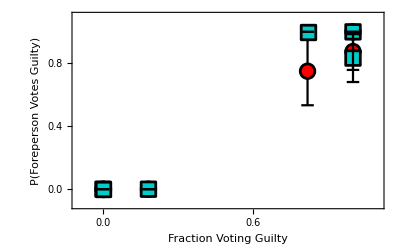

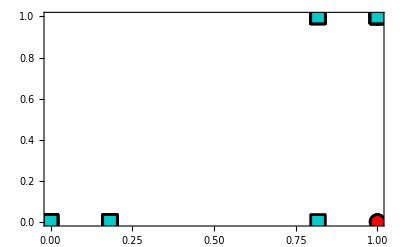

```mathematica
s=OpenRead["~/Google Drive/DelibWork/DelibData/OR-ICPSR_09030/DS0001/09030-0001-Data-card_image.txt"];

(*ForemanDataOR=DeleteCases[Flatten[Table[

Find[s,"                                                  1"];
Skip[s,Character,9];
Table[
data=Table[
Skip[s,Character,1];
CaseNum=Read[s,Table[Character,{8}]];

Skip[s,Character,3];
Start=StringReplace[StringJoin[Read[s,Table[Character,{4}]]],{" "->"0","98"->"Null","99"->"Null"}];
Start=ToExpression@Start;
end=StringReplace[StringJoin[Read[s,Table[Character,{5}]]],{" "->"0","98"->"Null","99"->"Null"}];

end=ToExpression@end;
jurySize=ToExpression@Read[s,Character];
(*jury size: 6,12,11*)
JurySize=If[jurySize==1,6,If[jurySize==2,12,If[jurySize==3,11,Null]]];

verdict=ToExpression@Read[s,Character];
Verdict=If[verdict==1,-1,If[verdict==2,1,If[verdict==3,0,Null]]];
(*verdict: guilty: -1, hung: 0, not guilty: 1*)
NumCounts=ToExpression@Read[s,Character];
(*If "9", then this should be ignored*)
If[NumCounts==9,NumCounts=Null;];
decision=ToExpression@StringJoin[Read[s,Table[Character,{2}]]];
(*convert "decision" into number in the majority*)
Decision=Which[decision==1,12,decision==2,11,decision==3,10,decision==4,9,decision==5,6,decision==6,5,decision==7||decision==8,-1,decision==9,10,decision==10,11,decision==11,9,decision==99,Null];

numVotes=ToExpression@Read[s,Character];
NumVotes=If[numVotes==9,Null,numVotes];
Skip[s,Character,4];
jurorVerdict=ToExpression@Read[s,Character];
JurorVerdict=If[jurorVerdict==1,-1(*Guilty*),If[jurorVerdict==2,1(*Innocent*),Null]];

foreman=ToExpression@Read[s,Character];

Foreman=If[foreman==1,1,If[foreman==2,0,Null]];
Skip[s,Character,2];
If[Foreman===1,
{JurySize,Verdict,Decision,JurorVerdict}
]
,{2}];
Skip[s,Character,11];
data
,{4}]

,{6892}],2],Null];
ForemanInfluence=DeleteCases[Table[
If[!MemberQ[ForemanDataOR[[i]],Null],
(*Number of Jurors*)
NumJurors=ForemanDataOR[[i,1]];
(*Number of people voting guilty*)
Decision = If[ForemanDataOR[[i,2]]==-1,ForemanDataOR[[i,3]],NumJurors-ForemanDataOR[[i,3]]];
(*Individual Vote*)
ForemanVote=ForemanDataOR[[i,4]]/.{-1->1,1->0};
GroupVote=Decision;
OtherVotes = Decision - If[ForemanVote ==1,1,0];
{ForemanVote,OtherVotes,NumJurors}
]
,{i,Length[ForemanDataOR]}],Null];
*)

ForemanInfluenceAll=DeleteCases[Table[If[!MemberQ[JuryDataOR[[i,{7,11(*,3*)}]],Null],JuryDataOR[[i,{7,11,3}]]],{i,Length[JuryDataOR]}],Null];
ForemanInfluenceAll[[;;,1]]=ForemanInfluenceAll[[;;,1]]/.{-1->1,1->0};
ForemanInfluence6All=DeleteCases[Table[If[ForemanInfluenceAll[[i,3]]==6&&!MemberQ[{1,4},ForemanInfluenceAll[[i,2]]],ForemanInfluenceAll[[i,2;;1;;-1]]],{i,Length[ForemanInfluenceAll]}],Null];
ForemanInfluenceAll6[[;;,1]]/=5;
lmFAll6ORAll=LogitModelFit[ForemanInfluence6All,x,x];
lmFAll6ORAll["ParameterConfidenceIntervalTable"]
lmFAll6ORAll["ParameterPValues"]

ForemanInfluenceAll12=DeleteCases[Table[If[ForemanInfluenceAll[[i,3]]==12&&MemberQ[{0,2,9,11},ForemanInfluenceAll[[i,2]]],ForemanInfluenceAll[[i,2;;1;;-1]]],{i,Length[ForemanInfluenceAll]}],Null]/.{-1->0};
ForemanInfluence12All[[;;,1]]/=11;
lmF12ORAll=LogitModelFit[ForemanInfluenceAll12,x,x];
lmF12ORAll["ParameterConfidenceIntervalTable"]
lmF12ORAll["ParameterPValues"]

ForemanInfluenceCriminal=DeleteCases[Table[If[JuryDataOR[[i,10]]==1(*criminal*)&&!MemberQ[JuryDataOR[[i,{7,11(*,3*)}]],Null],JuryDataOR[[i,{7,11,3}]]],{i,Length[JuryDataOR]}],Null];
(*"-1" voted guilty, else innocent*)
ForemanInfluenceCriminal[[;;,1]]=ForemanInfluenceCriminal[[;;,1]]/.{-1->1,1->0};
ForemanInfluenceCivil=DeleteCases[Table[If[JuryDataOR[[i,10]]==2(*civil*)&&!MemberQ[JuryDataOR[[i,{7,11(*,3*)}]],Null],JuryDataOR[[i,{7,11,3}]]],{i,Length[JuryDataOR]}],Null];
(*"-1" voted guilty, else innocent*)
ForemanInfluenceCivil[[;;,1]]=ForemanInfluenceCivil[[;;,1]]/.{-1->1,1->0};

ForemanInfluence6Civil=DeleteCases[Table[If[ForemanInfluenceCivil[[i,3]]==6&&!MemberQ[{1,4},ForemanInfluenceCivil[[i,2]]],ForemanInfluenceCivil[[i,2;;1;;-1]]],{i,Length[ForemanInfluenceCivil]}],Null];
ForemanInfluence6Criminal=DeleteCases[Table[If[ForemanInfluenceCriminal[[i,3]]==6&&!MemberQ[{1,4},ForemanInfluenceCriminal[[i,2]]],ForemanInfluenceCriminal[[i,2;;1;;-1]]],{i,Length[ForemanInfluenceCriminal]}],Null];
(*ARTIFICIALLY ADD A DATA POINT TO DETERMINE ERROR*)
(*AppendTo[ForemanInfluence6,{0,1}]*)

ForemanInfluence6Civil[[;;,1]]/=5;
lmF6ORCivil=LogitModelFit[ForemanInfluence6Civil,x,x];
lmF6ORCivil["ParameterConfidenceIntervalTable"]
lmF6ORCivil["ParameterPValues"]

ForemanInfluence6Criminal[[;;,1]]/=5;
lmF6ORCriminal=LogitModelFit[ForemanInfluence6Criminal,x,x];
lmF6ORCriminal["ParameterConfidenceIntervalTable"]
lmF6ORCriminal["ParameterPValues"]

ForemanInfluence12Civil=DeleteCases[Table[If[ForemanInfluenceCivil[[i,3]]==12&&MemberQ[{0,2,9,11},ForemanInfluenceCivil[[i,2]]],ForemanInfluenceCivil[[i,2;;1;;-1]]],{i,Length[ForemanInfluenceCivil]}],Null]/.{-1->0};
ForemanInfluence12Civil[[;;,1]]/=11;
lmF12ORCivil=LogitModelFit[ForemanInfluence12Civil,x,x];
lmF12ORCivil["ParameterConfidenceIntervalTable"]
lmF12ORCivil["ParameterPValues"]

ForemanInfluence12Criminal=DeleteCases[Table[If[ForemanInfluenceCriminal[[i,3]]==12&&MemberQ[{0,2,9,11},ForemanInfluenceCriminal[[i,2]]],ForemanInfluenceCriminal[[i,2;;1;;-1]]],{i,Length[ForemanInfluenceCriminal]}],Null]/.{-1->0};
ForemanInfluence12Criminal[[;;,1]]/=11;
lmF12ORCriminal=LogitModelFit[ForemanInfluence12Criminal,x,x];
lmF12ORCriminal["ParameterConfidenceIntervalTable"]
lmF12ORCriminal["ParameterPValues"]


Needs["ErrorBarPlots`"];
Needs["PlotLegends`"];
vals=DeleteDuplicates[ForemanInfluence6Civil[[;;,1]]];
ForemanErrorOR6Civil=Table[
posv=Flatten[Position[ForemanInfluence6Civil[[;;,1]],v]];
p=N[Mean[ForemanInfluence6Civil[[posv,2]]]];
n=Length[posv];
{{v,p},ErrorBar[N[Sqrt[p (1-p)/n]]]}
,{v,vals}];

vals=DeleteDuplicates[ForemanInfluence6Criminal[[;;,1]]];
ForemanErrorOR6Criminal=Table[
posv=Flatten[Position[ForemanInfluence6Criminal[[;;,1]],v]];
p=N[Mean[ForemanInfluence6Criminal[[posv,2]]]];
n=Length[posv];
{{v,p},ErrorBar[N[Sqrt[p (1-p)/n]]]}
,{v,vals}];

vals=DeleteDuplicates[ForemanInfluence12Civil[[;;,1]]];
ForemanErrorOR12Civil=Table[
posv=Flatten[Position[ForemanInfluence12Civil[[;;,1]],v]];
p=N[Mean[ForemanInfluence12Civil[[posv,2]]]];
n=Length[posv];
{{v,p},ErrorBar[N[Sqrt[p (1-p)/n]]]}
,{v,vals}];
vals=DeleteDuplicates[ForemanInfluence12Criminal[[;;,1]]];
ForemanErrorOR12Criminal=Table[
posv=Flatten[Position[ForemanInfluence12Criminal[[;;,1]],v]];
p=N[Mean[ForemanInfluence12Criminal[[posv,2]]]];
n=Length[posv];
{{v,p},ErrorBar[N[Sqrt[p (1-p)/n]]]}
,{v,vals}];


Shape[shape_,in_,size_: 15]:=
Which[shape=="Square",Graphics[{in,EdgeForm[{AbsoluteThickness[2],Black}],Rectangle[]},PlotRangePadding->0,ImageSize->size],
shape=="Circle",
Graphics[{in,EdgeForm[{AbsoluteThickness[2],Black}],Disk[]},PlotRangePadding->0,ImageSize->size],
shape=="Triangle",
Graphics[{in,EdgeForm[{AbsoluteThickness[2],Black}],Polygon[{{1,0},{0,Sqrt[3]},{-1,0}}]} ,PlotRangePadding->0,ImageSize->size],
shape=="Diamond",
Graphics[{in,EdgeForm[{AbsoluteThickness[2],Black}],Polygon[{{1,0},{0,1},{-1,0},{0,-1}}]} ,PlotRangePadding->0,ImageSize->size]
];

hw=0.05;
Show[ErrorListPlot[{ForemanErrorOR6Civil,ForemanErrorOR6Criminal,ForemanErrorOR12Civil,ForemanErrorOR12Criminal},
PlotMarkers->{Shape["Circle",RGBColor[1,0,0]],Shape["Square",CMYKColor[1,0,0,0.2]]},
PlotStyle->Black,
ErrorBarFunction->Function[{coords,errs},
{(*the vertical line:*)Line[{coords+{0,errs[[2,1]]},coords+{0,errs[[2,2]]}}],
(*horizontal tick 1:*){Thick,Line[{coords+{hw/2,errs[[2,2]]},coords-{hw/2,-errs[[2,2]]}}]},
(*horizontal tick 2:*){Thick,Line[{coords+{hw/2,errs[[2,1]]},coords-{hw/2,-errs[[2,1]]}}]}}],
PlotRange->{{-0.1,1.1},{-0.1,1.1}},
Frame->True,
Axes->False,
FrameLabel->{
Style["Fraction Voting Guilty",FontFamily->"Arial",FontSize->20,FontColor->Black],Style["P(Foreperson Votes Guilty)",FontFamily->"Arial",FontSize->20,FontColor->Black]},
FrameTicksStyle->Directive[20,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LinTicks[0,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
}
,
ImageSize->400
]
,
Plot[{lmF6OR[x],lmF12OR[x]},{x,0,1},PlotStyle->{{RGBColor[1,0,0],Thickness[0.02]},{CMYKColor[1,0,0,0.4],Thickness[0.02]}}]
]

Show[ListPlot[{ForemanInfluence6Civil,ForemanInfluence12Civil,ForemanInfluence6Criminal,ForemanInfluence12Criminal},
Frame->True,
Axes->False,
PlotMarkers->{Shape["Circle",RGBColor[1,0,0]],Shape["Square",CMYKColor[1,0,0,0.2]]},
PlotLegend->{
Style["N = 6",FontFamily->"Arial",FontSize->20],
Style["N = 12",FontFamily->"Arial",FontSize->20]
}
],
Plot[{lmF6OR[x],lmF12OR[x]},{x,0,1},PlotStyle->{{Blue,Thickness[0.02]},{RGBColor[0,0.7,0],Thickness[0.02]}}]
]
```

```mathematica
SortBy[ForemanInfluenceAll12,First]
```

{{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{2,0},{2,0},{2,0},{2,0},{9,0},{9,1},{9,1},{9,1},{9,1},{9,1},{9,1},{11,1},{11,1},{11,1},{11,1},{11,1},{11,1},{11,1},{11,1},{11,1},{11,1}}

```mathematica
(*If 1 added ARTIFICIALLY to OR6, fits are the same*)
```

| Estimate | Standard Error | Confidence Interval
1 | -3.58352 | 1.01379 | {-5.5705,-1.59654}
x | 6.84162 | 1.17214 | {4.54426,9.13897}

{0.0004081,5.31961×10^-9}

| Estimate | Standard Error | Confidence Interval
1 | -3.31602 | 0.335372 | {-3.97334,-2.65871}
x | 6.33529 | 0.459835 | {5.43403,7.23655}

{4.7125×10^-23,3.4903×10^-43}

{{{1,0.962963},ErrorBar[0.190029]},{{0,0.027027},ErrorBar[0.164399]}}

{{{0,0.0416667},ErrorBar[0.200664]},{{9/11,0.875},ErrorBar[0.331942]},{{1,0.949153},ErrorBar[0.220309]},{{2/11,0.0875},ErrorBar[0.284349]}}

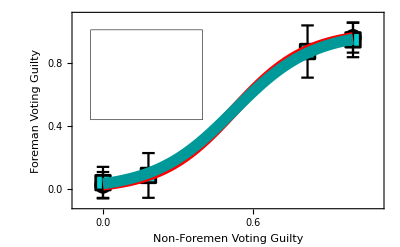

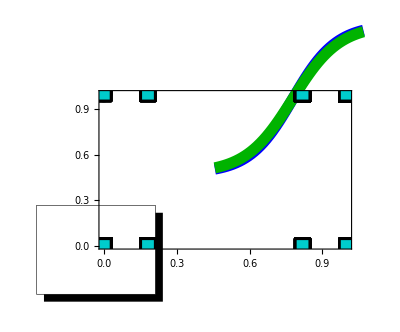

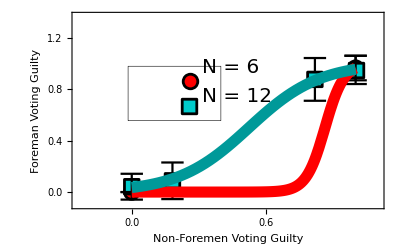

{28,7,0,0,0,21,45}

{6,1,0,6,0,6,0,5,0,0,6,5,5,5,6,0,6,0,0,1,0,6,5,1,6,0,6,6,6,6,6,6,0,5,0,0,0,5,5,5,0,5,0,0,5,6,6,6,6,6,6,5,5,6,6,6,6,1,0,5,0,6,6,6,6,6,0,0,0,0,6,6,6,6,6,6,6,0,5,5,6,5,6,6,0,0,6,5,6,6,6,0,6,5,6,6,6,6,0,5,6,0,5,5,6,5,6,0,5,0,6,0,6,6,6,5,5,6,0,1,5,6,5,1,6,6,0,6,6,6,5,5,5,0,1,6,0,5,6,6,6,5,5,5,6,6,0,0,0,6,6,6,0,6,6,0,6,0,5,5,0,6,6,5,5,6,1,5,6,0,6,5,1,6,5,1,6,0,6,5,6,6,0,5,6,0,5,6,6,6,6,6,1,0,6,5,6,6,5,0,0,1,5,6,6,5,5}

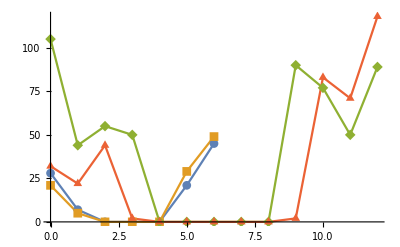

| Estimate | Standard Error | Confidence Interval
1 | -1.38629 | 0.422577 | {-2.21453,-0.558059}
x | 2.14843 | 0.49841 | {1.17157,3.1253}

{0.00103596,0.0000162829}

| Estimate | Standard Error | Confidence Interval
1 | -1.43508 | 0.497613 | {-2.41039,-0.459781}
x | 1.95961 | 0.550009 | {0.881612,3.03761}

{0.00392736,0.000366822}

lmF6OR[ParameterConfidenceIntervalTable]

lmF6OR[ParameterPValues]

| Estimate | Standard Error | Confidence Interval
1 | -0.678871 | 0.141962 | {-0.957112,-0.40063}
x | 1.00379 | 0.20741 | {0.597269,1.4103}

{1.73514×10^-6,1.30091×10^-6}

| Estimate | Standard Error | Confidence Interval
1 | -0.939162 | 0.234222 | {-1.39823,-0.480096}
x | 1.92849 | 0.290984 | {1.35817,2.49881}

{0.0000607919,3.41488×10^-11}

lmF12OR[ParameterConfidenceIntervalTable]

lmF12OR[ParameterPValues]

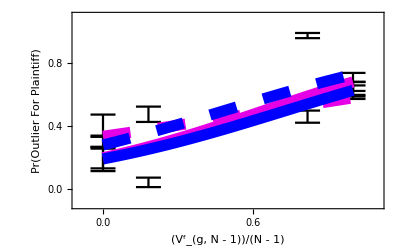
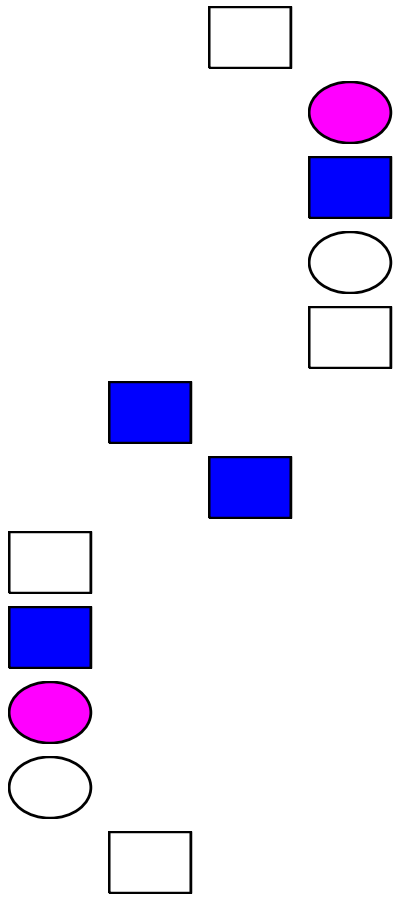

```mathematica
(*
OR, CA distributions
*)

(*
OR:
*)

Dist=DeleteCases[Table[
(*If "Null" not in data*)
If[(!MemberQ[JuryDataOR[[i,{4,5}]],-Null])&&
(!MemberQ[JuryDataOR[[i,{4,5}]],-NullNull])&&
(!MemberQ[JuryDataOR[[i,{4,5}]],Null])&&!MemberQ[JuryDataOR[[i,{4,5}]],NullNull],

(*Number of Jurors*)
NumJurors=12;
If[JuryDataOR[[i,5]]<9,NumJurors=6;];
(*Number of people voting guilty*)
NumGuilty = If[JuryDataOR[[i,4]]==-1,JuryDataOR[[i,5]],NumJurors-JuryDataOR[[i,5]]];
If[JuryDataOR[[i,5]]≥0,
{NumGuilty,NumJurors}
]
]
,{i,Length[JuryDataOR]}],Null];



Dist6=DeleteCases[Table[If[Dist[[i,2]]==6&&Dist[[i,1]]≥ 0,Dist[[i,1]]],{i,Length[Dist]}],Null]
Hist6=HistogramList[Dist6,{1}];
Hist6=Table[Hist6[[;;,i]],{i,Length[Hist6[[2]]]}];
Hist6[[;;,1]]/=6;
Hist6Civil=Table[{i-1,Length[JuryTimeVsOutcomeOR6Civil[[i]]]},{i,Length[JuryTimeVsOutcomeOR6Civil]}];
Hist6Criminal=Table[{i-1,Length[JuryTimeVsOutcomeOR6Criminal[[i]]]},{i,Length[JuryTimeVsOutcomeOR6Criminal]}];
(*
Dist12=DeleteCases[Table[If[Dist[[i,2]]==12,Dist[[i,1]]],{i,Length[Dist]}],Null];
Hist12=HistogramList[Dist12,{1}];
Hist12=Table[Hist12[[;;,i]],{i,Length[Hist12[[2]]]}];
Hist12[[;;,1]]/=12;*)

Hist12Civil=Table[{i-1(*/(Length[JuryTimeVsOutcomeOR12Civil]-1)*),Length[JuryTimeVsOutcomeOR12Civil[[i]]]},{i,Length[JuryTimeVsOutcomeOR12Civil]}];
Hist12Criminal=Table[{i-1(*/(Length[JuryTimeVsOutcomeOR12Criminal]-1)*),Length[JuryTimeVsOutcomeOR12Criminal[[i]]]},{i,Length[JuryTimeVsOutcomeOR12Criminal]}];

ListPlot[{Hist6Civil,Hist6Criminal,Hist12Civil,Hist12Criminal},Joined->True,PlotMarkers->Automatic]

(*
Hist12[[;;,1]]*=12;
Hist6[[;;,1]]*=6;
*)

GroupInfluence6ORCivil=Flatten[{Table[Table[{Hist6Civil[[1,1]],i-1},{j,Hist6Civil[[i,2]]}],{i,2}],
Table[Table[{Hist6Civil[[6,1]],(i-6)},{j,Hist6Civil[[i,2]]}],{i,{6,7}}]},2];
GroupInfluence6ORCriminal=Flatten[{Table[Table[{Hist6Criminal[[1,1]],i-1},{j,Hist6Criminal[[i,2]]}],{i,2}],
Table[Table[{Hist6Criminal[[6,1]],(i-6)},{j,Hist6Criminal[[i,2]]}],{i,{6,7}}]},2];

GroupInfluence12ORCivil=Flatten[{Table[Table[{Hist12Civil[[1,1]],i-1},{j,Hist12Civil[[i,2]]}],{i,2}],Table[Table[{Hist12Civil[[3,1]],i-3},{j,Hist12Civil[[i,2]]}],{i,{3,4}}],
Table[Table[{Hist12Civil[[10,1]],(i-10)},{j,Hist12Civil[[i,2]]}],{i,{10,11}}],Table[Table[{Hist12Civil[[12,1]],(i-12)},{j,Hist12Civil[[i,2]]}],{i,{12,13}}]},2];
GroupInfluence12ORCriminal=Flatten[{Table[Table[{Hist12Criminal[[1,1]],i-1},{j,Hist12Criminal[[i,2]]}],{i,2}],Table[Table[{Hist12Criminal[[3,1]],i-3},{j,Hist12Criminal[[i,2]]}],{i,{3,4}}],
Table[Table[{Hist12Criminal[[10,1]],(i-10)},{j,Hist12Criminal[[i,2]]}],{i,{10,11}}],Table[Table[{Hist12Criminal[[12,1]],(i-12)},{j,Hist12Criminal[[i,2]]}],{i,{12,13}}]},2];

GroupInfluence12ORCivil[[;;,1]]/=11;
GroupInfluence12ORCriminal[[;;,1]]/=11;

GroupInfluence6ORCivil[[;;,1]]/=5;
GroupInfluence6ORCriminal[[;;,1]]/=5;

lmG6ORCivil=LogitModelFit[GroupInfluence6ORCivil,x,x];
lmG6ORCivil["ParameterConfidenceIntervalTable"]
lmG6ORCivil["ParameterPValues"]
lmG6ORCriminal=LogitModelFit[GroupInfluence6ORCriminal,x,x];
lmG6ORCriminal["ParameterConfidenceIntervalTable"]
lmG6ORCriminal["ParameterPValues"]

lmF6OR["ParameterConfidenceIntervalTable"]
lmF6OR["ParameterPValues"]

lmG12ORCivil=LogitModelFit[GroupInfluence12ORCivil,x,x];
lmG12ORCivil["ParameterConfidenceIntervalTable"]
lmG12ORCivil["ParameterPValues"]
lmG12ORCriminal=LogitModelFit[GroupInfluence12ORCriminal,x,x];
lmG12ORCriminal["ParameterConfidenceIntervalTable"]
lmG12ORCriminal["ParameterPValues"]

lmF12OR["ParameterConfidenceIntervalTable"]
lmF12OR["ParameterPValues"]

Needs["ErrorBarPlots`"];
Needs["PlotLegends`"];
vals=DeleteDuplicates[ForemanInfluence6Civil[[;;,1]]];
GroupErrorOR6Civil=Table[
posv=Flatten[Position[GroupInfluence6ORCivil[[;;,1]],v]];
p=N[Mean[GroupInfluence6ORCivil[[posv,2]]]];
n=Length[posv];
{{v,p},ErrorBar[(*N[StandardDeviation[GroupInfluence6OR[[posv,2]]]]*)Sqrt[p (1-p)/n]]}
,{v,vals}];
GroupErrorOR6Criminal=Table[
posv=Flatten[Position[GroupInfluence6ORCriminal[[;;,1]],v]];
p=N[Mean[GroupInfluence6ORCriminal[[posv,2]]]];
n=Length[posv];
{{v,p},ErrorBar[(*N[StandardDeviation[GroupInfluence6OR[[posv,2]]]]*)Sqrt[p (1-p)/n]]}
,{v,vals}];

vals=DeleteDuplicates[ForemanInfluence12Civil[[;;,1]]];
GroupErrorOR12Civil=Table[
posv=Flatten[Position[GroupInfluence12ORCivil[[;;,1]],v]];
p=N[Mean[GroupInfluence12ORCivil[[posv,2]]]];
n=Length[posv];
{{v,p},ErrorBar[(*N[StandardDeviation[GroupInfluence12OR[[posv,2]]]]*)Sqrt[p (1-p)/n]]}
,{v,vals}];
GroupErrorOR12Criminal=Table[
posv=Flatten[Position[GroupInfluence12ORCriminal[[;;,1]],v]];
p=N[Mean[GroupInfluence12ORCriminal[[posv,2]]]];
n=Length[posv];
{{v,p},ErrorBar[(*N[StandardDeviation[GroupInfluence12OR[[posv,2]]]]*)Sqrt[p (1-p)/n]]}
,{v,vals}];


Shape[shape_,in_,out_:Black,size_: 15]:=
Which[shape=="Square",Graphics[{in,EdgeForm[{AbsoluteThickness[2],out}],Rectangle[]},PlotRangePadding->0,ImageSize->size],
shape=="Circle",
Graphics[{in,EdgeForm[{AbsoluteThickness[2],out}],Disk[]},PlotRangePadding->0,ImageSize->size],
shape=="Triangle",
Graphics[{in,EdgeForm[{AbsoluteThickness[2],out}],Polygon[{{1,0},{0,Sqrt[3]},{-1,0}}]} ,PlotRangePadding->0,ImageSize->size],
shape=="Diamond",
Graphics[{in,EdgeForm[{AbsoluteThickness[2],out}],Polygon[{{1,0},{0,1},{-1,0},{0,-1}}]} ,PlotRangePadding->0,ImageSize->size]
];

hw=0.1;
Show[ErrorListPlot[{GroupErrorOR6Civil,GroupErrorOR6Criminal,GroupErrorOR12Civil,GroupErrorOR12Criminal},
PlotMarkers->{Shape["Circle",CMYKColor[0,1,0,0],CMYKColor[0,1,0,0]],
Shape["Circle",White,CMYKColor[0,1,0,0]],
Shape["Square",Blue,Blue],
Shape["Square",White,Blue]},
PlotStyle->Black,
ErrorBarFunction->Function[{coords,errs},
{(*the vertical line:*)Line[{coords+{0,errs[[2,1]]},coords+{0,errs[[2,2]]}}],
(*horizontal tick 1:*){Thick,Line[{coords+{hw/2,errs[[2,2]]},coords-{hw/2,-errs[[2,2]]}}]},
(*horizontal tick 2:*){Thick,Line[{coords+{hw/2,errs[[2,1]]},coords-{hw/2,-errs[[2,1]]}}]}}],
PlotRange->{{-0.1,1.1},{-0.1,1.1}},
Frame->True,
Axes->False,
FrameLabel->{
Style["((V^f)_(g, N - 1))/(N - 1)",FontFamily->"Arial",FontSize->20,FontColor->Black],Style["Pr(Outlier For Plaintiff)",FontFamily->"Arial",FontSize->20,FontColor->Black]},
FrameTicksStyle->Directive[20,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LinTicks[0,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
}
,
ImageSize->400
]
,
Plot[{lmG6ORCivil[x],lmG12ORCivil[x],lmG6ORCriminal[x],lmG12ORCriminal[x]},{x,0,1},PlotStyle->{{CMYKColor[0,1,0,0.1],Thickness[0.02]},{CMYKColor[0,1,0,0.1],Thickness[0.02],Dashing[0.05]},{RGBColor[0,0,1],Thickness[0.02]},{RGBColor[0,0,1],Thickness[0.02],Dashing[0.05]}}]
]

Needs["PlotLegends`"]
(*Show[*)ListPlot[{(*GroupErrorOR6*)GroupErrorOR12Civil[[;;,1]],GroupErrorOR12Criminal[[;;,1]],
(*ForemanErrorOR6*)GroupErrorOR12Civil[[;;,1]],GroupErrorOR12Criminal[[;;,1]]},
PlotMarkers->{Style["●",FontSize->20,FontColor->Red],Style["○",FontSize->20,FontColor->Red],Style["■",FontSize->25,FontColor->Blue],Style["□",FontSize->25,FontColor->Blue]},
PlotLegend->{
Style["Juror (Civil)",FontFamily->"Arial",FontSize->15],
Style["Juror (Criminal)",FontFamily->"Arial",FontSize->15],
Style["Foreperson (Civil)",FontFamily->"Arial",FontSize->15],
Style["Foreperson (Criminal)",FontFamily->"Arial",FontSize->15]
}
](*,
Plot[{lmG6ORCivil[x],lmG12ORCivil[x]},{x,0,1},PlotStyle->{{Blue,Thickness[0.02]},{RGBColor[0,0.7,0],Thickness[0.02]}}]
]*)

Show[ErrorListPlot[{(*GroupErrorOR6*)GroupErrorOR12Civil,GroupErrorOR12Criminal,
(*ForemanErrorOR6*)ForemanErrorOR12Civil,ForemanErrorOR12Criminal},
PlotMarkers->{Style["●",FontSize->20,FontColor->Red],Style["○",FontSize->20,FontColor->Red],Style["■",FontSize->25,FontColor->Blue],Style["□",FontSize->25,FontColor->Blue](*Shape["Circle",CMYKColor[0,1,0,0],CMYKColor[0,1,0,0]],
Shape["Circle",White,CMYKColor[0,1,0,0]],
Shape["Square",Blue,Blue],
Shape["Square",White,Blue]*)},
PlotStyle->Black,
ErrorBarFunction->Function[{coords,errs},
{(*the vertical line:*)Line[{coords+{0,errs[[2,1]]},coords+{0,errs[[2,2]]}}],
(*horizontal tick 1:*){Thick,Line[{coords+{hw/2,errs[[2,2]]},coords-{hw/2,-errs[[2,2]]}}]},
(*horizontal tick 2:*){Thick,Line[{coords+{hw/2,errs[[2,1]]},coords-{hw/2,-errs[[2,1]]}}]}}],
PlotRange->{{-0.1,1.1},{-0.1,1.1}},
Frame->True,
Axes->False,
FrameLabel->{
Style["((V^f)_(g, N - 1))/(N - 1)",FontFamily->"Arial",FontSize->16,FontColor->Black],Style["Pr(Outlier For Plaintiff)",FontFamily->"Arial",FontSize->16,FontColor->Black]},
FrameTicksStyle->Directive[16,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LinTicks[0,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
}
(*,
ImageSize->400*)
]
,
Plot[{lmG12ORCivil[x],lmG12ORCriminal[x],(*lmG12OR[x],*)lmF12ORCivil[x],lmF12ORCriminal[x](*,lmF12OR[x]*)},{x,0,1},PlotStyle->{(*{CMYKColor[0,1,0,0.1],Thickness[0.02]},*){RGBColor[1,0,0],Thickness[0.02]},{RGBColor[1,0,0],Thickness[0.02],Dashing[0.05]},{Blue,Thickness[0.02]},{Blue,Thickness[0.02],Dashing[0.05]}}]
]


Show[ErrorListPlot[{(*GroupErrorOR6*)GroupErrorOR12Civil,GroupErrorOR12Criminal},
PlotMarkers->{Style["●",FontSize->20,FontColor->Red],Style["○",FontSize->20,FontColor->Red](*Shape["Circle",CMYKColor[0,1,0,0],CMYKColor[0,1,0,0]],
Shape["Circle",White,CMYKColor[0,1,0,0]],
Shape["Square",Blue,Blue],
Shape["Square",White,Blue]*)},
PlotStyle->Black,
ErrorBarFunction->Function[{coords,errs},
{(*the vertical line:*)Line[{coords+{0,errs[[2,1]]},coords+{0,errs[[2,2]]}}],
(*horizontal tick 1:*){Thick,Line[{coords+{hw/2,errs[[2,2]]},coords-{hw/2,-errs[[2,2]]}}]},
(*horizontal tick 2:*){Thick,Line[{coords+{hw/2,errs[[2,1]]},coords-{hw/2,-errs[[2,1]]}}]}}],
PlotRange->{{-0.1,1.1},{-0.1,1.1}},
Frame->True,
Axes->False,
FrameLabel->{
Style["((V^f)_(g, N - 1))/(N - 1)",FontFamily->"Arial",FontSize->16,FontColor->Black],Style["Pr(Outlier For Plaintiff)",FontFamily->"Arial",FontSize->16,FontColor->Black]},
FrameTicksStyle->Directive[16,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LinTicks[0,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
}
(*,
ImageSize->400*)
]
,
Plot[{lmG12ORCivil[x],lmG12ORCriminal[x]},{x,0,1},PlotStyle->{(*{CMYKColor[0,1,0,0.1],Thickness[0.02]},*){RGBColor[1,0,0],Thickness[0.02]},{RGBColor[1,0,0],Thickness[0.02],Dashing[0.05]}}]
]

(*
Show[ErrorListPlot[{GroupErrorOR6Civil,GroupErrorOR6Criminal,ForemanErrorOR6},
PlotMarkers->{Shape["Circle",CMYKColor[0,1,0,0]],Shape["Circle",CMYKColor[1,0,0,0.2]],Shape["Circle",CMYKColor[1,0,0,0.2]],Shape["Square",Red]},
PlotStyle->Black,
ErrorBarFunction->Function[{coords,errs},
{(*the vertical line:*)Line[{coords+{0,errs[[2,1]]},coords+{0,errs[[2,2]]}}],
(*horizontal tick 1:*){Thick,Line[{coords+{hw/2,errs[[2,2]]},coords-{hw/2,-errs[[2,2]]}}]},
(*horizontal tick 2:*){Thick,Line[{coords+{hw/2,errs[[2,1]]},coords-{hw/2,-errs[[2,1]]}}]}}],
PlotRange->{{-0.1,1.1},{-0.1,1.2}},
Frame->True,
Axes->False,
FrameLabel->{
Style["Fraction Voting Guilty",FontFamily->"Arial",FontSize->20,FontColor->Black],Style["Pr(Guilty)",FontFamily->"Arial",FontSize->20,FontColor->Black]},
FrameTicksStyle->Directive[20,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LinTicks[0,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
}
,
ImageSize->400
]
,
Plot[{lmG6ORCivil[x],lmG6ORCriminal[x],(*lmG12OR[x],*)lmF6OR[x](*,lmF12OR[x]*)},{x,0,1},PlotStyle->{{CMYKColor[0,1,0,0.1],Thickness[0.02]},{CMYKColor[1,0,0,0.4],Thickness[0.02]}}]
]*)
```

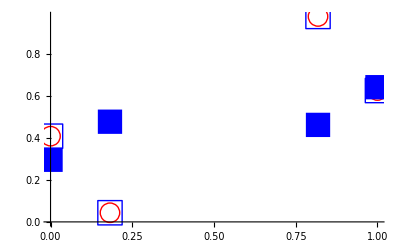

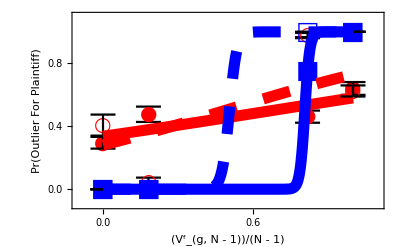

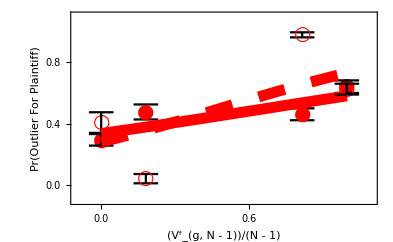

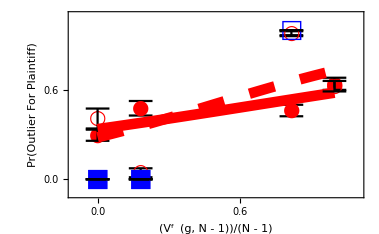

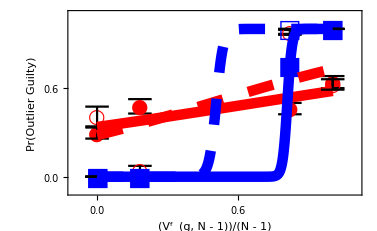
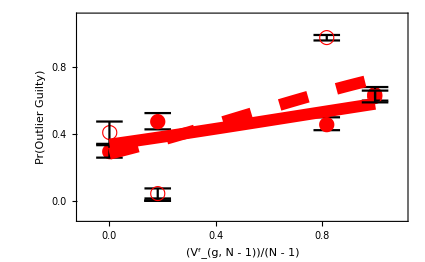

```mathematica
lmG6ORCivil["ParameterConfidenceIntervalTable"]
lmF6ORCivil["ParameterConfidenceIntervalTable"]

lmG12ORCivil["ParameterConfidenceIntervalTable"]
lmF12ORCivil["ParameterConfidenceIntervalTable"]

lmG6ORCriminal["ParameterConfidenceIntervalTable"]
lmF6ORCriminal["ParameterConfidenceIntervalTable"]

lmG12ORCriminal["ParameterConfidenceIntervalTable"]
lmF12ORCriminal["ParameterConfidenceIntervalTable"]

BootstrapPhi[list_]:=StandardDeviation[Table[
boot=RandomChoice[list,Length[list]];
N[SpearmanRho[boot[[;;,1]],boot[[;;,2]]]],{10000}]];

PearsonCorrelationTest[ForemanInfluence12Civil[[;;,1]],ForemanInfluence12Civil[[;;,2]],"TestDataTable"]
r=N[SpearmanRho[ForemanInfluence12Civil[[;;,1]],ForemanInfluence12Civil[[;;,2]]]]
σ=BootstrapPhi[ForemanInfluence12Civil]

PearsonCorrelationTest[GroupInfluence12ORCivil[[;;,1]],GroupInfluence12ORCivil[[;;,2]],"TestDataTable"]
r=N[SpearmanRho[GroupInfluence12ORCivil[[;;,1]],GroupInfluence12ORCivil[[;;,2]]]]
σ=BootstrapPhi[GroupInfluence12ORCivil]


PearsonCorrelationTest[ForemanInfluence12Criminal[[;;,1]],ForemanInfluence12Criminal[[;;,2]],"TestDataTable"]
r=N[SpearmanRho[ForemanInfluence12Criminal[[;;,1]],ForemanInfluence12Criminal[[;;,2]]]]
σ=BootstrapPhi[ForemanInfluence12Criminal]
PearsonCorrelationTest[GroupInfluence12ORCriminal[[;;,1]],GroupInfluence12ORCriminal[[;;,2]],"TestDataTable"]
r=N[SpearmanRho[GroupInfluence12ORCriminal[[;;,1]],GroupInfluence12ORCriminal[[;;,2]]]]
σ=BootstrapPhi[GroupInfluence12ORCriminal]
```

| Estimate | Standard Error | Confidence Interval
1 | -1.38629 | 0.422577 | {-2.21453,-0.558059}
x | 2.14843 | 0.49841 | {1.17157,3.1253}

| Estimate | Standard Error | Confidence Interval
1 | -18.5661 | 4612.2 | {-9058.32,9021.18}
x | 20.512 | 4612.2 | {-9019.24,9060.26}

| Estimate | Standard Error | Confidence Interval
1 | -0.678871 | 0.141962 | {-0.957112,-0.40063}
x | 1.00379 | 0.20741 | {0.597269,1.4103}

| Estimate | Standard Error | Confidence Interval
1 | -82.0289 | 28014.1 | {-54988.7,54824.6}
x | 101.6 | 34239.5 | {-67006.5,67209.7}

| Estimate | Standard Error | Confidence Interval
1 | -1.43508 | 0.497613 | {-2.41039,-0.459781}
x | 1.95961 | 0.550009 | {0.881612,3.03761}

| Estimate | Standard Error | Confidence Interval
1 | -18.5661 | 6522.64 | {-12802.7,12765.6}
x | 20.1755 | 6522.64 | {-12764.,12804.3}

| Estimate | Standard Error | Confidence Interval
1 | -0.939162 | 0.234222 | {-1.39823,-0.480096}
x | 1.92849 | 0.290984 | {1.35817,2.49881}

| Estimate | Standard Error | Confidence Interval
1 | -33.9036 | 23592.5 | {-46274.3,46206.5}
x | 67.0639 | 34622.6 | {-67792.,67926.1}

```mathematica
(*{{"", "Estimate", "Standard Error", "Confidence Interval"}, {1, -0.678871034248733, 0.14196226076221663, {-0.957111952506561,-0.40063011599090487}}, {x, 1.003785602992913, 0.20741022528234493, {0.5972690314141783,1.410302174571648}}}           (OR 12: Civil and Criminal)
{{"", "Estimate", "Standard Error", "Confidence Interval"}, {1, -0.9391620060497038, 0.2342215978464636, {-1.3982279022301964,-0.4800961098692112}}, {x, 1.9284905278284767, 0.2909843959368726, {1.3581715917290635,2.49880946392789}}}
*)
```

PearsonCorrelationTest::nortst: At least one of the p-values in {0.0145022,8.53308×10^-6}, resulting from a test for normality, is below 0.025. The tests in {PearsonCorrelation} require that the data is normally distributed.

| Statistic | P-Value
Pearson Correlation | 0.870002 | 0.000110517

0.844578

SpearmanRho::zrvr: The input data has zero variance. The statistic cannot be computed.

Indeterminate

PearsonCorrelationTest::nortst: At least one of the p-values in {0.,0.}, resulting from a test for normality, is below 0.025. The tests in {PearsonCorrelation} require that the data is normally distributed.

| Statistic | P-Value
Pearson Correlation | 0.206381 | 8.38908×10^-7

0.233807

0.0400713

PearsonCorrelationTest::nortst: At least one of the p-values in {0.000503741,8.60575×10^-8}, resulting from a test for normality, is below 0.025. The tests in {PearsonCorrelation} require that the data is normally distributed.

| Statistic | P-Value
Pearson Correlation | 0.975727 | 2.8024×10^-9

0.846234

SpearmanRho::zrvr: The input data has zero variance. The statistic cannot be computed.

General::stop: Further output of SpearmanRho::zrvr will be suppressed during this calculation.

Indeterminate

PearsonCorrelationTest::nortst: At least one of the p-values in {0.,0.}, resulting from a test for normality, is below 0.025. The tests in {PearsonCorrelation} require that the data is normally distributed.

| Statistic | P-Value
Pearson Correlation | 0.35972 | 7.23368×10^-13

0.19054

0.05423

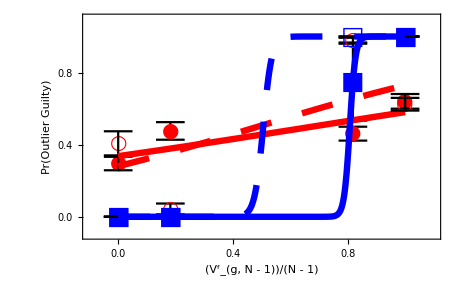
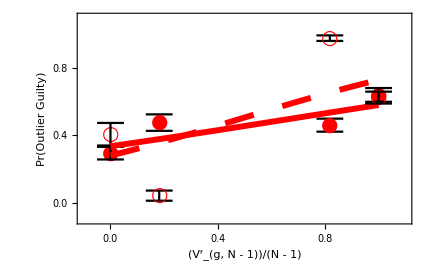

560

374

13

14

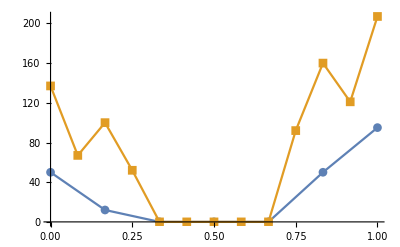

{{0,137},{1,67},{2,100},{3,52},{4,0},{5,0},{6,0},{7,0},{8,0},{9,92},{10,160},{11,121},{12,207}}

{{Null},{Null}}

| Estimate | Standard Error | Confidence Interval
1 | -1.42712 | 0.321455 | {-2.05716,-0.797077}
x | 2.06897 | 0.365868 | {1.35188,2.78606}

{9.01442×10^-6,1.5588×10^-8}

| Estimate | Standard Error | Confidence Interval
1 | -20.5661 | 2955.06 | {-5812.38,5771.25}
x | 23.8242 | 2955.06 | {-5767.99,5815.64}

{0.994447,0.993567}

| Estimate | Standard Error | Confidence Interval
1 | -0.765381 | 0.121008 | {-1.00255,-0.528209}
x | 1.40164 | 0.164616 | {1.079,1.72428}

{2.53189×10^-10,1.6712×10^-17}

| Estimate | Standard Error | Confidence Interval
1 | -3.31602 | 0.335372 | {-3.97334,-2.65871}
x | 6.33529 | 0.459835 | {5.43403,7.23655}

{4.7125×10^-23,3.4903×10^-43}

{{{1,0.655172},ErrorBar[0.0394725]},{{0,0.193548},ErrorBar[0.0501751]}}

{{{0,0.328431},ErrorBar[0.0328816]},{{2/11,0.342105},ErrorBar[0.0384801]},{{9/11,0.634921},ErrorBar[0.0303287]},{{1,0.631098},ErrorBar[0.026642]}}

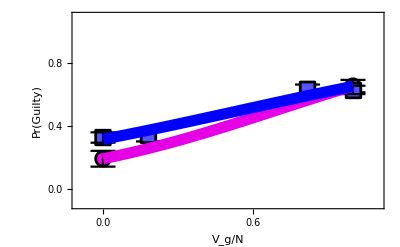

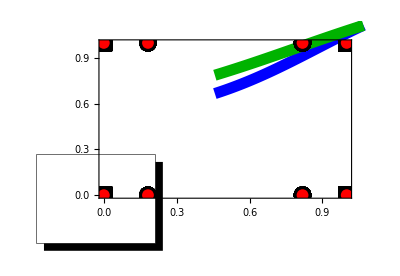

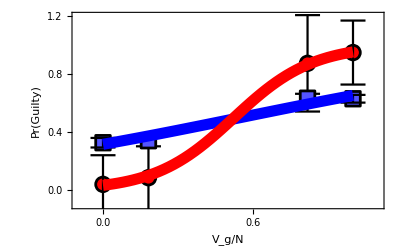

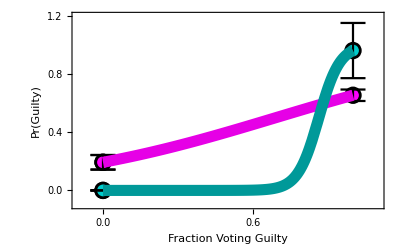

```mathematica
Length[GroupInfluence12ORCivil]
Length[GroupInfluence12ORCriminal]
Length[ForemanInfluence12Civil]
Length[ForemanInfluence12Criminal]
```

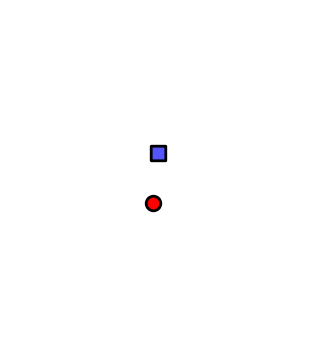

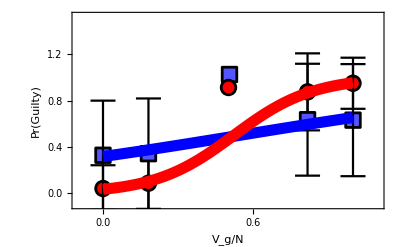
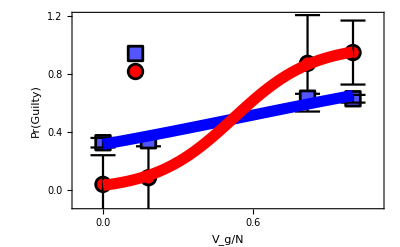

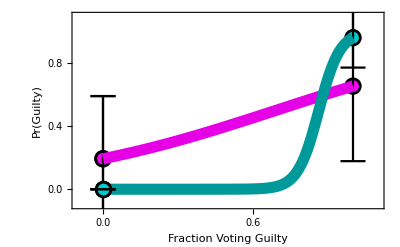

```mathematica
N[StandardDeviation[GroupInfluence12OR[[posv,2]]]]
p=GroupInfluence12OR[[posv,2]];
N[Sqrt[Mean[p] (1-Mean[p])/Length[p]]]
```

0.483245

0.026642

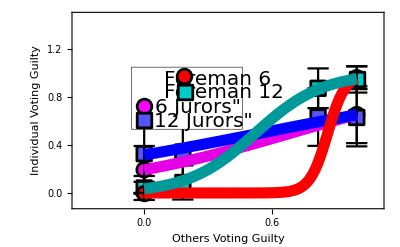

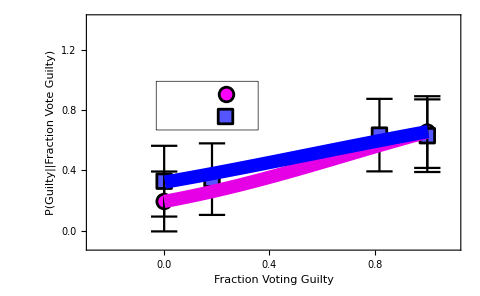

```mathematica
(2.068970241808555-(1.4016+2.068970241808555)/2)/Sqrt[(0.366^2+0.1646^2)/4]
p = 0.048
```

1.66298

{28,1,2,0,0,2,20}

{21,32,57,1,4,3,96,87,37}

{25,164,198,248,19,14,21,19,12,389,319,237,62}

| Estimate | Standard Error | Confidence Interval
1 | -3.3322 | 1.0177 | {-5.32686,-1.33755}
x | 5.63479 | 1.25925 | {3.1667,8.10288}

{0.00105942,7.6513×10^-6}

| Estimate | Standard Error | Confidence Interval
1 | -0.0589957 | 0.21707 | {-0.484445,0.366454}
x | 0.0743231 | 0.296287 | {-0.506389,0.655035}

{0.78579,0.801931}

| Estimate | Standard Error | Confidence Interval
1 | 0.927774 | 0.0971943 | {0.737277,1.11827}
x | -1.73338 | 0.14123 | {-2.01019,-1.45657}

{1.35376×10^-21,1.25754×10^-34}

{{{0,0.0344828},ErrorBar[0.185695]},{{1,0.909091},ErrorBar[0.294245]}}

{{{0,0.603774},ErrorBar[0.493793]},{{2/7,0.0172414},ErrorBar[0.131306]},{{5/7,0.969697},ErrorBar[0.172292]},{{1,0.298387},ErrorBar[0.459406]}}

{{{0,0.867725},ErrorBar[0.339689]},{{2/11,0.556054},ErrorBar[0.497406]},{{4/11,0.424242},ErrorBar[0.50189]},{{7/11,0.387097},ErrorBar[0.495138]},{{9/11,0.450565},ErrorBar[0.497902]},{{1,0.207358},ErrorBar[0.406094]}}

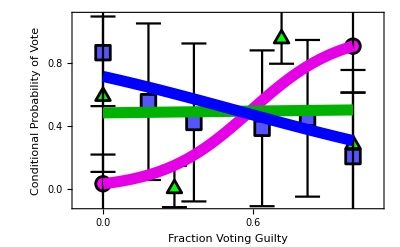

```mathematica
Dist6CA=Table[Length[TrialTimeDelibTimeVsOutcome6SF[[i]]],{i,Length[TrialTimeDelibTimeVsOutcome6SF]}]
GroupInfluence6CA=Flatten[{Table[Table[{0,i-1},{j,Dist6CA[[i]]}],{i,2}],
Table[Table[{5,i-6},{j,Dist6CA[[i]]}],{i,{6,7}}]},2];
Dist8CA=Table[Length[TrialTimeDelibTimeVsOutcome8SF[[i]]],{i,Length[TrialTimeDelibTimeVsOutcome8SF]}]
GroupInfluence8CA=Flatten[{Table[Table[{0,i-1},{j,Dist8CA[[i]]}],{i,2}],
Table[Table[{2,i-3},{j,Dist8CA[[i]]}],{i,{3,4}}],
Table[Table[{5,i-6},{j,Dist8CA[[i]]}],{i,{6,7}}],
Table[Table[{7,i-8},{j,Dist8CA[[i]]}],{i,{8,9}}]
},2];


Dist12CA=Table[Length[TrialTimeDelibTimeVsOutcome12SF[[i]]],{i,Length[TrialTimeDelibTimeVsOutcome12SF]}]
GroupInfluence12CA=Flatten[{Table[Table[{0,i-1},{j,Dist12CA[[i]]}],{i,2}],
Table[Table[{2,i-3},{j,Dist12CA[[i]]}],{i,{3,4}}],
Table[Table[{4,i-5},{j,Dist12CA[[i]]}],{i,{5,6}}],
Table[Table[{7,i-8},{j,Dist12CA[[i]]}],{i,{8,9}}],
Table[Table[{9,i-10},{j,Dist12CA[[i]]}],{i,{10,11}}],
Table[Table[{11,i-12},{j,Dist12CA[[i]]}],{i,{12,13}}]
},2];

GroupInfluence6CA[[;;,1]]/=5;
GroupInfluence8CA[[;;,1]]/=7;
GroupInfluence12CA[[;;,1]]/=11;

lmG6CA=LogitModelFit[GroupInfluence6CA,x,x];
lmG6CA["ParameterConfidenceIntervalTable"]
lmG6CA["ParameterPValues"]

lmG8CA=LogitModelFit[GroupInfluence8CA,x,x];
lmG8CA["ParameterConfidenceIntervalTable"]
lmG8CA["ParameterPValues"]

lmG12CA=LogitModelFit[GroupInfluence12CA,x,x];
lmG12CA["ParameterConfidenceIntervalTable"]
lmG12CA["ParameterPValues"]


Needs["ErrorBarPlots`"];
Needs["CustomTicks`"]
Needs["PlotLegends`"];
vals=DeleteDuplicates[GroupInfluence6CA[[;;,1]]];
GroupErrorCA6=Table[
posv=Flatten[Position[GroupInfluence6CA[[;;,1]],v]];
{{v,N[Mean[GroupInfluence6CA[[posv,2]]]]},ErrorBar[N[StandardDeviation[GroupInfluence6CA[[posv,2]]]]]}
,{v,vals}]

vals=DeleteDuplicates[GroupInfluence8CA[[;;,1]]];
GroupErrorCA8=Table[
posv=Flatten[Position[GroupInfluence8CA[[;;,1]],v]];
{{v,N[Mean[GroupInfluence8CA[[posv,2]]]]},ErrorBar[N[StandardDeviation[GroupInfluence8CA[[posv,2]]]]]}
,{v,vals}]

vals=DeleteDuplicates[GroupInfluence12CA[[;;,1]]];
GroupErrorCA12=Table[
posv=Flatten[Position[GroupInfluence12CA[[;;,1]],v]];
{{v,N[Mean[GroupInfluence12CA[[posv,2]]]]},ErrorBar[N[StandardDeviation[GroupInfluence12CA[[posv,2]]]]]}
,{v,vals}]



Shape[shape_,in_,size_: 15]:=
Which[shape=="Square",Graphics[{in,EdgeForm[{AbsoluteThickness[2],Black}],Rectangle[]},PlotRangePadding->0,ImageSize->size],
shape=="Circle",
Graphics[{in,EdgeForm[{AbsoluteThickness[2],Black}],Disk[]},PlotRangePadding->0,ImageSize->size],
shape=="Triangle",
Graphics[{in,EdgeForm[{AbsoluteThickness[2],Black}],Polygon[{{1,0},{0,Sqrt[3]},{-1,0}}]} ,PlotRangePadding->0,ImageSize->size],
shape=="Diamond",
Graphics[{in,EdgeForm[{AbsoluteThickness[2],Black}],Polygon[{{1,0},{0,1},{-1,0},{0,-1}}]} ,PlotRangePadding->0,ImageSize->size]
];

hw=0.1;
Show[ErrorListPlot[{GroupErrorCA6,GroupErrorCA8,GroupErrorCA12},
PlotMarkers->{Shape["Circle",CMYKColor[0,1,0,0]],Shape["Triangle",RGBColor[0,1,0]],Shape["Square",Lighter[Blue]]},
PlotStyle->Black,
ErrorBarFunction->Function[{coords,errs},
{(*the vertical line:*)Line[{coords+{0,errs[[2,1]]},coords+{0,errs[[2,2]]}}],
(*horizontal tick 1:*){Thick,Line[{coords+{hw/2,errs[[2,2]]},coords-{hw/2,-errs[[2,2]]}}]},
(*horizontal tick 2:*){Thick,Line[{coords+{hw/2,errs[[2,1]]},coords-{hw/2,-errs[[2,1]]}}]}}],
PlotRange->{{-0.1,1.1},{-0.1,1.1}},
Frame->True,
Axes->False,
FrameLabel->{
Style["Fraction Voting Guilty",FontFamily->"Arial",FontSize->20,FontColor->Black],Style["Conditional Probability of Vote",FontFamily->"Arial",FontSize->20,FontColor->Black]},
FrameTicksStyle->Directive[20,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LinTicks[0,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,2,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
}
,
ImageSize->400
]
,
Plot[{lmG6CA[x],lmG8CA[x],lmG12CA[x]},{x,0,1},PlotStyle->{{CMYKColor[0,1,0,0.1],Thickness[0.02]},{RGBColor[0,0.7,0],Thickness[0.02]},{RGBColor[0,0,1],Thickness[0.02]}}]
]


Show[ListPlot[{GroupInfluence6CA,GroupInfluence8CA,GroupInfluence12CA},
Frame->True,
Axes->False,
PlotMarkers->{Shape["Circle",CMYKColor[0,1,0,0]],Shape["Triangle",RGBColor[0,1,0]],Shape["Square",Lighter[Blue]]},
PlotLegend->{
Style["N = 6",FontFamily->"Arial",FontSize->20],
Style["N = 8",FontFamily->"Arial",FontSize->20],
Style["N = 12",FontFamily->"Arial",FontSize->20]
}

],
Plot[{lmG6OR[x],lmG12OR[x]},{x,0,1},PlotStyle->{{Blue,Thickness[0.02]},{RGBColor[0,0.7,0],Thickness[0.02]}}]
]


Show[ListPlot[{GroupInfluence6CA,GroupInfluence8CA,GroupInfluence12CA},
Frame->True,
Axes->False,
PlotMarkers->{Style["●",FontSize->20],Style["△",FontSize->20,FontWeight->Bold],Style["□",FontSize->20,FontWeight->Bold]},PlotStyle->Reverse[{{Blue,Opacity[0.25]},{RGBColor[0,0.7,0],Opacity[0.25]},{Red,Opacity[0.25]}}]],
Plot[{lmG6CA[x],lmG8CA[x],lmG12CA[x]},{x,0,1},PlotStyle->Reverse[{{Blue,Thickness[0.02]},{RGBColor[0,0.7,0],Thickness[0.02]},{Red,Thickness[0.02]}}]]
]

Show[ListPlot[{GroupInfluence6OR,GroupInfluence12OR,GroupInfluence6CA,GroupInfluence8CA,GroupInfluence12CA},
Frame->True,
Axes->False,
PlotMarkers->{Style["●",FontSize->20],Style["■",FontSize->20,FontWeight->Bold],Style["○",FontSize->20],Style["△",FontSize->20,FontWeight->Bold],Style["□",FontSize->20,FontWeight->Bold]},PlotStyle->Reverse[{{Blue,Opacity[0.25]},{RGBColor[0,0.7,0],Opacity[0.25]},{Red,Opacity[0.25]},{CMYKColor[0.8,0,0,0.2],Opacity[0.25]},{Magenta,Opacity[0.25]}}]],
Plot[{lmG6OR[x],lmG12OR[x],lmG6CA[x],lmG8CA[x],lmG12CA[x]},{x,0,1},PlotStyle->Reverse[{{Blue,Thickness[0.02]},{RGBColor[0,0.7,0],Thickness[0.02]},{Red,Thickness[0.02]},{CMYKColor[0.8,0,0,0.2],Thickness[0.02]},{Magenta,Thickness[0.02]}}]]
]
```

{{{{6,5.63479},ErrorBar[1.25925]}},{{{8,0.0743231},ErrorBar[0.296287]}},{{{12,-1.73338},ErrorBar[0.14123]}},{{{6,2.06897},ErrorBar[0.365868]}},{{{12,1.40164},ErrorBar[0.164616]}}}

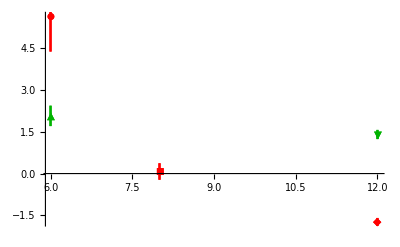

```mathematica
Needs["ErrorBarPlots`"]
FitErrorJury={{{{6,lmG6CA["ParameterConfidenceIntervalTableEntries"][[2,1]]},ErrorBar[lmG6CA["ParameterConfidenceIntervalTableEntries"][[2,2]]]}},
{{{8,lmG8CA["ParameterConfidenceIntervalTableEntries"][[2,1]]},ErrorBar[lmG8CA["ParameterConfidenceIntervalTableEntries"][[2,2]]]}},
{{{12,lmG12CA["ParameterConfidenceIntervalTableEntries"][[2,1]]},ErrorBar[lmG12CA["ParameterConfidenceIntervalTableEntries"][[2,2]]]}},
{{{6,lmG6OR["ParameterConfidenceIntervalTableEntries"][[2,1]]},ErrorBar[lmG6OR["ParameterConfidenceIntervalTableEntries"][[2,2]]]}},
{{{12,lmG12OR["ParameterConfidenceIntervalTableEntries"][[2,1]]},ErrorBar[lmG12OR["ParameterConfidenceIntervalTableEntries"][[2,2]]]}}
}

ErrorListPlot[FitErrorJury,
PlotMarkers->Automatic,
PlotStyle->{Red,Red,Red,RGBColor[0,0.7,0],RGBColor[0,0.7,0]},
PlotRange->All
]
```

```mathematica
plot=ListPlot[
AcceptErrorBars=Table[
If[param≠13||j≠2,Table[SortedData=Sort[{AcceptedDataError[[BoardType,AllBoards,j,param,1]][[;;19]],
AcceptedDataError[[BoardType,AllBoards,j,param,2]][[;;19]]}[[;;,i,2]]];
{{AcceptedDataError[[BoardType,AllBoards,j,param,1]][[i,1]],SortedData[[1]]},{AcceptedDataError[[BoardType,AllBoards,j,param,1]][[i,1]],SortedData[[2]]}},{i,19}]],{j,3}];
{
AcceptedData[[BoardType,AllBoards,1,param]][[;;19]],
If[param≠13,AcceptedData[[BoardType,AllBoards,2,param]][[;;19]],{{Null,Null}}],
AcceptedData[[BoardType,AllBoards,3,param]][[;;19]],
AcceptErrorBars[[1,;;,1]],
If[param≠13,AcceptErrorBars[[2,;;,1]],{{Null,Null}}],
AcceptErrorBars[[3,;;,1]],
AcceptErrorBars[[1,;;,2]],
If[param≠13,AcceptErrorBars[[2,;;,2]],{{Null,Null}}],
AcceptErrorBars[[3,;;,2]]
},
PlotRange->{{0,21},All},
Joined->{False,False,False,True,True,True,True,True,True},
PlotMarkers->{Shape["Triangle",Red],Shape["Circle",RGBColor[0,0.7,0]],Shape["Square",CMYKColor[1,0,0,0.2]],"","","","","",""},
PlotStyle->{{Red,AbsoluteThickness[2]},{RGBColor[0,0.7,0],AbsoluteThickness[2]},{CMYKColor[1,0,0,0.2],AbsoluteThickness[2]}},
Filling->{4->{7},5->{8},6->{9}},
Frame->True,
Axes->False,
PlotLabel->Style[Board[[BoardType]]<>" Boards",FontFamily->"Arial",FontSize->25,FontColor->Black],
FrameLabel->{Style["Number Of Answers",FontFamily->"Arial",FontSize->20,FontColor->Black],
Style[If[BoardType==3,"β For "<>Params[[param]],""],FontFamily->"Arial",FontSize->20,FontColor->Black]},
FrameTicksStyle->Directive[20,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
LinTicks[0,41,5,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[-10,20,Which[param==1,1,param==2||param==7,2,param==6,0.25,True,0.5],2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,41,5,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],
LinTicks[-10,20,Which[param==1,1,param==2||param==7,2,param==6,0.25,True,0.5],2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
}(*,
PlotLegend->(*PointLegend[*){Style["Vote Before",FontFamily->"Arial",FontSize->20],
Style["Accept",FontFamily->"Arial",FontSize->20],
Style["Vote After",FontFamily->"Arial",FontSize->20]
}(*,LegendMarkerSize->20,LegendFunction->frame]*)*)
,ImageSize->430
];
```

```mathematica
(*Test if Exp Tail*)

(*Check KL test*)
```

```mathematica
(*Test if EVL Tail*)

(*First, check inf limit KL test*)

(*Next subtract EVL limit to check if it agrees with finite size correction*)
(*KL test*)
```

```mathematica
(**)
```

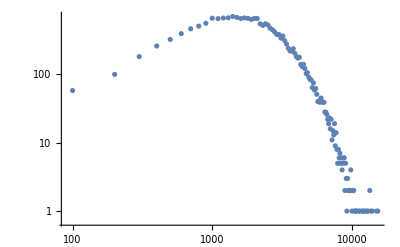

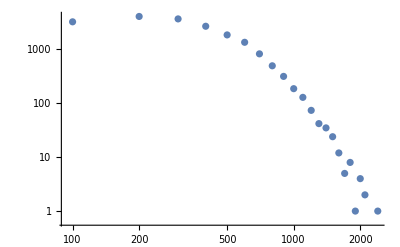

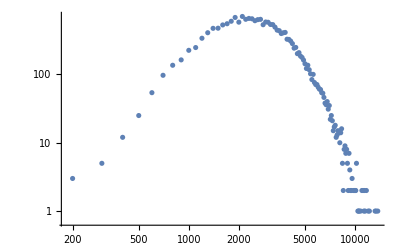

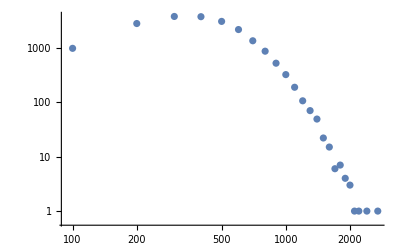

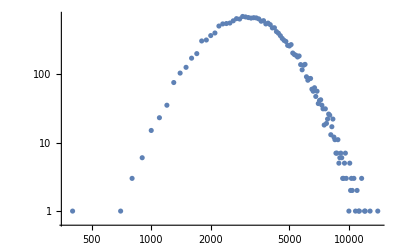

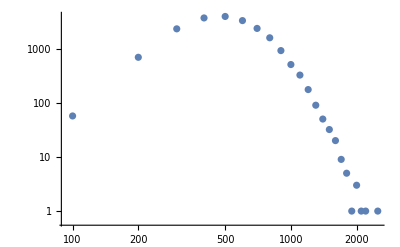

```mathematica
(*

Majority Rule: pick X neighbors, accept with random prob, p
Let X = 3, p = 10^-4... 10^0,
check dist: hypothesis is exp distribution (dominated by p timescale)
*)

(*MRData=Flatten[DeleteCases[Import["~/Downloads/2StrainComplete_MajorityRuleInward;Beta=0.001_0.0005_0.01;Tau=0;InitInf=1.0;N=6_2_24;Trial1.dat"],{}][[28;;]]];*)

MRDataReshaped=ArrayReshape[MRData,{3,2,Length[MRData]/6}];
Do[
MRHist=HistogramList[MRDataReshaped[[i,j]],{100}];
MRHist=Table[MRHist[[;;,k]],{k,Length[MRHist[[2]]]}];
Print[ListLogLogPlot[MRHist]];
,{i,3}
,{j,2}
]
```

```mathematica
HistogramList[MRDataReshaped[[1,1]],{100}]
```

{{0,100,200,300,400,500,600,700,800,900,1000,1100,1200,1300,1400,1500,1600,1700,1800,1900,2000,2100,2200,2300,2400,2500,2600,2700,2800,2900,3000,3100,3200,3300,3400,3500,3600,3700,3800,3900,4000,4100,4200,4300,4400,4500,4600,4700,4800,4900,5000,5100,5200,5300,5400,5500,5600,5700,5800,5900,6000,6100,6200,6300,6400,6500,6600,6700,6800,6900,7000,7100,7200,7300,7400,7500,7600,7700,7800,7900,8000,8100,8200,8300,8400,8500,8600,8700,8800,8900,9000,9100,9200,9300,9400,9500,9600,9700,9800,9900,10000,10100,10200,10300,10400,10500,10600,10700,10800,10900,11000,11100,11200,11300,11400,11500,11600,11700,11800,11900,12000,12100,12200,12300,12400,12500,12600,12700,12800,12900,13000,13100,13200,13300,13400,13500,13600,13700,13800,13900,14000,14100,14200,14300,14400,14500,14600,14700,14800,14900,15000,15100,15200,15300,15400},{9,58,100,182,260,324,394,463,507,558,663,653,667,672,703,681,655,669,660,637,656,656,549,520,551,527,472,449,417,383,383,339,363,311,278,241,221,218,237,203,182,173,178,140,130,140,122,103,106,91,85,83,64,75,59,62,51,40,41,39,45,40,39,39,28,28,26,22,19,23,16,22,11,15,13,19,9,14,8,5,8,6,7,5,6,4,5,6,6,2,5,3,1,3,2,2,2,2,4,2,1,2,2,2,1,0,1,1,1,0,0,0,1,0,1,0,0,0,1,0,1,0,1,0,0,1,0,0,1,0,1,0,0,0,2,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,1}}

```mathematica
(*Explore model*)
directory="~/Google Drive/DelibWork/DelibData/";
data = DeleteCases[Import[directory<>"2StrainJuryDelib-3sec;DeltaP=0.33;T_trial=21M_21M_21M;Hung_P_Guilty=0.0_0.00003_0.0001;Hung_P_Innocent=0.0_0.00003_0.0001;N=12;NumRuns=500;NumTrials=32;CompleteGraph;AllInfected;Trial1.dat"],{}];
Length[Flatten[data[[28;;]]]]

ReshapedData=ArrayReshape[data[[28;;]],{4,4,500*32,2}];

Length[Flatten[ReshapedData]]
```

512000

512000

```mathematica
directory="~/Google Drive/DelibWork/DelibData/";
data = DeleteCases[Import[directory<>"2StrainJuryDelib-3sec;DeltaP=0.33;T_trial=21M_21M_21M;Hung_P_Guilty=0.0_0.0001_0.0003;Hung_P_Innocent=0.0_0.0001_0.0003;N=12;NumRuns=500;NumTrials=32;CompleteGraph;AllInfected;Trial1.dat"],{}];
Length[Flatten[data[[28;;]]]]

ReshapedData=ArrayReshape[data[[28;;]],{4,4,500*32,2}];
ModelHistCA = HistogramList[ReshapedData[[4,4,;;,2]]];
ModelHistCA=Table[{ModelHistCA[[1,i]]/12,ModelHistCA[[2,i]]},{i,Length[ModelHistCA[[2]]]}];
ModelHistCA[[;;,2]]/=Total[ModelHistCA[[;;,2]]];
ModelHistCA2= HistogramList[ReshapedData[[2,2,;;,2]]];
ModelHistCA2=Table[{ModelHistCA2[[1,i]]/12,ModelHistCA2[[2,i]]},{i,Length[ModelHistCA2[[2]]]}];
ModelHistCA2[[;;,2]]/=Total[ModelHistCA2[[;;,2]]];

PlotHist6CA=Table[{i/6,Dist6CA[[i+1]]/Total[Dist6CA]},{i,0,6}];
PlotHist12CA=Table[{i/12,Dist12CA[[i+1]]/Total[Dist12CA]},{i,0,12}];
ListPlot[{ModelHist2,ModelHistCA,PlotHist6CA,PlotHist12CA},Joined->True,PlotMarkers->{Shape["Circle",RGBColor[0,0.7,0]],Shape["Circle",RGBColor[0,0,1]],Shape["Square",RGBColor[0,0.7,0]],Shape["Square",RGBColor[0,0,1]]}]

ModelHist = HistogramList[ReshapedData[[4,4,;;,2]]];
ModelHist=Table[{ModelHist[[1,i]]/12,ModelHist[[2,i]]},{i,Length[ModelHist[[2]]]}];
ModelHist[[;;,2]]/=Total[ModelHist[[;;,2]]];


directory="~/Google Drive/DelibWork/DelibData/";
data = DeleteCases[Import[directory<>"2StrainJuryDelib-3sec;DeltaP=0.33;T_trial=21M_21M_21M;Hung_P_Guilty=0.0_0.00003_0.0001;Hung_P_Innocent=0.0_0.00003_0.0001;N=12;NumRuns=500;NumTrials=32;CompleteGraph;AllInfected;Trial1.dat"],{}];
Length[Flatten[data[[28;;]]]]

ReshapedData=ArrayReshape[data[[28;;]],{4,4,500*32,2}];
ModelHist = HistogramList[ReshapedData[[3,3,;;,2]]];
ModelHist=Table[{ModelHist[[1,i]]/12,ModelHist[[2,i]]},{i,Length[ModelHist[[2]]]}];
ModelHist[[;;,2]]/=Total[ModelHist[[;;,2]]];
ModelHist2= HistogramList[ReshapedData[[2,2,;;,2]]];
ModelHist2=Table[{ModelHist2[[1,i]]/12,ModelHist2[[2,i]]},{i,Length[ModelHist2[[2]]]}];
ModelHist2[[;;,2]]/=Total[ModelHist2[[;;,2]]];
PlotHist6OR = Hist6;
PlotHist6OR[[;;,1]]/=6;
PlotHist6OR[[;;,2]]/=Total[Hist6[[;;,2]]];
PlotHist12OR = Hist12;
PlotHist12OR[[;;,1]]/=12;
PlotHist12OR[[;;,2]]/=Total[Hist12[[;;,2]]];
PlotHist12OR
ListPlot[{ModelHist2,ModelHist,PlotHist6OR,PlotHist12OR},Joined->True,PlotMarkers->{Shape["Circle",RGBColor[0,0.7,0]],Shape["Circle",RGBColor[0,0,1]],Shape["Square",RGBColor[0,0.7,0]],Shape["Square",RGBColor[0,0,1]]}]
```

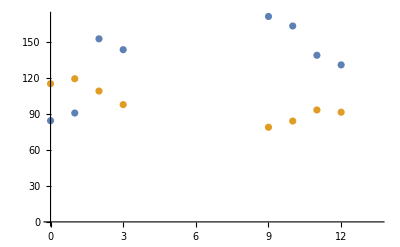

```mathematica
(*Time to reach consensus*)
(*directory="~/Google Drive/DelibWork/DelibData/";
data = DeleteCases[Import[directory<>"2StrainJuryDelib-3sec;DeltaP=0.33;T_trial=270M_21M_270M;Hung_P_Guilty=0.0_0.00001_0.0001;Hung_P_Innocent=0.0_0.00001_0.0001;N=12;NumRuns=500;NumTrials=32;CompleteGraph;AllInfected;Trial1.dat"],{}];
Length[Flatten[data[[28;;]]]]

ReshapedData=ArrayReshape[data[[28;;]],{11,11,800*20,2}];
*)
p1=2;
p2=2;
Pos=Table[Flatten[Position[ReshapedData[[p1,p2,;;,2]],i]],{i,0,12}];

ListPlot[{Table[{i-1,Mean[JuryTimeVsOutcomeOR12[[i]]]},{i,Length[JuryTimeVsOutcomeOR12]}],Table[{i-1,Mean[ReshapedData[[p1,p2,Pos[[i]],1]]]/20},{i,Length[Pos]}]},PlotRange->{{0,13.5},All}]
```

```mathematica
Length[Flatten[ReshapedData[[28;;]]]]
```

Part::take: Cannot take positions 28 through -1 in {« 1 »}.

2

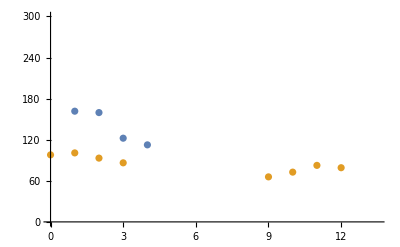

```mathematica
(*p1=p2=0.0006*)
```

```mathematica
Dimensions[JuryTimeVsOutcomeOR12]
```

{4}

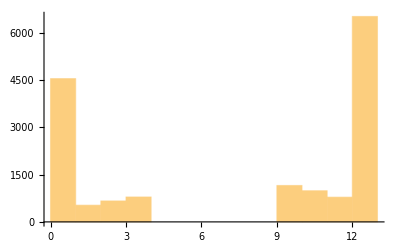

```mathematica
(*2StrainJuryDelib-3sec;DeltaP=0.33;T_trial=21M_21M_21M;Hung_P_Guilty=0.0_0.00003_0.0001;Hung_P_Innocent=0.0_0.00003_0.0001;N=12;NumRuns=500;NumTrials=32;CompleteGraph;AllInfected;Trial1.dat"*)
Histogram[ReshapedData[[2,2,;;,2]]]
```

```mathematica
(*
"2StrainJuryDelib-3sec;DeltaP=0.33;T_trial=21M_21M_21M;Hung_P_Guilty=0.0_0.0001_0.0003;Hung_P_Innocent=0.0_0.0001_0.0003;N=12;NumRuns=500;NumTrials=32;CompleteGraph;AllInfected;Trial1.dat"
*)
```

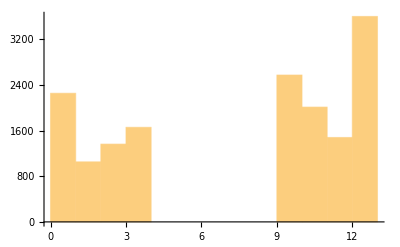

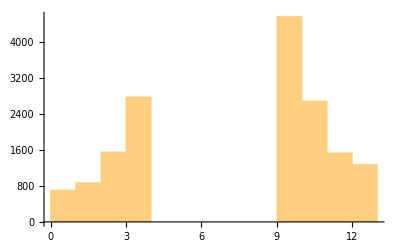

```mathematica
Histogram[ReshapedData[[2,2,;;,2]]]
Histogram[ReshapedData[[4,4,;;,2]]]
```

```mathematica
(*
pg = 0.001, pi = 0.001
δp(0) = 0.33
"2StrainJuryDelib-3sec;DeltaP=0.33;T_trial=21M_21M_21M;Hung_P_Guilty=0.0_0.001_0.005;Hung_P_Innocent=0.0_0.001_0.005;N=12;NumRuns=5000;NumTrials=32;CompleteGraph;AllInfected;Trial1.dat"
*)
```

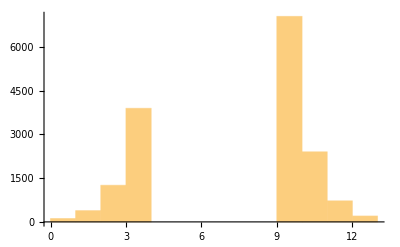

```mathematica
Histogram[ReshapedData[[2,2,;;,2]]]
```

```mathematica
ListPlot[ReshapedData[[1,2,;;,;;]]]
```

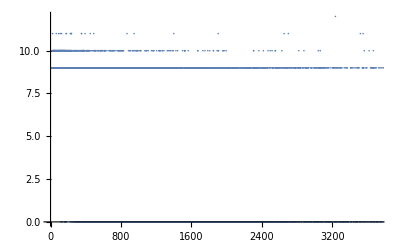

```mathematica
(*pg = 0.01, pi = 0

"2StrainJuryDelib-3sec;DeltaP=0.33;T_trial=21M_21M_21M;Hung_P_Guilty=0.0_0.01_0.1;Hung_P_Innocent=0.0_0.01_0.1;N=12;NumRuns=5000;NumTrials=32;CompleteGraph;AllInfected;Trial1.dat"
*)
```

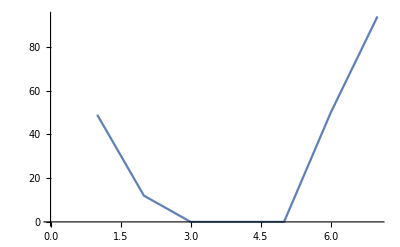

0.702439

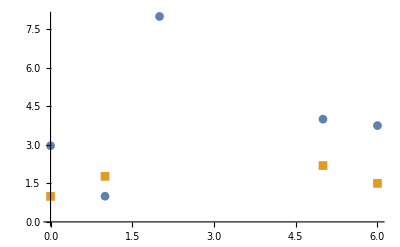

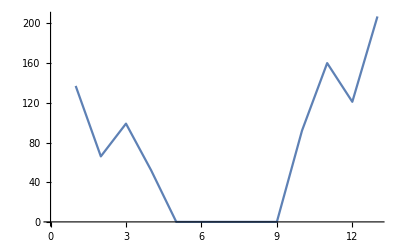

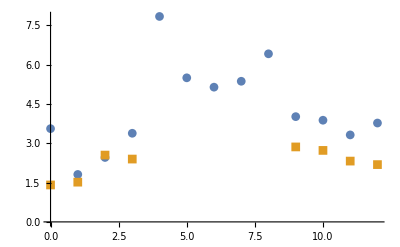

{{0,16.},{1,8.5},{2,8.5},{3,7.5},{4,20.},{5,12.5},{6,10.},{7,12.},{8,13.},{9,28.},{10,9.},{11,12.},{12,11.}}

```mathematica
ListPlot[Table[Length[JuryTimeVsOutcomeOR6[[i]]],{i,7}],Joined->True]
1-N[Total[Table[Length[JuryTimeVsOutcomeOR6[[i]]],{i,4}]]/Total[Table[Length[JuryTimeVsOutcomeOR6[[i]]],{i,7}]]]

ListPlot[{Table[If[Length[TrialTimeDelibTimeVsOutcome6SF[[i]]]>0,{i-1,Mean[TrialTimeDelibTimeVsOutcome6SF[[i,;;,2]]]}],{i,7}],Table[If[Length[JuryTimeVsOutcomeOR6[[i]]]>0,{i-1,Mean[JuryTimeVsOutcomeOR6[[i]]]/60}],{i,7}]},PlotMarkers->Automatic]
ListPlot[Table[Length[JuryTimeVsOutcomeOR12[[i]]],{i,13}],Joined->True]
ListPlot[{Table[If[Length[TrialTimeDelibTimeVsOutcome12SF[[i]]]>0,{i-1,Mean[TrialTimeDelibTimeVsOutcome12SF[[i,;;,2]]]}],{i,13}],Table[If[Length[JuryTimeVsOutcomeOR12[[i]]]>0,{i-1,Mean[JuryTimeVsOutcomeOR12[[i]]]/60}],{i,13}]},PlotMarkers->Automatic]
```

```mathematica
N[Mean[Flatten[JuryTimeVsOutcomeOR12[[1;;4]]]]/60]
N[Mean[Flatten[JuryTimeVsOutcomeOR12[[10;;13]]]]/60]
N[Mean[Flatten[TrialTimeDelibTimeVsOutcome12SF[[1;;4,;;,2]]]]]
N[Mean[Flatten[TrialTimeDelibTimeVsOutcome12SF[[10;;13,;;,2]]]]]

1-2 N[Length[Flatten[JuryTimeVsOutcomeOR12[[1;;4]]]]/Length[Flatten[JuryTimeVsOutcomeOR12]]]
1-2 N[Length[Flatten[TrialTimeDelibTimeVsOutcome12SF[[1;;4,;;,2]]]]/Length[Flatten[TrialTimeDelibTimeVsOutcome12SF]]]


N[Mean[Flatten[JuryTimeVsOutcomeOR6[[1;;2]]]]/60]
N[Mean[Flatten[JuryTimeVsOutcomeOR6[[6;;7]]]]/60]
N[Mean[Flatten[TrialTimeDelibTimeVsOutcome6SF[[1;;2,;;,2]]]]]
N[Mean[Flatten[TrialTimeDelibTimeVsOutcome6SF[[6;;7,;;,2]]]]]

1-2 N[Length[Flatten[JuryTimeVsOutcomeOR6[[1;;2]]]]/Length[Flatten[JuryTimeVsOutcomeOR6]]]
1-2 N[Length[Flatten[TrialTimeDelibTimeVsOutcome6SF[[1;;2,;;,2]]]]/Length[Flatten[TrialTimeDelibTimeVsOutcome6SF]]]
```

1.89393

2.47149

2.69606

3.79543

0.24197

0.63231

1.14645

1.74097

2.89655

3.77273

0.404878

0.45283

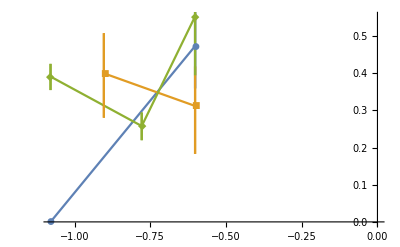

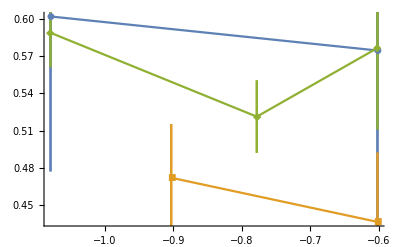

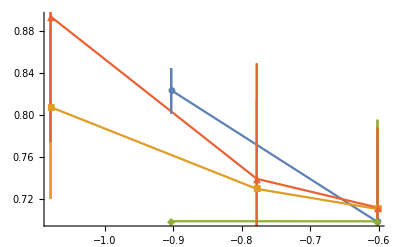

```mathematica
Needs["ErrorBarPlots`"];
BootstrapMean[data_]:=Module[
{ResampledList,ResampledMeanDist},
(*Non-resampled bootstrap*)
n=10^4;
ResampledList=ArrayReshape[RandomChoice[data,Length[data] n],{n,Length[data]}];
ResampledMeanDist=Table[Mean[ResampledList[[i]]],{i,Length[ResampledList]}];
Return[N[{Mean[ResampledMeanDist],Quantile[ResampledMeanDist,{0.05,0.95}]}]];
];

BootstrapLogError[data_]:=Module[
{ResampledList,ResampledMeanDist},
(*Non-resampled bootstrap*)
n=10^4;
ResampledList=ArrayReshape[RandomChoice[data,Length[data] n],{n,Length[data]}];
ResampledMeanDist=Table[Mean[ResampledList[[i]]],{i,Length[ResampledList]}];
Return[N[{Log10[Mean[ResampledMeanDist]],ErrorBar[Log10[Quantile[ResampledMeanDist,{0.05,0.95}]]-Log10[Mean[ResampledMeanDist]]]}]];
];

BootstrapMeanMWTest[data1_,data2_]:=Module[
{ResampledList1,ResampledMeanDist1,ResampledList2,ResampledMeanDist2},
(*Non-resampled bootstrap*)
n=10^4;
ResampledList1=ArrayReshape[RandomChoice[data1,Length[data1] n],{n,Length[data1]}];
ResampledMeanDist1=Table[Mean[ResampledList1[[i]]],{i,Length[ResampledList1]}];
ResampledList2=ArrayReshape[RandomChoice[data2,Length[data2] n],{n,Length[data2]}];
ResampledMeanDist2=Table[Mean[ResampledList2[[i]]],{i,Length[ResampledList2]}];

Return[N[{Mean[ResampledMeanDist1],
Median[ResampledMeanDist1],
Quantile[ResampledMeanDist1,{0.05,0.95}],
Mean[ResampledMeanDist2],
Median[ResampledMeanDist2],
Quantile[ResampledMeanDist2,{0.05,0.95}],
MannWhitneyTest[{ResampledMeanDist1,ResampledMeanDist2}]
}]];
]

Needs["ErrorBarPlots`"];
Needs["PlotLegends`"];
Needs["CustomTicks`"];

(*
TODO: Add OR data, add best fit lines, weighted by variance

*)


ErrorListPlot[{Table[frac=(i-1)/6;If[Length[TrialTimeDelibTimeVsOutcome6SF[[i]]]>0&&frac≤0.33,
mean=BootstrapLogError[TrialTimeDelibTimeVsOutcome6SF[[i,;;,2]]];
{{Log10[Abs[frac-0.25]],mean[[1]]},mean[[2]]}],{i,7}],
Table[frac=(i-1)/8;If[Length[TrialTimeDelibTimeVsOutcome8SF[[i]]]>0&&frac≤0.33,
mean=BootstrapLogError[TrialTimeDelibTimeVsOutcome8SF[[i,;;,2]]];
{{Log10[Abs[frac-0.25]],mean[[1]]},mean[[2]]}],{i,9}],
Table[frac=(i-1)/12;If[Length[TrialTimeDelibTimeVsOutcome12SF[[i]]]>0&&frac≤0.33,
mean=BootstrapLogError[TrialTimeDelibTimeVsOutcome12SF[[i,;;,2]]];
{{Log10[Abs[frac-0.25]],mean[[1]]},mean[[2]]}],{i,13}]},Joined->True,PlotMarkers->Automatic]



ErrorListPlot[{DeleteCases[Table[frac=(i-1)/6;If[Length[TrialTimeDelibTimeVsOutcome6SF[[i]]]>0&&frac≥0.67,mean=BootstrapLogError[TrialTimeDelibTimeVsOutcome6SF[[i,;;,2]]];
{{Log10[Abs[frac-0.75]],mean[[1]]},mean[[2]]}],{i,7}],Null],
DeleteCases[Table[frac=(i-1)/8;If[Length[TrialTimeDelibTimeVsOutcome8SF[[i]]]>0&&frac>0.67,mean=BootstrapLogError[TrialTimeDelibTimeVsOutcome8SF[[i,;;,2]]];
{{Log10[Abs[frac-0.75]],mean[[1]]},mean[[2]]}],{i,9}],Null],
DeleteCases[Table[frac=(i-1)/12;If[Length[TrialTimeDelibTimeVsOutcome12SF[[i]]]>0&&frac>0.67,mean=BootstrapLogError[TrialTimeDelibTimeVsOutcome12SF[[i,;;,2]]];
{{Log10[Abs[frac-0.75]],mean[[1]]},mean[[2]]}],{i,13}],Null]},Joined->True,PlotMarkers->Automatic]


ErrorListPlot[{
DeleteCases[Table[frac=(i-1)/8;If[Length[TrialTimeDelibTimeVsOutcome8SF[[i]]]>0&&frac>=0.5&&frac<0.75,

mean=BootstrapLogError[TrialTimeDelibTimeVsOutcome8SF[[i,;;,2]]];
{{Log10[Abs[frac-0.75]],mean[[1]]},mean[[2]]}],{i,9}],Null],
DeleteCases[Table[frac=(i-1)/12;If[Length[TrialTimeDelibTimeVsOutcome12SF[[i]]]>0&&frac>=0.5&&frac<0.75,

mean=BootstrapLogError[TrialTimeDelibTimeVsOutcome12SF[[i,;;,2]]];
{{Log10[Abs[frac-0.75]],mean[[1]]},mean[[2]]}],{i,13}],Null],
DeleteCases[Table[frac=(i-1)/8;If[Length[TrialTimeDelibTimeVsOutcome8SF[[i]]]>0&&frac<=0.5&&frac>0.25,

mean=BootstrapLogError[TrialTimeDelibTimeVsOutcome8SF[[i,;;,2]]];
{{Log10[Abs[frac-0.25]],mean[[1]]},mean[[2]]}],{i,9}],Null],
DeleteCases[Table[frac=(i-1)/12;If[Length[TrialTimeDelibTimeVsOutcome12SF[[i]]]>0&&frac<=0.5&&frac>0.25,

mean=BootstrapLogError[TrialTimeDelibTimeVsOutcome12SF[[i,;;,2]]];
{{Log10[Abs[frac-0.25]],mean[[1]]},mean[[2]]}],{i,13}],Null]},Joined->True,PlotMarkers->Automatic,PlotRange->All]
```

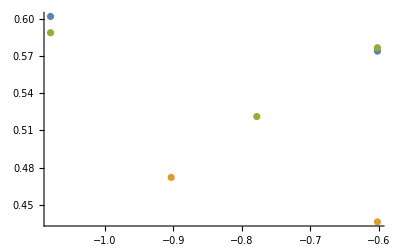

```mathematica
ListPlot[{{{-1.0791812460476247,0.6020599913279624},{-0.6020599913279624,0.5740312677277188}},{{-0.9030899869919435,0.4721004533446117},{-0.6020599913279624,0.4361196497156476}},{{-1.0791812460476247,0.588929961626918},{-0.7781512503836437,0.5212263863489607},{-0.6020599913279624,0.5768241679118891}}}]
```

```mathematica
(*

DO ABOVE WORK WITH NON-LINEAR FIT. IF Guilty/Innocent fits look similar, fit both together. ALso do line-lin plot, so see if it looks correctS
*)
```

{21,32,57,1,4,3,96,87,37}

```mathematica
(*
Combine CA 6, 8, 12
Separate: OR 6, 12

V_c = ??
i.e., between 8/12 = 0.666, and 9/12 = 0.750
*)
```

```mathematica
n=10000;
MeanTimeVsOutcomeOR6Civil=Table[
If[Length[JuryTimeVsOutcomeOR6Civil[[i]]]>0,{(i-1)/6,BootstrapMean[JuryTimeVsOutcomeOR6Civil[[i]]]/60},{(i-1)/6,{Null,{0,0}}}]
,{i,Length[JuryTimeVsOutcomeOR6Civil]}];

MeanTimeVsOutcomeOR6Criminal=Table[
If[Length[JuryTimeVsOutcomeOR6Criminal[[i]]]>0,{(i-1)/6,BootstrapMean[JuryTimeVsOutcomeOR6Criminal[[i]]]/60},{(i-1)/6,{Null,{0,0}}}]
,{i,Length[JuryTimeVsOutcomeOR6Criminal]}];

MeanTimeVsOutcomeOR6Civil=Table[
Vg=MeanTimeVsOutcomeOR6Civil[[i,1]];
Tdelib=MeanTimeVsOutcomeOR6Civil[[i,2,1]];
TdelibErrors=MeanTimeVsOutcomeOR6Civil[[i,2,2]]-Tdelib;
{{Vg,Tdelib},ErrorBar[TdelibErrors]}
,{i,Length[MeanTimeVsOutcomeOR6Civil]}];

MeanTimeVsOutcomeOR6Criminal=Table[
Vg=MeanTimeVsOutcomeOR6Criminal[[i,1]];
Tdelib=MeanTimeVsOutcomeOR6Criminal[[i,2,1]];
TdelibErrors=MeanTimeVsOutcomeOR6Criminal[[i,2,2]]-Tdelib;
{{Vg,Tdelib},ErrorBar[TdelibErrors]}
,{i,Length[MeanTimeVsOutcomeOR6Criminal]}];

MeanTimeVsOutcomeOR12Civil=Table[
If[Length[JuryTimeVsOutcomeOR12Civil[[i]]]>0,
{(i-1)/12,BootstrapMean[JuryTimeVsOutcomeOR12Civil[[i]]]/60},{(i-1)/12,{Null,{0,0}}}]
,{i,Length[JuryTimeVsOutcomeOR12Civil]}];

MeanTimeVsOutcomeOR12Criminal=Table[
If[Length[JuryTimeVsOutcomeOR12Criminal[[i]]]>0,
{(i-1)/12,BootstrapMean[JuryTimeVsOutcomeOR12Criminal[[i]]]/60},{(i-1)/12,{Null,{0,0}}}]
,{i,Length[JuryTimeVsOutcomeOR12Criminal]}];

MeanTimeVsOutcomeOR12Civil=Table[
Vg=MeanTimeVsOutcomeOR12Civil[[i,1]];
Tdelib=MeanTimeVsOutcomeOR12Civil[[i,2,1]];
TdelibErrors=MeanTimeVsOutcomeOR12Civil[[i,2,2]]-Tdelib;
{{Vg,Tdelib},ErrorBar[TdelibErrors]}
,{i,Length[MeanTimeVsOutcomeOR12Civil]}];

MeanTimeVsOutcomeOR12Criminal=Table[
Vg=MeanTimeVsOutcomeOR12Criminal[[i,1]];
Tdelib=MeanTimeVsOutcomeOR12Criminal[[i,2,1]];
TdelibErrors=MeanTimeVsOutcomeOR12Criminal[[i,2,2]]-Tdelib;
{{Vg,Tdelib},ErrorBar[TdelibErrors]}
,{i,Length[MeanTimeVsOutcomeOR12Criminal]}];

MeanTimeVsOutcomeCA6=Table[
If[Length[JuryTimeVsOutcome6SF[[i]]]>0,
{(i-1)/6,BootstrapMean[DeleteCases[JuryTimeVsOutcome6SF[[i]],{}]-0.5]},{(i-1)/6,{Null,{0,0}}}],
{i,Length[JuryTimeVsOutcome6SF]}];

MeanTimeVsOutcomeCA6=Table[
Vg=MeanTimeVsOutcomeCA6[[i,1]];
Tdelib=MeanTimeVsOutcomeCA6[[i,2,1]];
TdelibErrors=MeanTimeVsOutcomeCA6[[i,2,2]]-Tdelib;
{{Vg,Tdelib},ErrorBar[TdelibErrors]}
,{i,Length[MeanTimeVsOutcomeCA6]}];


MeanTimeVsOutcomeCA8=Table[
{(i-1)/8,BootstrapMean[JuryTimeVsOutcome8SF[[i]]-0.5]}
,{i,Length[JuryTimeVsOutcome8SF]}];

MeanTimeVsOutcomeCA8=Table[
Vg=MeanTimeVsOutcomeCA8[[i,1]];
Tdelib=MeanTimeVsOutcomeCA8[[i,2,1]];
TdelibErrors=MeanTimeVsOutcomeCA8[[i,2,2]]-Tdelib;
{{Vg,Tdelib},ErrorBar[TdelibErrors]}
,{i,Length[MeanTimeVsOutcomeCA8]}];

Needs["ErrorBarPlots`"];
Needs["CustomTicks`"]
MeanTimeVsOutcomeCA12=Table[
{(i-1)/12,BootstrapMean[JuryTimeVsOutcome12SF[[i]]-0.5]}
,{i,Length[JuryTimeVsOutcome12SF]}];

MeanTimeVsOutcomeCA12=Table[
Vg=MeanTimeVsOutcomeCA12[[i,1]];
Tdelib=MeanTimeVsOutcomeCA12[[i,2,1]];
TdelibErrors=MeanTimeVsOutcomeCA12[[i,2,2]]-Tdelib;
{{Vg,Tdelib},ErrorBar[TdelibErrors]}
,{i,Length[MeanTimeVsOutcomeCA12]}];
```

```mathematica
Needs["ErrorBarPlots`"];
Needs["PlotLegends`"];
hw=0.05;
Show[
ListPlot[
{(*MeanTimeVsOutcomeCA6[[;;,1]],MeanTimeVsOutcomeCA8[[;;,1]],MeanTimeVsOutcomeCA12[[;;,1]],*)MeanTimeVsOutcomeOR6Civil[[;;,1]],MeanTimeVsOutcomeOR6Criminal[[;;,1]],MeanTimeVsOutcomeOR12Civil[[;;,1]],MeanTimeVsOutcomeOR12Criminal[[;;,1]]},
(*PlotMarkers->{Style["■",FontSize->25],Style["◆",FontSize->25],Style["●",FontSize->25],Style["▲",FontSize->25],Style["▼",FontSize->25],Style["▮",FontSize->25]},*)
Joined->True,
PlotStyle->{(*{CMYKColor[0,0.8,0,0.2],Thickness[0.01]},
{RGBColor[0,0.7,0],Thickness[0.01]},
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]},*)
{RGBColor[1,0,0],Thickness[0.01]},
{RGBColor[1,0,0],Thickness[0.01],Dashing[0.02]},
{RGBColor[0,0,1],Thickness[0.01]},
{RGBColor[0,0,1],Thickness[0.01],Dashing[0.02]}
},
Frame->True,
Axes->False,
PlotRange->{{-0.1,1.1},{0,4}},FrameLabel->{Style["V_g^f/N",FontFamily->"Arial",FontSize->25,FontColor->Black],
Style["⟨T_delib⟩ (Hrs)",FontFamily->"Arial",FontSize->25,FontColor->Black]},
FrameTicksStyle->Directive[25,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{{
LinTicks[0,10,1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,10,1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
},
{
LinTicks[0.,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0.,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}}(*,
PlotLegend->{Style["CA 6",FontFamily->"Arial",FontSize->20],
Style["CA 8",FontFamily->"Arial",FontSize->20],
Style["CA 12",FontFamily->"Arial",FontSize->20],
Style["OR 6",FontFamily->"Arial",FontSize->20],
Style["OR 12",FontFamily->"Arial",FontSize->20]
}*)
],
ErrorListPlot[
{(*MeanTimeVsOutcomeCA6,MeanTimeVsOutcomeCA8,MeanTimeVsOutcomeCA12,*)MeanTimeVsOutcomeOR6Civil,MeanTimeVsOutcomeOR6Criminal,MeanTimeVsOutcomeOR12Civil,MeanTimeVsOutcomeOR12Criminal},
(*PlotMarkers->{Style["■",FontSize->25],Style["◆",FontSize->25],Style["●",FontSize->25],Style["▲",FontSize->25],Style["▼",FontSize->25],Style["▮",FontSize->25]},*)
(*Joined->True,*)
PlotMarkers->{
(*Graphics[{EdgeForm[Directive[Thickness[0.35],CMYKColor[0,0.8,0,0.2]]],CMYKColor[0,0.8,0,0.2],Polygon[{{-1/2,-1/2},{-1/2,1/2},{1/2,1/2},{1/2,-1/2}}]},ImageSize->Round[16*1.3]],
Graphics[{RGBColor[0,0.7,0],(*Thickness[0.023],*)Disk[{0,0},Offset@Round[7*1.3]]}],

Graphics[{EdgeForm[Directive[Thickness[0.25],CMYKColor[0.8,0,0,0.2]]],CMYKColor[0.8,0,0,0.2],Polygon[{{(Sqrt[5]-1)/2,0},{0,1},{-(Sqrt[5]-1)/2,0}}]},ImageSize->Round[19*1.3]],*)
Style["◆",FontSize->30,FontColor->Red],
Style["◇",FontSize->30,FontColor->Red],
Style["▼",FontSize->30,FontColor->Blue],
Style["▽",FontSize->30,FontColor->Blue]
(*Graphics[{EdgeForm[Directive[Thickness[0.25],RGBColor[1,0,0]]],RGBColor[1,0,0],(*Transparent,*)Polygon[{{1(*(Sqrt[5]-1)/2*),0},{0,1},{-1(*-(Sqrt[5]-1)/2*),0},{0,-1}}]},ImageSize->Round[19*1.3]],
Graphics[{EdgeForm[Directive[Thickness[0.25],Lighter[RGBColor[1,0,0]]]],Lighter[RGBColor[1,0,0]],(*Transparent,*)Polygon[{{1(*(Sqrt[5]-1)/2*),0},{0,1},{-1(*-(Sqrt[5]-1)/2*),0},{0,-1}}]},ImageSize->Round[19*1.3]],

Graphics[{EdgeForm[Directive[Thickness[0.35],RGBColor[0,0,1]]],RGBColor[0,0,1],(*Transparent,*)Polygon[{{(Sqrt[5]-1)/2,0},{0,-1},{-(Sqrt[5]-1)/2,0}}]},ImageSize->Round[12*1.3]],
Graphics[{EdgeForm[Directive[Thickness[0.35],Lighter[RGBColor[0,0,1]]]],Lighter[RGBColor[0,0,1]],(*Transparent,*)Polygon[{{(Sqrt[5]-1)/2,0},{0,-1},{-(Sqrt[5]-1)/2,0}}]},ImageSize->Round[12*1.3]]*)
},
(*PlotStyle->{{Darker[Magenta],Thickness[0.01]},{Red,Thickness[0.01],Dashing[0.05]},
{RGBColor[0,0.7,0],Thickness[0.01],Dashing[0.05]},
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]},{Blue,Thickness[0.01],Dashing[0.05]},{Black,Thick(*ness[0.01]*),Dashing[0.05]}},*)
PlotStyle->{{Black,Thickness[0.005]},{Black,Thickness[0.005]},{Black,Thickness[0.005]},{Black,Thickness[0.005]},{Black,Thickness[0.005]}},
(*ErrorBarFunction->Function[{coords,errs},{(*the vertical line:*)Line[{coords-{0,errs[[2,1]]/2},coords+{0,errs[[2,1]]/2}}],(*horizontal tick 1:*){Black,Thick,Line[{coords-{hw/2,-errs[[2,1]]/2},coords+{hw/2,errs[[2,1]]/2}}]},(*horizontal tick 2:*){Black,Thick,Line[{coords-{hw/2,errs[[2,1]]/2},coords+{hw/2,-errs[[2,1]]/2}}]}}],*)
ErrorBarFunction->Function[{coords,errs},
{(*the vertical line:*)Line[{coords+{0,errs[[2,1]]},coords+{0,errs[[2,2]]}}],
(*horizontal tick 1:*){Thick,Line[{coords+{hw/2,errs[[2,2]]},coords-{hw/2,-errs[[2,2]]}}]},
(*horizontal tick 2:*){Thick,Line[{coords+{hw/2,errs[[2,1]]},coords-{hw/2,-errs[[2,1]]}}]}}],
Frame->True,
Axes->False,
PlotRange->{{-0.1,1.1},{0,4}},FrameLabel->{Style["V_g^f/N",FontFamily->"Arial",FontSize->25,FontColor->Black],
Style["⟨T_delib⟩ (Hrs)",FontFamily->"Arial",FontSize->20,FontColor->Black]},
FrameTicksStyle->Directive[20,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{{
LinTicks[0,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
},
{
LinTicks[0.,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0.,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}}
(*,
PlotLegend->{Style["CA 6",FontFamily->"Arial",FontSize->20],
Style["OR 6",FontFamily->"Arial",FontSize->20],
Style["CA 8",FontFamily->"Arial",FontSize->20],
Style["CA 12",FontFamily->"Arial",FontSize->20],
Style["OR 12",FontFamily->"Arial",FontSize->20]
}*)
],

ListPlot[{{0.25,0},{0.25,4}},Joined->True,PlotStyle->{Black,(*Dashing[0.02],*)Thickness[0.005]}],
ListPlot[{{0.75,0},{0.75,4}},Joined->True,PlotStyle->{Black,(*Dashing[0.02],*)Thickness[0.005]}],
ListPlot[{{1/6,0},{1/6,4}},Joined->True,PlotStyle->{Black,Dashing[0.02],Thickness[0.005]}],
ListPlot[{{5/6,0},{5/6,4}},Joined->True,PlotStyle->{Black,Dashing[0.02],Thickness[0.005]}]
]

(*{MeanTimeVsOutcomeCA6,MeanTimeVsOutcomeCA8,MeanTimeVsOutcomeCA12,MeanTimeVsOutcomeOR6,MeanTimeVsOutcomeOR12}*)
Show[
ListPlot[
{MeanTimeVsOutcomeCA6[[;;,1]],MeanTimeVsOutcomeCA8[[;;,1]],MeanTimeVsOutcomeCA12[[;;,1]],MeanTimeVsOutcomeOR6Civil[[;;,1]],MeanTimeVsOutcomeOR6Civil[[;;,1]],MeanTimeVsOutcomeOR12Civil[[;;,1]],MeanTimeVsOutcomeOR12Civil[[;;,1]]},
(*PlotMarkers->{Style["■",FontSize->25],Style["◆",FontSize->25],Style["●",FontSize->25],Style["▲",FontSize->25],Style["▼",FontSize->25],Style["▮",FontSize->25]},*)
Joined->True,
PlotStyle->{{CMYKColor[0,0.8,0,0.2],Thickness[0.01]},
{RGBColor[0,0.7,0],Thickness[0.01]},
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]},
{RGBColor[1,0,0],Thickness[0.01]},
{RGBColor[1,0,0],Thickness[0.01],Dashing[0.02]},
{RGBColor[0,0,1],Thickness[0.01]},
{RGBColor[0,0,1],Thickness[0.01],Dashing[0.02]}
},
Frame->True,
Axes->False,
PlotRange->{{-0.1,1.1},{0,10}},FrameLabel->{Style["V_g^f/N",FontFamily->"Arial",FontSize->25,FontColor->Black],
Style["⟨T_delib⟩ (Hrs)",FontFamily->"Arial",FontSize->25,FontColor->Black]},
FrameTicksStyle->Directive[25,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{{
LinTicks[0,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
},
{
LinTicks[0.,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0.,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}}(*,
PlotLegend->{Style["CA 6",FontFamily->"Arial",FontSize->20],
Style["CA 8",FontFamily->"Arial",FontSize->20],
Style["CA 12",FontFamily->"Arial",FontSize->20],
Style["OR 6",FontFamily->"Arial",FontSize->20],
Style["OR 12",FontFamily->"Arial",FontSize->20]
}*)
],
ErrorListPlot[
{MeanTimeVsOutcomeCA6,MeanTimeVsOutcomeCA8,MeanTimeVsOutcomeCA12,MeanTimeVsOutcomeOR6Civil,MeanTimeVsOutcomeOR6Civil,MeanTimeVsOutcomeOR12Civil,MeanTimeVsOutcomeOR12Civil},
(*PlotMarkers->{Style["■",FontSize->25],Style["◆",FontSize->25],Style["●",FontSize->25],Style["▲",FontSize->25],Style["▼",FontSize->25],Style["▮",FontSize->25]},*)
(*Joined->True,*)
PlotMarkers->{
Graphics[{EdgeForm[Directive[Thickness[0.35],CMYKColor[0,0.8,0,0.2]]],CMYKColor[0,0.8,0,0.2],Polygon[{{-1/2,-1/2},{-1/2,1/2},{1/2,1/2},{1/2,-1/2}}]},ImageSize->Round[16*1.3]],
Graphics[{RGBColor[0,0.7,0],(*Thickness[0.023],*)Disk[{0,0},Offset@Round[7*1.3]]}],

Graphics[{EdgeForm[Directive[Thickness[0.25],CMYKColor[0.8,0,0,0.2]]],CMYKColor[0.8,0,0,0.2],Polygon[{{(Sqrt[5]-1)/2,0},{0,1},{-(Sqrt[5]-1)/2,0}}]},ImageSize->Round[19*1.3]],
Style["◆",FontSize->30,FontColor->Red],
Style["◇",FontSize->30,FontColor->Red],
Style["▼",FontSize->30,FontColor->Blue],
Style["▽",FontSize->30,FontColor->Blue]
(*Graphics[{EdgeForm[Directive[Thickness[0.25],RGBColor[1,0,0]]],RGBColor[1,0,0],(*Transparent,*)Polygon[{{1(*(Sqrt[5]-1)/2*),0},{0,1},{-1(*-(Sqrt[5]-1)/2*),0},{0,-1}}]},ImageSize->Round[19*1.3]],
Graphics[{EdgeForm[Directive[Thickness[0.25],Lighter[RGBColor[1,0,0]]]],Lighter[RGBColor[1,0,0]],(*Transparent,*)Polygon[{{1(*(Sqrt[5]-1)/2*),0},{0,1},{-1(*-(Sqrt[5]-1)/2*),0},{0,-1}}]},ImageSize->Round[19*1.3]],

Graphics[{EdgeForm[Directive[Thickness[0.35],RGBColor[0,0,1]]],RGBColor[0,0,1],(*Transparent,*)Polygon[{{(Sqrt[5]-1)/2,0},{0,-1},{-(Sqrt[5]-1)/2,0}}]},ImageSize->Round[12*1.3]],
Graphics[{EdgeForm[Directive[Thickness[0.35],Lighter[RGBColor[0,0,1]]]],Lighter[RGBColor[0,0,1]],(*Transparent,*)Polygon[{{(Sqrt[5]-1)/2,0},{0,-1},{-(Sqrt[5]-1)/2,0}}]},ImageSize->Round[12*1.3]]*)
},
(*PlotStyle->{{Darker[Magenta],Thickness[0.01]},{Red,Thickness[0.01],Dashing[0.05]},
{RGBColor[0,0.7,0],Thickness[0.01],Dashing[0.05]},
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]},{Blue,Thickness[0.01],Dashing[0.05]},{Black,Thick(*ness[0.01]*),Dashing[0.05]}},*)
PlotStyle->{{Black,Thickness[0.005]},{Black,Thickness[0.005]},{Black,Thickness[0.005]},{Black,Thickness[0.005]},{Black,Thickness[0.005]}},
(*ErrorBarFunction->Function[{coords,errs},{(*the vertical line:*)Line[{coords-{0,errs[[2,1]]/2},coords+{0,errs[[2,1]]/2}}],(*horizontal tick 1:*){Black,Thick,Line[{coords-{hw/2,-errs[[2,1]]/2},coords+{hw/2,errs[[2,1]]/2}}]},(*horizontal tick 2:*){Black,Thick,Line[{coords-{hw/2,errs[[2,1]]/2},coords+{hw/2,-errs[[2,1]]/2}}]}}],*)
ErrorBarFunction->Function[{coords,errs},
{(*the vertical line:*)Line[{coords+{0,errs[[2,1]]},coords+{0,errs[[2,2]]}}],
(*horizontal tick 1:*){Thick,Line[{coords+{hw/2,errs[[2,2]]},coords-{hw/2,-errs[[2,2]]}}]},
(*horizontal tick 2:*){Thick,Line[{coords+{hw/2,errs[[2,1]]},coords-{hw/2,-errs[[2,1]]}}]}}],
Frame->True,
Axes->False,
PlotRange->{{-0.1,1.1},{0,10}},FrameLabel->{Style["V_g^f/N",FontFamily->"Arial",FontSize->25,FontColor->Black],
Style["⟨T_delib⟩ (Hrs)",FontFamily->"Arial",FontSize->20,FontColor->Black]},
FrameTicksStyle->Directive[20,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{{
LinTicks[0,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
},
{
LinTicks[0.,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0.,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}}
(*,
PlotLegend->{Style["CA 6",FontFamily->"Arial",FontSize->20],
Style["OR 6",FontFamily->"Arial",FontSize->20],
Style["CA 8",FontFamily->"Arial",FontSize->20],
Style["CA 12",FontFamily->"Arial",FontSize->20],
Style["OR 12",FontFamily->"Arial",FontSize->20]
}*)
],

ListPlot[{{0.25,0},{0.25,10}},Joined->True,PlotStyle->{Black,Dashing[0.02],Thickness[0.005]}],
ListPlot[{{0.75,0},{0.75,10}},Joined->True,PlotStyle->{Black,Dashing[0.02],Thickness[0.005]}]
]
```

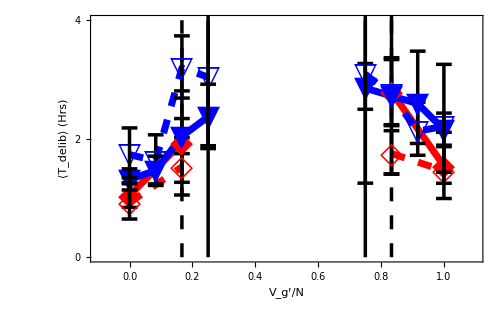

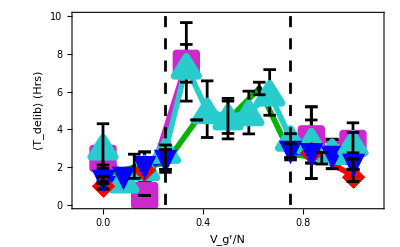

```mathematica
(*OR 6, OR 12: criminal and civil*)
```

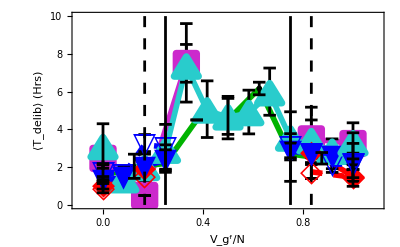

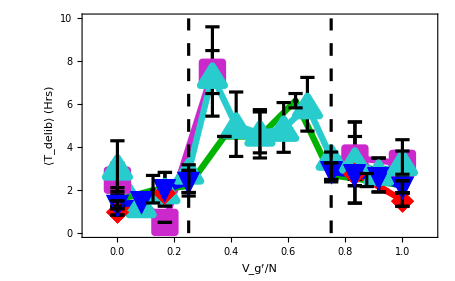

```mathematica
(*OR 6, OR 12 civil ONLY*)
```

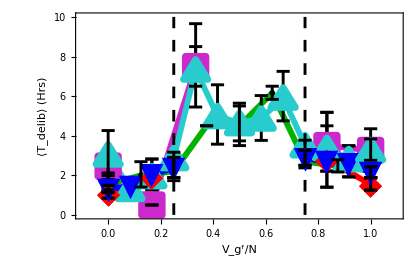
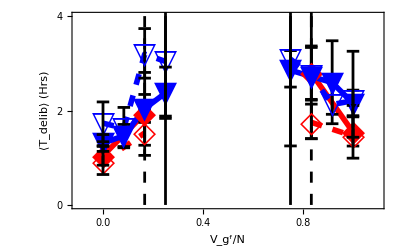

```mathematica
(*OR criminal (open markers, dashed) and civil (closed markers, solid) cases*)
```

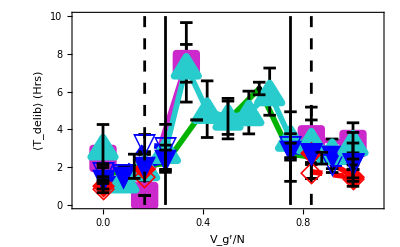

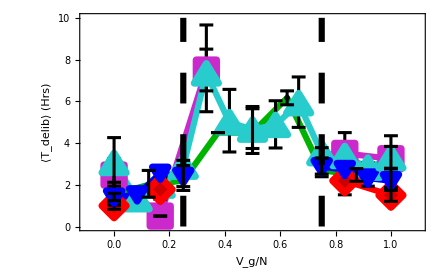
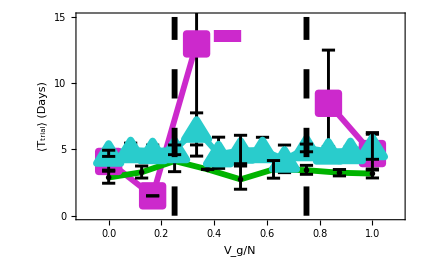

```mathematica
`
```

```mathematica
LengthVsOutcomeOR6Civil=Table[
{(i-1)/6,Log10[Length[Flatten[JuryTimeVsOutcomeOR6Civil[[i]]]]]}
,{i,Length[JuryTimeVsOutcomeOR6Civil]}]
LengthVsOutcomeOR6Criminal=Table[
{(i-1)/6,Log10[Length[Flatten[JuryTimeVsOutcomeOR6Criminal[[i]]]]]}
,{i,Length[JuryTimeVsOutcomeOR6Criminal]}]

LengthVsOutcomeOR12Civil=Table[
{(i-1)/12,Log10[Length[Flatten[JuryTimeVsOutcomeOR12Civil[[i]]]]]}
,{i,Length[JuryTimeVsOutcomeOR12Civil]}]

LengthVsOutcomeOR12Criminal=Table[
{(i-1)/12,Log10[Length[Flatten[JuryTimeVsOutcomeOR12Criminal[[i]]]]]}
,{i,Length[JuryTimeVsOutcomeOR12Criminal]}]

LengthVsOutcomeCA6=Table[
{(i-1)/6,Log10[Length[Flatten[JuryTimeVsOutcome6SF[[i]]]]]}
,{i,Length[JuryTimeVsOutcome6SF]}]

LengthVsOutcomeCA8=Table[
{(i-1)/8,Log10[Length[Flatten[JuryTimeVsOutcome8SF[[i]]]]]}
,{i,Length[JuryTimeVsOutcome8SF]}]

LengthVsOutcomeCA12=Table[
{(i-1)/12,Log10[Length[Flatten[JuryTimeVsOutcome12SF[[i]]]]]}
,{i,Length[JuryTimeVsOutcome12SF]}]



ListPlot[
{LengthVsOutcomeOR6Civil,LengthVsOutcomeOR6Criminal,LengthVsOutcomeOR12Civil,LengthVsOutcomeOR12Criminal,LengthVsOutcomeCA6,LengthVsOutcomeCA8,LengthVsOutcomeCA12,{{0.25,-.1},{0.25,3}},{{0.75,-.1},{0.75,3}},{{1/6,0},{1/6,3}},{{5/6,0},{5/6,3}}},
PlotMarkers->{Style["◆",FontSize->30],
Style["◇",FontSize->30],
Style["▼",FontSize->30],
Style["▽",FontSize->30],Style["■",FontSize->30],Style["●",FontSize->30],Style["▲",FontSize->30],"","","",""},
Joined->True,
PlotStyle->{{Red,Thickness[0.01]},
{Red,Thickness[0.01],Dashing[0.02]},
{Blue,Thickness[0.01]},
{Blue,Thickness[0.01],Dashing[0.02]},
{Darker[Magenta],Thickness[0.01]},
{RGBColor[0,0.7,0],Thickness[0.01]},
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]},
{Black,Thickness[0.005]},
{Black,Thickness[0.005]},
{Black,Dashing[0.02],Thickness[0.005]},
{Black,Dashing[0.02],Thickness[0.005]}},
Frame->True,Axes->False,
PlotRange->{{-0.1,1.1},{-0.1,3}},FrameLabel->{Style["V_g^f/N",FontFamily->"Arial",FontSize->25,FontColor->Black],
Style["# Cases",FontFamily->"Arial",FontSize->25,FontColor->Black]},
FrameTicksStyle->Directive[25,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{{
LogTicks[0,4,TickLabelStep->1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LogTicks[0,4,TickLabelStep->1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
},
{
LinTicks[0.,1,0.2,1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0.,1,0.2,1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}},
PlotLegend->{
Style["OR 6",FontFamily->"Arial",FontSize->20],
Style["OR 12",FontFamily->"Arial",FontSize->20],
Style["CA 6",FontFamily->"Arial",FontSize->20],
Style["CA 8",FontFamily->"Arial",FontSize->20],
Style["CA 12",FontFamily->"Arial",FontSize->20]
}
]

ListPlot[
{LengthVsOutcomeOR6Civil,LengthVsOutcomeOR6Civil,LengthVsOutcomeOR12Civil,LengthVsOutcomeOR12Civil,LengthVsOutcomeCA6,LengthVsOutcomeCA8,LengthVsOutcomeCA12,{{0.25,-.1},{0.25,3}},{{0.75,-.1},{0.75,3}}},
PlotMarkers->{Style["◆",FontSize->30],
Style["◇",FontSize->30],
Style["▼",FontSize->30],
Style["▽",FontSize->30],Style["■",FontSize->30],Style["●",FontSize->30],Style["▲",FontSize->30],"","","",""},
Joined->True,
PlotStyle->{{Red,Thickness[0.01]},
{Red,Thickness[0.01],Dashing[0.02]},
{Blue,Thickness[0.01]},
{Blue,Thickness[0.01],Dashing[0.02]},
{Darker[Magenta],Thickness[0.01]},
{RGBColor[0,0.7,0],Thickness[0.01]},
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]},
{Black,Dashing[0.02],Thickness[0.005]},
{Black,Dashing[0.02],Thickness[0.005]}},
Frame->True,Axes->False,
PlotRange->{{-0.1,1.1},{-0.1,3}},FrameLabel->{Style["V_g^f/N",FontFamily->"Arial",FontSize->25,FontColor->Black],
Style["# Cases",FontFamily->"Arial",FontSize->25,FontColor->Black]},
FrameTicksStyle->Directive[25,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{{
LogTicks[0,4,TickLabelStep->1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LogTicks[0,4,TickLabelStep->1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
},
{
LinTicks[0.,1,0.2,1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0.,1,0.2,1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}},
PlotLegend->{
Style["OR 6",FontFamily->"Arial",FontSize->20],
Style["OR 12",FontFamily->"Arial",FontSize->20],
Style["CA 6",FontFamily->"Arial",FontSize->20],
Style["CA 8",FontFamily->"Arial",FontSize->20],
Style["CA 12",FontFamily->"Arial",FontSize->20]
}
]
```

{{0,Log[28]/Log[10]},{1/6,Log[7]/Log[10]},{1/3,-∞},{1/2,-∞},{2/3,-∞},{5/6,Log[21]/Log[10]},{1,Log[45]/Log[10]}}

{{0,Log[21]/Log[10]},{1/6,Log[5]/Log[10]},{1/3,-∞},{1/2,-∞},{2/3,-∞},{5/6,Log[29]/Log[10]},{1,Log[49]/Log[10]}}

{{0,Log[105]/Log[10]},{1/12,Log[44]/Log[10]},{1/6,Log[55]/Log[10]},{1/4,Log[50]/Log[10]},{1/3,-∞},{5/12,-∞},{1/2,-∞},{7/12,-∞},{2/3,-∞},{3/4,Log[90]/Log[10]},{5/6,Log[77]/Log[10]},{11/12,Log[50]/Log[10]},{1,Log[89]/Log[10]}}

{{0,Log[32]/Log[10]},{1/12,Log[22]/Log[10]},{1/6,Log[44]/Log[10]},{1/4,Log[2]/Log[10]},{1/3,-∞},{5/12,-∞},{1/2,-∞},{7/12,-∞},{2/3,-∞},{3/4,Log[2]/Log[10]},{5/6,Log[83]/Log[10]},{11/12,Log[71]/Log[10]},{1,Log[118]/Log[10]}}

{{0,Log[28]/Log[10]},{1/6,0},{1/3,Log[2]/Log[10]},{1/2,-∞},{2/3,-∞},{5/6,Log[2]/Log[10]},{1,Log[20]/Log[10]}}

{{0,Log[21]/Log[10]},{1/8,Log[32]/Log[10]},{1/4,Log[57]/Log[10]},{3/8,0},{1/2,Log[4]/Log[10]},{5/8,Log[3]/Log[10]},{3/4,Log[96]/Log[10]},{7/8,Log[87]/Log[10]},{1,Log[37]/Log[10]}}

{{0,Log[25]/Log[10]},{1/12,Log[164]/Log[10]},{1/6,Log[198]/Log[10]},{1/4,Log[249]/Log[10]},{1/3,Log[19]/Log[10]},{5/12,Log[14]/Log[10]},{1/2,Log[21]/Log[10]},{7/12,Log[19]/Log[10]},{2/3,Log[12]/Log[10]},{3/4,Log[389]/Log[10]},{5/6,Log[319]/Log[10]},{11/12,Log[237]/Log[10]},{1,Log[62]/Log[10]}}

```mathematica
(*OR 6, OR 12: criminal and civil*)
```

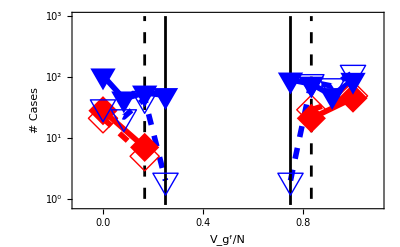

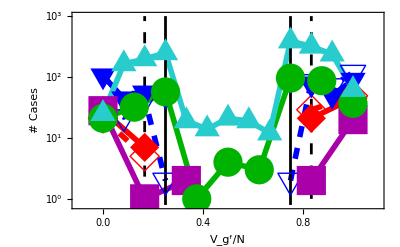

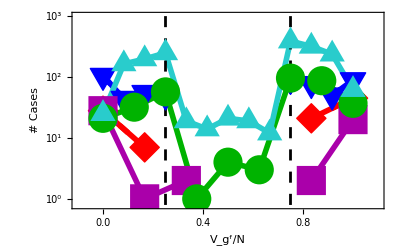

```mathematica
(*OR 6, OR 12 CIVIL ONLY*)
```

```mathematica
(*OR criminal (open markers, dashed) and civil (closed markers, solid) cases*)
```

```mathematica
Total[{{0,21},{1/6,5},{1/3,0},{1/2,0},{2/3,0},{5/6,29},{1,49}}]
```

{7/2,104}

```mathematica
Total[{{0,32},{1/12,22},{1/6,44},{1/4,2},{1/3,0},{5/12,0},{1/2,0},{7/12,0},{2/3,0},{3/4,2},{5/6,83},{11/12,71},{1,118}}]
```

{13/2,374}

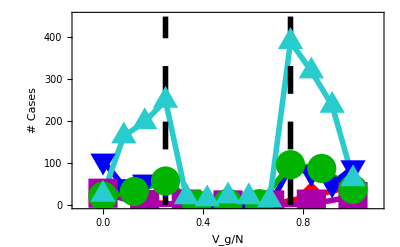

```mathematica
(*OR Civil cases only*)
```

```mathematica
Total@LengthVsOutcomeOR6[[;;,2]](*~1/2 of all cases*)
Total@LengthVsOutcomeOR12[[;;,2]](*~1/2 of all cases with civil*)
```

101

560

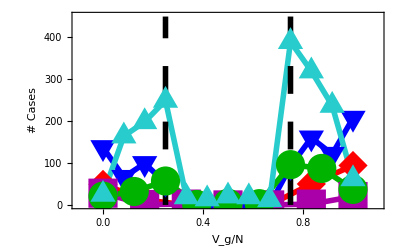

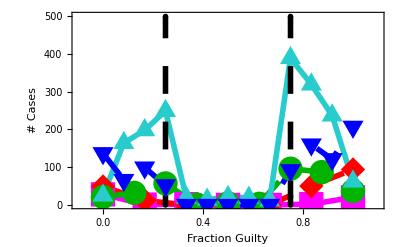

```mathematica
N[450/3200]
```

0.140625

{50,27,65,80,114,135,79,79,40,110,50,127,33,15,65,27,146,50,20,35,24,30,30,35,20,14,74,25,17,124,26,30,30,115,33,60,45,30,130,65,45,20,50,15,150,210,25,15,85,115,55,290,90,120,120,155,59,103,45,40,85,125,55,75,256,79,310,20,113,55,53,85,85,175,15,95,82,40,57,125,240,75,105,120,60,120,120,15,265,112,68,31,36,88,55,90,90,60,100,1617,160,185,48,135,75,203,53,125,71,47,115,48,6,60,210,40,25,140,80,20,120,40,54,64,27,40,10,50,70,35,63,115,80,165,40,90,220,90,66,45,30,95,115,30,5,40,45,30,20,60,52,120,195,82,185,45,82,90,88,23,45,71,34,50,45,80,124,90,69,80,95,96,15,15,119,34,45,16,195,85,39,10,160,90,32,32,379,55,185,115,45,37,325,25,25,66,30,30,157,1036,25,39,153,210,210}

{{0,137},{1/12,66},{1/6,99},{1/4,52},{1/3,0},{5/12,0},{1/2,0},{7/12,0},{2/3,0},{3/4,92},{5/6,160},{11/12,121},{1,207}}

{{0,28},{1/6,1},{1/3,2},{1/2,0},{2/3,0},{5/6,2},{1,20}}

{{0,21},{1/8,32},{1/4,57},{3/8,1},{1/2,4},{5/8,3},{3/4,96},{7/8,87},{1,37}}

{{0,25},{1/12,164},{1/6,198},{1/4,249},{1/3,19},{5/12,14},{1/2,21},{7/12,19},{2/3,12},{3/4,389},{5/6,319},{11/12,237},{1,62}}

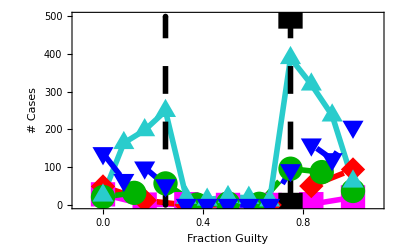

```mathematica
CDFOR6=Flatten[JuryTimeVsOutcomeOR6]

LengthVsOutcomeOR12=Table[
{(i-1)/12,Length[Flatten[JuryTimeVsOutcomeOR12[[i]]]]}
,{i,Length[JuryTimeVsOutcomeOR12]}]

LengthVsOutcomeCA6=Table[
{(i-1)/6,Length[Flatten[JuryTimeVsOutcome6SF[[i]]]]}
,{i,Length[JuryTimeVsOutcome6SF]}]

LengthVsOutcomeCA8=Table[
{(i-1)/8,Length[Flatten[JuryTimeVsOutcome8SF[[i]]]]}
,{i,Length[JuryTimeVsOutcome8SF]}]

LengthVsOutcomeCA12=Table[
{(i-1)/12,Length[Flatten[JuryTimeVsOutcome12SF[[i]]]]}
,{i,Length[JuryTimeVsOutcome12SF]}]



ListPlot[
{LengthVsOutcomeCA6,LengthVsOutcomeOR6,LengthVsOutcomeCA8,LengthVsOutcomeCA12,LengthVsOutcomeOR12,{{0.25,0},{0.25,499}},{{0.75,0},{0.75,499}}},
PlotMarkers->{Style["■",FontSize->25],Style["◆",FontSize->25],Style["●",FontSize->25],Style["▲",FontSize->25],Style["▼",FontSize->25],Style["▮",FontSize->25]},
Joined->True,
PlotStyle->{{Magenta,Thickness[0.01]},{Red,Thickness[0.01],Dashing[0.05]},
{RGBColor[0,0.7,0],Thickness[0.01],Dashing[0.05]},
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]},{Blue,Thickness[0.01],Dashing[0.05]},{Black,Dashing[0.05],Thickness[0.01]},{Black,Dashing[0.05],Thickness[0.01]}},
Frame->True,Axes->False,
PlotRange->{{-0.1,1.1},{0,500}},FrameLabel->{Style["Fraction Guilty",FontFamily->"Arial",FontSize->25,FontColor->Black],
Style["# Cases",FontFamily->"Arial",FontSize->25,FontColor->Black]},
FrameTicksStyle->Directive[25,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{{
LinTicks[0,500,100,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,500,100,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
},
{
LinTicks[0.,1,0.2,1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0.,1,0.2,1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}},
PlotLegend->{Style["CA 6",FontFamily->"Arial",FontSize->20],
Style["OR 6",FontFamily->"Arial",FontSize->20],
Style["CA 8",FontFamily->"Arial",FontSize->20],
Style["CA 12",FontFamily->"Arial",FontSize->20],
Style["OR 12",FontFamily->"Arial",FontSize->20]
}
]
```

```mathematica
data=Import["~/Dropbox/Competing Infections/Paper/Trial Deliberations/Data/CA/mfsas_burghardt01.xlsx"];




JuryTimeVsOutcome12SF=Table[
majority=N[j 100+(12-j)];
(*minority=N[(12-j) 100+j];*)
Flatten[
DeleteCases[
DeleteCases[
Table[If[data[[1,i,10]]=="2:HOURS"
&&ToString[data[[1,i,19]]]≠".:BLANK"
&&ToString[data[[1,i,19]]]≠".J:CODING ERROR",
If[
data[[1,i,19]]==majority,
data[[1,i,9]]]],{i,Length[data[[1]]]}],Null],".:BLANK"]],{j,0,12}];
JuryTimeVsOutcome12SF===Table[
majority=N[j 100+(12-j)];
(*minority=N[(12-j) 100+j];*)
Flatten[
DeleteCases[
DeleteCases[
Table[If[data[[1,i,10]]=="2:HOURS"
&&ToString[data[[1,i,19]]]≠".:BLANK"
&&ToString[data[[1,i,19]]]≠".J:CODING ERROR",
If[
data[[1,i,19]]==majority,
data[[1,i,9]]]],{i,Length[data[[1]]]}],Null],".:BLANK"]],{j,0,12}]
JuryTimeVsOutcome8SF=Table[
majority=N[j 100+(8-j)];
(*minority=N[(8-j) 100+j];*)
Flatten[DeleteCases[DeleteCases[Table[If[data[[1,i,10]]=="2:HOURS"&&(data[[1,i,19]]==majority(*||data[[1,i,19]]==minority*)),data[[1,i,9]]],{i,Length[data[[1]]]}],Null],".:BLANK"]],{j,0,8}];
JuryTimeVsOutcome6SF=Table[
majority=N[j 100+(6-j)];
(*minority=N[(6-j) 100+j];*)
Flatten[DeleteCases[DeleteCases[Table[If[data[[1,i,10]]=="2:HOURS"&&ToString[data[[1,i,19]]]≠".:BLANK"&&ToString[data[[1,i,19]]]≠".J:CODING ERROR",
If[
data[[1,i,19]]==majority(*||data[[1,i,19]]==minority*)(*Only look at outcomes where we KNOW guilt/innocence*)
(*||
(majority==12&&ToString[data[[1,i,19]]]=="9999:UNANIMOUS"&&ToString[data[[1,i,24]]]==".:BLANK")*)(*||(majority==6&&minority==0&&ToString[data[[1,i,19]]]=="9999:UNANIMOUS"&&ToString[data[[1,i,24]]]=="1:YES")*)
,data[[1,i,9]]]],{i,Length[data[[1]]]}],Null],".:BLANK"]],{j,0,6}];
(*OR 6*)
temp=HistogramList[DeleteCases[Flatten[JuryTimeVsOutcomeOR6Civil],Null],{0,Max[JuryTimeVsOutcomeOR6Civil],1}];
cdfOR6Civil=1-(Accumulate[temp[[2,Length[temp[[2]]];;1;;-1]]])[[Length[temp[[2]]];;1;;-1]]/Total[temp[[2]]];
temp=HistogramList[DeleteCases[Flatten[JuryTimeVsOutcomeOR6Criminal],Null],{0,Max[JuryTimeVsOutcomeOR6Criminal],1}];
cdfOR6Criminal=1-(Accumulate[temp[[2,Length[temp[[2]]];;1;;-1]]])[[Length[temp[[2]]];;1;;-1]]/Total[temp[[2]]];
(*OR 12*)
temp=HistogramList[Flatten[JuryTimeVsOutcomeOR12Civil],{0,Max[JuryTimeVsOutcomeOR12Civil],1}];
cdfOR12Civil=1-(Accumulate[temp[[2,Length[temp[[2]]];;1;;-1]]])[[Length[temp[[2]]];;1;;-1]]/Total[temp[[2]]];
temp=HistogramList[Flatten[JuryTimeVsOutcomeOR12Criminal],{0,Max[JuryTimeVsOutcomeOR12Criminal],1}];
cdfOR12Criminal=1-(Accumulate[temp[[2,Length[temp[[2]]];;1;;-1]]])[[Length[temp[[2]]];;1;;-1]]/Total[temp[[2]]];
(*CA 6*)
JuryTimeVsOutcome6SF
temp=HistogramList[DeleteCases[Flatten[JuryTimeVsOutcome6SF],Abs[Null]]-1,{0,Max[JuryTimeVsOutcome6SF],1}];
cdfCA6=1-(Accumulate[temp[[2,Length[temp[[2]]];;1;;-1]]])[[Length[temp[[2]]];;1;;-1]]/Total[temp[[2]]]
JuryTimeVsOutcome6SF

(*CA 8*)

temp=HistogramList[DeleteCases[Flatten[JuryTimeVsOutcome8SF],Abs[Null]]-1,{0,Max[JuryTimeVsOutcome8SF],1}];
cdfCA8=1-(Accumulate[temp[[2,Length[temp[[2]]];;1;;-1]]])[[Length[temp[[2]]];;1;;-1]]/Total[temp[[2]]]

(*CA 12*)

temp=HistogramList[DeleteCases[Flatten[JuryTimeVsOutcome12SF],Abs[Null]]-1,{0,Max[JuryTimeVsOutcome12SF],1}];
cdfCA12=1-(Accumulate[temp[[2,Length[temp[[2]]];;1;;-1]]])[[Length[temp[[2]]];;1;;-1]]/Total[temp[[2]]]

(*WA*)
temp=HistogramList[DeleteCases[Flatten[TrialTimeDelibTimeWA[[;;,2]]],Null],{0,Max[TrialTimeDelibTimeWA[[;;,2]]],1}];
cdfWA=1-(Accumulate[temp[[2,Length[temp[[2]]];;1;;-1]]])[[Length[temp[[2]]];;1;;-1]]/Total[temp[[2]]]

(*NE*)
temp=HistogramList[DeleteCases[Flatten[TrialTimeDelibTimeNE[[;;,2]]],Null],{0,Max[TrialTimeDelibTimeNE[[;;,2]]],1}];
cdfNE=1-(Accumulate[temp[[2,Length[temp[[2]]];;1;;-1]]])[[Length[temp[[2]]];;1;;-1]]/Total[temp[[2]]]

poly=Flatten[Table[{{Cos[t+0.5π/5],Sin[t+0.5π/5]},{0.38Cos[t+1.5 π/5],0.38Sin[t+1.5 π/5]}},{t,0+2π/5,4 π+2π/5,2 π/5}],1][[;;10]];


ListPlot[{
Flatten[Table[If[i==Length[cdfOR6Civil],{{i/60,0},{(i+1)/60,0}},{{i/60,1-cdfOR6Civil[[i+1]]},{(i+1)/60,1-cdfOR6Civil[[i+1]]}}],{i,0,Length[cdfOR6Civil]}],1],

Flatten[Table[If[i==Length[cdfOR6Criminal],{{i/60,0},{(i+1)/60,0}},{{i/60,1-cdfOR6Criminal[[i+1]]},{(i+1)/60,1-cdfOR6Criminal[[i+1]]}}],{i,0,Length[cdfOR6Criminal]}],1],
Flatten[Table[If[i==Length[cdfOR12Civil],{{i/60,0},{(i+1)/60,0}},{{i/60,1-cdfOR12Civil[[i+1]]},{(i+1)/60,1-cdfOR12Civil[[i+1]]}}],{i,0,Length[cdfOR12Civil]}],1],

Flatten[Table[If[i==Length[cdfOR12Criminal],{{i/60,0},{(i+1)/60,0}},{{i/60,1-cdfOR12Criminal[[i+1]]},{(i+1)/60,1-cdfOR12Criminal[[i+1]]}}],{i,0,Length[cdfOR12Criminal]}],1],

Flatten[Table[If[i==Length[cdfCA6],{{i,0},{(i+1),0}},{{i,1-cdfCA6[[i+1]]},{i+1,1-cdfCA6[[i+1]]}}],{i,0,Length[cdfCA6]}],1],
Flatten[Table[If[i==Length[cdfCA8],{{i,0},{(i+1),0}},{{i,1-cdfCA8[[i+1]]},{i+1,1-cdfCA8[[i+1]]}}],{i,0,Length[cdfCA8]}],1],
Flatten[Table[If[i==Length[cdfCA12],{{i,0},{(i+1),0}},{{i,1-cdfCA12[[i+1]]},{i+1,1-cdfCA12[[i+1]]}}],{i,0,Length[cdfCA12]}],1],
Flatten[Table[If[i==Length[cdfWA],{{i,0},{(i+1),0}},{{i,1-cdfWA[[i+1]]},{i+1,1-cdfWA[[i+1]]}}],{i,0,Length[cdfWA]}],1],
Flatten[Table[If[i==Length[cdfNE],{{i/4,0},{(i+1)/4,0}},{{i/4,1-cdfNE[[i+1]]},{(i+1)/4,1-cdfNE[[i+1]]}}],{i,0,Length[cdfNE]}],1],

Flatten[Table[If[i==Length[cdfOR6Civil],{{(i+1/2)/60,0}},{{(i+1/2)/60,1-cdfOR6Civil[[i+1]]}}],{i,0,Length[cdfOR6Civil],15}],1],
Flatten[Table[If[i==Length[cdfOR6Criminal],{{(i+1/2)/60,0}},{{(i+1/2)/60,1-cdfOR6Criminal[[i+1]]}}],{i,0,Length[cdfOR6Criminal],15}],1],
Flatten[Table[If[i==Length[cdfOR12Civil],{{(i+1/2)/60,0}},{{(i+1/2)/60,1-cdfOR12Civil[[i+1]]}}],{i,0,Length[cdfOR12Civil],15}],1],
Flatten[Table[If[i==Length[cdfOR12Criminal],{{(i+1/2)/60,0}},{{(i+1/2)/60,1-cdfOR12Criminal[[i+1]]}}],{i,0,Length[cdfOR12Criminal],15}],1],
Flatten[Table[If[i==Length[cdfCA6],{{(i+1/2),0}},{{i+1/2,1-cdfCA6[[i+1]]}}],{i,0,Length[cdfCA6]}],1],
Flatten[Table[If[i==Length[cdfCA8],{{i+1/2,0}},{{i+1/2,1-cdfCA8[[i+1]]}}],{i,0,Length[cdfCA8]}],1],
Flatten[Table[If[i==Length[cdfCA12],{{i+1/2,0}},{{i+1/2,1-cdfCA12[[i+1]]}}],{i,0,Length[cdfCA12]}],1],
Flatten[Table[If[i==Length[cdfWA],{{i+1/2,0}},{{i+1/2,1-cdfWA[[i+1]]}}],{i,0,Length[cdfWA]}],1],
Flatten[Table[If[i==Length[cdfNE],{{(i+1/2)/4,0}},{{(i+1/2)/4,1-cdfNE[[i+1]]}}],{i,0,Length[cdfNE]}],1]
},
PlotMarkers->{
"","","","","","","","","",Style["◆",FontSize->30],
Style["◇",FontSize->30],
Style["▼",FontSize->30],
Style["▽",FontSize->30],
Style["■",FontSize->30],
Style["●",FontSize->30],
Style["▲",FontSize->30],
Graphics[{GrayLevel[1],EdgeForm[{AbsoluteThickness[2],Black}],Polygon[poly]} ,PlotRangePadding->0,ImageSize->28],
Style["×",FontSize->40,FontColor->RGBColor[0.9,0.5,0],Bold]
},
Joined->{True,True,True,True,True,True,True,True,True,False,False,False,False,False,False,False,False,False},
PlotStyle->{{Red,Thickness[0.01]},
{Red,Thickness[0.01],Dashing[0.05]},
{Blue,Thickness[0.01]},
{Blue,Thickness[0.01],Dashing[0.05]},
{Darker[Magenta],Thickness[0.01]},
{RGBColor[0,0.7,0],Thickness[0.01]},
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]},
{Black,Thickness[0.01]},
{RGBColor[0.9,0.5,0],Thickness[0.01]}},
Frame->True,
Axes->False,
PlotRange->{{0,10},{0,1.2}},FrameLabel->{Style["T_delib (Hrs)",FontFamily->"Arial",FontSize->25,FontColor->Black],
Style["Pr(T ≥ T_delib)",FontFamily->"Arial",FontSize->25,FontColor->Black]},
FrameTicksStyle->Directive[25,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{{
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
},
{
LinTicks[0.,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0.,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}},
PlotLegend->{"","","","","","","",
Style["OR 6",FontFamily->"Arial",FontSize->20],
Style["OR 12",FontFamily->"Arial",FontSize->20],
Style["CA 6",FontFamily->"Arial",FontSize->20],
Style["CA 8",FontFamily->"Arial",FontSize->20],
Style["CA 12",FontFamily->"Arial",FontSize->20],
Style["WA",FontFamily->"Arial",FontSize->20],
Style["NE",FontFamily->"Arial",FontSize->20]
}
]




ListPlot[{
Flatten[Table[If[i==Length[cdfOR6Civil],{{i/60,0},{(i+1)/60,0}},{{i/60,1-cdfOR6Civil[[i+1]]},{(i+1)/60,1-cdfOR6Civil[[i+1]]}}],{i,0,Length[cdfOR6Civil]}],1],

Flatten[Table[If[i==Length[cdfOR12Civil],{{i/60,0},{(i+1)/60,0}},{{i/60,1-cdfOR12Civil[[i+1]]},{(i+1)/60,1-cdfOR12Civil[[i+1]]}}],{i,0,Length[cdfOR12Civil]}],1],

Flatten[Table[If[i==Length[cdfCA6],{{i,0},{(i+1),0}},{{i,1-cdfCA6[[i+1]]},{i+1,1-cdfCA6[[i+1]]}}],{i,0,Length[cdfCA6]}],1],
Flatten[Table[If[i==Length[cdfCA8],{{i,0},{(i+1),0}},{{i,1-cdfCA8[[i+1]]},{i+1,1-cdfCA8[[i+1]]}}],{i,0,Length[cdfCA8]}],1],
Flatten[Table[If[i==Length[cdfCA12],{{i,0},{(i+1),0}},{{i,1-cdfCA12[[i+1]]},{i+1,1-cdfCA12[[i+1]]}}],{i,0,Length[cdfCA12]}],1],
Flatten[Table[If[i==Length[cdfWA],{{i,0},{(i+1),0}},{{i,1-cdfWA[[i+1]]},{i+1,1-cdfWA[[i+1]]}}],{i,0,Length[cdfWA]}],1],
Flatten[Table[If[i==Length[cdfNE],{{i/4,0},{(i+1)/4,0}},{{i/4,1-cdfNE[[i+1]]},{(i+1)/4,1-cdfNE[[i+1]]}}],{i,0,Length[cdfNE]}],1],

Flatten[Table[If[i==Length[cdfOR6Civil],{{(i+1/2)/60,0}},{{(i+1/2)/60,1-cdfOR6Civil[[i+1]]}}],{i,0,Length[cdfOR6Civil],15}],1],
Flatten[Table[If[i==Length[cdfOR12Civil],{{(i+1/2)/60,0}},{{(i+1/2)/60,1-cdfOR12Civil[[i+1]]}}],{i,0,Length[cdfOR12Civil],15}],1],
Flatten[Table[If[i==Length[cdfCA6],{{(i+1/2),0}},{{i+1/2,1-cdfCA6[[i+1]]}}],{i,0,Length[cdfCA6]}],1],
Flatten[Table[If[i==Length[cdfCA8],{{i+1/2,0}},{{i+1/2,1-cdfCA8[[i+1]]}}],{i,0,Length[cdfCA8]}],1],
Flatten[Table[If[i==Length[cdfCA12],{{i+1/2,0}},{{i+1/2,1-cdfCA12[[i+1]]}}],{i,0,Length[cdfCA12]}],1],
Flatten[Table[If[i==Length[cdfWA],{{i+1/2,0}},{{i+1/2,1-cdfWA[[i+1]]}}],{i,0,Length[cdfWA]}],1],
Flatten[Table[If[i==Length[cdfNE],{{(i+1/2)/4,0}},{{(i+1/2)/4,1-cdfNE[[i+1]]}}],{i,0,Length[cdfNE]}],1]
},
PlotMarkers->{
"","","","","","","",Style["◆",FontSize->30],
Style["▼",FontSize->30],
Style["■",FontSize->30],
Style["●",FontSize->30],
Style["▲",FontSize->30],
Graphics[{GrayLevel[1],EdgeForm[{AbsoluteThickness[2],Black}],Polygon[poly]} ,PlotRangePadding->0,ImageSize->28],
Style["×",FontSize->40,FontColor->RGBColor[0.9,0.5,0],Bold]
},
Joined->{True,True,True,True,True,True,True,False,False,False,False,False,False,False},
PlotStyle->{{Red,Thickness[0.01]},
{Blue,Thickness[0.01]},
{Darker[Magenta],Thickness[0.01]},
{RGBColor[0,0.7,0],Thickness[0.01]},
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]},
{Black,Thickness[0.01]},
{RGBColor[0.9,0.5,0],Thickness[0.01]}},
Frame->True,
Axes->False,
PlotRange->{{0,10},{0,1.2}},FrameLabel->{Style["T_delib (Hrs)",FontFamily->"Arial",FontSize->25,FontColor->Black],
Style["Pr(T ≥ T_delib)",FontFamily->"Arial",FontSize->25,FontColor->Black]},
FrameTicksStyle->Directive[25,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{{
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
},
{
LinTicks[0.,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0.,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}},
PlotLegend->{"","","","","","","",
Style["OR 6",FontFamily->"Arial",FontSize->20],
Style["OR 12",FontFamily->"Arial",FontSize->20],
Style["CA 6",FontFamily->"Arial",FontSize->20],
Style["CA 8",FontFamily->"Arial",FontSize->20],
Style["CA 12",FontFamily->"Arial",FontSize->20],
Style["WA",FontFamily->"Arial",FontSize->20],
Style["NE",FontFamily->"Arial",FontSize->20]
}
]
```

True

{{2.,3.,3.,2.,3.,1.,9.,1.,1.,3.,3.,1.,3.,5.,4.,3.,12.,1.,3.,1.,1.,1.,4.,3.,2.,4.,1.,3.},{1.},{9.,7.},{},{},{3.,5.},{2.,4.,3.,6.,3.,4.,7.,3.,3.,1.,12.,1.,5.,2.,1.,8.,2.,6.,1.,1.}}

{0,15/53,21/53,36/53,41/53,44/53,46/53,48/53,49/53,51/53,51/53,51/53}

{{2.,3.,3.,2.,3.,1.,9.,1.,1.,3.,3.,1.,3.,5.,4.,3.,12.,1.,3.,1.,1.,1.,4.,3.,2.,4.,1.,3.},{1.},{9.,7.},{},{},{3.,5.},{2.,4.,3.,6.,3.,4.,7.,3.,3.,1.,12.,1.,5.,2.,1.,8.,2.,6.,1.,1.}}

{0,93/338,159/338,243/338,141/169,155/169,317/338,329/338,333/338,167/169,167/169,167/169}

{0,205/864,349/864,365/576,107/144,1481/1728,779/864,269/288,545/576,413/432,1661/1728,835/864,859/864,215/216,1721/1728,1721/1728,287/288,1723/1728,1723/1728,1723/1728,863/864,863/864,863/864,863/864,863/864,863/864,863/864,863/864,1727/1728}

{0,0,29/127,68/127,95/127,111/127,117/127,122/127}

{0,3/65,22/65,36/65,9/13,49/65,56/65,58/65,12/13,62/65,62/65,62/65,62/65,63/65,64/65,64/65,1,1,1,1}

```mathematica
(*OR 6, OR 12 ONLY     *)
```

```mathematica
(*OR 6, OR 12 CIVIL ONLY*)
```

```mathematica
(*Civil cases only*)
```

-Graphics-

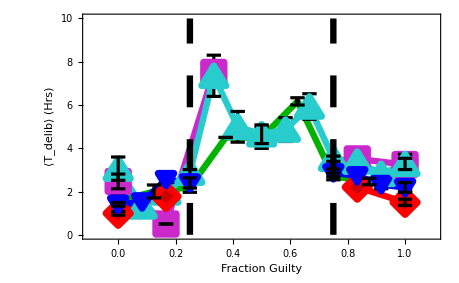

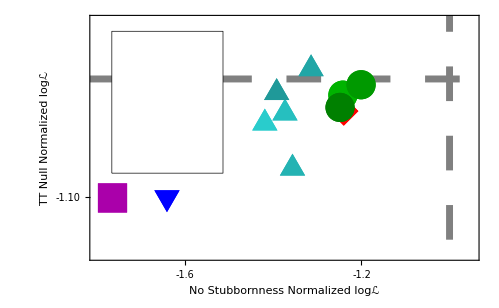

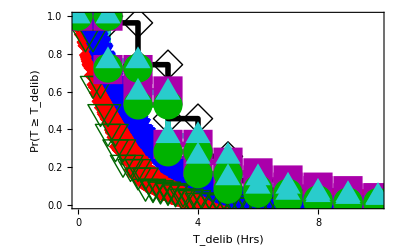

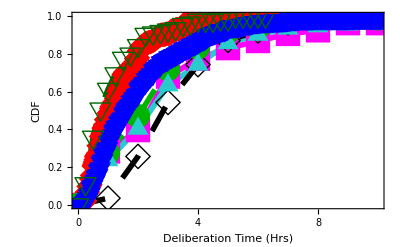

```mathematica
temp=HistogramList[DeleteCases[Flatten[JuryTimeVsOutcome12SF],Abs[Null]]-1,{0,Max[JuryTimeVsOutcome12SF],1}]
cdfCA12=1-(Accumulate[temp[[2,Length[temp[[2]]];;1;;-1]]])[[Length[temp[[2]]];;1;;-1]]/Total[temp[[2]]]
```

{{0,1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29},{410,288,397,189,197,77,56,21,17,9,9,48,2,1,0,1,1,0,0,3,0,0,0,0,0,0,0,1,1}}

{0,205/864,349/864,365/576,107/144,1481/1728,779/864,269/288,545/576,413/432,1661/1728,835/864,859/864,215/216,1721/1728,1721/1728,287/288,1723/1728,1723/1728,1723/1728,863/864,863/864,863/864,863/864,863/864,863/864,863/864,863/864,1727/1728}

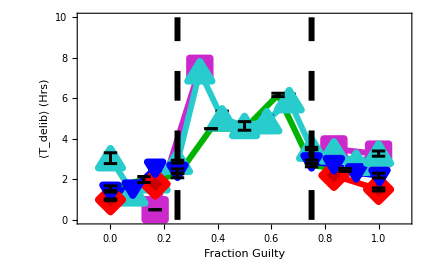

{49,12,0,0,0,49,94}

{1,30,9,13}

{1,30,9,13}

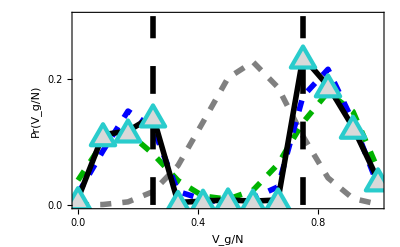

-Graphics-

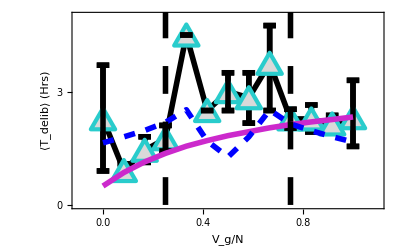

```mathematica
Needs["CustomTicks`"];
Needs["PlotLegends`"];
(*
Best fits
*)
Width={1.8};
(*CA*)
TrialTimeBinnedSF6=Table[outcome = TrialTimeDelibTimeVsOutcome6SF[[i]]; outcome[[;;,1]]-=2;LogBinnedList[outcome,Width][[;;,;;,2]],{i,7}];
TrialTimeBinnedSF8=Table[outcome = TrialTimeDelibTimeVsOutcome8SF[[i]]; outcome[[;;,1]]-=2;LogBinnedList[outcome,Width][[;;,;;,2]],{i,9}];
TrialTimeBinnedSF12=Table[outcome = TrialTimeDelibTimeVsOutcome12SF[[i]]; outcome[[;;,1]]-=2;LogBinnedList[outcome,Width][[;;,;;,2]],{i,13}];

TrialTimeBinnedSF6Hist=Table[If[Length[TrialTimeBinnedSF6[[i,j]]]>0,HistogramList[TrialTimeBinnedSF6[[i,j]]-1,{0,Round[Max[Flatten[TrialTimeBinnedSF6]]],1}][[2]],ConstantArray[0,Round[Max[Flatten[TrialTimeBinnedSF6]]]]],{j,Length[TrialTimeBinnedSF6[[1]]]},{i,Length[TrialTimeBinnedSF6]}];


TrialTimeBinnedSF8Hist=Table[If[Length[TrialTimeBinnedSF8[[i,j]]]>0,HistogramList[TrialTimeBinnedSF8[[i,j]]-1,{0,Round[Max[Flatten[TrialTimeBinnedSF8]]],1}][[2]],ConstantArray[0,Round[Max[Flatten[TrialTimeBinnedSF8]]]]],{j,Length[TrialTimeBinnedSF8[[1]]]},{i,Length[TrialTimeBinnedSF8]}];

TrialTimeBinnedSF12Hist=Table[If[Length[TrialTimeBinnedSF12[[i,j]]]>0,HistogramList[TrialTimeBinnedSF12[[i,j]]-1,{0,Round[Max[Flatten[TrialTimeBinnedSF12]]],1}][[2]],ConstantArray[0,Round[Max[Flatten[TrialTimeBinnedSF12]]]]],{j,Length[TrialTimeBinnedSF12[[1]]]},{i,Length[TrialTimeBinnedSF12]}];




(*
n=6;
CA6Influence=Import["~/Google Drive/DelibWork/DelibCode/Fit Code/Fits/InfluenceFits/CA6InfluenceVoteTimeBestFitModel_1minT.mat"];
CA6TT=Import["~/Google Drive/DelibWork/DelibCode/Fit Code/Fits/TTNullFits/CA6VoteTimeTTBestFitModel_1minT.mat"];
(*Time CDF*)
temp=HistogramList[DeleteCases[Flatten[JuryTimeVsOutcome6SF],Abs[Null]]-1,{0,Max[JuryTimeVsOutcome6SF],1}];
cdfCA6=1-(Accumulate[temp[[2,Length[temp[[2]]];;1;;-1]]])[[Length[temp[[2]]];;1;;-1]]/Total[temp[[2]]];
(*Vote Hist*)
SF6VoteHist=Total[Total[TrialTimeBinnedSF6Hist],{2}];

data=SF6VoteHist;
(*Vote Null Model*)
NumJurors = n Total[data];
NumJuries=Total[data];
MeanGuilty=N[Total[Table[(i-1) data[[i]],{i,n+1}]]/NumJuries]
PGuilty=N[MeanGuilty/n]
OneModelBinomial[k_]:=PDF[BinomialDistribution[n,PGuilty],k];
(*T vs Vote*)
CA6InfluenceTvsV=Table[Total[Table[i+0.5,{i,0,Length[CA6Influence[[1,1,1;;-2]]]-1}] (CA6Influence[[1,i,2;;-1]]-CA6Influence[[1,i,1;;-2]])/CA6Influence[[1,i,-1]]],{i,Length[CA6Influence[[1]]]}];
CA6InfluenceTvsV=Table[{{(i-1)/n,CA6InfluenceTvsV[[i]]},ErrorBar[0]},{i,Length[CA6InfluenceTvsV]}];

CA6TTNullTvsV=Table[Total[Table[i+0.5,{i,0,Length[CA6TT[[1,1,1;;-2]]]-1}] (CA6TT[[1,i,2;;-1]]-CA6TT[[1,i,1;;-2]])/CA6TT[[1,i,-1]]],{i,Length[CA6TT[[1]]]}];
CA6TTNullTvsV=Table[{{(i-1)/n,CA6TTNullTvsV[[i]]},ErrorBar[0]},{i,Length[CA6TTNullTvsV]}];

NumInnocent= Total[Table[(i-1) data[[i]],{i,Floor[n/2]}]];
MeanInnocent= NumInnocent/(Total[data[[1;;Floor[n/2]]]]);
PInnocent2=N[MeanInnocent/n];
NumGuilty = Total[Table[(i-1) data[[i]],{i,Floor[n/2]+1,n+1}]];
MeanGuilty=NumGuilty/(Total[data[[Floor[n/2]+1;;n+1]]]);
PGuilty2=N[MeanGuilty/n]
(*Weigh binomials by proportion of people in the innocent or guilty end*)
TwoModelBinomial[k_]:=PDF[BinomialDistribution[n,PGuilty2],k] Total[data[[Floor[n/2]+1;;n+1]]]/NumJuries+PDF[BinomialDistribution[n,PInnocent2],k]Total[data[[1;;Floor[n/2]]]]/NumJuries;

NModeMean= Table[(i-1),{i,n+1}];
NModelBinomial[k_]:=Total[Table[PDF[BinomialDistribution[n,NModeMean[[i]]/n],k] data[[i]],{i,n+1}]]/NumJuries;
Table[{i,N[NModelBinomial[i]]},{i,0,n}];


(*Plots*)
ListPlot[{Table[{(i-1)/n,CA6Influence[[1,i,-1]]},{i,n+1}],Table[{i/n,N[OneModelBinomial[i]]},{i,0,n}],Table[{i/n,N[TwoModelBinomial[i]]},{i,0,n}],
Table[{i/n,N[NModelBinomial[i]]},{i,0,n}],
Table[{i/n,data[[i+1]]/NumJuries},{i,0,n}]},
Joined->True,
PlotStyle->{{Blue,Thickness[0.01],Dashing[0.02]},
{Gray,Thickness[0.01],Dashing[0.02]},
{Red,Thickness[0.01],Dashing[0.02]},
{RGBColor[0,0.7,0],Thickness[0.01],Dashing[0.02]},
{Black,Thickness[0.01]}},
Frame->True,
Axes->False,
PlotRange->{{0,1},{0,0.7}},FrameLabel->{Style["Fraction Guilty",FontFamily->"Arial",FontSize->25,FontColor->Black],
Style["Pr(Fraction Guilty)",FontFamily->"Arial",FontSize->25,FontColor->Black]},
FrameTicksStyle->Directive[25,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{{
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
},
{
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}},
PlotLegend->{
Style["Influence Model",FontFamily->"Arial",FontSize->20],
Style["One Mode Null",FontFamily->"Arial",FontSize->20],
Style["Two Mode Null",FontFamily->"Arial",FontSize->20],
Style["N Mode Null",FontFamily->"Arial",FontSize->20],
Style["Empirical Data",FontFamily->"Arial",FontSize->20]
}
]

(*
Pr(T≥t)
*)(*
ListPlot[{1-Total[CA6Influence[[1]]],1-Total[CA6TT[[1]]],1-cdfCA6},
Joined->True,
PlotStyle->{{Blue,Thickness[0.01],Dashing[0.02]},
{Gray,Thickness[0.01],Dashing[0.02]},
{Black,Thickness[0.01]}},
Frame->True,
Axes->False,
PlotRange->{{0,10},{0,1}},
FrameLabel->{Style["Fraction Guilty",FontFamily->"Arial",FontSize->25,FontColor->Black],
Style["Pr(Fraction Guilty)",FontFamily->"Arial",FontSize->25,FontColor->Black]},
FrameTicksStyle->Directive[25,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{{
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
},
{
LinTicks[0,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}},
PlotLegend->{
Style["Influence Model",FontFamily->"Arial",FontSize->20],
Style["TT Null",FontFamily->"Arial",FontSize->20],
Style["Empirical Data",FontFamily->"Arial",FontSize->20]
}
]*)

ListPlot[{
Flatten[Table[If[i==Length[cdfCA6],{{i,0},{(i+1),0}},{{i,1-Total[CA6Influence[[1]]][[i+1]]},{i+1,1-Total[CA6Influence[[1]]][[i+1]]}}],{i,0,Length[cdfCA6]}],1],
Flatten[Table[If[i==Length[cdfCA6],{{i,0},{(i+1),0}},{{i,1-Total[CA6TT[[1]]][[i+1]]},{i+1,1-Total[CA6TT[[1]]][[i+1]]}}],{i,0,Length[cdfCA6]}],1],
Flatten[Table[If[i==Length[cdfCA6],{{i,0},{(i+1),0}},{{i,1-cdfCA6[[i+1]]},{i+1,1-cdfCA6[[i+1]]}}],{i,0,Length[cdfCA6]}],1],

Flatten[Table[If[i==Length[cdfCA6],{{(i+1/2),0}},{{i+1/2,1-cdfCA6[[i+1]]}}],{i,0,Length[cdfCA6]}],1]
},
PlotMarkers->{
"","","",
Style["■",FontSize->30]
},
Joined->{True,True,True,False},
PlotStyle->{{Blue,Thickness[0.01],Dashing[0.02]},
{Gray,Thickness[0.01],Dashing[0.02]},
{Darker[Magenta],Thickness[0.01]},
{Darker[Magenta],Thickness[0.01]}},
Frame->True,
Axes->False,
PlotRange->{{0,10},{0,1}},
FrameLabel->{Style["T_delib (Hrs)",FontFamily->"Arial",FontSize->25,FontColor->Black],
Style["Pr(T ≥ T_delib)",FontFamily->"Arial",FontSize->25,FontColor->Black]},
FrameTicksStyle->Directive[25,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{{
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
},
{
LinTicks[0.,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0.,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}},
PlotLegend->{
Style["Influence Model",FontFamily->"Arial",FontSize->20],
Style["TT Null Model",FontFamily->"Arial",FontSize->20],
"",
Style["CA 6",FontFamily->"Arial",FontSize->20]
}
]

(*⟨T⟩ vs Subscript[V, g]*)

(*
TODO: -make correct error bars for TvsN ✓
-Correct TvsV for CA8, CA12 (we want to find times on Ttrial bin level)
*)
Show[
ErrorListPlot[
{CA6InfluenceTvsV,CA6TTNullTvsV,MeanTimeVsOutcomeCA6},
(*PlotMarkers->{Style["■",FontSize->25],Style["◆",FontSize->25],Style["●",FontSize->25],Style["▲",FontSize->25],Style["▼",FontSize->25],Style["▮",FontSize->25]},*)
Frame->True,
Axes->False,
PlotRange->{{0,1},{0,8}},
Joined->{True,True,False},
PlotMarkers->{"","",
Graphics[{EdgeForm[Directive[Thickness[0.35],CMYKColor[0,0.8,0,0.2]]],CMYKColor[0,0.8,0,0.2],Polygon[{{-1/2,-1/2},{-1/2,1/2},{1/2,1/2},{1/2,-1/2}}]},ImageSize->Round[16*1.3]],
Graphics[{RGBColor[0,0.7,0],(*Thickness[0.023],*)Disk[{0,0},Offset@Round[7*1.3]]}]
},
(*PlotStyle->{{Darker[Magenta],Thickness[0.01]},{Red,Thickness[0.01],Dashing[0.05]},
{RGBColor[0,0.7,0],Thickness[0.01],Dashing[0.05]},
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]},{Blue,Thickness[0.01],Dashing[0.05]},{Black,Thick(*ness[0.01]*),Dashing[0.05]}},*)
PlotStyle->{{Blue,Thickness[0.02],Dashing[0.02]},{Gray,Thickness[0.02],Dashing[0.02]},{Black,Thickness[0.005]}},
ErrorBarFunction->Function[{coords,errs},
{(*the vertical line:*)Line[{coords+{0,errs[[2,1]]},coords+{0,errs[[2,2]]}}],
(*horizontal tick 1:*){Thick,Line[{coords+{hw/2,errs[[2,2]]},coords-{hw/2,-errs[[2,2]]}}]},
(*horizontal tick 2:*){Thick,Line[{coords+{hw/2,errs[[2,1]]},coords-{hw/2,-errs[[2,1]]}}]}}]
,
FrameLabel->{Style["Fraction Guilty",FontFamily->"Arial",FontSize->25,FontColor->Black],
Style["⟨T_delib⟩ (Hrs)",FontFamily->"Arial",FontSize->25,FontColor->Black]},
FrameTicksStyle->Directive[25,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{
LinTicks[0.,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0.,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
}
}(*,
PlotLegend->{
Style["Influence Model",FontFamily->"Arial",FontSize->20],
Style["TT Null Model",FontFamily->"Arial",FontSize->20],
Style["CA 6",FontFamily->"Arial",FontSize->20]
}*)
],

ListPlot[{{0.25,0},{0.25,10}},Joined->True,PlotStyle->{Black,Dashing[0.05],Thickness[0.01]}],
ListPlot[{{0.75,0},{0.75,10}},Joined->True,PlotStyle->{Black,Dashing[0.05],Thickness[0.01]}]
]


n=6;
(*Note: time is 0:1/60:...*)
OR6Influence=Import["~/Google Drive/DelibWork/DelibCode/Fit Code/Fits/InfluenceFits/OR6InfluenceVoteTimeBestFitModel_1minT.mat"];
OR6TT=Import["~/Google Drive/DelibWork/DelibCode/Fit Code/Fits/TTNullFits/OR6VoteTimeTTBestFitModel_1minT.mat"];
(*Time CDF*)
temp=HistogramList[DeleteCases[Flatten[JuryTimeVsOutcomeOR6],Abs[Null]]-1,{0,Max[JuryTimeVsOutcomeOR6],1}];
cdfOR6=1-(Accumulate[temp[[2,Length[temp[[2]]];;1;;-1]]])[[Length[temp[[2]]];;1;;-1]]/Total[temp[[2]]];

(*Vote Hist*)

data=Total[OR6Hist,{2}];
(*Vote Null Model*)
NumJurors = n Total[data];
NumJuries=Total[data];
MeanGuilty=N[Total[Table[(i-1) data[[i]],{i,n+1}]]/NumJuries]
PGuilty=N[MeanGuilty/n]
OneModelBinomial[k_]:=PDF[BinomialDistribution[n,PGuilty],k];
(*T vs Vote*)
OR6InfluenceTvsV=Table[Total[Table[(i+0.5)/60,{i,0,Length[OR6Influence[[1,1,1;;-2]]]-1}] (OR6Influence[[1,i,2;;-1]]-OR6Influence[[1,i,1;;-2]])/OR6Influence[[1,i,-1]]],{i,Length[OR6Influence[[1]]]}];
OR6InfluenceTvsV=Table[{{(i-1)/n,OR6InfluenceTvsV[[i]]},ErrorBar[0]},{i,Length[OR6InfluenceTvsV]}];

OR6TTNullTvsV=Table[Total[Table[(i+0.5)/60,{i,0,Length[OR6TT[[1,1,1;;-2]]]-1}] (OR6TT[[1,i,2;;-1]]-OR6TT[[1,i,1;;-2]])/OR6TT[[1,i,-1]]],{i,Length[OR6TT[[1]]]}];
OR6TTNullTvsV=Table[{{(i-1)/n,OR6TTNullTvsV[[i]]},ErrorBar[0]},{i,Length[OR6TTNullTvsV]}];

NumInnocent= Total[Table[(i-1) data[[i]],{i,Floor[n/2]}]];
MeanInnocent= NumInnocent/(Total[data[[1;;Floor[n/2]]]]);
PInnocent2=N[MeanInnocent/n];
NumGuilty = Total[Table[(i-1) data[[i]],{i,Floor[n/2]+1,n+1}]];
MeanGuilty=NumGuilty/(Total[data[[Floor[n/2]+1;;n+1]]]);
PGuilty2=N[MeanGuilty/n]
(*Weigh binomials by proportion of people in the innocent or guilty end*)
TwoModelBinomial[k_]:=PDF[BinomialDistribution[n,PGuilty2],k] Total[data[[Floor[n/2]+1;;n+1]]]/NumJuries+PDF[BinomialDistribution[n,PInnocent2],k]Total[data[[1;;Floor[n/2]]]]/NumJuries;

NModeMean= Table[(i-1),{i,n+1}];
NModelBinomial[k_]:=Total[Table[PDF[BinomialDistribution[n,NModeMean[[i]]/n],k] data[[i]],{i,n+1}]]/NumJuries;
Table[{i,N[NModelBinomial[i]]},{i,0,n}];


(*Plots*)
ListPlot[{Table[{(i-1)/n,OR6Influence[[1,i,-1]]},{i,7}],Table[{i/n,N[OneModelBinomial[i]]},{i,0,n}],Table[{i/n,N[TwoModelBinomial[i]]},{i,0,n}],
Table[{i/n,N[NModelBinomial[i]]},{i,0,n}],
Table[{i/n,data[[i+1]]/NumJuries},{i,0,n}]},
Joined->True,
PlotStyle->{{Blue,Thickness[0.01],Dashing[0.02]},
{Gray,Thickness[0.01],Dashing[0.02]},
{Red,Thickness[0.01],Dashing[0.02]},
{RGBColor[0,0.7,0],Thickness[0.01],Dashing[0.02]},
{Black,Thickness[0.01]}},
Frame->True,
Axes->False,
PlotRange->{{0,1},{0,0.7}},FrameLabel->{Style["Fraction Guilty",FontFamily->"Arial",FontSize->25,FontColor->Black],
Style["Pr(Fraction Guilty)",FontFamily->"Arial",FontSize->25,FontColor->Black]},
FrameTicksStyle->Directive[25,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{{
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
},
{
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}},
PlotLegend->{
Style["Influence Model",FontFamily->"Arial",FontSize->20],
Style["One Mode Null",FontFamily->"Arial",FontSize->20],
Style["Two Mode Null",FontFamily->"Arial",FontSize->20],
Style["N Mode Null",FontFamily->"Arial",FontSize->20],
Style["Empirical Data",FontFamily->"Arial",FontSize->20]
}
]


ListPlot[{
Flatten[Table[If[i==Length[cdfOR6],{{i/60,0},{(i+1)/60,0}},{{i/60,1-Total[OR6Influence[[1]]][[i+1]]},{(i+1)/60,1-Total[OR6Influence[[1]]][[i+1]]}}],{i,0,Length[cdfOR6]}],1],
Flatten[Table[If[i==Length[cdfOR6],{{i/60,0},{(i+1)/60,0}},{{i/60,1-Total[OR6TT[[1]]][[i+1]]},{(i+1)/60,1-Total[OR6TT[[1]]][[i+1]]}}],{i,0,Length[cdfOR6]}],1],
Flatten[Table[If[i==Length[cdfOR6],{{i/60,0},{(i+1)/60,0}},{{i/60,1-cdfOR6[[i+1]]},{(i+1)/60,1-cdfOR6[[i+1]]}}],{i,0,Length[cdfOR6]}],1],

Flatten[Table[If[i==Length[cdfOR6],{{(i+1/2)/60,0}},{{(i+1/2)/60,1-cdfOR6[[i+1]]}}],{i,0,Length[cdfOR6]}],1]
},
PlotMarkers->{
"","","",
Style["▼",FontSize->30]
},
Joined->{True,True,True,False},
PlotStyle->{{Blue,Thickness[0.01],Dashing[0.02]},
{Gray,Thickness[0.01],Dashing[0.02]},
{Blue,Thickness[0.01]},
{Blue,Thickness[0.01]}},
Frame->True,
Axes->False,
PlotRange->{{0,4},{0,1}},
FrameLabel->{Style["T_delib (Hrs)",FontFamily->"Arial",FontSize->25,FontColor->Black],
Style["Pr(T ≥ T_delib)",FontFamily->"Arial",FontSize->25,FontColor->Black]},
FrameTicksStyle->Directive[25,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{{
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
},
{
LinTicks[0.,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0.,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}},
PlotLegend->{
Style["Influence Model",FontFamily->"Arial",FontSize->20],
Style["TT Null Model",FontFamily->"Arial",FontSize->20],
"",
Style["OR 6",FontFamily->"Arial",FontSize->20]
}
]

(*⟨T⟩ vs Subscript[V, g]*)


Show[
ErrorListPlot[
{OR6InfluenceTvsV,OR6TTNullTvsV,MeanTimeVsOutcomeOR6},
(*PlotMarkers->{Style["■",FontSize->25],Style["◆",FontSize->25],Style["●",FontSize->25],Style["▲",FontSize->25],Style["▼",FontSize->25],Style["▮",FontSize->25]},*)
Frame->True,
Axes->False,
PlotRange->{{0,1},{0,8}},
Joined->{True,True,False},
PlotMarkers->{"","",
Style["▼",FontSize->30]
},
(*PlotStyle->{{Darker[Magenta],Thickness[0.01]},{Red,Thickness[0.01],Dashing[0.05]},
{RGBColor[0,0.7,0],Thickness[0.01],Dashing[0.05]},
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]},{Blue,Thickness[0.01],Dashing[0.05]},{Black,Thick(*ness[0.01]*),Dashing[0.05]}},*)
PlotStyle->{{Blue,Thickness[0.02],Dashing[0.02]},{Gray,Thickness[0.02],Dashing[0.02]},{Blue,Thickness[0.005]}},
ErrorBarFunction->Function[{coords,errs},
{(*the vertical line:*)Line[{coords+{0,errs[[2,1]]},coords+{0,errs[[2,2]]}}],
(*horizontal tick 1:*){Thick,Line[{coords+{hw/2,errs[[2,2]]},coords-{hw/2,-errs[[2,2]]}}]},
(*horizontal tick 2:*){Thick,Line[{coords+{hw/2,errs[[2,1]]},coords-{hw/2,-errs[[2,1]]}}]}}],
FrameLabel->{Style["Fraction Guilty",FontFamily->"Arial",FontSize->25,FontColor->Black],
Style["⟨T_delib⟩ (Hrs)",FontFamily->"Arial",FontSize->25,FontColor->Black]},
FrameTicksStyle->Directive[25,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{
LinTicks[0.,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0.,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
}
}(*,
PlotLegend->{
Style["Influence Model",FontFamily->"Arial",FontSize->20],
Style["TT Null Model",FontFamily->"Arial",FontSize->20],
Style["CA 6",FontFamily->"Arial",FontSize->20]
}*)
],

ListPlot[{{0.25,0},{0.25,10}},Joined->True,PlotStyle->{Black,Dashing[0.05],Thickness[0.01]}],
ListPlot[{{0.75,0},{0.75,10}},Joined->True,PlotStyle->{Black,Dashing[0.05],Thickness[0.01]}]
]

n=12;
(*Note: time is 0:1/60:...*)
OR12Influence=Import["~/Google Drive/DelibWork/DelibCode/Fit Code/Fits/InfluenceFits/OR12InfluenceVoteTimeBestFitModel_1minT.mat"];
OR12TT=Import["~/Google Drive/DelibWork/DelibCode/Fit Code/Fits/TTNullFits/OR12VoteTimeTTBestFitModel_1minT.mat"];
(*Time CDF*)
temp=HistogramList[DeleteCases[Flatten[JuryTimeVsOutcomeOR12],Abs[Null]]-1,{0,Max[JuryTimeVsOutcomeOR12],1}];
cdfOR12=1-(Accumulate[temp[[2,Length[temp[[2]]];;1;;-1]]])[[Length[temp[[2]]];;1;;-1]]/Total[temp[[2]]];
(*Vote Hist*)

data=Total[OR12Hist,{2}];;
(*Vote Null Model*)
NumJurors = n Total[data];
NumJuries=Total[data];
MeanGuilty=N[Total[Table[(i-1) data[[i]],{i,n+1}]]/NumJuries]
PGuilty=N[MeanGuilty/n]
OneModelBinomial[k_]:=PDF[BinomialDistribution[n,PGuilty],k];
(*T vs Vote*)
OR12InfluenceTvsV=Table[Total[Table[(i+0.5)/60,{i,0,Length[OR12Influence[[1,1,1;;-2]]]-1}] (OR12Influence[[1,i,2;;-1]]-OR12Influence[[1,i,1;;-2]])/OR12Influence[[1,i,-1]]],{i,Length[OR12Influence[[1]]]}];
OR12InfluenceTvsV=Table[{{(i-1)/n,OR12InfluenceTvsV[[i]]},ErrorBar[0]},{i,Length[OR12InfluenceTvsV]}];

OR12TTNullTvsV=Table[Total[Table[(i+0.5)/60,{i,0,Length[OR12TT[[1,1,1;;-2]]]-1}] (OR12TT[[1,i,2;;-1]]-OR12TT[[1,i,1;;-2]])/OR12TT[[1,i,-1]]],{i,Length[OR12TT[[1]]]}];
OR12TTNullTvsV=Table[{{(i-1)/n,OR12TTNullTvsV[[i]]},ErrorBar[0]},{i,Length[OR12TTNullTvsV]}];

NumInnocent= Total[Table[(i-1) data[[i]],{i,Floor[n/2]}]];
MeanInnocent= NumInnocent/(Total[data[[1;;Floor[n/2]]]]);
PInnocent2=N[MeanInnocent/n];
NumGuilty = Total[Table[(i-1) data[[i]],{i,Floor[n/2]+1,n+1}]];
MeanGuilty=NumGuilty/(Total[data[[Floor[n/2]+1;;n+1]]]);
PGuilty2=N[MeanGuilty/n]
(*Weigh binomials by proportion of people in the innocent or guilty end*)
TwoModelBinomial[k_]:=PDF[BinomialDistribution[n,PGuilty2],k] Total[data[[Floor[n/2]+1;;n+1]]]/NumJuries+PDF[BinomialDistribution[n,PInnocent2],k]Total[data[[1;;Floor[n/2]]]]/NumJuries;

NModeMean= Table[(i-1),{i,n+1}];
NModelBinomial[k_]:=Total[Table[PDF[BinomialDistribution[n,NModeMean[[i]]/n],k] data[[i]],{i,n+1}]]/NumJuries;
Table[{i,N[NModelBinomial[i]]},{i,0,n}];


(*Plots*)
ListPlot[{Table[{i/n,OR12Influence[[1,i+1,-1]]},{i,0,n}],Table[{i/n,N[OneModelBinomial[i]]},{i,0,n}],Table[{i/n,N[TwoModelBinomial[i]]},{i,0,n}],
Table[{i/n,N[NModelBinomial[i]]},{i,0,n}],
Table[{i/n,data[[i+1]]/NumJuries},{i,0,n}]},
Joined->True,
PlotStyle->{{Blue,Thickness[0.01],Dashing[0.02]},
{Gray,Thickness[0.01],Dashing[0.02]},
{Red,Thickness[0.01],Dashing[0.02]},
{RGBColor[0,0.7,0],Thickness[0.01],Dashing[0.02]},
{Black,Thickness[0.01]}},
Frame->True,
Axes->False,
PlotRange->{{0,1},{0,0.7}},FrameLabel->{Style["Fraction Guilty",FontFamily->"Arial",FontSize->25,FontColor->Black],
Style["Pr(Fraction Guilty)",FontFamily->"Arial",FontSize->25,FontColor->Black]},
FrameTicksStyle->Directive[25,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{{
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
},
{
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}},
PlotLegend->{
Style["Influence Model",FontFamily->"Arial",FontSize->20],
Style["One Mode Null",FontFamily->"Arial",FontSize->20],
Style["Two Mode Null",FontFamily->"Arial",FontSize->20],
Style["N Mode Null",FontFamily->"Arial",FontSize->20],
Style["Empirical Data",FontFamily->"Arial",FontSize->20]
}
]


ListPlot[{
Flatten[Table[If[i==Length[cdfOR12],{{i/60,0},{(i+1)/60,0}},{{i/60,1-Total[OR12Influence[[1]]][[i+1]]},{(i+1)/60,1-Total[OR12Influence[[1]]][[i+1]]}}],{i,0,Length[cdfOR12]}],1],
Flatten[Table[If[i==Length[cdfOR12],{{i/60,0},{(i+1)/60,0}},{{i/60,1-Total[OR12TT[[1]]][[i+1]]},{(i+1)/60,1-Total[OR12TT[[1]]][[i+1]]}}],{i,0,Length[cdfOR12]}],1],
Flatten[Table[If[i==Length[cdfOR12],{{i/60,0},{(i+1)/60,0}},{{i/60,1-cdfOR12[[i+1]]},{(i+1)/60,1-cdfOR12[[i+1]]}}],{i,0,Length[cdfOR12]}],1],

Flatten[Table[If[i==Length[cdfOR12],{{(i+1/2)/60,0}},{{(i+1/2)/60,1-cdfOR12[[i+1]]}}],{i,0,Length[cdfOR12]}],1]
},
PlotMarkers->{
"","","",
Style["■",FontSize->30]
},
Joined->{True,True,True,False},
PlotStyle->{{Blue,Thickness[0.01],Dashing[0.02]},
{Gray,Thickness[0.01],Dashing[0.02]},
{Red,Thickness[0.01]},
{Red,Thickness[0.01]}},
Frame->True,
Axes->False,
PlotRange->{{0,4},{0,1}},
FrameLabel->{Style["T_delib (Hrs)",FontFamily->"Arial",FontSize->25,FontColor->Black],
Style["Pr(T ≥ T_delib)",FontFamily->"Arial",FontSize->25,FontColor->Black]},
FrameTicksStyle->Directive[25,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{{
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
},
{
LinTicks[0.,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0.,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}},
PlotLegend->{
Style["Influence Model",FontFamily->"Arial",FontSize->20],
Style["TT Null Model",FontFamily->"Arial",FontSize->20],
"",
Style["OR 12",FontFamily->"Arial",FontSize->20]
}
]

(*⟨T⟩ vs Subscript[V, g]*)


Show[
ErrorListPlot[
{OR12InfluenceTvsV,OR12TTNullTvsV,MeanTimeVsOutcomeOR12},
(*PlotMarkers->{Style["■",FontSize->25],Style["◆",FontSize->25],Style["●",FontSize->25],Style["▲",FontSize->25],Style["■",FontSize->25],Style["▮",FontSize->25]},*)
Frame->True,
Axes->False,
PlotRange->{{0,1},{0,8}},
Joined->{True,True,False},
PlotMarkers->{"","",
Style["■",FontSize->30]
},
(*PlotStyle->{{Darker[Magenta],Thickness[0.01]},{Red,Thickness[0.01],Dashing[0.05]},
{RGBColor[0,0.7,0],Thickness[0.01],Dashing[0.05]},
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]},{Blue,Thickness[0.01],Dashing[0.05]},{Black,Thick(*ness[0.01]*),Dashing[0.05]}},*)
PlotStyle->{{Blue,Thickness[0.02],Dashing[0.02]},{Gray,Thickness[0.02],Dashing[0.02]},{Red,Thickness[0.005]}},
ErrorBarFunction->Function[{coords,errs},
{(*the vertical line:*)Line[{coords+{0,errs[[2,1]]},coords+{0,errs[[2,2]]}}],
(*horizontal tick 1:*){Thick,Line[{coords+{hw/2,errs[[2,2]]},coords-{hw/2,-errs[[2,2]]}}]},
(*horizontal tick 2:*){Thick,Line[{coords+{hw/2,errs[[2,1]]},coords-{hw/2,-errs[[2,1]]}}]}}],
FrameLabel->{Style["Fraction Guilty",FontFamily->"Arial",FontSize->25,FontColor->Black],
Style["⟨T_delib⟩ (Hrs)",FontFamily->"Arial",FontSize->25,FontColor->Black]},
FrameTicksStyle->Directive[25,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{
LinTicks[0.,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0.,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
}
}(*,
PlotLegend->{
Style["Influence Model",FontFamily->"Arial",FontSize->20],
Style["TT Null Model",FontFamily->"Arial",FontSize->20],
Style["CA 6",FontFamily->"Arial",FontSize->20]
}*)
],

ListPlot[{{0.25,0},{0.25,10}},Joined->True,PlotStyle->{Black,Dashing[0.05],Thickness[0.01]}],
ListPlot[{{0.75,0},{0.75,10}},Joined->True,PlotStyle->{Black,Dashing[0.05],Thickness[0.01]}]
]




(*Subscript[T, trial] bin*)
Do[
n=8;
CA8Influence=Import["~/Google Drive/DelibWork/DelibCode/Fit Code/Fits/InfluenceFits/CA8InfluenceVoteTimeBestFitModel_1minT.mat"];
CA8TT=Import["~/Google Drive/DelibWork/DelibCode/Fit Code/Fits/TTNullFits/CA8VoteTimeTTBestFitModel_1minT.mat"];

NewCA8Influence = Table[Transpose[CA8Influence[[1,;;,i,;;]]],{i,9}];
CA8Influence=NewCA8Influence;
NewCA8TT = Table[Transpose[CA8TT[[1,;;,i,;;]]],{i,9}];
CA8TT=NewCA8TT;

(*Time CDF*)
temp=HistogramList[DeleteCases[Flatten[JuryTimeVsOutcome8SF],Abs[Null]]-1,{0,Max[JuryTimeVsOutcome8SF],1}];
cdfCA8=1-(Accumulate[temp[[2,Length[temp[[2]]];;1;;-1]]])[[Length[temp[[2]]];;1;;-1]]/Total[temp[[2]]];
(*Vote Hist*)
SF8VoteHist=Total[TrialTimeBinnedSF8Hist[[T]],{2}];

data=SF8VoteHist;
(*Vote Null Model*)
NumJurors = n Total[data];
NumJuries=Total[data];
MeanGuilty=N[Total[Table[(i-1) data[[i]],{i,n+1}]]/NumJuries];
PGuilty=N[MeanGuilty/n];
OneModelBinomial[k_]:=PDF[BinomialDistribution[n,PGuilty],k];
(*T vs Vote*)
CA8InfluenceTvsV=Table[Total[Table[i+0.5,{i,0,Length[CA8Influence[[T,1,1;;-2]]]-1}] (CA8Influence[[T,i,2;;-1]]-CA8Influence[[T,i,1;;-2]])/CA8Influence[[T,i,-1]]],{i,Length[CA8Influence[[T]]]}];
CA8InfluenceTvsV=Table[{{(i-1)/n,CA8InfluenceTvsV[[i]]},ErrorBar[0]},{i,Length[CA8InfluenceTvsV]}];

CA8TTNullTvsV=Table[Total[Table[i+0.5,{i,0,Length[CA8TT[[T,1,1;;-2]]]-1}] (CA8TT[[T,i,2;;-1]]-CA8TT[[T,i,1;;-2]])/CA8TT[[T,i,-1]]],{i,Length[CA8TT[[T]]]}];
CA8TTNullTvsV=Table[{{(i-1)/n,CA8TTNullTvsV[[i]]},ErrorBar[0]},{i,Length[CA8TTNullTvsV]}];


NumInnocent= Total[Table[(i-1) data[[i]],{i,Floor[n/2]}]];
MeanInnocent= NumInnocent/(Total[data[[1;;Floor[n/2]]]]);
PInnocent2=N[MeanInnocent/n];
NumGuilty = Total[Table[(i-1) data[[i]],{i,Floor[n/2]+1,n+1}]];
MeanGuilty=NumGuilty/(Total[data[[Floor[n/2]+1;;n+1]]]);
PGuilty2=N[MeanGuilty/n];
(*Weigh binomials by proportion of people in the innocent or guilty end*)
TwoModelBinomial[k_]:=PDF[BinomialDistribution[n,PGuilty2],k] Total[data[[Floor[n/2]+1;;n+1]]]/NumJuries+PDF[BinomialDistribution[n,PInnocent2],k]Total[data[[1;;Floor[n/2]]]]/NumJuries;

NModeMean= Table[(i-1),{i,n+1}];
NModelBinomial[k_]:=Total[Table[PDF[BinomialDistribution[n,NModeMean[[i]]/n],k] data[[i]],{i,n+1}]]/NumJuries;
Table[{i,N[NModelBinomial[i]]},{i,0,n}];


(*Plots*)
Print[ListPlot[{Table[{(i-1)/n,CA8Influence[[T,i,-1]]},{i,n+1}],Table[{i/n,N[OneModelBinomial[i]]},{i,0,n}],Table[{i/n,N[TwoModelBinomial[i]]},{i,0,n}],
Table[{i/n,N[NModelBinomial[i]]},{i,0,n}],
Table[{i/n,data[[i+1]]/NumJuries},{i,0,n}]},
Joined->True,
PlotStyle->{{Blue,Thickness[0.01],Dashing[0.02]},
{Gray,Thickness[0.01],Dashing[0.02]},
{Red,Thickness[0.01],Dashing[0.02]},
{RGBColor[0,0.7,0],Thickness[0.01],Dashing[0.02]},
{Black,Thickness[0.01]}},
Frame->True,
Axes->False,
PlotRange->{{0,1},{0,0.7}},FrameLabel->{Style["Fraction Guilty",FontFamily->"Arial",FontSize->25,FontColor->Black],
Style["Pr(Fraction Guilty)",FontFamily->"Arial",FontSize->25,FontColor->Black]},
FrameTicksStyle->Directive[25,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{{
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
},
{
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}},
PlotLegend->{
Style["Influence Model",FontFamily->"Arial",FontSize->20],
Style["One Mode Null",FontFamily->"Arial",FontSize->20],
Style["Two Mode Null",FontFamily->"Arial",FontSize->20],
Style["N Mode Null",FontFamily->"Arial",FontSize->20],
Style["Empirical Data",FontFamily->"Arial",FontSize->20]
}
]];

(*
Pr(T≥t)
*)

Print[ListPlot[{
Flatten[Table[If[i==Length[cdfCA8],{{i,0},{(i+1),0}},{{i,1-Total[CA8Influence[[T]]][[i+1]]},{i+1,1-Total[CA8Influence[[T]]][[i+1]]}}],{i,0,Length[cdfCA8]}],1],
Flatten[Table[If[i==Length[cdfCA8],{{i,0},{(i+1),0}},{{i,1-Total[CA8TT[[T]]][[i+1]]},{i+1,1-Total[CA8TT[[T]]][[i+1]]}}],{i,0,Length[cdfCA8]}],1],
Flatten[Table[If[i==Length[cdfCA8],{{i,0},{(i+1),0}},{{i,1-cdfCA8[[i+1]]},{i+1,1-cdfCA8[[i+1]]}}],{i,0,Length[cdfCA8]}],1],

Flatten[Table[If[i==Length[cdfCA8],{{(i+1/2),0}},{{i+1/2,1-cdfCA8[[i+1]]}}],{i,0,Length[cdfCA8]}],1]
},
PlotMarkers->{
"","","",
Style["●",FontSize->30]
},
Joined->{True,True,True,False},
PlotStyle->{{Blue,Thickness[0.01],Dashing[0.02]},
{Gray,Thickness[0.01],Dashing[0.02]},
{RGBColor[0,0.7,0],Thickness[0.01]},
{RGBColor[0,0.7,0],Thickness[0.01]}},
Frame->True,
Axes->False,
PlotRange->{{0,10},{0,1}},
FrameLabel->{Style["T_delib (Hrs)",FontFamily->"Arial",FontSize->25,FontColor->Black],
Style["Pr(T ≥ T_delib)",FontFamily->"Arial",FontSize->25,FontColor->Black]},
FrameTicksStyle->Directive[25,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{{
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
},
{
LinTicks[0.,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0.,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}},
PlotLegend->{
Style["Influence Model",FontFamily->"Arial",FontSize->20],
Style["TT Null Model",FontFamily->"Arial",FontSize->20],
"",
Style["CA 8",FontFamily->"Arial",FontSize->20]
}
]];

(*⟨T⟩ vs Subscript[V, g]*)


BinnedTimesCA8=Table[Flatten[Table[Table[j-0.5,{k,TrialTimeBinnedSF8Hist[[T,i,j]]}],{j,Length[TrialTimeBinnedSF8Hist[[T,i]]]}]],{i,n+1}];

MeanTimeVsOutcomeCA8=Table[
{(i-1)/8,BootstrapMean[BinnedTimesCA8[[i]]]}
,{i,Length[TrialTimeBinnedSF8Hist[[T]]]}];

MeanTimeVsOutcomeCA8=Table[
Vg=MeanTimeVsOutcomeCA8[[i,1]];
Tdelib=MeanTimeVsOutcomeCA8[[i,2,1]];
TdelibErrors=MeanTimeVsOutcomeCA8[[i,2,2]]-Tdelib;
{{Vg,Tdelib},ErrorBar[TdelibErrors]}
,{i,Length[MeanTimeVsOutcomeCA8]}];


Print[Show[
ErrorListPlot[
{CA8InfluenceTvsV,CA8TTNullTvsV,MeanTimeVsOutcomeCA8},
(*PlotMarkers->{Style["■",FontSize->25],Style["◆",FontSize->25],Style["●",FontSize->25],Style["▲",FontSize->25],Style["▼",FontSize->25],Style["▮",FontSize->25]},*)
Frame->True,
Axes->False,
PlotRange->{{0,1},{0,8}},
Joined->{True,True,False},
PlotMarkers->{"","",
Graphics[{RGBColor[0,0.7,0],(*Thickness[0.023],*)Disk[{0,0},Offset@Round[7*1.3]]}]
},
(*PlotStyle->{{Darker[Magenta],Thickness[0.01]},{Red,Thickness[0.01],Dashing[0.05]},
{RGBColor[0,0.7,0],Thickness[0.01],Dashing[0.05]},
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]},{Blue,Thickness[0.01],Dashing[0.05]},{Black,Thick(*ness[0.01]*),Dashing[0.05]}},*)
PlotStyle->{{Blue,Thickness[0.02],Dashing[0.02]},{Gray,Thickness[0.02],Dashing[0.02]},{Black,Thickness[0.005]}},
ErrorBarFunction->Function[{coords,errs},
{(*the vertical line:*)Line[{coords+{0,errs[[2,1]]},coords+{0,errs[[2,2]]}}],
(*horizontal tick 1:*){Thick,Line[{coords+{hw/2,errs[[2,2]]},coords-{hw/2,-errs[[2,2]]}}]},
(*horizontal tick 2:*){Thick,Line[{coords+{hw/2,errs[[2,1]]},coords-{hw/2,-errs[[2,1]]}}]}}],
FrameLabel->{Style["Fraction Guilty",FontFamily->"Arial",FontSize->25,FontColor->Black],
Style["⟨T_delib⟩ (Hrs)",FontFamily->"Arial",FontSize->25,FontColor->Black]},
FrameTicksStyle->Directive[25,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{
LinTicks[0.,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0.,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
}
}(*,
PlotLegend->{
Style["Influence Model",FontFamily->"Arial",FontSize->20],
Style["TT Null Model",FontFamily->"Arial",FontSize->20],
Style["CA 6",FontFamily->"Arial",FontSize->20]
}*)
],

ListPlot[{{0.25,0},{0.25,10}},Joined->True,PlotStyle->{Black,Dashing[0.05],Thickness[0.01]}],
ListPlot[{{0.75,0},{0.75,10}},Joined->True,PlotStyle->{Black,Dashing[0.05],Thickness[0.01]}]
]];
,{T,4,6}]
*)
n=12;
(*{1,30,9,13}*)
CA12Influence=Transpose[Import["~/Google Drive/DelibWork/DelibCode/Fit Code/CA12VoteTimeBestFitModel_1minT_8_8_17.mat"(*CA12VoteTimeBestFitModel_1minT_6_24_16.mat*)][[1,;;,1,;;]]];
(*CA12Influence=Import["~/Google Drive/DelibWork/DelibCode/Fit Code/CA12_1_BestFit-2.mat"][[1,;;,;;,1]];*)
CA12Influence=Table[CA12Influence[[ll,j]],{i,1},{j,30},{k,9},{ll,13}];
Dimensions[CA12Influence]
(*
(*{1,30,9,13}*)
CA12Influence={Transpose[Table[Transpose[Import["~/Google Drive/DelibWork/DelibCode/Fit Code/CA12VoteTimeBestFitModel_1minT_8_8_17.mat"(*CA12VoteTimeBestFitModel_1minT_6_24_16.mat*)(*CA121DistModel_NoFMu.mat*)(*CA12VoteTimeBestFitModel_1minT_6_24_16.mat*)][[1]]],{9}]]};
*)
Dimensions[CA12Influence]
CA12TT=Import["~/Google Drive/DelibWork/DelibCode/Fit Code/Fits/TTNullFits/CA12VoteTimeTTBestFitModel_1minT.mat"];
NewCA12Influence = Table[Transpose[CA12Influence[[1,;;,i,;;]]],{i,9}];
CA12Influence=NewCA12Influence;
NewCA12TT = Table[Transpose[CA12TT[[1,;;,i,;;]]],{i,9}];
CA12TT=NewCA12TT;
p2=Polygon[{{-1,0},{0,Sqrt[3]},{1,0}}];
(*Subscript[T, trial] bin*)
Do[

n=12;

(*Time CDF*)
temp=HistogramList[DeleteCases[Flatten[JuryTimeVsOutcome12SF],Abs[Null]]-1,{0,Max[JuryTimeVsOutcome12SF],1}];
cdfCA12=1-(Accumulate[temp[[2,Length[temp[[2]]];;1;;-1]]])[[Length[temp[[2]]];;1;;-1]]/Total[temp[[2]]];
(*Vote Hist*)
SF12VoteHist=Total[TrialTimeBinnedSF12Hist[[T]],{2}];

data=SF12VoteHist;
(*Vote Null Model*)
NumJurors = n Total[data];
NumJuries=Total[data];
MeanGuilty=N[Total[Table[(i-1) data[[i]],{i,n+1}]]/NumJuries];
PGuilty=N[MeanGuilty/n];
OneModelBinomial[k_]:=PDF[BinomialDistribution[n,PGuilty],k];
(*T vs Vote*)
CA12InfluenceTvsV=Table[Total[Table[i+0.5,{i,0,Length[CA12Influence[[T,1,1;;-2]]]-1}] (CA12Influence[[T,i,2;;-1]]-CA12Influence[[T,i,1;;-2]])/CA12Influence[[T,i,-1]]],{i,Length[CA12Influence[[T]]]}];
CA12InfluenceTvsV=Table[{{(i-1)/n,CA12InfluenceTvsV[[i]]},ErrorBar[0]},{i,Length[CA12InfluenceTvsV]}];

CA12TTNullTvsV=Table[Total[Table[i+0.5,{i,0,Length[CA12TT[[T,1,1;;-2]]]-1}] (CA12TT[[T,i,2;;-1]]-CA12TT[[T,i,1;;-2]])/CA12TT[[T,i,-1]]],{i,Length[CA12TT[[T]]]}];
CA12TTNullTvsV=Table[{{(i-1)/n,CA12TTNullTvsV[[i]]},ErrorBar[0]},{i,Length[CA12TTNullTvsV]}];


NumInnocent= Total[Table[(i-1) data[[i]],{i,Floor[n/2]}]];
MeanInnocent= NumInnocent/(Total[data[[1;;Floor[n/2]]]]);
PInnocent2=N[MeanInnocent/n];
NumGuilty = Total[Table[(i-1) data[[i]],{i,Floor[n/2]+1,n+1}]];
MeanGuilty=NumGuilty/(Total[data[[Floor[n/2]+1;;n+1]]]);
PGuilty2=N[MeanGuilty/n];
(*Weigh binomials by proportion of people in the innocent or guilty end*)
TwoModelBinomial[k_]:=PDF[BinomialDistribution[n,PGuilty2],k] Total[data[[Floor[n/2]+1;;n+1]]]/NumJuries+PDF[BinomialDistribution[n,PInnocent2],k]Total[data[[1;;Floor[n/2]]]]/NumJuries;

NModeMean= Table[(i-1),{i,n+1}];
NModelBinomial[k_]:=Total[Table[PDF[BinomialDistribution[n,NModeMean[[i]]/n],k] data[[i]],{i,n+1}]]/NumJuries;


OneModeDist=Table[N[TrialTimeBinnedSF12Hist[[T]][[i]]/Total[TrialTimeBinnedSF12Hist[[T]][[i]]]] OneModelBinomial[i],{i,n+1}];
TwoModeDist=Table[N[TrialTimeBinnedSF12Hist[[T]][[i]]/Total[TrialTimeBinnedSF12Hist[[T]][[i]]]] TwoModelBinomial[i],{i,n+1}];
NModeDist=Table[N[TrialTimeBinnedSF12Hist[[T]][[i]]/Total[TrialTimeBinnedSF12Hist[[T]][[i]]]] NModelBinomial[i],{i,n+1}];

(*ListPlot[Table[Total[OneModeDist[[i]] Table[j-0.5,{j,Length[OneModeDist[[i]]]}]/Total[OneModeDist[[i]]]],{i,n+1}]]*)
(*
ListPlot[Flatten[{{{0,1},{1,1}},Flatten[Table[{{i,1-Total[Total[OneModeDist][[1;;i]]]},{i+1,1-Total[Total[OneModeDist][[1;;i]]]}},{i,Length[OneModeDist]}],1]},1],
Joined->True
]
ListPlot[Flatten[{{{0,1},{1,1}},Flatten[Table[{{i,1-Total[Total[TwoModeDist][[1;;i]]]},{i+1,1-Total[Total[TwoModeDist][[1;;i]]]}},{i,Length[TwoModeDist]}],1]},1],
Joined->True
]
ListPlot[Flatten[{{{0,1},{1,1}},Flatten[Table[{{i,1-Total[Total[NModeDist][[1;;i]]]},{i+1,1-Total[Total[NModeDist][[1;;i]]]}},{i,Length[NModeDist]}],1]},1],
Joined->True
]
*)


(*Plots*)
Print[
ListPlot[{
Table[{i/n,N[OneModelBinomial[i]]},{i,0,n}],
Table[{i/n,N[TwoModelBinomial[i]]},{i,0,n}],
(*Table[{i/n,N[NModelBinomial[i]]},{i,0,n}],*)
HistVoteNoMu,
Table[{i/n,CA12Influence[[T,i+1,-1]]},{i,0,n}],
Table[{i/n,data[[i+1]]/NumJuries},{i,0,n}],{{0.25,0},{0.25,15}},{{0.75,0},{0.75,15}}},
Joined->True,
PlotMarkers->{"","","","",
Graphics[{EdgeForm[CMYKColor[0.8,0,0,0.2]],EdgeForm[Thickness[0.15]],GrayLevel[0.85],p2},ImageSize->25]
(*Graphics[{EdgeForm[Directive[Thickness[0.25],CMYKColor[0.8,0,0,0.2]]],CMYKColor[0.8,0,0,0.2],Polygon[{{(Sqrt[5]-1)/2,0},{0,1},{-(Sqrt[5]-1)/2,0}}]},ImageSize->Round[19*1.3]],"",""*)
},
PlotStyle->{
{Gray,Thickness[0.01],Dashing[0.02]},
{RGBColor[0,0.7,0],Thickness[0.01],Dashing[0.02]},
{RGBColor[0,0.7,0],Thickness[0.01],Dashing[0.02]},
{Blue,Thickness[0.01],Dashing[0.02]},
{Black(*CMYKColor[0.8,0,0,0.2]*),Thickness[0.01]},
{Black,Dashing[0.05],Thickness[0.01]},
{Black,Dashing[0.05],Thickness[0.01]}
},
Frame->True,
Axes->False,
PlotRange->{{0,1},{0,0.3000001}},FrameLabel->{Style["V_g/N",FontFamily->"Arial",FontSize->25,FontColor->Black],
Style["Pr(V_g/N)",FontFamily->"Arial",FontSize->25,FontColor->Black]},
FrameTicksStyle->Directive[25,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{{
LinTicks[0,1,0.1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
},
{
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}}(*,
PlotLegend->{
Style["Influence Model",FontFamily->"Arial",FontSize->12],
Style["One Mode Null",FontFamily->"Arial",FontSize->12],
Style["Two Mode Null",FontFamily->"Arial",FontSize->12],
(*Style["N Mode Null",FontFamily->"Arial",FontSize->20],*)
Style["No Stubbornness",FontFamily->"Arial",FontSize->12],
Style["CA 12 (T_trial = 6-11 Hrs)",FontFamily->"Arial",FontSize->12]
}*)
]

];




(*
Pr(T≥t)
*)

Print[ListPlot[{
CCDFNoMu,
Flatten[Table[If[i==Length[cdfCA12],{{i,0},{(i+1),0}},{{i,1-Total[CA12TT[[T]]][[i+1]]},{i+1,1-Total[CA12TT[[T]]][[i+1]]}}],{i,0,Length[cdfCA12]}],1],
Flatten[Table[If[i==Length[cdfCA12],{{i,0},{(i+1),0}},{{i,1-cdfCA12[[i+1]]},{i+1,1-cdfCA12[[i+1]]}}],{i,0,Length[cdfCA12]}],1],
Flatten[Table[If[i==Length[cdfCA12],{{(i+1/2),0}},{{i+1/2,1-cdfCA12[[i+1]]}}],{i,0,Length[cdfCA12]}],1],
Flatten[{{{0,1},{1,1}},Flatten[Table[{{i,1-Total[Total[OneModeDist][[1;;i]]]},{i+1,1-Total[Total[OneModeDist][[1;;i]]]}},{i,Length[OneModeDist]}],1]},1],
Flatten[{{{0,1},{1,1}},Flatten[Table[{{i,1-Total[Total[TwoModeDist][[1;;i]]]},{i+1,1-Total[Total[TwoModeDist][[1;;i]]]}},{i,Length[TwoModeDist]}],1]},1],
Flatten[Table[If[i==Length[cdfCA12],{{i,0},{(i+1),0}},{{i,1-Total[CA12Influence[[T]]][[i+1]]},{i+1,1-Total[CA12Influence[[T]]][[i+1]]}}],{i,0,Length[cdfCA12]}],1]
},
PlotMarkers->{
"","","",
Graphics[{EdgeForm[CMYKColor[0.8,0,0,0.2]],EdgeForm[Thickness[0.15]],GrayLevel[0.85],p2},ImageSize->25],"",""
(*Style["▲",FontSize->30]*)
},
Joined->{True,True,True,False,True},
PlotStyle->{
{RGBColor[0,0.7,0],Thickness[0.01],Dashing[0.02]},
{CMYKColor[0,0.8,0,0.2],Thickness[0.01]},
{Black(*CMYKColor[0.8,0,0,0.2]*),Thickness[0.01]},
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]},
{RGBColor[0.5,0.5,0.5],Thickness[0.01],Dashing[0.02]},
{RGBColor[1,0,0],Thickness[0.01],Dashing[0.02]},
{Blue,Thickness[0.01],Dashing[0.02]}},
Frame->True,
Axes->False,
PlotRange->{{0,10},{0,1.1}},
FrameLabel->{Style["T_delib (Hrs)",FontFamily->"Arial",FontSize->25,FontColor->Black],
Style["Pr(T ≥ T_delib)",FontFamily->"Arial",FontSize->25,FontColor->Black]},
FrameTicksStyle->Directive[25,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{{
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
},
{
LinTicks[0.,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0.,10,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}}(*,
PlotLegend->{
Style["Influence Model",FontFamily->"Arial",FontSize->15],
Style["No Stubbornness",FontFamily->"Arial",FontSize->15],
Style["TT Null Model",FontFamily->"Arial",FontSize->15],
"",
Style["CA 12 (T_trial = 6-11 Hrs)",FontFamily->"Arial",FontSize->15]
}*)
]];

(*⟨T⟩ vs Subscript[V, g]*)
BinnedTimesCA12=Table[Flatten[Table[Table[j-0.5,{k,TrialTimeBinnedSF12Hist[[T,i,j]]}],{j,Length[TrialTimeBinnedSF12Hist[[T,i]]]}]],{i,n+1}];

MeanTimeVsOutcomeCA12=Table[
{(i-1)/12,BootstrapMean[BinnedTimesCA12[[i]]]}
,{i,Length[TrialTimeBinnedSF12Hist[[T]]]}];

MeanTimeVsOutcomeCA12=Table[
Vg=MeanTimeVsOutcomeCA12[[i,1]];
Tdelib=MeanTimeVsOutcomeCA12[[i,2,1]];
TdelibErrors=MeanTimeVsOutcomeCA12[[i,2,2]]-Tdelib;
{{Vg,Tdelib},ErrorBar[TdelibErrors]}
,{i,Length[MeanTimeVsOutcomeCA12]}];
(*
Print[Show[
ErrorListPlot[
{CA12InfluenceTvsV,CA12TTNullTvsV,MeanTimeVsOutcomeCA12},
(*PlotMarkers->{Style["■",FontSize->25],Style["◆",FontSize->25],Style["●",FontSize->25],Style["▲",FontSize->25],Style["▼",FontSize->25],Style["▮",FontSize->25]},*)
Frame->True,
Axes->False,
PlotRange->{{0,1},{0,If[T==7,15,12]}},
Joined->{True,True,False},
PlotMarkers->{"","",
Graphics[{EdgeForm[Directive[Thickness[0.25],CMYKColor[0.8,0,0,0.2]]],CMYKColor[0.8,0,0,0.2],Polygon[{{(Sqrt[5]-1)/2,0},{0,1},{-(Sqrt[5]-1)/2,0}}]},ImageSize->Round[19*1.3]],
Graphics[{RGBColor[0,0.7,0],(*Thickness[0.023],*)Disk[{0,0},Offset@Round[7*1.3]]}]
},
(*PlotStyle->{{Darker[Magenta],Thickness[0.01]},{Red,Thickness[0.01],Dashing[0.05]},
{RGBColor[0,0.7,0],Thickness[0.01],Dashing[0.05]},
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]},{Blue,Thickness[0.01],Dashing[0.05]},{Black,Thick(*ness[0.01]*),Dashing[0.05]}},*)
PlotStyle->{{Blue,Thickness[0.02],Dashing[0.02]},{Gray,Thickness[0.02],Dashing[0.02]},{Black,Thickness[0.005]}},
ErrorBarFunction->Function[{coords,errs},
{(*the vertical line:*)Line[{coords+{0,errs[[2,1]]},coords+{0,errs[[2,2]]}}],
(*horizontal tick 1:*){Thick,Line[{coords+{hw/2,errs[[2,2]]},coords-{hw/2,-errs[[2,2]]}}]},
(*horizontal tick 2:*){Thick,Line[{coords+{hw/2,errs[[2,1]]},coords-{hw/2,-errs[[2,1]]}}]}}],
FrameLabel->{Style["Fraction Guilty",FontFamily->"Arial",FontSize->25,FontColor->Black],
Style["⟨T_delib⟩ (Hrs)",FontFamily->"Arial",FontSize->25,FontColor->Black]},
FrameTicksStyle->Directive[25,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{
LinTicks[0.,15,3,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0.,15,3,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
}
}(*,
PlotLegend->{
Style["Influence Model",FontFamily->"Arial",FontSize->20],
Style["TT Null Model",FontFamily->"Arial",FontSize->20],
Style["CA 6",FontFamily->"Arial",FontSize->20]
}*)
],

ListPlot[{{0.25,0},{0.25,15}},Joined->True,PlotStyle->{Black,Dashing[0.05],Thickness[0.01]}],
ListPlot[{{0.75,0},{0.75,15}},Joined->True,PlotStyle->{Black,Dashing[0.05],Thickness[0.01]}]
]];
*)
hw=0.05;

If[T==4,
(*MeanTimesVsVoteNoMuErr=Table[
{MeanTimesVsVoteNoMu[[i]],ErrorBar[0]}
,{i,Length[MeanTimesVsVoteNoMu]}];*)

Print[Show[
ErrorListPlot[
(*{CA12InfluenceTvsV,MeanTimesVsVoteNoMuErr,CA12TTNullTvsV,MeanTimeVsOutcomeCA12}*)MeanTimeVsOutcomeCA12,
(*PlotMarkers->{Style["■",FontSize->25],Style["◆",FontSize->25],Style["●",FontSize->25],Style["▲",FontSize->25],Style["▼",FontSize->25],Style["▮",FontSize->25]},*)
Frame->True,
Axes->False,
PlotRange->{{-0.1,1.1},{0,5}},
Joined->{(*True,True,True,*)True},
PlotMarkers->{(*"","","",*)Graphics[{EdgeForm[CMYKColor[0.8,0,0,0.2]],EdgeForm[Thickness[0.15]],GrayLevel[0.85],p2},ImageSize->25]
(*Graphics[{EdgeForm[Directive[Thickness[0.25],CMYKColor[0.8,0,0,0.2]]],CMYKColor[0.8,0,0,0.2],Polygon[{{(Sqrt[5]-1)/2,0},{0,1},{-(Sqrt[5]-1)/2,0}}]},ImageSize->Round[19*1.3]]*)(*,
Graphics[{RGBColor[0,0.7,0],(*Thickness[0.023],*)Disk[{0,0},Offset@Round[7*1.3]]}]*)
},
(*PlotStyle->{{Darker[Magenta],Thickness[0.01]},{Red,Thickness[0.01],Dashing[0.05]},
{RGBColor[0,0.7,0],Thickness[0.01],Dashing[0.05]},*
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]},{Blue,Thickness[0.01],Dashing[0.05]},{Black,Thick(*ness[0.01]*),Dashing[0.05]}},*)
PlotStyle->{(*{Blue,Thickness[0.02],Dashing[0.02]},{RGBColor[0,0.7,0],Thickness[0.02],Dashing[0.05]},{CMYKColor[0,0.8,0,0.2],Thickness[0.02]},*){Black,Thickness[0.01]}},
ErrorBarFunction->Function[{coords,errs},
{(*the vertical line:*)Line[{coords+{0,errs[[2,1]]},coords+{0,errs[[2,2]]}}],
(*horizontal tick 1:*){Thick,Line[{coords+{hw/2,errs[[2,2]]},coords-{hw/2,-errs[[2,2]]}}]},
(*horizontal tick 2:*){Thick,Line[{coords+{hw/2,errs[[2,1]]},coords-{hw/2,-errs[[2,1]]}}]}}],
FrameLabel->{Style["V_g/N",FontFamily->"Arial",FontSize->25,FontColor->Black],
Style["⟨T_delib⟩ (Hrs)",FontFamily->"Arial",FontSize->25,FontColor->Black]},
FrameTicksStyle->Directive[25,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{
LinTicks[0.,15,1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0.,15,1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
}
}(*,
PlotLegend->{
Style["Influence Model",FontFamily->"Arial",FontSize->20],
Style["TT Null Model",FontFamily->"Arial",FontSize->20],
Style["CA 6",FontFamily->"Arial",FontSize->20]
}*)
]
,
ListPlot[
{(*MeanTimesVsVoteNoMuErr[[;;,1]],*)CA12TTNullTvsV[[;;,1]],CA12InfluenceTvsV[[;;,1]]},
(*PlotMarkers->{Style["■",FontSize->25],Style["◆",FontSize->25],Style["●",FontSize->25],Style["▲",FontSize->25],Style["▼",FontSize->25],Style["▮",FontSize->25]},*)
Frame->True,
Axes->False,
PlotRange->{{-0.1,1.1},{-0.5,If[T==7,5,5]}},
Joined->{True,True,True(*,False*)},
PlotMarkers->{"",""(*,
Graphics[{EdgeForm[Directive[Thickness[0.25],CMYKColor[0.8,0,0,0.2]]],CMYKColor[0.8,0,0,0.2],Polygon[{{(Sqrt[5]-1)/2,0},{0,1},{-(Sqrt[5]-1)/2,0}}]},ImageSize->Round[19*1.3]],
Graphics[{RGBColor[0,0.7,0],(*Thickness[0.023],*)Disk[{0,0},Offset@Round[7*1.3]]}]*)
},
(*PlotStyle->{{Darker[Magenta],Thickness[0.01]},{Red,Thickness[0.01],Dashing[0.05]},
{RGBColor[0,0.7,0],Thickness[0.01],Dashing[0.05]},
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]},{Blue,Thickness[0.01],Dashing[0.05]},{Black,Thick(*ness[0.01]*),Dashing[0.05]}},*)
PlotStyle->{(*{RGBColor[0,0.7,0],Thickness[0.015],Dashing[0.05]},*){CMYKColor[0,0.8,0,0.2],Thickness[0.01]},{Blue,Thickness[0.01],Dashing[0.02]},{Black,Thickness[0.01]}},
FrameLabel->{Style["V_g/N",FontFamily->"Arial",FontSize->20,FontColor->Black],
Style["⟨T_delib⟩ (Hrs)",FontFamily->"Arial",FontSize->20,FontColor->Black]},
FrameTicksStyle->Directive[20,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{
LinTicks[0.,15,1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0.,15,1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
}
}(*,
PlotLegend->{
Style["Influence Model",FontFamily->"Arial",FontSize->20],
Style["No Stubbornness",FontFamily->"Arial",FontSize->20],
Style["TT Null Model",FontFamily->"Arial",FontSize->20]
}*)
]

,

ListPlot[{{0.25,0},{0.25,15}},Joined->True,PlotStyle->{Black,Dashing[0.05],Thickness[0.01]}],
ListPlot[{{0.75,0},{0.75,15}},Joined->True,PlotStyle->{Black,Dashing[0.05],Thickness[0.01]}]
]];

(*
Print[ListPlot[{MeanMuVsVote},
Joined->True,
Frame->True,
Axes->False,
PlotRange->{{0,1},{0,0.8}},
PlotMarkers->{""},
(*PlotStyle->{{Darker[Magenta],Thickness[0.01]},{Red,Thickness[0.01],Dashing[0.05]},
{RGBColor[0,0.7,0],Thickness[0.01],Dashing[0.05]},
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]},{Blue,Thickness[0.01],Dashing[0.05]},{Black,Thick(*ness[0.01]*),Dashing[0.05]}},*)
PlotStyle->{{Blue,Thickness[0.02]}},
FrameLabel->{Style["V_g",FontFamily->"Arial",FontSize->25,FontColor->Black],
Style["Rate of Dynamics",FontFamily->"Arial",FontSize->25,FontColor->Black]},
FrameTicksStyle->Directive[25,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{
LinTicks[0.,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0.,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
}
}(*,
PlotLegend->{
Style["Influence Model",FontFamily->"Arial",FontSize->20],
Style["TT Null Model",FontFamily->"Arial",FontSize->20],
Style["CA 6",FontFamily->"Arial",FontSize->20]
}*)
]];*)
HistVote = Table[pos=Flatten[Position[Data[[;;,2]],i]];{i/12,Length[pos]/Length[Data]},{i,0,12}];
(*
Print[ListPlot[{HistVote,HistVoteNoMu},
Joined->True,
Frame->True,
Axes->False,
PlotRange->{{0,1},{0,0.3}},
PlotMarkers->{"",""},
(*PlotStyle->{{Darker[Magenta],Thickness[0.01]},{Red,Thickness[0.01],Dashing[0.05]},
{RGBColor[0,0.7,0],Thickness[0.01],Dashing[0.05]},
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]},{Blue,Thickness[0.01],Dashing[0.05]},{Black,Thick(*ness[0.01]*),Dashing[0.05]}},*)
PlotStyle->{{Blue,Thickness[0.02]},{RGBColor[0,0.7,0],Thickness[0.02],Dashing[0.05]}},
FrameLabel->{Style["V_g",FontFamily->"Arial",FontSize->25,FontColor->Black],
Style["Pr(V_g)",FontFamily->"Arial",FontSize->25,FontColor->Black]},
FrameTicksStyle->Directive[25,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{
LinTicks[0.,1,0.1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0.,1,0.1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
}
}(*,
PlotLegend->{
Style["Influence Model",FontFamily->"Arial",FontSize->20],
Style["TT Null Model",FontFamily->"Arial",FontSize->20],
Style["CA 6",FontFamily->"Arial",FontSize->20]
}*)
]
]*)];




,{T,4,4}]
```

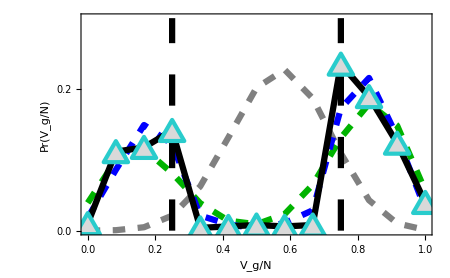

-Graphics-

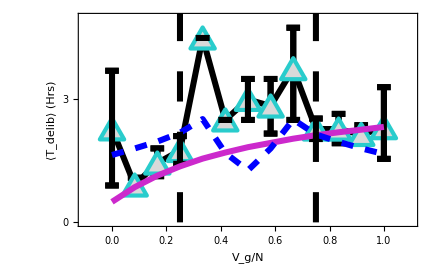

-Graphics-

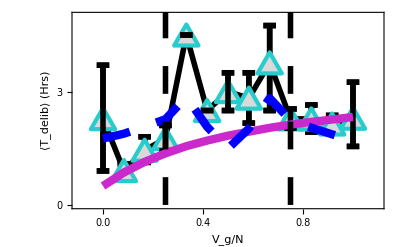

-Graphics-

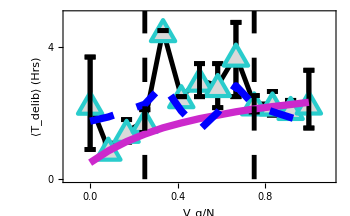

{1,30,9,13}

```mathematica
(*BEST FIT: new binomial*)
```

{1,30,9,13}

{1,30,9,13}

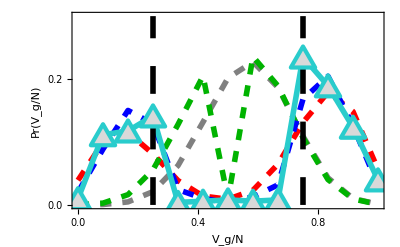

-Graphics-

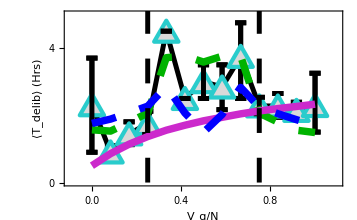

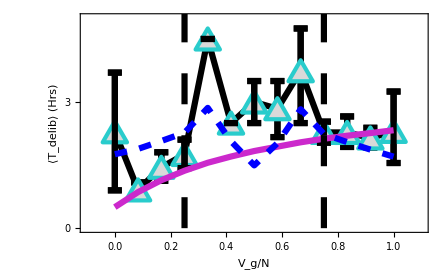

-Graphics-

-Graphics-

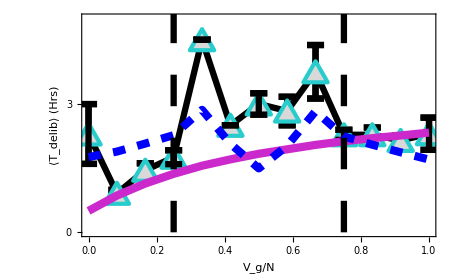

{1,30,9,13}

```mathematica
s
```

{0,0,1/7,4/7,4/7,6/7,6/7}

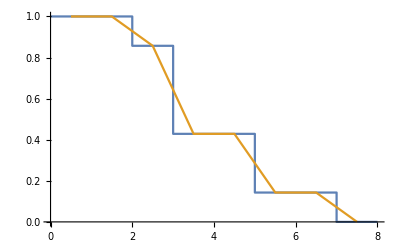

```mathematica
cdfCA12
ListLinePlot[{Flatten[Table[If[i==Length[cdfCA12],{{i,0},{(i+1),0}},{{i,1-cdfCA12[[i+1]]},{i+1,1-cdfCA12[[i+1]]}}],{i,0,Length[cdfCA12]}],1],
Flatten[Table[If[i==Length[cdfCA12],{{(i+1/2),0}},{{i+1/2,1-cdfCA12[[i+1]]}}],{i,0,Length[cdfCA12]}],1]}]
```

{{12.7751,7},{0.082985,5},{2.97871,3},{5.72105,4},{16.8563,10},{4.21518,0},{10.0132,9},{11.3758,12},{1.90127,1},{12.9406,8},{6.35455,11},{7.0232,2},{0.082985,6}}

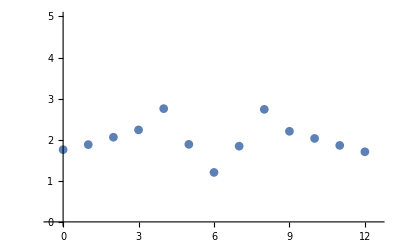

{1,30,9,13}

{1,30,9,13}

-Graphics-

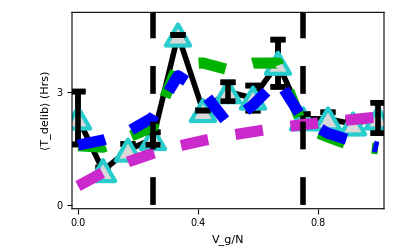

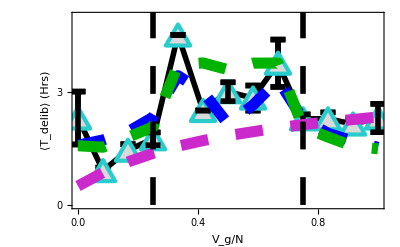

-Graphics-

```mathematica
BestFitOR6=DeleteCases[Import["~/Google Drive/DelibWork/DelibCode/Fit Code/"<>"2StrainJuryDelib-1min;Beta=1;N=12;Binomial_p=0.5318_1_0.5318;MVM_p=0.85_0.05_0.85;Alpha=0.014_0.0005_0.014;Alpha_hung=0_1_0;Tau=1.8_0.2_1.8;HungRatio=0.251_0.05_0.251;NumRuns=5000;NumTrials=32;Q0=0.3;CompleteGraph;AllInfected;CA12_1_BinomInitCondit.dat"],{}][[28;;]];

Second[list_]:=list[[2]];
Time=GatherBy[BestFitOR6,Second];
Time=SortBy[Time,Last];
Time[[;;,1]]
ListPlot[Table[{Time[[i,1,2]],(Length[Time]-1) Mean[Time[[i,;;,1]]]/60},{i,Length[Time]}],PlotMarkers->Automatic,PlotRange->{{-0.5,Length[Time]-0.5},{0,5}}]
```

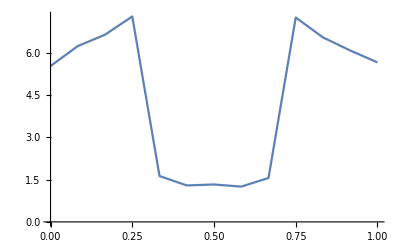

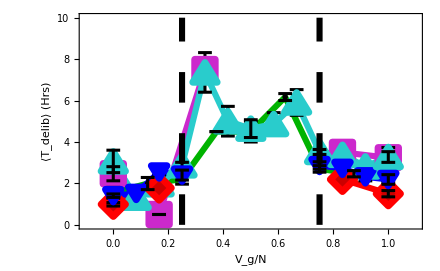
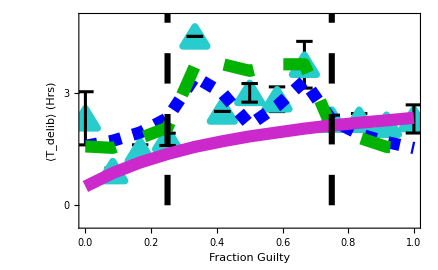
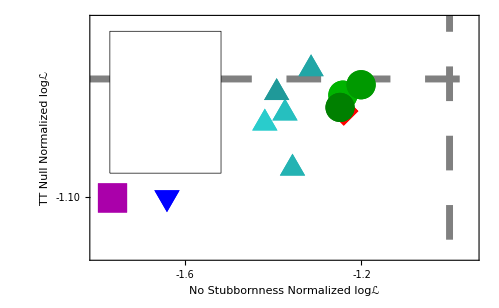
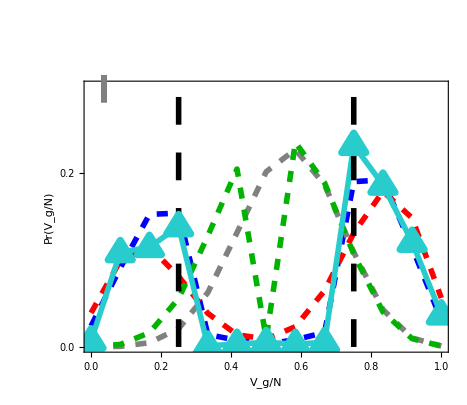
-Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics-
-Graphics--Graphics--Graphics--Graphics-




-Graphics--Graphics-

{452.,322.}

```mathematica
ListLinePlot[CA12InfluenceTvsV[[;;,1]]]
```

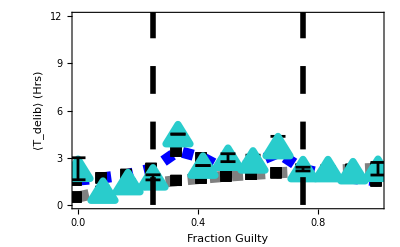

-Graphics--Graphics-

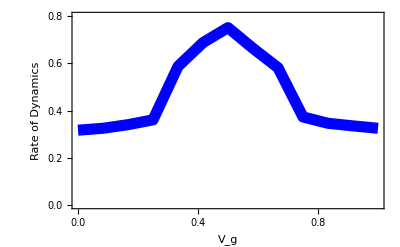

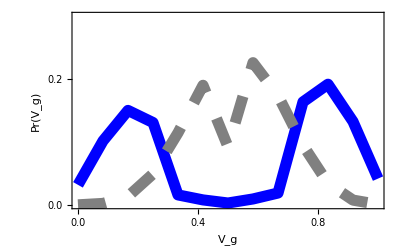

-Graphics-

-Graphics-

-Graphics-

-Graphics-

«5 more identical outputs»

-Graphics--Graphics-

-Graphics--Graphics--Graphics-

-Graphics-

-Graphics-

$Aborted

```mathematica
MeanTimeVsOutcomeCA12
```

```mathematica
(*CORRECT Model Values: CA12 ONLY*)
```

-Graphics-

-Graphics-

-Graphics-

«6 more identical outputs»

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

-Graphics-

-Graphics-

RandomChoice::lrwl: The items for choice {} should be a list or a rule weights -> choices.

ArrayReshape::list: The specified argument RandomChoice[{}, 0] should be a list or a SparseArray.

Quantile::rectn: Rectangular array of real numbers is expected at position 1 in Quantile[{Mean[RandomChoice[{}, 0]], 5000}, {0.05, 0.95}].

RandomChoice::lrwl: The items for choice {} should be a list or a rule weights -> choices.

General::stop: Further output of RandomChoice :: lrwl will be suppressed during this calculation.

Quantile::rectn: Rectangular array of real numbers is expected at position 1 in Quantile[{Mean[RandomChoice[{}, 0.]], 5000.}, {0.05, 0.95}].

ArrayReshape::list: The specified argument RandomChoice[{}, 0] should be a list or a SparseArray.

Quantile::rectn: Rectangular array of real numbers is expected at position 1 in Quantile[{Mean[RandomChoice[{}, 0]], 5000}, {0.05, 0.95}].

General::stop: Further output of Quantile :: rectn will be suppressed during this calculation.

-Graphics-

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

-Graphics-

-Graphics-

ArrayReshape::list: The specified argument RandomChoice[{}, 0] should be a list or a SparseArray.

General::stop: Further output of ArrayReshape :: list will be suppressed during this calculation.

-Graphics-

```mathematica
(*CA 6*)
```

-Graphics-

-Graphics-

-Graphics-

4.02451

0.670752

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

0.94289

```mathematica
(*OR 6*)
```

-Graphics-

-Graphics-

-Graphics-

7.12862

0.594051

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

0.896805

```mathematica
(*OR 12*)
```

-Graphics-

-Graphics-

-Graphics-

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

```mathematica
(*CA 8*)
```

-Graphics-

-Graphics-

RandomChoice::lrwl: The items for choice {} should be a list or a rule weights -> choices.

ArrayReshape::list: The specified argument RandomChoice[{}, 0] should be a list or a SparseArray.

Quantile::rectn: Rectangular array of real numbers is expected at position 1 in Quantile[{Mean[RandomChoice[{}, 0]], 5000}, {0.05, 0.95}].

RandomChoice::lrwl: The items for choice {} should be a list or a rule weights -> choices.

General::stop: Further output of RandomChoice :: lrwl will be suppressed during this calculation.

Quantile::rectn: Rectangular array of real numbers is expected at position 1 in Quantile[{Mean[RandomChoice[{}, 0.]], 5000.}, {0.05, 0.95}].

General::stop: Further output of Quantile :: rectn will be suppressed during this calculation.

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

-Graphics-

-Graphics-

ArrayReshape::list: The specified argument RandomChoice[{}, 0] should be a list or a SparseArray.

General::stop: Further output of ArrayReshape :: list will be suppressed during this calculation.

-Graphics-

```mathematica
(*CA 12*)
```

-Graphics-

-Graphics-

-Graphics--Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

«2 more identical outputs»

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

General::stop: Further output of Infinity :: indet will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

-Graphics-

-Graphics-

RandomChoice::lrwl: The items for choice {} should be a list or a rule weights -> choices.

ArrayReshape::list: The specified argument RandomChoice[{}, 0] should be a list or a SparseArray.

Quantile::rectn: Rectangular array of real numbers is expected at position 1 in Quantile[{Mean[RandomChoice[{}, 0]], 5000}, {0.05, 0.95}].

RandomChoice::lrwl: The items for choice {} should be a list or a rule weights -> choices.

General::stop: Further output of RandomChoice :: lrwl will be suppressed during this calculation.

Quantile::rectn: Rectangular array of real numbers is expected at position 1 in Quantile[{Mean[RandomChoice[{}, 0.]], 5000.}, {0.05, 0.95}].

ArrayReshape::list: The specified argument RandomChoice[{}, 0] should be a list or a SparseArray.

Quantile::rectn: Rectangular array of real numbers is expected at position 1 in Quantile[{Mean[RandomChoice[{}, 0]], 5000}, {0.05, 0.95}].

General::stop: Further output of Quantile :: rectn will be suppressed during this calculation.

-Graphics-

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power :: infy will be suppressed during this calculation.

-Graphics-

-Graphics-

ArrayReshape::list: The specified argument RandomChoice[{}, 0] should be a list or a SparseArray.

General::stop: Further output of ArrayReshape :: list will be suppressed during this calculation.

-Graphics-

{{0.5,0.5},{},{2.5,2.5},{},{},{5.5},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{},{}}

```mathematica
-Graphics--Graphics-
```

```mathematica
(*
TODO: create final vote distributions for:
 - 1 mode
- 2 mode
- N mode
THEN bootstrap time distribution per final vote
Add to previous plots:
 - Find Normalized ℒ
- Plot P(T) versus T
- Plot ⟨Subscript[T, delib]⟩ versus Subscript[V, g]
*)
SF12VoteHist=Total[TrialTimeBinnedSF12Hist[[4]],{2}];
data=SF12VoteHist;
n=12;
(*Vote Null Model*)
NumJurors = n Total[data];
NumJuries=Total[data];

MeanGuilty=N[Total[Table[(i-1) data[[i]],{i,n+1}]]/NumJuries];
PGuilty=N[MeanGuilty/n]

OneModelBinomial[k_]:=PDF[BinomialDistribution[n,PGuilty],k];
NumInnocent= Total[Table[(i-1) data[[i]],{i,Floor[n/2]}]];
MeanInnocent= NumInnocent/(Total[data[[1;;Floor[n/2]]]]);
PInnocent2=N[MeanInnocent/n];
NumGuilty = Total[Table[(i-1) data[[i]],{i,Floor[n/2]+1,n+1}]];
MeanGuilty=NumGuilty/(Total[data[[Floor[n/2]+1;;n+1]]]);
PGuilty2=N[MeanGuilty/n];
(*Weigh binomials by proportion of people in the innocent or guilty end*)
TwoModelBinomial[k_]:=PDF[BinomialDistribution[n,PGuilty2],k] Total[data[[Floor[n/2]+1;;n+1]]]/NumJuries+PDF[BinomialDistribution[n,PInnocent2],k]Total[data[[1;;Floor[n/2]]]]/NumJuries;

NModeMean= Table[(i-1),{i,n+1}];
NModelBinomial[k_]:=Total[Table[PDF[BinomialDistribution[n,NModeMean[[i]]/n],k] data[[i]],{i,n+1}]]/NumJuries;
ListLinePlot[{Table[{i,N[NModelBinomial[i]] Total[data]},{i,0,n}],
Table[{i,N[TwoModelBinomial[i]] Total[data]},{i,0,n}],
Table[{i,N[OneModelBinomial[i]] Total[data]},{i,0,n}]}]


OneModeDist=Table[N[TrialTimeBinnedSF12Hist[[T]][[i]]/Total[TrialTimeBinnedSF12Hist[[T]][[i]]]] OneModelBinomial[i],{i,n+1}];
TwoModeDist=Table[N[TrialTimeBinnedSF12Hist[[T]][[i]]/Total[TrialTimeBinnedSF12Hist[[T]][[i]]]] TwoModelBinomial[i],{i,n+1}];
NModeDist=Table[N[TrialTimeBinnedSF12Hist[[T]][[i]]/Total[TrialTimeBinnedSF12Hist[[T]][[i]]]] NModelBinomial[i],{i,n+1}];

(*ListPlot[Table[Total[OneModeDist[[i]] Table[j-0.5,{j,Length[OneModeDist[[i]]]}]/Total[OneModeDist[[i]]]],{i,n+1}]]*)

ListPlot[Flatten[{{{0,1},{1,1}},Flatten[Table[{{i,1-Total[Total[OneModeDist][[1;;i]]]},{i+1,1-Total[Total[OneModeDist][[1;;i]]]}},{i,Length[OneModeDist]}],1]},1],
Joined->True
]
ListPlot[Flatten[{{{0,1},{1,1}},Flatten[Table[{{i,1-Total[Total[TwoModeDist][[1;;i]]]},{i+1,1-Total[Total[TwoModeDist][[1;;i]]]}},{i,Length[TwoModeDist]}],1]},1],
Joined->True
]
ListPlot[Flatten[{{{0,1},{1,1}},Flatten[Table[{{i,1-Total[Total[NModeDist][[1;;i]]]},{i+1,1-Total[Total[NModeDist][[1;;i]]]}},{i,Length[NModeDist]}],1]},1],
Joined->True
]


Total[Flatten[TrialTimeBinnedSF12Hist[[T]] Log[OneModeDist+10^-MachinePrecision]]]
Total[Flatten[TrialTimeBinnedSF12Hist[[T]] Log[TwoModeDist+10^-MachinePrecision]]]
Total[Flatten[TrialTimeBinnedSF12Hist[[T]] Log[NModeDist+10^-MachinePrecision]]]
```

0.567895

```mathematica
(*CA 12_1: NoMu*)
(*
Data=DeleteCases[Import["~/Google Drive/DelibWork/DelibCode/Fit Code/2StrainJuryDelib-1min;Beta=1;N=12;Binomial_p=0.5318_1_0.5318;MVM_p=0.9802_0.02_0.9802;Alpha=0.0144_0.003_0.0144;Alpha_hung=0_1_0;Tau=0_1_0;HungRatio=0.3078_0.05_0.3078;NumRuns=5000;NumTrials=32;CA12_1BinomInitCondit;Trial1.dat"],{}][[28;;]];(*2StrainJuryDelib-1min;Beta=1;N=12;Binomial_p=0.5318_1_0.5318;MVM_p=0.7922_1_0.7922;Alpha=0.0272_1_0.0272;Alpha_hung=0_1_0;Tau=0_1_0;HungRatio=0.0702_1_0.0702;NumRuns=5000;NumTrials=32;CA12_1BinomInitCondit;Trial1.dat*)

MeanTimesVsVoteNoMu= Table[pos=Flatten[Position[Data[[;;,2]],i]];{i/12,Mean[Data[[pos,1]]] 12/60},{i,0,12}];
HistVoteNoMu= Table[pos=Flatten[Position[Data[[;;,2]],i]];{i/12,Length[pos]/Length[Data]},{i,0,12}];
PvsTNoMuPDF=N[HistogramList[Data[[;;,1]],{1}][[2]]/Length[Data]];
cdfNoMu=1-(Accumulate[PvsTNoMuPDF[[Length[PvsTNoMuPDF];;1;;-1]]])[[Length[PvsTNoMuPDF];;1;;-1]]/Total[PvsTNoMuPDF];
CCDFNoMu=Flatten[Table[{{i-1,1-cdfNoMu[[i]]},{i,1-cdfNoMu[[i]]}},{i,Length[cdfNoMu]}],1];

Print[ListLinePlot[MeanTimesVsVoteNoMu]];
*)
(*"2StrainJuryDelib-1min;RecordMu;Beta=1;N=12;Binomial_p=0.5318_1_0.5318;MVM_p=0.7922_1_0.7922;Alpha=0.0272_1_0.0272;Alpha_hung=0_1_0;Tau=7.0480_1_7.0480;HungRatio=0.0702_1_0.0702;NumRuns=5000;NumTrials=32;CA12_1BinomInitCondit;Trial1.dat"*)
InfluenceFile="2StrainJuryDelib-1min;Beta=1;N=12;Binomial_p=0.5379_1_0.5379;MVM_p=0.864_0.04_0.864;Alpha=0.0146_0.002_0.0146;Alpha_hung=0_1_0;Tau=1.592_0.7_1.592;HungRatio=0.221_0.1_0.221;NumRuns=5000;NumTrials=32;Q0=0.3;CompleteGraph;AllInfected;CA12_1_Civil.dat";
dir="~/Google Drive/DelibWork/DelibCode/Fit Code/";
Data=DeleteCases[Import[dir<>InfluenceFile],{}][[28;;]];
hw=0.05;
Data[[1;;10]]
MeanTimesVsVote = Table[pos=Flatten[Position[Data[[;;,2]],i]];{i/12,Mean[Data[[pos,1]]] 12/60},{i,0,12}]
ListLinePlot[MeanTimesVsVote]

MeanMuVsVote = Table[pos=Flatten[Position[Data[[;;,2]],i]];{i/12,Mean[Data[[pos,4]]]},{i,0,12}];

ListPlot[{MeanTimesVsVote,MeanTimesVsVoteNoMu},
Joined->True,
Frame->True,
Axes->False,
PlotRange->{{0,1},{0,5}},
PlotMarkers->{"",""},
(*PlotStyle->{{Darker[Magenta],Thickness[0.01]},{Red,Thickness[0.01],Dashing[0.05]},
{RGBColor[0,0.7,0],Thickness[0.01],Dashing[0.05]},
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]},{Blue,Thickness[0.01],Dashing[0.05]},{Black,Thick(*ness[0.01]*),Dashing[0.05]}},*)
PlotStyle->{{Blue,Thickness[0.02],Dashing[0.02]},{Gray,Thickness[0.02],Dashing[0.05]}},
FrameLabel->{Style["V_g",FontFamily->"Arial",FontSize->25,FontColor->Black],
Style["⟨T_delib⟩ (Hrs)",FontFamily->"Arial",FontSize->25,FontColor->Black]},
FrameTicksStyle->Directive[25,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{
LinTicks[0.,15,1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0.,15,1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
}
}(*,
PlotLegend->{
Style["Influence Model",FontFamily->"Arial",FontSize->20],
Style["TT Null Model",FontFamily->"Arial",FontSize->20],
Style["CA 6",FontFamily->"Arial",FontSize->20]
}*)
]

ListPlot[{MeanMuVsVote},
Joined->True,
Frame->True,
Axes->False,
PlotRange->{{0,1},{0,0.8}},
PlotMarkers->{""},
(*PlotStyle->{{Darker[Magenta],Thickness[0.01]},{Red,Thickness[0.01],Dashing[0.05]},
{RGBColor[0,0.7,0],Thickness[0.01],Dashing[0.05]},
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]},{Blue,Thickness[0.01],Dashing[0.05]},{Black,Thick(*ness[0.01]*),Dashing[0.05]}},*)
PlotStyle->{{Blue,Thickness[0.02]}},
FrameLabel->{Style["V_g",FontFamily->"Arial",FontSize->25,FontColor->Black],
Style["Rate of Dynamics",FontFamily->"Arial",FontSize->25,FontColor->Black]},
FrameTicksStyle->Directive[25,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{
LinTicks[0.,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0.,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
}
}(*,
PlotLegend->{
Style["Influence Model",FontFamily->"Arial",FontSize->20],
Style["TT Null Model",FontFamily->"Arial",FontSize->20],
Style["CA 6",FontFamily->"Arial",FontSize->20]
}*)
]
HistVote = Table[pos=Flatten[Position[Data[[;;,2]],i]];{i/12,Length[pos]/Length[Data]},{i,0,12}];

ListPlot[{HistVote,HistVoteNoMu},
Joined->True,
Frame->True,
Axes->False,
PlotRange->{{0,1},{0,0.3}},
PlotMarkers->{"",""},
(*PlotStyle->{{Darker[Magenta],Thickness[0.01]},{Red,Thickness[0.01],Dashing[0.05]},
{RGBColor[0,0.7,0],Thickness[0.01],Dashing[0.05]},
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]},{Blue,Thickness[0.01],Dashing[0.05]},{Black,Thick(*ness[0.01]*),Dashing[0.05]}},*)
PlotStyle->{{Blue,Thickness[0.02]},{Gray,Thickness[0.02],Dashing[0.05]}},
FrameLabel->{Style["V_g",FontFamily->"Arial",FontSize->25,FontColor->Black],
Style["Pr(V_g)",FontFamily->"Arial",FontSize->25,FontColor->Black]},
FrameTicksStyle->Directive[25,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{
LinTicks[0.,1,0.1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0.,1,0.1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
}
}(*,
PlotLegend->{
Style["Influence Model",FontFamily->"Arial",FontSize->20],
Style["TT Null Model",FontFamily->"Arial",FontSize->20],
Style["CA 6",FontFamily->"Arial",FontSize->20]
}*)
]

ListPlot[CCDFNoMu,
Joined->True,
Frame->True,
Axes->False,
PlotRange->{{0,10},{0,1}},
PlotMarkers->"",
(*PlotStyle->{{Darker[Magenta],Thickness[0.01]},{Red,Thickness[0.01],Dashing[0.05]},
{RGBColor[0,0.7,0],Thickness[0.01],Dashing[0.05]},
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]},{Blue,Thickness[0.01],Dashing[0.05]},{Black,Thick(*ness[0.01]*),Dashing[0.05]}},*)
PlotStyle->{{Blue,Thickness[0.02]},{Gray,Thickness[0.02],Dashing[0.05]}},
FrameLabel->{Style["T_delib",FontFamily->"Arial",FontSize->25,FontColor->Black],
Style["Pr(T ≥ T_delib)",FontFamily->"Arial",FontSize->25,FontColor->Black]},
FrameTicksStyle->Directive[25,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{
LinTicks[0.,1,0.1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0.,1,0.1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{
LinTicks[0,12,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[0,12,2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
}
}(*,
PlotLegend->{
Style["Influence Model",FontFamily->"Arial",FontSize->20],
Style["TT Null Model",FontFamily->"Arial",FontSize->20],
Style["CA 6",FontFamily->"Arial",FontSize->20]
}*)
]
```

{{23.2953,10},{6.94754,9},{2.31406,11},{3.8073,3},{26.2294,1},{0.912669,5},{1.40899,9},{6.44298,11},{2.15331,8},{1.73736,9}}

{{0,1.64342},{1/12,1.79978},{1/6,1.9588},{1/4,2.15446},{1/3,2.39803},{5/12,1.45673},{1/2,0.94735},{7/12,1.56581},{2/3,2.40264},{3/4,2.11029},{5/6,1.94667},{11/12,1.79359},{1,1.67248}}

-Graphics-

Part::partw: Part 4 of {1.48656,0} does not exist.

Part::partw: Part 4 of {26.2294,1} does not exist.

Part::partw: Part 4 of {30.2215,2} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

Part::partw: Part 4 of {1.48656,0} does not exist.

Part::partw: Part 4 of {26.2294,1.} does not exist.

Part::partw: Part 4 of {30.2215,2.} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

-Graphics-

-Graphics-

ListPlot::lpn: CCDFNoMu is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

ListPlot[CCDFNoMu,Joined→True,Frame→True,Axes→False,PlotRange→{{0,10},{0,1}},PlotMarkers→,PlotStyle→{{RGBColor[0, 0, 1],Thickness[0.02]},{GrayLevel[0.5],Thickness[0.02],Dashing[0.05]}},FrameLabel→{T_delib,Pr(T ≥ T_delib)},FrameTicksStyle→Directive[25,FontFamily→Arial,Grid→True,FontColor→GrayLevel[0]],FrameTicks→{{{{0.,0.0,{0.02,0},{}},{0.1,0.1,{0.02,0},{}},{0.2,0.2,{0.02,0},{}},{0.3,0.3,{0.02,0},{}},{0.4,0.4,{0.02,0},{}},{0.5,0.5,{0.02,0},{}},{0.6,0.6,{0.02,0},{}},{0.7,0.7,{0.02,0},{}},{0.8,0.8,{0.02,0},{}},{0.9,0.9,{0.02,0},{}},{1.,1.0,{0.02,0},{}},{0.05,,{0.01,0},{}},{0.15,,{0.01,0},{}},{0.25,,{0.01,0},{}},{0.35,,{0.01,0},{}},{0.45,,{0.01,0},{}},{0.55,,{0.01,0},{}},{0.65,,{0.01,0},{}},{0.75,,{0.01,0},{}},{0.85,,{0.01,0},{}},{0.95,,{0.01,0},{}}},{{0.,,{0.02,0},{}},{0.1,,{0.02,0},{}},{0.2,,{0.02,0},{}},{0.3,,{0.02,0},{}},{0.4,,{0.02,0},{}},{0.5,,{0.02,0},{}},{0.6,,{0.02,0},{}},{0.7,,{0.02,0},{}},{0.8,,{0.02,0},{}},{0.9,,{0.02,0},{}},{1.,,{0.02,0},{}},{0.05,,{0.01,0},{}},{0.15,,{0.01,0},{}},{0.25,,{0.01,0},{}},{0.35,,{0.01,0},{}},{0.45,,{0.01,0},{}},{0.55,,{0.01,0},{}},{0.65,,{0.01,0},{}},{0.75,,{0.01,0},{}},{0.85,,{0.01,0},{}},{0.95,,{0.01,0},{}}}},{{{0., 0,{0.02,0},{}},{2., 2,{0.02,0},{}},{4., 4,{0.02,0},{}},{6., 6,{0.02,0},{}},{8., 8,{0.02,0},{}},{10.,10,{0.02,0},{}},{12.,12,{0.02,0},{}},{1.,,{0.01,0},{}},{3.,,{0.01,0},{}},{5.,,{0.01,0},{}},{7.,,{0.01,0},{}},{9.,,{0.01,0},{}},{11.,,{0.01,0},{}}},{{0.,,{0.02,0},{}},{2.,,{0.02,0},{}},{4.,,{0.02,0},{}},{6.,,{0.02,0},{}},{8.,,{0.02,0},{}},{10.,,{0.02,0},{}},{12.,,{0.02,0},{}},{1.,,{0.01,0},{}},{3.,,{0.01,0},{}},{5.,,{0.01,0},{}},{7.,,{0.01,0},{}},{9.,,{0.01,0},{}},{11.,,{0.01,0},{}}}}}]

```mathematica
(*Updated Binomial value*)
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
Accuracy[OneModeDist[[1,1]]]
```

307.653

```mathematica
OneModeDist=Table[If[Total[OR6Hist[[i]]]>0,OR6Hist[[i]]/N[Total[OR6Hist[[i]]],30] OneModelBinomial[i],0 OR6Hist[[i]]],{i,n+1}];

Total[Flatten[Table[If[OR6Hist[[i,j]]>0,OR6Hist[[i,j]] Log[OneModeDist[[i,j]]+10^-230],0],{i,Length[OR6Hist]},{j,Length[OR6Hist[[i]]]}]]]

(*DeleteCases[Flatten[Table[If[Total[OR6Hist[[i]]]>0,
N[OR6Hist[[i]]/Total[OR6Hist[[i]]]]/.0->0,0 OR6Hist[[i]]],{i,n+1}]],0][[1]]
Total[OR6Hist[[1]]]*)
```

-50491.6

```mathematica
p2=Polygon[{{-1,0},{0,Sqrt[3]},{1,0}}];
Needs["CustomTicks`"];

Needs["CustomTicks`"];
n=6;
(*
Data=DeleteCases[Import["~/Google Drive/DelibWork/DelibCode/Fit Code/2StrainJuryDelib-1min;Beta=1;N=6;Binomial_p=0
08_1_0.6108;MVM_p=0.9431_1_0.9431;Alpha=0.0293_1_0.0293;Alpha_hung=0_1_0;Tau=0_1_0;HungRatio=0.0119_1_0.0119;NumRuns=5000;NumTrials=32;OR6BinomInitCondit;Trial1.dat"],{}][[28;;]];

(*1 timestep = n (6) * 1 minute*)
P= Table[pos=Flatten[Position[Data[[;;,2]],i]];N[HistogramList[Data[[pos,1]] n/60,{0,(Length[OR6Hist[[1]]])/60,1/60}][[2]]/Length[Data]],{i,0,n}];

*)
(*OR6HistCivilInfluence=Import["~/Google Drive/DelibWork/DelibCode/Fit Code/OR6VoteTimeBestFitModel_1minT_6_24_16.mat"];*)


Do[

Which[
Epsilon==10^-4,
Eps=1;,
Epsilon==10^-7,
Eps=2;,
Epsilon==10^-11,
Eps=3;,
Epsilon==10^-14,
Eps=4;
];
(*
(*NEW MLE ℒ values*)
MLEModels={
(*10^-4*)
{(*Full Model, NoF, NoFAlpha, NoFMu,P=0.5, No Vote Dependence (f=1, Q0=1)*)
{-665.36,-669.3,-666.16,-668.09,-764.59,-673.05},(*OR6 Civil*)
{-670.76,-674.2,-670.04,-675.19,-761.14,-679.56},(*OR6 Criminal*)
{-4483.6,-4520.0,-4503.9,-4506.8,-5236.7,-4530.2},(*OR12 Civil*)
{-2853.5,-2871.0,-2888.4,-2866.2,-3562.4,-2883.3},(*OR12 Criminal*)
{-168.7505,-169.9754,-169.7391,-169.1376,-251.4616,-170.2396},(*CA 6*)
{-585.03,-600.21,-588.3,-608.6,-652.17,-600.13},(*CA 8-1*)
{-454.17,-459.95,-454.58,-459.4,-502.17,-461.2},(*CA 8-2*)
{-129.9462,-133.0745,-129.7998,-132.9853,-138.1832,-133.3945},(*CA 8-3*)
{-1885.4,-1916.9,-1896.4,-1913.1,-2237.3,-1928.3},(*CA 12-1*)
{-2741.8,-2779.4,-2756.0,-2768.6,-3150.6,-2803.8},(*CA 12-2*)
{-1773.4,-1802.8,-1776.8,-1797.6,-1992.8,-1807.7},(*CA 12-3*)
{-507.0,-522.3,-510.44,-519.3,-545.6,-522.9}, (*CA 12-4*)
{-204.5675,-210.4537,-204.7874,-209.2833,-230.4946,-209.8982}  (*CA 12-5*)
},
(*10^-7*)
{
{-665.36,-669.3,-666.16,-668.09,-764.59,-673.05},(*OR6 Civil*)
{-670.76,-674.2,-670.04,-675.19,-761.14,-679.56},(*OR6 Criminal*)
{-4497.4,-4533.8,-4511.7,-4520.6,-5741,-4544},(*OR12 Civil*)
{-2874.2,-2891.8,-2895.3,-2886.9,-3735,-2910.9},(*OR12 Criminal*)
{-168.7505,-169.9754,-169.7391,-169.1376,-251.4616,-170.2396},(*CA 6*)
{-585.03,-600.21,-588.3,-608.6,-652.17,-600.13},(*CA 8-1*)
{-454.17,-459.95,-454.58,-459.4,-502.17,-461.2},(*CA 8-2*)
{-129.9462,-133.0745,-129.7998,-132.9853,-138.1832,-133.3945},(*CA 8-3*)
{-1885.4,-1916.9,-1896.4,-1913.1,-2244.2,-1928.3},(*CA 12-1*)
{-2741.8,-2779.4,-2756.0,-2768.6,-3150.6,-2803.8},(*CA 12-2*)
{-1773.4,-1802.8,-1776.8,-1797.6,-1992.8,-1807.7},(*CA 12-3*)
{-507.0,-522.3,-510.44,-519.3,-545.6,-522.9}, (*CA 12-4*)
{-204.5675,-210.4537,-204.7874,-209.2833,-230.4946,-209.8982}  (*CA 12-5*)
},
(*10^-11*)
{
{-665.36,-669.3,-666.16,-668.09,-764.59,-673.05},(*OR6 Civil*)
{-670.76,-674.2,-670.04,-675.19,-761.14,-679.56},(*OR6 Criminal*)
{-4515.9,-4552.2,-4536.1,-4539.0,-6413.4,-4562.5},(*OR12 Civil*)
{-2901.8,-2919.4,-2904.5,-2914.6,-3965.3,-2947.8},(*OR12 Criminal*)
{-168.7505,-169.9754,-169.7391,-169.1376,-251.4616,-170.2396},(*CA 6*)
{-585.03,-600.21,-588.3,-608.6,-652.17,-600.13},(*CA 8-1*)
{-454.17,-459.95,-454.58,-459.4,-502.17,-461.2},(*CA 8-2*)
{-129.9462,-133.0745,-129.7998,-132.9853,-138.1832,-133.3945},(*CA 8-3*)
{-1885.4,-1916.9,-1896.4,-1913.1,-2253.4,-1928.3},(*CA 12-1*)
{-2741.8,-2779.4,-2756.0,-2768.6,-3150.6,-2803.8},(*CA 12-2*)
{-1773.4,-1802.8,-1776.8,-1797.6,-1992.8,-1807.7},(*CA 12-3*)
{-507.0,-522.3,-510.44,-519.3,-545.6,-522.9}, (*CA 12-4*)
{-204.5675,-210.4537,-204.7874,-209.2833,-230.4946,-209.8982}    (*CA 12-5*)
},
(*10^-14*)
{
{-665.36,-669.3,-666.16,-668.09,-764.59,-673.05},(*OR6 Civil*)
{-670.76,-674.2,-670.04,-675.19,-761.14,-679.56},(*OR6 Criminal*)
{-4529.7,-4566.1,-4550.0,-4552.8,-6917.6,-4576.3},(*OR12 Civil*)
{-2922.5,-2940.1,-2911.4,-2935.3,-4138,-2975.4},(*OR12 Criminal*)
{-168.7505,-169.9754,-169.7391,-169.1376,-251.4616,-170.2396},(*CA 6*)
{-585.03,-600.21,-588.3,-608.6,-652.17,-600.13},(*CA 8-1*)
{-454.17,-459.95,-454.58,-459.4,-502.17,-461.2},(*CA 8-2*)
{-129.9462,-133.0745,-129.7998,-132.9853,-138.1832,-133.3945},(*CA 8-3*)
{-1885.4,-1916.9,-1896.4,-1913.1,-2260.3,-1928.3},(*CA 12-1*)
{-2741.8,-2779.4,-2756.0,-2768.6,-3150.6,-2803.8},(*CA 12-2*)
{-1773.4,-1802.8,-1776.8,-1797.6,-1992.8,-1807.7},(*CA 12-3*)
{-507.0,-522.3,-510.44,-519.3,-545.6,-522.9}, (*CA 12-4*)
{-204.5675,-210.4537,-204.7874,-209.2833,-230.4946,-209.8982}  (*CA 12-5*)
}
};



(*OR6CivilTT=Import["~/Google Drive/DelibWork/DelibCode/Fit Code/Fits/TTNullFits/OR6VoteTimeTTBestFitModel_1minT.mat"];*)
(*OR6CivilTT=Import["~/Google Drive/DelibWork/DelibCode/Fit Code/Fits/TTNullFits/"];*)
data=Total[OR6HistCivil,{2}];

n=6;
(*Vote Null Model*)
NumJurors = n Total[data];
NumJuries=Total[data];

MeanGuilty=N[Total[Table[(i-1) data[[i]],{i,n+1}]]/NumJuries];
PGuilty=N[MeanGuilty/n];
OneModelBinomial[k_]:=PDF[BinomialDistribution[n,PGuilty],k];
NumInnocent= Total[Table[(i-1) data[[i]],{i,Floor[n/2]}]];
MeanInnocent= NumInnocent/(Total[data[[1;;Floor[n/2]]]]);
PInnocent2=N[MeanInnocent/n];
NumGuilty = Total[Table[(i-1) data[[i]],{i,Floor[n/2]+1,n+1}]];
MeanGuilty=NumGuilty/(Total[data[[Floor[n/2]+1;;n+1]]]);
PGuilty2=N[MeanGuilty/n];

(*Weigh binomials by proportion of people in the innocent or guilty end*)
TwoModelBinomial[k_]:=PDF[BinomialDistribution[n,PGuilty2],k] Total[data[[Floor[n/2]+1;;n+1]]]/NumJuries+PDF[BinomialDistribution[n,PInnocent2],k]Total[data[[1;;Floor[n/2]]]]/NumJuries;
NModeMean= Table[(i-1),{i,n+1}];
NModelBinomial[k_]:=Total[Table[PDF[BinomialDistribution[n,NModeMean[[i]]/n],k] data[[i]],{i,n+1}]]/NumJuries;
OneModeDist=Table[If[Total[OR6HistCivil[[i]]]>0,N[OR6HistCivil[[i]]/Total[OR6HistCivil[[i]]]] OneModelBinomial[i],0 OR6HistCivil[[i]]],{i,n+1}];
TwoModeDist=Table[If[Total[OR6HistCivil[[i]]]>0,N[OR6HistCivil[[i]]/Total[OR6HistCivil[[i]]]] TwoModelBinomial[i],0 OR6HistCivil[[i]]],{i,n+1}];
NModeDist=Table[If[Total[OR6HistCivil[[i]]]>0,N[OR6HistCivil[[i]]/Total[OR6HistCivil[[i]]]] NModelBinomial[i],0 OR6HistCivil[[i]]],{i,n+1}];


(*NewOR6Influence =OR6HistInfluence[[1,;;,;;]];
OR6Influence=NewOR6Influence;*)
(*NewOR6TT =OR6TT[[1,;;,;;]];
OR6TT=NewOR6TT;
OR6MLE={{-1.6605*10^3,-1.6674*10^3,-1.6766*10^3,-1.6835*10^3}[[Eps]](*Total[Flatten[OR6Hist Log[P+Epsilon]]]*),
Total[Flatten[OR6Hist Log[OR6Influence[[;;,2;;-1]]-OR6Influence[[;;,1;;-2]]+Epsilon]]],
Total[Flatten[OR6Hist Log[OR6TT[[;;,2;;-1]]-OR6TT[[;;,1;;-2]]+Epsilon]]],
Total[Flatten[OR6Hist Log[OneModeDist+Epsilon]]],
Total[Flatten[OR6Hist Log[TwoModeDist+Epsilon]]],
Total[Flatten[OR6Hist Log[NModeDist+Epsilon]]]
};
Print[OR6MLE];
*)
(*NewOR6CivilTT =OR6CivilTT[[1,;;,;;]];
OR6CivilTT=NewOR6CivilTT;*)
MLENoMu=-833.36;
(*
TTNull = all_data_parse_vote_NewInfluence_TTNull()
*)
TTNull=-664.82;
OR6CivilMLE={MLENoMu,
MLEModels[[Eps,1,1]](*Total[Flatten[OR6HistCivil Log[OR6CivilInfluence[[;;,2;;-1]]-OR6CivilInfluence[[;;,1;;-2]]+Epsilon]]]*),
TTNull(*Total[Flatten[OR6HistCivil Log[OR6CivilTT[[;;,2;;-1]]-OR6CivilTT[[;;,1;;-2]]+Epsilon]]]*),
Total[Flatten[OR6HistCivil Log[OneModeDist+Epsilon]]],
Total[Flatten[OR6HistCivil Log[TwoModeDist+Epsilon]]],
Total[Flatten[OR6HistCivil Log[NModeDist+Epsilon]]]
};

(*OR6CriminalTT=Import["~/Google Drive/DelibWork/DelibCode/Fit Code/Fits/TTNullFits/OR6VoteTimeTTBestFitModel_1minT.mat"];*)
(*OR6CriminalTT=Import["~/Google Drive/DelibWork/DelibCode/Fit Code/Fits/TTNullFits/"];
data=Total[OR6HistCriminal,{2}];
*)
n=6;
(*Vote Null Model*)
NumJurors = n Total[data];
NumJuries=Total[data];

MeanGuilty=N[Total[Table[(i-1) data[[i]],{i,n+1}]]/NumJuries];
PGuilty=N[MeanGuilty/n];
OneModelBinomial[k_]:=PDF[BinomialDistribution[n,PGuilty],k];
NumInnocent= Total[Table[(i-1) data[[i]],{i,Floor[n/2]}]];
MeanInnocent= NumInnocent/(Total[data[[1;;Floor[n/2]]]]);
PInnocent2=N[MeanInnocent/n];
NumGuilty = Total[Table[(i-1) data[[i]],{i,Floor[n/2]+1,n+1}]];
MeanGuilty=NumGuilty/(Total[data[[Floor[n/2]+1;;n+1]]]);
PGuilty2=N[MeanGuilty/n];

(*Weigh binomials by proportion of people in the innocent or guilty end*)
TwoModelBinomial[k_]:=PDF[BinomialDistribution[n,PGuilty2],k] Total[data[[Floor[n/2]+1;;n+1]]]/NumJuries+PDF[BinomialDistribution[n,PInnocent2],k]Total[data[[1;;Floor[n/2]]]]/NumJuries;
NModeMean= Table[(i-1),{i,n+1}];
NModelBinomial[k_]:=Total[Table[PDF[BinomialDistribution[n,NModeMean[[i]]/n],k] data[[i]],{i,n+1}]]/NumJuries;
OneModeDist=Table[If[Total[OR6HistCriminal[[i]]]>0,N[OR6HistCriminal[[i]]/Total[OR6HistCriminal[[i]]]] OneModelBinomial[i],0 OR6HistCriminal[[i]]],{i,n+1}];
TwoModeDist=Table[If[Total[OR6HistCriminal[[i]]]>0,N[OR6HistCriminal[[i]]/Total[OR6HistCriminal[[i]]]] TwoModelBinomial[i],0 OR6HistCriminal[[i]]],{i,n+1}];
NModeDist=Table[If[Total[OR6HistCriminal[[i]]]>0,N[OR6HistCriminal[[i]]/Total[OR6HistCriminal[[i]]]] NModelBinomial[i],0 OR6HistCriminal[[i]]],{i,n+1}];
(*NewOR6CriminalTT =OR6CriminalTT[[1,;;,;;]];
OR6CriminalTT=NewOR6CriminalTT;*)
MLENoMu=-809.14;
(*
TTNull = all_data_parse_vote_NewInfluence_TTNull()
*)
TTNull=-694.42;
OR6CriminalMLE={MLENoMu,
MLEModels[[Eps,2,1]](*Total[Flatten[OR6HistCriminal Log[OR6CriminalInfluence[[;;,2;;-1]]-OR6CriminalInfluence[[;;,1;;-2]]+Epsilon]]]*),
TTNull(*Total[Flatten[OR6HistCriminal Log[OR6CriminalTT[[;;,2;;-1]]-OR6CriminalTT[[;;,1;;-2]]+Epsilon]]]*),
Total[Flatten[OR6HistCriminal Log[OneModeDist+Epsilon]]],
Total[Flatten[OR6HistCriminal Log[TwoModeDist+Epsilon]]],
Total[Flatten[OR6HistCriminal Log[NModeDist+Epsilon]]]
};

(*n=12;
Data=DeleteCases[Import["~/Google Drive/DelibWork/DelibCode/Fit Code/2StrainJuryDelib-1min;Beta=1;N=12;Binomial_p=0.5452_1_0.5452;MVM_p=0.8898_1_0.8898;Alpha=0.0223_1_0.0223;Alpha_hung=0_1_0;Tau=0_1_0;HungRatio=0.0226_1_0.0226;NumRuns=5000;NumTrials=32;OR12BinomInitCondit;Trial1.dat"],{}][[28;;]];
(*1 timestep = n (6) * 1 minute*)
P= Table[pos=Flatten[Position[Data[[;;,2]],i]];N[HistogramList[Data[[pos,1]] n/60,{0,(Length[OR12Hist[[1]]])/60,1/60}][[2]]/Length[Data]],{i,0,n}];


OR12HistInfluence=Import["~/Google Drive/DelibWork/DelibCode/Fit Code/OR12VoteTimeBestFitModel_1minT_6_24_16.mat"];

OR12TT=Import["~/Google Drive/DelibWork/DelibCode/Fit Code/Fits/TTNullFits/OR12VoteTimeTTBestFitModel_1minT.mat"];

data=Total[OR12Hist,{2}];
n=12;
(*Vote Null Model*)
NumJurors = n Total[data];
NumJuries=Total[data];

MeanGuilty=N[Total[Table[(i-1) data[[i]],{i,n+1}]]/NumJuries];
PGuilty=N[MeanGuilty/n];
OneModelBinomial[k_]:=PDF[BinomialDistribution[n,PGuilty],k];
NumInnocent= Total[Table[(i-1) data[[i]],{i,Floor[n/2]}]];
MeanInnocent= NumInnocent/(Total[data[[1;;Floor[n/2]]]]);
PInnocent2=N[MeanInnocent/n];
NumGuilty = Total[Table[(i-1) data[[i]],{i,Floor[n/2]+1,n+1}]];
MeanGuilty=NumGuilty/(Total[data[[Floor[n/2]+1;;n+1]]]);
PGuilty2=N[MeanGuilty/n];


(*Weigh binomials by proportion of people in the innocent or guilty end*)
TwoModelBinomial[k_]:=PDF[BinomialDistribution[n,PGuilty2],k] Total[data[[Floor[n/2]+1;;n+1]]]/NumJuries+PDF[BinomialDistribution[n,PInnocent2],k]Total[data[[1;;Floor[n/2]]]]/NumJuries;
NModeMean= Table[(i-1),{i,n+1}];
NModelBinomial[k_]:=Total[Table[PDF[BinomialDistribution[n,NModeMean[[i]]/n],k] data[[i]],{i,n+1}]]/NumJuries;
OneModeDist=Table[If[Total[OR12Hist[[i]]]>0,N[OR12Hist[[i]]/Total[OR12Hist[[i]]]] OneModelBinomial[i],0 OR12Hist[[i]]],{i,n+1}];
TwoModeDist=Table[If[Total[OR12Hist[[i]]]>0,N[OR12Hist[[i]]/Total[OR12Hist[[i]]]] TwoModelBinomial[i],0 OR12Hist[[i]]],{i,n+1}];
NModeDist=Table[If[Total[OR12Hist[[i]]]>0,N[OR12Hist[[i]]/Total[OR12Hist[[i]]]] NModelBinomial[i],0 OR12Hist[[i]]],{i,n+1}];


NewOR12Influence =OR12HistInfluence[[1,;;,;;]];
OR12Influence=NewOR12Influence;
NewOR12TT =OR12TT[[1,;;,;;]];
OR12TT=NewOR12TT;
OR12MLE={{-9.2506*10^3,-1.0777*10^4,-1.2813*10^4,-1.4339*10^4}[[Eps]]
(*Total[Flatten[OR12Hist Log[P+Epsilon]]]*),
Total[Flatten[OR12Hist Log[OR12Influence[[;;,2;;-1]]-OR12Influence[[;;,1;;-2]]+Epsilon]]],
Total[Flatten[OR12Hist Log[OR12TT[[;;,2;;-1]]-OR12TT[[;;,1;;-2]]+Epsilon]]],
Total[Flatten[OR12Hist Log[OneModeDist+Epsilon]]],
Total[Flatten[OR12Hist Log[TwoModeDist+Epsilon]]],
Total[Flatten[OR12Hist Log[NModeDist+Epsilon]]]};
Print[OR12MLE];*)
n=12;
(*Data=DeleteCases[Import["~/Google Drive/DelibWork/DelibCode/Fit Code/2StrainJuryDelib-1min;Beta=1;N=12;Binomial_p=0.5452_1_0.5452;MVM_p=0.8898_1_0.8898;Alpha=0.0223_1_0.0223;Alpha_hung=0_1_0;Tau=0_1_0;HungRatio=0.0226_1_0.0226;NumRuns=5000;NumTrials=32;OR12BinomInitCondit;Trial1.dat"],{}][[28;;]];*)
(*1 timestep = n (6) * 1 minute*)
(*
P= Table[pos=Flatten[Position[Data[[;;,2]],i]];N[HistogramList[Data[[pos,1]] n/60,{0,(Length[OR12HistCivil[[1]]])/60,1/60}][[2]]/Length[Data]],{i,0,n}];
*)

(*OR12HistCivilInfluence=Import["~/Google Drive/DelibWork/DelibCode/Fit Code/OR12VoteTimeBestFitModel_1minT_6_24_16.mat"];*)
n=12;
(*OR12CivilTT=Import["~/Google Drive/DelibWork/DelibCode/Fit Code/Fits/TTNullFits/"];*)

data=Total[OR12HistCivil,{2}];
n=12;
(*Vote Null Model*)
NumJurors = n Total[data];
NumJuries=Total[data];

MeanGuilty=N[Total[Table[(i-1) data[[i]],{i,n+1}]]/NumJuries];
PGuilty=N[MeanGuilty/n];
OneModelBinomial[k_]:=PDF[BinomialDistribution[n,PGuilty],k];
NumInnocent= Total[Table[(i-1) data[[i]],{i,Floor[n/2]}]];
MeanInnocent= NumInnocent/(Total[data[[1;;Floor[n/2]]]]);
PInnocent2=N[MeanInnocent/n];
NumGuilty = Total[Table[(i-1) data[[i]],{i,Floor[n/2]+1,n+1}]];
MeanGuilty=NumGuilty/(Total[data[[Floor[n/2]+1;;n+1]]]);
PGuilty2=N[MeanGuilty/n];


(*Weigh binomials by proportion of people in the innocent or guilty end*)
TwoModelBinomial[k_]:=PDF[BinomialDistribution[n,PGuilty2],k] Total[data[[Floor[n/2]+1;;n+1]]]/NumJuries+PDF[BinomialDistribution[n,PInnocent2],k]Total[data[[1;;Floor[n/2]]]]/NumJuries;
NModeMean= Table[(i-1),{i,n+1}];
NModelBinomial[k_]:=Total[Table[PDF[BinomialDistribution[n,NModeMean[[i]]/n],k] data[[i]],{i,n+1}]]/NumJuries;
OneModeDist=Table[If[Total[OR12HistCivil[[i]]]>0,N[OR12HistCivil[[i]]/Total[OR12HistCivil[[i]]]] OneModelBinomial[i],0 OR12HistCivil[[i]]],{i,n+1}];
TwoModeDist=Table[If[Total[OR12HistCivil[[i]]]>0,N[OR12HistCivil[[i]]/Total[OR12HistCivil[[i]]]] TwoModelBinomial[i],0 OR12HistCivil[[i]]],{i,n+1}];
NModeDist=Table[If[Total[OR12HistCivil[[i]]]>0,N[OR12HistCivil[[i]]/Total[OR12HistCivil[[i]]]] NModelBinomial[i],0 OR12HistCivil[[i]]],{i,n+1}];

(*
NewOR12CivilInfluence =OR12HistCivilInfluence[[1,;;,;;]];
OR12CivilInfluence=NewOR12CivilInfluence;*)
(*NewOR12CivilTT =OR12CivilTT[[1,;;,;;]];
OR12CivilTT=NewOR12CivilTT;*)
MLENoMu={-5459.2,-6384.9,-7619.0,-8544.7};
(*
TTNull = all_data_parse_vote_NewInfluence_TTNull()
*)
TTNull=-4.5462 10^03;
OR12CivilMLE={MLENoMu[[Eps]],
MLEModels[[Eps,3,1]](*Total[Flatten[OR12HistCivil Log[OR12CivilInfluence[[;;,2;;-1]]-OR12CivilInfluence[[;;,1;;-2]]+Epsilon]]]*),
TTNull(*Total[Flatten[OR12HistCivil Log[OR12CivilTT[[;;,2;;-1]]-OR12CivilTT[[;;,1;;-2]]+Epsilon]]]*),
Total[Flatten[OR12HistCivil Log[OneModeDist+Epsilon]]],
Total[Flatten[OR12HistCivil Log[TwoModeDist+Epsilon]]],
Total[Flatten[OR12HistCivil Log[NModeDist+Epsilon]]]};


n=12;
(*OR12CriminalTT=Import["~/Google Drive/DelibWork/DelibCode/Fit Code/Fits/TTNullFits/"];*)

data=Total[OR12HistCriminal,{2}];
n=12;
(*Vote Null Model*)
NumJurors = n Total[data];
NumJuries=Total[data];

MeanGuilty=N[Total[Table[(i-1) data[[i]],{i,n+1}]]/NumJuries];
PGuilty=N[MeanGuilty/n];
OneModelBinomial[k_]:=PDF[BinomialDistribution[n,PGuilty],k];
NumInnocent= Total[Table[(i-1) data[[i]],{i,Floor[n/2]}]];
MeanInnocent= NumInnocent/(Total[data[[1;;Floor[n/2]]]]);
PInnocent2=N[MeanInnocent/n];
NumGuilty = Total[Table[(i-1) data[[i]],{i,Floor[n/2]+1,n+1}]];
MeanGuilty=NumGuilty/(Total[data[[Floor[n/2]+1;;n+1]]]);
PGuilty2=N[MeanGuilty/n];


(*Weigh binomials by proportion of people in the innocent or guilty end*)
TwoModelBinomial[k_]:=PDF[BinomialDistribution[n,PGuilty2],k] Total[data[[Floor[n/2]+1;;n+1]]]/NumJuries+PDF[BinomialDistribution[n,PInnocent2],k]Total[data[[1;;Floor[n/2]]]]/NumJuries;
NModeMean= Table[(i-1),{i,n+1}];
NModelBinomial[k_]:=Total[Table[PDF[BinomialDistribution[n,NModeMean[[i]]/n],k] data[[i]],{i,n+1}]]/NumJuries;
OneModeDist=Table[If[Total[OR12HistCriminal[[i]]]>0,N[OR12HistCriminal[[i]]/Total[OR12HistCriminal[[i]]]] OneModelBinomial[i],0 OR12HistCriminal[[i]]],{i,n+1}];
TwoModeDist=Table[If[Total[OR12HistCriminal[[i]]]>0,N[OR12HistCriminal[[i]]/Total[OR12HistCriminal[[i]]]] TwoModelBinomial[i],0 OR12HistCriminal[[i]]],{i,n+1}];
NModeDist=Table[If[Total[OR12HistCriminal[[i]]]>0,N[OR12HistCriminal[[i]]/Total[OR12HistCriminal[[i]]]] NModelBinomial[i],0 OR12HistCriminal[[i]]],{i,n+1}];

(*
NewOR12CriminalInfluence =OR12HistCriminalInfluence[[1,;;,;;]];
OR12CriminalInfluence=NewOR12CriminalInfluence;*)
(*NewOR12CriminalTT =OR12CriminalTT[[1,;;,;;]];
OR12CriminalTT=NewOR12CriminalTT;*)
MLENoMu={-3723.7,-4152,-4723,-5151.3};
(*
TTNull = all_data_parse_vote_NewInfluence_TTNull()
*)
TTNull=-3.0462 10^03;
OR12CriminalMLE={MLENoMu[[Eps]],
MLEModels[[Eps,4,1]](*Total[Flatten[OR12HistCriminal Log[OR12CriminalInfluence[[;;,2;;-1]]-OR12CriminalInfluence[[;;,1;;-2]]+Epsilon]]]*),
TTNull(*Total[Flatten[OR12HistCriminal Log[OR12CriminalTT[[;;,2;;-1]]-OR12CriminalTT[[;;,1;;-2]]+Epsilon]]]*),
Total[Flatten[OR12HistCriminal Log[OneModeDist+Epsilon]]],
Total[Flatten[OR12HistCriminal Log[TwoModeDist+Epsilon]]],
Total[Flatten[OR12HistCriminal Log[NModeDist+Epsilon]]]};


n=6;
Data=DeleteCases[Import["~/Google Drive/DelibWork/DelibCode/Fit Code/2StrainJuryDelib-1min;Beta=1;N=6;Binomial_p=0.4545_1_0.4545;MVM_p=0.9776_1_0.9776;Alpha=0.0083_1_0.0083;Alpha_hung=0_1_0;Tau=0_1_0;HungRatio=0.2826_1_0.2826;NumRuns=5000;NumTrials=32;CA6BinomInitCondit;Trial1.dat"],{}][[28;;]];
(*1 timestep = n (6) * 1 minute*)
CA6Hist=Total[TrialTimeBinnedSF6Hist];
P= Table[pos=Flatten[Position[Data[[;;,2]],i]];N[HistogramList[Data[[pos,1]] n/60,{0,(Length[CA6Hist[[1]]]),1}][[2]]/Length[Data]],{i,0,n}];


CA6HistInfluence=Import["~/Google Drive/DelibWork/DelibCode/Fit Code/CA6VoteTimeBestFitModel_1minT_6_24_16.mat"];

CA6TT=Import["~/Google Drive/DelibWork/DelibCode/Fit Code/Fits/TTNullFits/CA6VoteTimeTTBestFitModel_1minT.mat"];

data=Total[CA6Hist,{2}];
n=6;
(*Vote Null Model*)
NumJurors = n Total[data];
NumJuries=Total[data];

MeanGuilty=N[Total[Table[(i-1) data[[i]],{i,n+1}]]/NumJuries];
PGuilty=N[MeanGuilty/n];
OneModelBinomial[k_]:=PDF[BinomialDistribution[n,PGuilty],k];
NumInnocent= Total[Table[(i-1) data[[i]],{i,Floor[n/2]}]];
MeanInnocent= NumInnocent/(Total[data[[1;;Floor[n/2]]]]);
PInnocent2=N[MeanInnocent/n];
NumGuilty = Total[Table[(i-1) data[[i]],{i,Floor[n/2]+1,n+1}]];
MeanGuilty=NumGuilty/(Total[data[[Floor[n/2]+1;;n+1]]]);
PGuilty2=N[MeanGuilty/n];
(*Weigh binomials by proportion of people in the innocent or guilty end*)
TwoModelBinomial[k_]:=PDF[BinomialDistribution[n,PGuilty2],k] Total[data[[Floor[n/2]+1;;n+1]]]/NumJuries+PDF[BinomialDistribution[n,PInnocent2],k]Total[data[[1;;Floor[n/2]]]]/NumJuries;
NModeMean= Table[(i-1),{i,n+1}];
NModelBinomial[k_]:=Total[Table[PDF[BinomialDistribution[n,NModeMean[[i]]/n],k] data[[i]],{i,n+1}]]/NumJuries;
OneModeDist=Table[If[Total[CA6Hist[[i]]]>0,N[CA6Hist[[i]]/Total[CA6Hist[[i]]]] OneModelBinomial[i],0 CA6Hist[[i]]],{i,n+1}];
TwoModeDist=Table[If[Total[CA6Hist[[i]]]>0,N[CA6Hist[[i]]/Total[CA6Hist[[i]]]] TwoModelBinomial[i],0 CA6Hist[[i]]],{i,n+1}];
NModeDist=Table[If[Total[CA6Hist[[i]]]>0,N[CA6Hist[[i]]/Total[CA6Hist[[i]]]] NModelBinomial[i],0 CA6Hist[[i]]],{i,n+1}];


NewCA6Influence =CA6HistInfluence[[1,;;,;;]];
CA6Influence=NewCA6Influence;
NewCA6TT =CA6TT[[1,;;,;;]];
CA6TT=NewCA6TT;
CA6MLE={{-280.2904,-280.2904,-280.2904,-280.2904}[[Eps]](*Total[Flatten[CA6Hist Log[P+Epsilon]]]*),
Total[Flatten[CA6Hist Log[CA6Influence[[;;,2;;-1]]-CA6Influence[[;;,1;;-2]]+Epsilon]]],
Total[Flatten[CA6Hist Log[CA6TT[[;;,2;;-1]]-CA6TT[[;;,1;;-2]]+Epsilon]]],
Total[Flatten[CA6Hist Log[OneModeDist+Epsilon]]],
Total[Flatten[CA6Hist Log[TwoModeDist+Epsilon]]],
Total[Flatten[CA6Hist Log[NModeDist+Epsilon]]]};
Print[CA6MLE];

(*
n=8;
index=4;
Data=DeleteCases[Import["~/Google Drive/DelibWork/DelibCode/Fit Code/2StrainJuryDelib-1min;Beta=1;N=8;Binomial_p=0.5583_1_0.5583;MVM_p=0.8253_1_0.8253;Alpha=0.0278_1_0.0278;Alpha_hung=0_1_0;Tau=0_1_0;HungRatio=0_1_0;NumRuns=5000;NumTrials=32;CA8_1BinomInitCondit;Trial1.dat"],{}][[28;;]];

(*1 timestep = n (6) * 1 minute*)
CA8Hist=TrialTimeBinnedSF8Hist[[index]];(*CHANGE APPROPRIATELY*)
P= Table[pos=Flatten[Position[Data[[;;,2]],i]];N[HistogramList[Data[[pos,1]] n/60,{0,(Length[CA8Hist[[1]]]),1}][[2]]/Length[Data]],{i,0,n}];


CA8HistInfluence=Transpose[Import["~/Google Drive/DelibWork/DelibCode/Fit Code/CA8VoteTimeDistBestFitModel_1minT_6_24_16.mat"][[1,;;,index,;;]]];

CA8TT=Transpose[Import["~/Google Drive/DelibWork/DelibCode/Fit Code/Fits/TTNullFits/CA8VoteTimeTTBestFitModel_1minT.mat"][[1,;;,index,;;]]];
Dimensions[CA8HistInfluence]
Dimensions[CA8TT]
Dimensions[P]
Dimensions[CA8Hist]
NewCA8Influence =CA8HistInfluence;
CA8Influence=NewCA8Influence;
NewCA8TT =CA8TT;
CA8TT=NewCA8TT;
Total[Flatten[CA8Hist Log[P+Epsilon]]]
Total[Flatten[CA8Hist Log[CA8Influence[[;;,2;;-1]]-CA8Influence[[;;,1;;-2]]+Epsilon]]]
Total[Flatten[CA8Hist Log[CA8TT[[;;,2;;-1]]-CA8TT[[;;,1;;-2]]+Epsilon]]]





n=8;
index=5;
Data=DeleteCases[Import["~/Google Drive/DelibWork/DelibCode/Fit Code/2StrainJuryDelib-1min;Beta=1;N=8;Binomial_p=0.5960_1_0.5960;MVM_p=0.8229_1_0.8229;Alpha=0.0159_1_0.0159;Alpha_hung=0_1_0;Tau=0_1_0;HungRatio=0_1_0;NumRuns=5000;NumTrials=32;CA8_2BinomInitCondit;Trial1.dat"],{}][[28;;]];

(*1 timestep = n (6) * 1 minute*)
CA8Hist=TrialTimeBinnedSF8Hist[[index]];(*CHANGE APPROPRIATELY*)
P= Table[pos=Flatten[Position[Data[[;;,2]],i]];N[HistogramList[Data[[pos,1]] n/60,{0,(Length[CA8Hist[[1]]]),1}][[2]]/Length[Data]],{i,0,n}];


CA8HistInfluence=Transpose[Import["~/Google Drive/DelibWork/DelibCode/Fit Code/CA8VoteTimeDistBestFitModel_1minT_6_24_16.mat"][[1,;;,index,;;]]];

CA8TT=Transpose[Import["~/Google Drive/DelibWork/DelibCode/Fit Code/Fits/TTNullFits/CA8VoteTimeTTBestFitModel_1minT.mat"][[1,;;,index,;;]]];
Dimensions[CA8HistInfluence]
Dimensions[CA8TT]
Dimensions[P]
Dimensions[CA8Hist]
NewCA8Influence =CA8HistInfluence;
CA8Influence=NewCA8Influence;
NewCA8TT =CA8TT;
CA8TT=NewCA8TT;
Total[Flatten[CA8Hist Log[P+Epsilon]]]
Total[Flatten[CA8Hist Log[CA8Influence[[;;,2;;-1]]-CA8Influence[[;;,1;;-2]]+Epsilon]]]
Total[Flatten[CA8Hist Log[CA8TT[[;;,2;;-1]]-CA8TT[[;;,1;;-2]]+Epsilon]]]

*)

n=8;
CA8MLE=Table[

Which[
index==4,
(*file="2StrainJuryDelib-1min;Beta=1;N=8;Binomial_p=0.5583_1_0.5583;MVM_p=0.8253_1_0.8253;Alpha=0.0278_1_0.0278;Alpha_hung=0_1_0;Tau=0_1_0;HungRatio=0_1_0;NumRuns=5000;NumTrials=32;CA8_1BinomInitCondit;Trial1.dat";*)
file="2StrainJuryDelib-1min;Beta=1;N=8;Binomial_p=0.5583_1_0.5583;MVM_p=0.8253_1_0.8253;Alpha=0.0278_1_0.0278;Alpha_hung=0_1_0;Tau=0_1_0;HungRatio=0.0851_1_0.0851;NumRuns=5000;NumTrials=32;CA8_1BinomInitCondit;Trial1.dat";
,
index==5,
(*file="2StrainJuryDelib-1min;Beta=1;N=8;Binomial_p=0.5960_1_0.5960;MVM_p=0.8229_1_0.8229;Alpha=0.0159_1_0.0159;Alpha_hung=0_1_0;Tau=0_1_0;HungRatio=0_1_0;NumRuns=5000;NumTrials=32;CA8_2BinomInitCondit;Trial1.dat";*)
file="2StrainJuryDelib-1min;Beta=1;N=8;Binomial_p=0.5960_1_0.5960;MVM_p=0.0.8229_1_0.8229;Alpha=0.0159_1_0.0159;Alpha_hung=0_1_0;Tau=0_1_0;HungRatio=0.1149_1_0.1149;NumRuns=5000;NumTrials=32;CA8_2BinomInitCondit;Trial1.dat";
,
index==6,
(*file="2StrainJuryDelib-1min;Beta=1;N=8;Binomial_p=0.5579_1_0.5579;MVM_p=0.7173_1_0.7173;Alpha=0.0156_1_0.0156;Alpha_hung=0_1_0;Tau=0_1_0;HungRatio=0_1_0;NumRuns=5000;NumTrials=32;CA8_3BinomInitCondit;Trial1.dat";*)
file="2StrainJuryDelib-1min;Beta=1;N=8;Binomial_p=0.5579_1_0.5579;MVM_p=0.7173_1_0.7173;Alpha=0.0156_1_0.0156;Alpha_hung=0_1_0;Tau=0_1_0;HungRatio=0.0154_1_0.0154;NumRuns=5000;NumTrials=32;CA8_3BinomInitCondit;Trial1.dat";
];

Data=DeleteCases[Import["~/Google Drive/DelibWork/DelibCode/Fit Code/"<>file],{}][[28;;]];

(*1 timestep = n (6) * 1 minute*)
CA8Hist=TrialTimeBinnedSF8Hist[[index]];(*CHANGE APPROPRIATELY*)
P= Table[pos=Flatten[Position[Data[[;;,2]],i]];N[HistogramList[Data[[pos,1]] n/60,{0,(Length[CA8Hist[[1]]]),1}][[2]]/Length[Data]],{i,0,n}];

(*
CA8HistInfluence=Transpose[Import["~/Google Drive/DelibWork/DelibCode/Fit Code/CA8VoteTimeDistBestFitModel_1minT_6_24_16.mat"][[1,;;,index,;;]]];
*)
CA8TT=Transpose[Import["~/Google Drive/DelibWork/DelibCode/Fit Code/Fits/TTNullFits/CA8VoteTimeTTBestFitModel_1minT.mat"][[1,;;,index,;;]]];

data=Total[CA8Hist,{2}];
n=8;
(*Vote Null Model*)
NumJurors = n Total[data];
NumJuries=Total[data];

MeanGuilty=N[Total[Table[(i-1) data[[i]],{i,n+1}]]/NumJuries];
PGuilty=N[MeanGuilty/n];
OneModelBinomial[k_]:=PDF[BinomialDistribution[n,PGuilty],k];
NumInnocent= Total[Table[(i-1) data[[i]],{i,Floor[n/2]}]];
MeanInnocent= NumInnocent/(Total[data[[1;;Floor[n/2]]]]);
PInnocent2=N[MeanInnocent/n];
NumGuilty = Total[Table[(i-1) data[[i]],{i,Floor[n/2]+1,n+1}]];
MeanGuilty=NumGuilty/(Total[data[[Floor[n/2]+1;;n+1]]]);
PGuilty2=N[MeanGuilty/n];
(*Weigh binomials by proportion of people in the innocent or guilty end*)
TwoModelBinomial[k_]:=PDF[BinomialDistribution[n,PGuilty2],k] Total[data[[Floor[n/2]+1;;n+1]]]/NumJuries+PDF[BinomialDistribution[n,PInnocent2],k]Total[data[[1;;Floor[n/2]]]]/NumJuries;
NModeMean= Table[(i-1),{i,n+1}];
NModelBinomial[k_]:=Total[Table[PDF[BinomialDistribution[n,NModeMean[[i]]/n],k] data[[i]],{i,n+1}]]/NumJuries;
OneModeDist=Table[If[Total[CA8Hist[[i]]]>0,N[CA8Hist[[i]]/Total[CA8Hist[[i]]]] OneModelBinomial[i],0 CA8Hist[[i]]],{i,n+1}];
TwoModeDist=Table[If[Total[CA8Hist[[i]]]>0,N[CA8Hist[[i]]/Total[CA8Hist[[i]]]] TwoModelBinomial[i],0 CA8Hist[[i]]],{i,n+1}];
NModeDist=Table[If[Total[CA8Hist[[i]]]>0,N[CA8Hist[[i]]/Total[CA8Hist[[i]]]] NModelBinomial[i],0 CA8Hist[[i]]],{i,n+1}];


(*NewCA8Influence =CA8HistInfluence;
CA8Influence=NewCA8Influence;*)
NewCA8TT =CA8TT;
CA8TT=NewCA8TT;
Print[Total[Flatten[CA8Hist Log[P+Epsilon]]]];
(*Print[Total[Flatten[CA8Hist Log[CA8Influence[[;;,2;;-1]]-CA8Influence[[;;,1;;-2]]+Epsilon]]]];*)
Print[Total[Flatten[CA8Hist Log[CA8TT[[;;,2;;-1]]-CA8TT[[;;,1;;-2]]+Epsilon]]]];
MLENoMu={{-727.1,-727.1,-727.1,-727.1}(*{-729.0049,-729.0049,-729.0049,-729.0049}*),
{-547.5,-547.5,-547.5,-547.5}(*{-548.2165,-548.2165,-548.2165,-548.2165}*),
{-157.7016,-157.7016,-157.7016,-157.7016}};
{MLENoMu[[index-3,Eps]],
MLEModels[[Eps,5+(index-3),1]](*Total[Flatten[CA8Hist Log[CA8Influence[[;;,2;;-1]]-CA8Influence[[;;,1;;-2]]+Epsilon]]]*),Total[Flatten[CA8Hist Log[CA8TT[[;;,2;;-1]]-CA8TT[[;;,1;;-2]]+Epsilon]]],
Total[Flatten[CA8Hist Log[OneModeDist+Epsilon]]],
Total[Flatten[CA8Hist Log[TwoModeDist+Epsilon]]],
Total[Flatten[CA8Hist Log[NModeDist+Epsilon]]]
}
,{index,4,6}];
Print[CA8MLE];

n=12;
CA12MLE=Table[
Which[
index==4
,
(*file="2StrainJuryDelib-1min;Beta=1;N=12;Binomial_p=0.5318_1_0.5318;MVM_p=0.7940_1_0.7940;Alpha=0.0272_1_0.0272;Alpha_hung=0_1_0;Tau=0_1_0;HungRatio=0_1_0;NumRuns=5000;NumTrials=32;CA12_1BinomInitCondit;Trial1.dat";*)
file="2StrainJuryDelib-1min;Beta=1;N=12;Binomial_p=0.5318_1_0.5318;MVM_p=0.7940_1_0.7940;Alpha=0.0272_1_0.0272;Alpha_hung=0_1_0;Tau=0_1_0;HungRatio=0.0696_1_0.0696;NumRuns=5000;NumTrials=32;CA12_1BinomInitCondit;Trial1.dat";
,
index==5
,
(*file="2StrainJuryDelib-1min;Beta=1;N=12;Binomial_p=0.5192_1_0.5192;MVM_p=0.7458_1_0.7458;Alpha=0.0218_1_0.0218;Alpha_hung=0_1_0;Tau=0_1_0;HungRatio=0_1_0;NumRuns=5000;NumTrials=32;CA12_2BinomInitCondit;Trial1.dat";*)
file="2StrainJuryDelib-1min;Beta=1;N=12;Binomial_p=0.5192_1_0.5192;MVM_p=0.7458_1_0.7458;Alpha=0.0218_1_0.0218;Alpha_hung=0_1_0;Tau=0_1_0;HungRatio=0.0722_1_0.0722;NumRuns=5000;NumTrials=32;CA12_2BinomInitCondit;Trial1.dat";
,
index==6
,
(*file="2StrainJuryDelib-1min;Beta=1;N=12;Binomial_p=0.5381_1_0.5381;MVM_p=0.7860_1_0.7860;Alpha=0.0111_1_0.0111;Alpha_hung=0_1_0;Tau=0_1_0;HungRatio=0_1_0;NumRuns=5000;NumTrials=32;CA12_3BinomInitCondit;Trial1.dat";*)
file="2StrainJuryDelib-1min;Beta=1;N=12;Binomial_p=0.5381_1_0.5381;MVM_p=0.7860_1_0.7860;Alpha=0.0111_1_0.0111;Alpha_hung=0_1_0;Tau=0_1_0;HungRatio=0.1490_1_0.1490;NumRuns=5000;NumTrials=32;CA12_3BinomInitCondit;Trial1.dat";
,
index==7
,
(*file="2StrainJuryDelib-1min;Beta=1;N=12;Binomial_p=0.5318_1_0.5318;MVM_p=0.7002_1_0.7002;Alpha=0.0140_1_0.0140;Alpha_hung=0_1_0;Tau=0_1_0;HungRatio=0_1_0;NumRuns=5000;NumTrials=32;CA12_4BinomInitCondit;Trial1.dat";*)
file="2StrainJuryDelib-1min;Beta=1;N=12;Binomial_p=0.5318_1_0.5318;MVM_p=0.7002_1_0.7002;Alpha=0.0140_1_0.0140;Alpha_hung=0_1_0;Tau=0_1_0;HungRatio=0.0690_1_0.0690;NumRuns=5000;NumTrials=32;CA12_4BinomInitCondit;Trial1.dat";
,
index==8
,
(*file="2StrainJuryDelib-1min;Beta=1;N=12;Binomial_p=0.5265_1_0.5265;MVM_p=0.7493_1_0.7493;Alpha=0.0099_1_0.0099;Alpha_hung=0_1_0;Tau=0_1_0;HungRatio=0_1_0;NumRuns=5000;NumTrials=32;CA12_5BinomInitCondit;Trial1.dat";*)
file="2StrainJuryDelib-1min;Beta=1;N=12;Binomial_p=0.5265_1_0.5265;MVM_p=0.7493_1_0.7493;Alpha=0.0099_1_0.0099;Alpha_hung=0_1_0;Tau=0_1_0;HungRatio=0.0100_1_0.0100;NumRuns=5000;NumTrials=32;CA12_5BinomInitCondit;Trial1.dat";
];
(*
Data=DeleteCases[Import["~/Google Drive/DelibWork/DelibCode/Fit Code/"<>file],{}][[28;;]];
P= Table[pos=Flatten[Position[Data[[;;,2]],i]];N[HistogramList[Data[[pos,1]] n/60,{0,(Length[CA12Hist[[1]]]),1}][[2]]/Length[Data]],{i,0,n}];
*)
(*1 timestep = n (6) * 1 minute*)
CA12Hist=TrialTimeBinnedSF12Hist[[index]];

CA12HistInfluence=Transpose[Import["~/Google Drive/DelibWork/DelibCode/Fit Code/CA12VoteTimeBestFitModel_1minT_6_24_16.mat"][[1,;;,index,;;]]];

CA12TT=Transpose[Import["~/Google Drive/DelibWork/DelibCode/Fit Code/Fits/TTNullFits/CA12VoteTimeTTBestFitModel_1minT.mat"][[1,;;,index,;;]]];

data=Total[CA12Hist,{2}];
n=12;
(*Vote Null Model*)
NumJurors = n Total[data];
NumJuries=Total[data];

MeanGuilty=N[Total[Table[(i-1) data[[i]],{i,n+1}]]/NumJuries];
PGuilty=N[MeanGuilty/n];
OneModelBinomial[k_]:=PDF[BinomialDistribution[n,PGuilty],k];
NumInnocent= Total[Table[(i-1) data[[i]],{i,Floor[n/2]}]];
MeanInnocent= NumInnocent/(Total[data[[1;;Floor[n/2]]]]);
PInnocent2=N[MeanInnocent/n];
NumGuilty = Total[Table[(i-1) data[[i]],{i,Floor[n/2]+1,n+1}]];
MeanGuilty=NumGuilty/(Total[data[[Floor[n/2]+1;;n+1]]]);
PGuilty2=N[MeanGuilty/n];
(*Weigh binomials by proportion of people in the innocent or guilty end*)
TwoModelBinomial[k_]:=PDF[BinomialDistribution[n,PGuilty2],k] Total[data[[Floor[n/2]+1;;n+1]]]/NumJuries+PDF[BinomialDistribution[n,PInnocent2],k]Total[data[[1;;Floor[n/2]]]]/NumJuries;
NModeMean= Table[(i-1),{i,n+1}];
NModelBinomial[k_]:=Total[Table[PDF[BinomialDistribution[n,NModeMean[[i]]/n],k] data[[i]],{i,n+1}]]/NumJuries;
OneModeDist=Table[If[Total[CA12Hist[[i]]]>0,N[CA12Hist[[i]]/Total[CA12Hist[[i]]]] OneModelBinomial[i],0 CA12Hist[[i]]],{i,n+1}];
TwoModeDist=Table[If[Total[CA12Hist[[i]]]>0,N[CA12Hist[[i]]/Total[CA12Hist[[i]]]] TwoModelBinomial[i],0 CA12Hist[[i]]],{i,n+1}];
NModeDist=Table[If[Total[CA12Hist[[i]]]>0,N[CA12Hist[[i]]/Total[CA12Hist[[i]]]] NModelBinomial[i],0 CA12Hist[[i]]],{i,n+1}];


NewCA12Influence =CA12HistInfluence;
CA12Influence=NewCA12Influence;
NewCA12TT =CA12TT;
CA12TT=NewCA12TT;
(*Print[Total[Flatten[CA12Hist Log[P+Epsilon]]]];
Print[Total[Flatten[CA12Hist Log[CA12Influence[[;;,2;;-1]]-CA12Influence[[;;,1;;-2]]+Epsilon]]]];
Print[Total[Flatten[CA12Hist Log[CA12TT[[;;,2;;-1]]-CA12TT[[;;,1;;-2]]+Epsilon]]]];*)
MLENoMu={{-2680,-2686.9,-2696.1,-2703.0}(*{-2.6879*10^3,-2.6879*10^3,-2.6879*10^3,-2.6879*10^3}*),
{-3728.4,-3728.4,-3728.4,-3728.4}(*{-3.7634*10^3,-3.7634*10^3,-3.7634*10^3,-3.7634*10^3}*),
{-2367.8,-2367.8,-2367.8,-2367.8}(*{-2.3601*10^3,-2.3601*10^3,-2.3601*10^3,-2.3601*10^3}*),
{-659.19,-659.19,-659.19,-659.19}(*{-660.5221,-660.5221,-660.5221,-660.5221}*),
{-280.2241,-280.2241,-280.2241,-280.2241}};

{MLENoMu[[index-3,Eps]](*Total[Flatten[CA12Hist Log[P+Epsilon]]]*),
MLEModels[[Eps,8+(index-3),1]](*Total[Flatten[CA12Hist Log[CA12Influence[[;;,2;;-1]]-CA12Influence[[;;,1;;-2]]+Epsilon]]]*),Total[Flatten[CA12Hist Log[CA12TT[[;;,2;;-1]]-CA12TT[[;;,1;;-2]]+Epsilon]]],
Total[Flatten[CA12Hist Log[OneModeDist+Epsilon]]],
Total[Flatten[CA12Hist Log[TwoModeDist+Epsilon]]],
Total[Flatten[CA12Hist Log[NModeDist+Epsilon]]]}
,{index,4,8}];

(*MLE=Flatten[{{OR6CivilMLE},{OR6CriminalMLE},{OR12CivilMLE},{OR12CriminalMLE},{CA12MLE},CA8MLE,CA8MLE,CA12MLE},1];*)
MLE=Flatten[{{OR6CivilMLE},{OR6CriminalMLE},{OR12CivilMLE},{OR12CriminalMLE},{CA6MLE},CA8MLE,CA8MLE,CA12MLE},1];
(*Print[Table[count=0;Table[count++;{count,-(MLE[[i,j]])/(*BestℒNoFMu[[i]]*)MLE[[i,2]]},{j,{2,1,3,4,5}}],{i,Length[MLE]}]];
*)

(*
MLEModels={
(*10^-4*)
{(*Full Model, NoF, NoFAlpha, NoFMu,P=0.5, No Vote Dependence (f=1, Q0=1)*)
{-1.3481*10^03,-1.3594*10^03,-1.3593*10^03,-1.3542*10^03,-1.5392*10^03,-1.3650*10^03},(*OR 6*)
{-7.4238*10^03,-7.4836*10^03,-7.4075*10^03,-7.4091*10^03,-8.8707*10^03,-7.5153*10^03},(*OR 12*)
{-168.7505,-169.9754,-169.7391,-169.1376,-251.4616,-170.2396},(*CA 6*)
{-585.3747,-598.3012,-588.1933,-596.1193,-652.5831,-606.5730},(*CA 8-1*)
{-453.2537,-459.6185,-454.9900,-458.4459,-502.5661,-462.6132},(*CA 8-2*)
{-129.9462,-133.0745,-129.7998,-132.9853,-138.1832,-133.3945},(*CA 8-3*)
{-1.8871*10^03,-1.9207*10^03,-1.8960*10^03,-1.9152*10^03,-2.2577*10^03,-1.9323*10^03},(*CA 12-1*)
{-2.7425*10^03,-2.7804*10^03,-2.7569*10^03,-2.7700*10^03,-3.1460*10^03,-2.8005*10^03},(*CA 12-2*)
{-1.7730*10^03,-1.8148*10^03,-1.7774*10^03,-1.8053*10^03,-1.9914*10^03,-1.8070*10^03},(*CA 12-3*)
{-508.4726,-520.3357,-509.7572,-518.6456,-546.2670,-524.6078}, (*CA 12-4*)
{-204.5675,-210.4537,-204.7874,-209.2833,-230.4946,-209.8982}  (*CA 12-5*)
},
(*10^-7*)
{
{-1.3550*10^03,-1.3663*10^03,-1.3593*10^03,-1.3611*10^03,-1.5461*10^03,-1.3719*10^03},(*OR 6*)
{-7.4515*10^03,-7.5182*10^03,-7.4558*10^03,-7.4644*10^03,-9.9345*10^03,-7.5498*10^03},(*OR 12*)
{-168.7505,-169.9754,-169.7391,-169.1376,-251.4616,-170.2396},(*CA 6*)
{-585.3747,-598.3012,-588.1933,-596.1193,-652.5831,-606.5730},(*CA 8-1*)
{-453.2537,-459.6185,-454.9900,-458.4459,-502.5661,-462.6132},(*CA 8-2*)
{-129.9462,-133.0745,-129.7998,-132.9853,-138.1832,-133.3945},(*CA 8-3*)
{-1.8871*10^03,-1.9207*10^03,-1.8960*10^03,-1.9152*10^03,-2.2646*10^03,-1.9323*10^03},(*CA 12-1*)
{-2.7425*10^03,-2.7804*10^03,-2.7569*10^03,-2.7700*10^03,-3.1460*10^03,-2.8005*10^03},(*CA 12-2*)
{-1.7730*10^03,-1.8148*10^03,-1.7774*10^03,-1.8053*10^03,-1.9914*10^03,-1.8070*10^03},(*CA 12-3*)
{-508.4726,-520.3357,-509.7572,-518.6456,-546.2670,-524.6078}, (*CA 12-4*)
{-204.5675,-210.4537,-204.7874,-209.2833,-230.4946,-209.8982}  (*CA 12-5*)
},
(*10^-11*)
{
{-1.3642*10^03,-1.3755*10^03,-1.3593*10^03,-1.3703*10^03,-1.5554*10^03,-1.3811*10^03},(*OR 6*)
{-7.4883*10^03,-7.5642*10^03,-7.5203*10^03,-7.5380*10^03,-1.1353*10^04,-7.5959*10^03},(*OR 12*)
{-168.7505,-169.9754,-169.7391,-169.1376,-251.4616,-170.2396},(*CA 6*)
{-585.3747,-598.3012,-588.1933,-596.1193,-652.5831,-606.5730},(*CA 8-1*)
{-453.2537,-459.6185,-454.9900,-458.4459,-502.5661,-462.6132},(*CA 8-2*)
{-129.9462,-133.0745,-129.7998,-132.9853,-138.1832,-133.3945},(*CA 8-3*)
{-1.8871 10^03,-1.9207*10^03,-1.8960*10^03,-1.9152*10^3,-2.2739*10^03,-1.9323*10^03},(*CA 12-1*)
{-2.7425 10^03,-2.7804*10^03,-2.7569 10^03,-2.7700*10^03,-3.1460*10^03,-2.8005*10^03},(*CA 12-2*)
{-1.7730 10^03,-1.8148*10^03,-1.7774 10^03,-1.8053 10^03,-1.9914*10^03,-1.8070*10^03},(*CA 12-3*)
{-508.4726,-520.3357,-509.7572,-518.6456,-546.2670,-524.6078}, (*CA 12-4*)
{-204.5675,-210.4537,-204.7874,-209.2833,-230.4946,-209.8982}    (*CA 12-5*)
},
(*10^-14*)
{
{-1.3711*10^03,-1.3824*10^03,-1.3593*10^03,-1.3772*10^03,-1.5623*10^03,-1.3880*10^03},(*OR 6*)
{-7.5159*10^03,-7.5988*10^03,-7.5687*10^03,-7.5933*10^03,-1.2417*10^04,-7.6304*10^03},(*OR 12*)
{-168.7505,-169.9754,-169.7391,-169.1376,-251.4616,-170.2396},(*CA 6*)
{-585.3747,-598.3012,-588.1933,-596.1193,-652.5831,-606.5730},(*CA 8-1*)
{-453.2537,-459.6185,-454.9900,-458.4459,-502.5661,-462.6132},(*CA 8-2*)
{-129.9462,-133.0745,-129.7998,-132.9853,-138.1832,-133.3945},(*CA 8-3*)
{-1.8871*10^03,-1.9207*10^03,-1.8960*10^03,-1.9152*10^03,-2.2808*10^03,-1.9323*10^03},(*CA 12-1*)
{-2.7425*10^03,-2.7804*10^03,-2.7569*10^03,-2.7700*10^03,-3.1460*10^03,-2.8005*10^03},(*CA 12-2*)
{-1.7730*10^03,-1.8148*10^03,-1.7774*10^03,-1.8053*10^03,-1.9914*10^03,-1.8070*10^03},(*CA 12-3*)
{-508.4726,-520.3357,-509.7572,-518.6456,-546.2670,-524.6078}, (*CA 12-4*)
{-204.5675,-210.4537,-204.7874,-209.2833,-230.4946,-209.8982}  (*CA 12-5*)
}
};
*)
(*
Print[Show[ListLinePlot[Table[count=0;Table[count++;{count,-(MLE[[i,j]])/MLE[[i,2]]},{j,{2,1,4,5,3}}]
(*Table[count++;{count,-(MLE[[i,j]])/MLEModels[[i,1]]},{j,{2,5}}]*),{i,Length[MLE]}],

Joined->True,
Frame->True,
Axes->False,
PlotRange->{{0.9,5.1},{-3.5,-0.5}},
PlotMarkers->"",
(*PlotStyle->{{Darker[Magenta],Thickness[0.01]},{Red,Thickness[0.01],Dashing[0.05]},
{RGBColor[0,0.7,0],Thickness[0.01],Dashing[0.05]},
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]},{Blue,Thickness[0.01],Dashing[0.05]},{Black,Thick(*ness[0.01]*),Dashing[0.05]}},*)
PlotStyle->{{Black,Thickness[0.005]}},
FrameLabel->{Style["Model",FontFamily->"Arial",FontSize->25,FontColor->Black],
Style["Normalized logℒ",FontFamily->"Arial",FontSize->25,FontColor->Black]},
FrameTicksStyle->Directive[25,FontFamily->"Arial",Grid->True,FontColor->Black],

FrameTicks->{
{
LinTicks[-6,0,1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],
LinTicks[-6,0,1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
},
{
{{1.,Rotate[Style["Influence With Stubbornness",FontFamily->"Arial",FontSize->20],45 Degree],{0.02,0},{}},
{2.,Rotate[Style["No Stubbornness",FontFamily->"Arial",FontSize->20],45 Degree],{0.02,0},{}},
{3.,Rotate[Style["One Mode Null",FontFamily->"Arial",FontSize->20],45 Degree],{0.02,0},{}},{4.,Rotate[Style["Two Mode Null",FontFamily->"Arial",FontSize->20],45 Degree],{0.02,0},{}},
{5.,Rotate[Style["TT Null",FontFamily->"Arial",FontSize->20],45 Degree],{0.02,0},{}}
},
LinTicks[0,12,1,1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
}

]
,
ListLinePlot[{{0,-1.00},{7,-1.00}},PlotStyle->{Red}]
]];
*)
(*
Order: OR6, OR12, CA6, CA8_1,CA8_2,CA8_3,CA12_1,CA12_2,CA12_3,CA12_4,CA12_5
*)
*)
plot=ListPlot[

(*Table[count=5+1;
Table[count--;{-(MLE[[i,j]])/BestℒNoFMu[[i]](*MLE[[i,2]]*),count},{j,{2,1,4,5,3}}]
,{i,Length[MLE]}]*)
(*
Table[
If[i≤6,ii=i;,ii=i-3;];

count=4+1;
Flatten[{Table[count--;{-(MLE[[i,j]])/MLE[[i,2]](*MLE[[i,2]]*),count},{j,{(*2,*)3,4,5,1}}],
count--;
{{-(BestℒNoF[[ii]])/MLE[[i,2]](*MLE[[i,2]]*),count}},
count--;
{{-(BestℒNoFAlpha[[ii]])/MLE[[i,2]](*MLE[[i,2]]*),count}},
count--;
{{-(BestℒNoFMu[[i]])/MLE[[i,2]](*MLE[[i,2]]*),count}},
count--;
{{-(Bestℒ0p5[[ii]])/MLE[[i,2]](*MLE[[i,2]]*),count}}
}
,1]
,{i,Length[MLE]}]
*)
Table[
If[i≤8,ii=i;,ii=i-3;];

count=4+1;
Flatten[{Table[count--;{-(MLE[[i,j]])/MLEModels[[Eps,ii,1]](*MLE[[i,2]]*),count},{j,{(*2,*)4,5,3,1}}],
count--;
{{-(MLEModels[[Eps,ii,5]])/MLEModels[[Eps,ii,1]](*MLE[[i,2]]*),count}},
count--;
{{-(MLEModels[[Eps,ii,6]])/MLEModels[[Eps,ii,1]](*MLE[[i,2]]*),count}},
count--;
{{-(MLEModels[[Eps,ii,2]])/MLEModels[[Eps,ii,1]](*MLE[[i,2]]*),count}},
(*count--;
{{-(MLEModels[[Eps,ii,3]])/MLEModels[[Eps,ii,1]](*MLE[[i,2]]*),count}},
count--;
{{-(MLEModels[[Eps,ii,4]])/MLEModels[[Eps,ii,1]](*MLE[[i,2]]*),count}},*)

}
,1]
,{i,Length[MLE]}]

(*Table[
If[i≤6,ii=i;,ii=i-3;];

count=4+1;
Flatten[{Table[count--;{-(MLE[[i,j]])/MLE[[i,2]],count},{j,{2,5}}],
count--;
{{-(BestℒNoF[[ii]])/MLE[[i,2]],count}},
count--;
{{-(BestℒNoFAlpha[[ii]])/MLE[[i,2]],count}},
count--;
{{-(BestℒNoFMu[[i]])/MLE[[i,2]],count}},
count--;
{{-(Bestℒ0p5[[ii]])/MLE[[i,2]],count}}
}
,1]
,{i,Length[MLE]}]*)
,
(*Joined->True,*)
Frame->True,
Axes->False,
PlotRange->{{-0.85,-3},{-2.5,4.5}(*{-0.95,-1.3},{-3.5,0.5}*)},
PlotMarkers->{
Style["◆",FontSize->30],
Style["◇",FontSize->30],
Style["▼",FontSize->30],
Style["▽",FontSize->30],
Style["■",FontSize->30],
Style["●",FontSize->30],
Style["●",FontSize->30],
Style["●",FontSize->30],
Graphics[{RGBColor[0,0.7,0],Thickness[0.2],Circle[]},ImageSize->20],
Graphics[{RGBColor[0,0.7,0],Thickness[0.2],Circle[]},ImageSize->20],
Graphics[{RGBColor[0,0.7,0],Thickness[0.2],Circle[]},ImageSize->20],
Graphics[{EdgeForm[CMYKColor[0.8,0,0,0.2]],EdgeForm[Thickness[0.15]],GrayLevel[0.85],p2},ImageSize->25],
Graphics[{EdgeForm[CMYKColor[0.8,0,0,0.2]],EdgeForm[Thickness[0.15]],GrayLevel[0.65],p2},ImageSize->25],
Graphics[{EdgeForm[CMYKColor[0.8,0,0,0.2]],EdgeForm[Thickness[0.15]],GrayLevel[0.45],p2},ImageSize->25],
Graphics[{EdgeForm[CMYKColor[0.8,0,0,0.2]],EdgeForm[Thickness[0.15]],GrayLevel[0.25],p2},ImageSize->25],
Graphics[{EdgeForm[CMYKColor[0.8,0,0,0.2]],EdgeForm[Thickness[0.15]],GrayLevel[0.05],p2},ImageSize->25]
},
PlotStyle->{
{Red,Thickness[0.01]},
{Red,Thickness[0.01]},
{Blue,Thickness[0.01]},
{Blue,Thickness[0.01]},
{Darker[Magenta],Thickness[0.01]},
GrayLevel[0.85],
GrayLevel[0.65],
GrayLevel[0.25],
{RGBColor[0,0.7,0],Thickness[0.01]},
{RGBColor[0,0.7,0],Thickness[0.01]},
{RGBColor[0,0.7,0],Thickness[0.01]},
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]},
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]},
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]},
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]},
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]}},
FrameLabel->{
Style["Normalized logℒ",FontFamily->"Arial",FontSize->25,FontColor->Black],
Style[""(*"Model"*),FontFamily->"Arial",FontSize->25,FontColor->Black]},
FrameTicksStyle->Directive[25,FontFamily->"Arial",Grid->True,FontColor->Black]
,
FrameTicks->{
{
{(*{5.,Style["Influence With Stubbornness",FontFamily->"Arial",FontSize->20],{0.02,0},{}},*)

{4.,Style["One Mode Null",FontFamily->"Arial",FontSize->20],{0.02,0},{}},
{3.,Style["Two Mode Null",FontFamily->"Arial",FontSize->20],{0.02,0},{}},
{2.,Style["TT Null",FontFamily->"Arial",FontSize->20],{0.02,0},{}},
{1.,Style["No Stubbornness",FontFamily->"Arial",FontSize->20],{0.02,0},{}},
{0.,Style["No Herding",FontFamily->"Arial",FontSize->20],{0.02,0},{}},
{-1.,Style["No Vote Dependence",FontFamily->"Arial",FontSize->20],{0.02,0},{}},
{-2.,Style["No Hung Conditions",FontFamily->"Arial",FontSize->20],{0.02,0},{}}
(*{-1.,Style["No Hung Stop",FontFamily->"Arial",FontSize->20],{0.02,0},{}},
{-2.,Style["No Hung Stubbornness",FontFamily->"Arial",FontSize->20],{0.02,0},{}},*)

}
,
LinTicks[0,12,1,1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
},
{
LinTicks[-4,8,1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->True],
(*Flatten[{Table[{i,ToString[-i],{0.02,0},{}},{i,0,8}],Table[{i+0.5,"",{0.01,0},{}},{i,0,8}]},1],*)
LinTicks[-4,8,1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
}
}

];

Print[Show[plot,ListPlot[Table[{{-8,i-0.5},{0,i-0.5}},{i,-8,16}],Joined->True,PlotStyle->Table[{CMYKColor[0,0,0,0.5],Thickness[0.0000001]},{i,-8,16}],Filling->Table[i->{i+1},{i,-5,16,2}]],ListPlot[{{0,0},{0,14}},Joined->True,PlotStyle->{Black,AbsoluteDashing[10],AbsoluteThickness[3]}],
ListLinePlot[{{-1.00,7},{-1.00,-7}},PlotStyle->{Red,Thickness[0.01]}]
]];


plot=ListPlot[

(*Table[count=5+1;
Table[count--;{-(MLE[[i,j]])/BestℒNoFMu[[i]](*MLE[[i,2]]*),count},{j,{2,1,4,5,3}}]
,{i,Length[MLE]}]*)
(*
Table[
If[i≤6,ii=i;,ii=i-3;];

count=4+1;
Flatten[{Table[count--;{-(MLE[[i,j]])/MLE[[i,2]](*MLE[[i,2]]*),count},{j,{(*2,*)3,4,5,1}}],
count--;
{{-(BestℒNoF[[ii]])/MLE[[i,2]](*MLE[[i,2]]*),count}},
count--;
{{-(BestℒNoFAlpha[[ii]])/MLE[[i,2]](*MLE[[i,2]]*),count}},
count--;
{{-(BestℒNoFMu[[i]])/MLE[[i,2]](*MLE[[i,2]]*),count}},
count--;
{{-(Bestℒ0p5[[ii]])/MLE[[i,2]](*MLE[[i,2]]*),count}}
}
,1]
,{i,Length[MLE]}]
*)
Table[
If[i≤8,ii=i;,ii=i-3;];

count=4+1;
Flatten[{Table[count--;{-(MLE[[i,j]])/MLEModels[[Eps,ii,1]](*MLE[[i,2]]*),count},{j,{(*2,*)4,5,3,1}}],
count--;
{{-(MLEModels[[Eps,ii,5]])/MLEModels[[Eps,ii,1]](*MLE[[i,2]]*),count}},
count--;
{{-(MLEModels[[Eps,ii,6]])/MLEModels[[Eps,ii,1]](*MLE[[i,2]]*),count}},
count--;
{{-(MLEModels[[Eps,ii,2]])/MLEModels[[Eps,ii,1]](*MLE[[i,2]]*),count}}
(*count--;
{{-(MLEModels[[Eps,ii,3]])/MLEModels[[Eps,ii,1]](*MLE[[i,2]]*),count}},
count--;
{{-(MLEModels[[Eps,ii,4]])/MLEModels[[Eps,ii,1]](*MLE[[i,2]]*),count}},*)
}
,1]
,{i,Length[MLE]}]

(*Table[
If[i≤6,ii=i;,ii=i-3;];

count=4+1;
Flatten[{Table[count--;{-(MLE[[i,j]])/MLE[[i,2]],count},{j,{2,5}}],
count--;
{{-(BestℒNoF[[ii]])/MLE[[i,2]],count}},
count--;
{{-(BestℒNoFAlpha[[ii]])/MLE[[i,2]],count}},
count--;
{{-(BestℒNoFMu[[i]])/MLE[[i,2]],count}},
count--;
{{-(Bestℒ0p5[[ii]])/MLE[[i,2]],count}}
}
,1]
,{i,Length[MLE]}]*)
,
(*Joined->True,*)
Frame->True,
Axes->False,
PlotRange->{{-0.95,-1.3},{-2.5,1.5}},
PlotMarkers->{
Style["◆",FontSize->30],
Style["◇",FontSize->30],
Style["▼",FontSize->30],
Style["▽",FontSize->30],
Style["■",FontSize->30],
Style["●",FontSize->30],
Style["●",FontSize->30],
Style["●",FontSize->30],
Graphics[{RGBColor[0,0.7,0],Thickness[0.2],Circle[]},ImageSize->20],
Graphics[{RGBColor[0,0.7,0],Thickness[0.2],Circle[]},ImageSize->20],
Graphics[{RGBColor[0,0.7,0],Thickness[0.2],Circle[]},ImageSize->20],
Graphics[{EdgeForm[CMYKColor[0.8,0,0,0.2]],EdgeForm[Thickness[0.15]],GrayLevel[0.85],p2},ImageSize->25],
Graphics[{EdgeForm[CMYKColor[0.8,0,0,0.2]],EdgeForm[Thickness[0.15]],GrayLevel[0.65],p2},ImageSize->25],
Graphics[{EdgeForm[CMYKColor[0.8,0,0,0.2]],EdgeForm[Thickness[0.15]],GrayLevel[0.45],p2},ImageSize->25],
Graphics[{EdgeForm[CMYKColor[0.8,0,0,0.2]],EdgeForm[Thickness[0.15]],GrayLevel[0.25],p2},ImageSize->25],
Graphics[{EdgeForm[CMYKColor[0.8,0,0,0.2]],EdgeForm[Thickness[0.15]],GrayLevel[0.05],p2},ImageSize->25]
},
PlotStyle->{
{Red,Thickness[0.01]},
{Red,Thickness[0.01]},
{Blue,Thickness[0.01]},
{Blue,Thickness[0.01]},
{Darker[Magenta],Thickness[0.01]},
GrayLevel[0.85],
GrayLevel[0.65],
GrayLevel[0.25],
{RGBColor[0,0.7,0],Thickness[0.01]},
{RGBColor[0,0.7,0],Thickness[0.01]},
{RGBColor[0,0.7,0],Thickness[0.01]},
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]},
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]},
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]},
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]},
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]}},
FrameLabel->{
Style["Normalized logℒ",FontFamily->"Arial",FontSize->25,FontColor->Black],
Style[""(*"Model"*),FontFamily->"Arial",FontSize->25,FontColor->Black]},
FrameTicksStyle->Directive[25,FontFamily->"Arial",Grid->True,FontColor->Black]
,
FrameTicks->{
{
{(*{5.,Style["Influence With Stubbornness",FontFamily->"Arial",FontSize->20],{0.02,0},{}},*)
{4.,Style["One Mode Null",FontFamily->"Arial",FontSize->20],{0.02,0},{}},
{3.,Style["Two Mode Null",FontFamily->"Arial",FontSize->20],{0.02,0},{}},
{2.,Style["TT Null",FontFamily->"Arial",FontSize->20],{0.02,0},{}},
{1.,Style["No Stubbornness",FontFamily->"Arial",FontSize->20],{0.02,0},{}},
{0.,Style["No Herding",FontFamily->"Arial",FontSize->20],{0.02,0},{}},
{-1.,Style["No Vote Dependence",FontFamily->"Arial",FontSize->20],{0.02,0},{}},
{-2.,Style["No Hung Conditions",FontFamily->"Arial",FontSize->20],{0.02,0},{}}
(*{-1.,Style["No Hung Stop",FontFamily->"Arial",FontSize->20],{0.02,0},{}},
{-2.,Style["No Hung Stubbornness",FontFamily->"Arial",FontSize->20],{0.02,0},{}},*)

}
,
LinTicks[-10,12,1,1,MajorTickLength->{0.01,0},MinorTickLength->{0.005,0},ShowTickLabels->False]
},
{
LinTicks[-2,1,.1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->True],
(*Flatten[{Table[{i,ToString[-i],{0.02,0},{}},{i,0,8}],Table[{i+0.5,"",{0.01,0},{}},{i,0,8}]},1],*)
LinTicks[-2,1,.1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
}
}

];

Print[Show[plot,ListPlot[Table[{{-8,i-0.5},{0,i-0.5}},{i,-8,16}],Joined->True,PlotStyle->Table[{CMYKColor[0,0,0,0.5],Thickness[0.0000001]},{i,-8,16}],Filling->Table[i->{i+1},{i,-5,16,2}]],ListPlot[{{0,0},{0,14}},Joined->True,PlotStyle->{Black,AbsoluteDashing[10],AbsoluteThickness[3]}],
ListLinePlot[{{-1.00,7},{-1.00,-7}},PlotStyle->{Red,Thickness[0.01]}]
]];



plot=ListPlot[

(*Table[count=5+1;
Table[count--;{-(MLE[[i,j]])/BestℒNoFMu[[i]](*MLE[[i,2]]*),count},{j,{2,1,4,5,3}}]
,{i,Length[MLE]}]*)
(*
Table[
If[i≤6,ii=i;,ii=i-3;];

count=4+1;
Flatten[{Table[count--;{-(MLE[[i,j]])/MLE[[i,2]](*MLE[[i,2]]*),count},{j,{(*2,*)3,4,5,1}}],
count--;
{{-(BestℒNoF[[ii]])/MLE[[i,2]](*MLE[[i,2]]*),count}},
count--;
{{-(BestℒNoFAlpha[[ii]])/MLE[[i,2]](*MLE[[i,2]]*),count}},
count--;
{{-(BestℒNoFMu[[i]])/MLE[[i,2]](*MLE[[i,2]]*),count}},
count--;
{{-(Bestℒ0p5[[ii]])/MLE[[i,2]](*MLE[[i,2]]*),count}}
}
,1]
,{i,Length[MLE]}]
*)
Table[
If[i≤8,ii=i;,ii=i-3;];

count=4+1;
Flatten[{(*Table[count--;{-(MLE[[i,j]])/MLEModels[[Eps,ii,1]](*MLE[[i,2]]*),count},{j,{(*2,*)4,5,3,1}}],
count--;
{{-(MLEModels[[Eps,ii,5]])/MLEModels[[Eps,ii,1]](*MLE[[i,2]]*),count}},
count--;
{{-(MLEModels[[Eps,ii,6]])/MLEModels[[Eps,ii,1]](*MLE[[i,2]]*),count}},*)
count--;
{{-(MLEModels[[Eps,ii,2]])/MLEModels[[Eps,ii,1]](*MLE[[i,2]]*),count}},
count--;
{{-(MLEModels[[Eps,ii,3]])/MLEModels[[Eps,ii,1]](*MLE[[i,2]]*),count}},
count--;
{{-(MLEModels[[Eps,ii,4]])/MLEModels[[Eps,ii,1]](*MLE[[i,2]]*),count}}
}
,1]
,{i,Length[MLE]}]

(*Table[
If[i≤6,ii=i;,ii=i-3;];

count=4+1;
Flatten[{Table[count--;{-(MLE[[i,j]])/MLE[[i,2]],count},{j,{2,5}}],
count--;
{{-(BestℒNoF[[ii]])/MLE[[i,2]],count}},
count--;
{{-(BestℒNoFAlpha[[ii]])/MLE[[i,2]],count}},
count--;
{{-(BestℒNoFMu[[i]])/MLE[[i,2]],count}},
count--;
{{-(Bestℒ0p5[[ii]])/MLE[[i,2]],count}}
}
,1]
,{i,Length[MLE]}]*)
,
(*Joined->True,*)
Frame->True,
Axes->False,
PlotRange->{{-0.9949,-1.01},{1.5,4.5}},
PlotMarkers->{
Style["◆",FontSize->30],
Style["◇",FontSize->30],
Style["▼",FontSize->30],
Style["▽",FontSize->30],
Style["■",FontSize->30],
Style["●",FontSize->30],
Style["●",FontSize->30],
Style["●",FontSize->30],
Graphics[{RGBColor[0,0.7,0],Thickness[0.2],Circle[]},ImageSize->20],
Graphics[{RGBColor[0,0.7,0],Thickness[0.2],Circle[]},ImageSize->20],
Graphics[{RGBColor[0,0.7,0],Thickness[0.2],Circle[]},ImageSize->20],
Graphics[{EdgeForm[CMYKColor[0.8,0,0,0.2]],EdgeForm[Thickness[0.15]],GrayLevel[0.85],p2},ImageSize->25],
Graphics[{EdgeForm[CMYKColor[0.8,0,0,0.2]],EdgeForm[Thickness[0.15]],GrayLevel[0.65],p2},ImageSize->25],
Graphics[{EdgeForm[CMYKColor[0.8,0,0,0.2]],EdgeForm[Thickness[0.15]],GrayLevel[0.45],p2},ImageSize->25],
Graphics[{EdgeForm[CMYKColor[0.8,0,0,0.2]],EdgeForm[Thickness[0.15]],GrayLevel[0.25],p2},ImageSize->25],
Graphics[{EdgeForm[CMYKColor[0.8,0,0,0.2]],EdgeForm[Thickness[0.15]],GrayLevel[0.05],p2},ImageSize->25]
},
PlotStyle->{
{Red,Thickness[0.01]},
{Red,Thickness[0.01]},
{Blue,Thickness[0.01]},
{Blue,Thickness[0.01]},
{Darker[Magenta],Thickness[0.01]},
GrayLevel[0.85],
GrayLevel[0.65],
GrayLevel[0.25],
{RGBColor[0,0.7,0],Thickness[0.01]},
{RGBColor[0,0.7,0],Thickness[0.01]},
{RGBColor[0,0.7,0],Thickness[0.01]},
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]},
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]},
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]},
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]},
{CMYKColor[0.8,0,0,0.2],Thickness[0.01]}},
FrameLabel->{
Style["Normalized logℒ",FontFamily->"Arial",FontSize->25,FontColor->Black],
Style[""(*"Model"*),FontFamily->"Arial",FontSize->25,FontColor->Black]},
FrameTicksStyle->Directive[25,FontFamily->"Arial",Grid->True,FontColor->Black]
,
FrameTicks->{
{
{
{4.,Style["No Hung Conditions",FontFamily->"Arial",FontSize->20],{0.02,0},{}},
{3.,Style["No Hung Stop",FontFamily->"Arial",FontSize->20],{0.02,0},{}},
{2.,Style["No Hung Stubbornness",FontFamily->"Arial",FontSize->20],{0.02,0},{}}
}
,
LinTicks[-10,12,1,1,MajorTickLength->{0.01,0},MinorTickLength->{0.005,0},ShowTickLabels->False]
},
{
LinTicks[-2,1,.005,1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->True],
(*Flatten[{Table[{i,ToString[-i],{0.02,0},{}},{i,0,8}],Table[{i+0.5,"",{0.01,0},{}},{i,0,8}]},1],*)
LinTicks[-2,1,.005,1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]
}
}

];

Print[Show[plot,ListPlot[Table[{{-8,i-0.5},{0,i-0.5}},{i,-8,16}],Joined->True,PlotStyle->Table[{CMYKColor[0,0,0,0.5],Thickness[0.0000001]},{i,-8,16}],Filling->Table[i->{i+1},{i,-5,16,2}]],ListPlot[{{0,0},{0,14}},Joined->True,PlotStyle->{Black,AbsoluteDashing[10],AbsoluteThickness[3]}],
ListLinePlot[{{-1.00,7},{-1.00,-7}},PlotStyle->{Red,Thickness[0.01]}]
]];


,{Epsilon,{(*10^-4,10^-11,*)10^-11(*10^-11,*)(*$MachinePrecision*)}}]

Dimensions[MLEModels]
```

-749.526

-594.429

-562.599

-458.331

-167.449

-132.01

{{-727.1,-585.03,-594.429,-1085.65,-934.937,-929.779},{-547.5,-454.17,-458.331,-896.754,-801.172,-800.883},{-157.702,-129.946,-132.01,-207.076,-178.519,-178.382}}

-Graphics-

-Graphics-

{4,13,6}

-Graphics--Graphics-

-Graphics--Graphics-

-Graphics-

{4,13,6}

{4,13,6}

{4,13,6}

-Graphics-

-Graphics--Graphics-

-Graphics--Graphics-

{4,13,6}

```mathematica
Cell[BoxData[
 FormBox["\"\<\!\(\*
GraphicsBox[{{{}, {
{RGBColor[1, 0, 0], AbsolutePointSize[6], Thickness[0.01], \
GeometricTransformationBox[InsetBox[
StyleBox[\\\"\\\\<\\\\\\\"\[FilledDiamond]\\\\\\\"\\\\>\\\",
StripOnInput->False,
FontSize->30], {0., 0.}], {{{-2.1992266880330282`, 4.}}, \
{{-2.136975703642921, 3.}}, {{-0.9991884092821931, 2.}}, \
{{-1.2524948899843693`, 1.}}, {{-1.1491373091258867`, 0.}}, \
{{-1.0115576529998795`, -1.}}, {{-1.0059216063484429`, -2.}}}]}, 
{RGBColor[0, 0, 1], AbsolutePointSize[6], Thickness[0.01], \
GeometricTransformationBox[InsetBox[
StyleBox[\\\"\\\\<\\\\\\\"\[FilledDownTriangle]\\\\\\\"\\\\>\\\",
StripOnInput->False,
FontSize->30], {0., 0.}], {{{-1.4056307207491294`, 4.}}, \
{{-1.143873777894391, 3.}}, {{-1.0067096259881751`, 2.}}, \
{{-1.6871498483137362`, 1.}}, {{-1.420182023516907, 0.}}, \
{{-1.0103190947540912`, -1.}}, {{-1.0080382647977149`, -2.}}}]}}, {}, {}, \
{{}, {}}}, {{}, GraphicsComplexBox[CompressedData["
1:eJx1kzEKwkAUBRextLKwsBCDiIiIR9DeziMI1h7RHMVjWKrI+5CRWViWYaZI
sj/d9X65jVpr58/+nr+17H9n17fBMk6/gDdOP4c3Tj+DN04/hTdOP4E3Tj+G
N07/egy9cfonvHH1R3jheh5443rf09Ab1/eEN677gjeueYA3rnmDN655hjeu
/wXeOP0K3jj9Gt44/QbeOP0W3jj9Dt44/R7eOP0B/p/f/xlJ4A==
"], {{{}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, \
{}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, \
{}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, 
{CMYKColor[0, 0, 0, 0.5], Opacity[0.2], EdgeForm[None], \
GraphicsGroupBox[PolygonBox[{{1, 2, 3, 6, 5, 4}}]]}, {}, {}, {}, {}, {}, {}, \
{}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, \
{}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, \
{}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, \
{}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, \
{}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, 
{CMYKColor[0, 0, 0, 0.5], Opacity[0.2], EdgeForm[None], \
GraphicsGroupBox[PolygonBox[{{7, 8, 9, 12, 11, 10}}]]}, {}, {}, {}, {}, {}, \
{}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, \
{}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, \
{}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, \
{}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, \
{}, {}, {}, {}, {}, {}, {}, {}, 
{CMYKColor[0, 0, 0, 0.5], Opacity[0.2], EdgeForm[None], \
GraphicsGroupBox[PolygonBox[{{13, 14, 15, 18, 17, 16}}]]}, {}, {}, {}, {}, \
{}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, \
{}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, \
{}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, \
{}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, \
{}, 
{CMYKColor[0, 0, 0, 0.5], Opacity[0.2], EdgeForm[None], \
GraphicsGroupBox[PolygonBox[{{19, 20, 21, 24, 23, 22}}]]}, {}, {}, {}, {}, \
{}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, \
{}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, \
{}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, \
{}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, 
{CMYKColor[0, 0, 0, 0.5], Opacity[0.2], EdgeForm[None], \
GraphicsGroupBox[PolygonBox[{{25, 26, 27, 30, 29, 28}}]]}, {}, {}, {}, {}, \
{}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, \
{}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, \
{}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, \
{}, {}, {}, {}, 
{CMYKColor[0, 0, 0, 0.5], Opacity[0.2], EdgeForm[None], \
GraphicsGroupBox[PolygonBox[{{31, 32, 33, 36, 35, 34}}]]}, {}, {}, {}, {}, \
{}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, \
{}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, \
{}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, 
{CMYKColor[0, 0, 0, 0.5], Opacity[0.2], EdgeForm[None], \
GraphicsGroupBox[PolygonBox[{{37, 38, 39, 42, 41, 40}}]]}, {}, {}, {}, {}, \
{}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, \
{}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, \
{}, {}, {}, {}, {}, {}, {}, 
{CMYKColor[0, 0, 0, 0.5], Opacity[0.2], EdgeForm[None], \
GraphicsGroupBox[PolygonBox[{{43, 44, 45, 48, 47, 46}}]]}, {}, {}, {}, {}, \
{}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, \
{}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, \
{}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, \
{}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, \
{}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, \
{}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}, \
{}, {}, {}, {}, {}, {}, {}, {}, {}, {}, {}}, {{}, {}, {}, 
{CMYKColor[0, 0, 0, 0.5], PointSize[0.011000000000000001`], \
Thickness[1.*^-7], LineBox[{1, 2, 3}]}, 
{CMYKColor[0, 0, 0, 0.5], PointSize[0.011000000000000001`], \
Thickness[1.*^-7], LineBox[{4, 5, 6}]}, 
{CMYKColor[0, 0, 0, 0.5], PointSize[0.011000000000000001`], \
Thickness[1.*^-7], LineBox[{7, 8, 9}]}, 
{CMYKColor[0, 0, 0, 0.5], PointSize[0.011000000000000001`], \
Thickness[1.*^-7], LineBox[{10, 11, 12}]}, 
{CMYKColor[0, 0, 0, 0.5], PointSize[0.011000000000000001`], \
Thickness[1.*^-7], LineBox[{13, 14, 15}]}, 
{CMYKColor[0, 0, 0, 0.5], PointSize[0.011000000000000001`], \
Thickness[1.*^-7], LineBox[{16, 17, 18}]}, 
{CMYKColor[0, 0, 0, 0.5], PointSize[0.011000000000000001`], \
Thickness[1.*^-7], LineBox[{19, 20, 21}]}, 
{CMYKColor[0, 0, 0, 0.5], PointSize[0.011000000000000001`], \
Thickness[1.*^-7], LineBox[{22, 23, 24}]}, 
{CMYKColor[0, 0, 0, 0.5], PointSize[0.011000000000000001`], \
Thickness[1.*^-7], LineBox[{25, 26, 27}]}, 
{CMYKColor[0, 0, 0, 0.5], PointSize[0.011000000000000001`], \
Thickness[1.*^-7], LineBox[{28, 29, 30}]}, 
{CMYKColor[0, 0, 0, 0.5], PointSize[0.011000000000000001`], \
Thickness[1.*^-7], LineBox[{31, 32, 33}]}, 
{CMYKColor[0, 0, 0, 0.5], PointSize[0.011000000000000001`], \
Thickness[1.*^-7], LineBox[{34, 35, 36}]}, 
{CMYKColor[0, 0, 0, 0.5], PointSize[0.011000000000000001`], \
Thickness[1.*^-7], LineBox[{37, 38, 39}]}, 
{CMYKColor[0, 0, 0, 0.5], PointSize[0.011000000000000001`], \
Thickness[1.*^-7], LineBox[{40, 41, 42}]}, 
{CMYKColor[0, 0, 0, 0.5], PointSize[0.011000000000000001`], \
Thickness[1.*^-7], LineBox[{43, 44, 45}]}, 
{CMYKColor[0, 0, 0, 0.5], PointSize[0.011000000000000001`], \
Thickness[1.*^-7], LineBox[{46, 47, 48}]}, 
{CMYKColor[0, 0, 0, 0.5], PointSize[0.011000000000000001`], \
Thickness[1.*^-7], LineBox[{49, 50, 51}]}, 
{CMYKColor[0, 0, 0, 0.5], PointSize[0.011000000000000001`], \
Thickness[1.*^-7], LineBox[{52, 53, 54}]}, 
{CMYKColor[0, 0, 0, 0.5], PointSize[0.011000000000000001`], \
Thickness[1.*^-7], LineBox[{55, 56, 57}]}, 
{CMYKColor[0, 0, 0, 0.5], PointSize[0.011000000000000001`], \
Thickness[1.*^-7], LineBox[{58, 59, 60}]}, 
{CMYKColor[0, 0, 0, 0.5], PointSize[0.011000000000000001`], \
Thickness[1.*^-7], LineBox[{61, 62, 63}]}, 
{CMYKColor[0, 0, 0, 0.5], PointSize[0.011000000000000001`], \
Thickness[1.*^-7], LineBox[{64, 65, 66}]}, 
{CMYKColor[0, 0, 0, 0.5], PointSize[0.011000000000000001`], \
Thickness[1.*^-7], LineBox[{67, 68, 69}]}, 
{CMYKColor[0, 0, 0, 0.5], PointSize[0.011000000000000001`], \
Thickness[1.*^-7], LineBox[{70, 71, 72}]}, 
{CMYKColor[0, 0, 0, 0.5], PointSize[0.011000000000000001`], \
Thickness[1.*^-7], LineBox[{73, 74, 75}]}}}], {}, {}, {{}, {}}}, {{}, {{}, {}, 
{GrayLevel[0], PointSize[0.012833333333333334`], AbsoluteThickness[3], \
AbsoluteDashing[10], LineBox[{{0., 0.}, {0., 14.}}]}}, {}, {}, {{}, {}}}, \
{{}, {{}, {}, 
{RGBColor[1, 0, 0], PointSize[0.019444444444444445`], Thickness[0.01], \
LineBox[{{-1., 7.}, {-1., -7.}}]}}, {}, {}, {{}, {}}}},
AspectRatio->NCache[GoldenRatio^(-1), 0.6180339887498948],
Axes->{False, False},
AxesLabel->{None, None},
AxesOrigin->{-1.2982500000000001`, 0},
DisplayFunction->Identity,
Frame->{{True, True}, {True, True}},
FrameLabel->{{
FormBox[
StyleBox[\\\"\\\\\\\"\\\\\\\"\\\", FontFamily -> \\\"Arial\\\", FontSize -> \
25, FontColor -> GrayLevel[0], StripOnInput -> False], TraditionalForm], \
None}, {
FormBox[
StyleBox[\\\"\\\\\\\"Normalized log\[ScriptCapitalL]\\\\\\\"\\\", FontFamily \
-> \\\"Arial\\\", FontSize -> 25, FontColor -> GrayLevel[0], StripOnInput -> \
False], TraditionalForm], None}},
FrameTicks->{{{{4., 
FormBox[
StyleBox[\\\"\\\\\\\"One Mode Null\\\\\\\"\\\", FontFamily -> \\\"Arial\\\", \
FontSize -> 20, StripOnInput -> False], TraditionalForm], {0.02, 0}, {}}, {3., 
FormBox[
StyleBox[\\\"\\\\\\\"Two Mode Null\\\\\\\"\\\", FontFamily -> \\\"Arial\\\", \
FontSize -> 20, StripOnInput -> False], TraditionalForm], {0.02, 0}, {}}, {2., 
FormBox[
StyleBox[\\\"\\\\\\\"TT Null\\\\\\\"\\\", FontFamily -> \\\"Arial\\\", \
FontSize -> 20, StripOnInput -> False], TraditionalForm], {0.02, 0}, {}}, {1., 
FormBox[
StyleBox[\\\"\\\\\\\"No Stubbornness\\\\\\\"\\\", FontFamily -> \
\\\"Arial\\\", FontSize -> 20, StripOnInput -> False], TraditionalForm], \
{0.02, 0}, {}}, {0., 
FormBox[
StyleBox[\\\"\\\\\\\"No Herding\\\\\\\"\\\", FontFamily -> \\\"Arial\\\", \
FontSize -> 20, StripOnInput -> False], TraditionalForm], {0.02, 0}, {}}, \
{-1., 
FormBox[
StyleBox[\\\"\\\\\\\"No Vote Dependence\\\\\\\"\\\", FontFamily -> \
\\\"Arial\\\", FontSize -> 20, StripOnInput -> False], TraditionalForm], \
{0.02, 0}, {}}, {-2., 
FormBox[
StyleBox[\\\"\\\\\\\"No Hung Conditions\\\\\\\"\\\", FontFamily -> \
\\\"Arial\\\", FontSize -> 20, StripOnInput -> False], TraditionalForm], \
{0.02, 0}, {}}}, {{-10., 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {-9., 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {-8., 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {-7., 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {-6., 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {-5., 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {-4., 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {-3., 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {-2., 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {-1., 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {0., 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {1., 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {2., 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {3., 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {4., 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {5., 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {6., 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {7., 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {8., 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {9., 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {10., 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {11., 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {12., 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}}}, {{{-2., \

FormBox[\\\"\\\\\\\"-2.0\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, {-1.9, 
FormBox[\\\"\\\\\\\"-1.9\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, {-1.8, 
FormBox[\\\"\\\\\\\"-1.8\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, {-1.7, 
FormBox[\\\"\\\\\\\"-1.7\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, {-1.6, 
FormBox[\\\"\\\\\\\"-1.6\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, {-1.5, 
FormBox[\\\"\\\\\\\"-1.5\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, {-1.4, 
FormBox[\\\"\\\\\\\"-1.4\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, \
{-1.2999999999999998`, 
FormBox[\\\"\\\\\\\"-1.3\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, {-1.2, 
FormBox[\\\"\\\\\\\"-1.2\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, {-1.1, 
FormBox[\\\"\\\\\\\"-1.1\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, {-1., \

FormBox[\\\"\\\\\\\"-1.0\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, \
{-0.8999999999999999, 
FormBox[\\\"\\\\\\\"-0.9\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, \
{-0.7999999999999998, 
FormBox[\\\"\\\\\\\"-0.8\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, {-0.7, 
FormBox[\\\"\\\\\\\"-0.7\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, \
{-0.5999999999999999, 
FormBox[\\\"\\\\\\\"-0.6\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, {-0.5, 
FormBox[\\\"\\\\\\\"-0.5\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, \
{-0.3999999999999999, 
FormBox[\\\"\\\\\\\"-0.4\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, \
{-0.2999999999999998, 
FormBox[\\\"\\\\\\\"-0.3\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, \
{-0.19999999999999996`, 
FormBox[\\\"\\\\\\\"-0.2\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, \
{-0.09999999999999987, 
FormBox[\\\"\\\\\\\"-0.1\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, {0., 
FormBox[\\\"\\\\\\\"0.0\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, \
{0.10000000000000009`, 
FormBox[\\\"\\\\\\\"0.1\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, \
{0.20000000000000018`, 
FormBox[\\\"\\\\\\\"0.2\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, \
{0.30000000000000027`, 
FormBox[\\\"\\\\\\\"0.3\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, \
{0.40000000000000036`, 
FormBox[\\\"\\\\\\\"0.4\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, {0.5, 
FormBox[\\\"\\\\\\\"0.5\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, \
{0.6000000000000001, 
FormBox[\\\"\\\\\\\"0.6\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, \
{0.7000000000000002, 
FormBox[\\\"\\\\\\\"0.7\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, \
{0.8000000000000003, 
FormBox[\\\"\\\\\\\"0.8\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, \
{0.9000000000000004, 
FormBox[\\\"\\\\\\\"0.9\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, {1., 
FormBox[\\\"\\\\\\\"1.0\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, {-1.95, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, \
{-1.8499999999999999`, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {-1.75, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {-1.65, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {-1.55, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {-1.45, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, \
{-1.3499999999999999`, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, \
{-1.2499999999999998`, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {-1.15, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {-1.05, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {-0.95, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, \
{-0.8499999999999999, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, \
{-0.7499999999999998, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, \
{-0.6499999999999999, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, \
{-0.5499999999999998, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {-0.45, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, \
{-0.3499999999999999, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, \
{-0.24999999999999983`, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, \
{-0.14999999999999997`, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, \
{-0.049999999999999864`, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {0.05, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, \
{0.15000000000000008`, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, \
{0.25000000000000017`, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, \
{0.35000000000000026`, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, \
{0.45000000000000034`, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {0.55, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, \
{0.6500000000000001, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, \
{0.7500000000000002, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, \
{0.8500000000000003, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, \
{0.9500000000000004, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}}, {{-2., 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, {-1.9, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, {-1.8, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, {-1.7, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, {-1.6, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, {-1.5, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, {-1.4, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, \
{-1.2999999999999998`, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, {-1.2, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, {-1.1, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, {-1., 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, \
{-0.8999999999999999, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, \
{-0.7999999999999998, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, {-0.7, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, \
{-0.5999999999999999, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, {-0.5, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, \
{-0.3999999999999999, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, \
{-0.2999999999999998, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, \
{-0.19999999999999996`, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, \
{-0.09999999999999987, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, {0., 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, \
{0.10000000000000009`, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, \
{0.20000000000000018`, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, \
{0.30000000000000027`, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, \
{0.40000000000000036`, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, {0.5, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, \
{0.6000000000000001, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, \
{0.7000000000000002, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, \
{0.8000000000000003, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, \
{0.9000000000000004, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, {1., 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.02, 0}, {}}, {-1.95, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, \
{-1.8499999999999999`, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {-1.75, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {-1.65, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {-1.55, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {-1.45, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, \
{-1.3499999999999999`, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, \
{-1.2499999999999998`, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {-1.15, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {-1.05, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {-0.95, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, \
{-0.8499999999999999, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, \
{-0.7499999999999998, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, \
{-0.6499999999999999, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, \
{-0.5499999999999998, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {-0.45, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, \
{-0.3499999999999999, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, \
{-0.24999999999999983`, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, \
{-0.14999999999999997`, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, \
{-0.049999999999999864`, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {0.05, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, \
{0.15000000000000008`, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, \
{0.25000000000000017`, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, \
{0.35000000000000026`, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, \
{0.45000000000000034`, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, {0.55, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, \
{0.6500000000000001, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, \
{0.7500000000000002, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, \
{0.8500000000000003, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}, \
{0.9500000000000004, 
FormBox[\\\"\\\\\\\"\\\\\\\"\\\", TraditionalForm], {0.01, 0}, {}}}}},
FrameTicksStyle->Directive[25, FontFamily -> \\\"Arial\\\", Grid -> True, \
FontColor -> GrayLevel[0]],
GridLines->{None, None},
GridLinesStyle->Directive[
GrayLevel[0.5, 0.4]],
ImagePadding->{{229., 4.}, {69., 31.}},
ImageSize->{497.2265625, Automatic},
Method->{\\\"CoordinatesToolOptions\\\" -> {\\\"DisplayFunction\\\" -> ({
(Part[{{Identity, Identity}, {Identity, Identity}}, 1, 2][#]& )[
Part[#, 1]], 
(Part[{{Identity, Identity}, {Identity, Identity}}, 2, 2][#]& )[
Part[#, 2]]}& ), \\\"CopiedValueFunction\\\" -> ({
(Part[{{Identity, Identity}, {Identity, Identity}}, 1, 2][#]& )[
Part[#, 1]], 
(Part[{{Identity, Identity}, {Identity, Identity}}, 2, 2][#]& )[
Part[#, 2]]}& )}},
PlotRange->{{-1.3, -0.95}, {-2.5, 1.5}},
PlotRangeClipping->True,
PlotRangePadding->Automatic,
Ticks->{Automatic, Automatic}]\)\>", TraditionalForm]], "Input",
 CellChangeTimes->{{3.7118106184623203`*^9, 3.7118106422505407`*^9}}]
```

```mathematica
"
```

-Graphics-

-Graphics-

{4,11,6}

```mathematica
Table[
If[i≤6,ii=i;,ii=i-3;];

count=4+1;
Flatten[{Table[count--;{-(MLE[[i,j]])/MLEModels[[Eps,ii,1]](*MLE[[i,2]]*),count},{j,{(*2,*)4,5,3,1}}],
count--;
{{-(MLEModels[[Eps,ii,6]])/MLEModels[[Eps,ii,1]](*MLE[[i,2]]*),count}},
count--;
{{-(MLEModels[[Eps,ii,2]])/MLEModels[[Eps,ii,1]](*MLE[[i,2]]*),count}},
(*count--;
{{-(MLEModels[[Eps,ii,3]])/MLEModels[[Eps,ii,1]](*MLE[[i,2]]*),count}},
count--;
{{-(MLEModels[[Eps,ii,4]])/MLEModels[[Eps,ii,1]](*MLE[[i,2]]*),count}},*)
count--;
{{-(MLEModels[[Eps,ii,5]])/MLEModels[[Eps,ii,1]](*MLE[[i,2]]*),count}}
}
,1]
,{i,Length[MLE]}]
```

{{{-2.26548,4},{-2.18869,3},{-1.02851,2},{-1.229,1},{-1.01239,0},{-1.00828,-1},{-1.14016,-2}},{{-1.6012,4},{-1.32182,3},{-1.12423,2},{-1.71107,1},{-1.01437,0},{-1.01014,-1},{-1.5161,-2}},{{-3.66453,4},{-3.83392,3},{-1.11018,2},{-1.66098,1},{-1.00882,0},{-1.00726,-1},{-1.49014,-2}},{{-1.85462,4},{-1.59716,3},{-1.01547,2},{-1.24536,1},{-1.03621,0},{-1.02208,-1},{-1.11481,-2}},{{-1.97848,4},{-1.7676,3},{-1.0112,2},{-1.20951,1},{-1.02065,0},{-1.01404,-1},{-1.1088,-2}},{{-1.59355,4},{-1.37379,3},{-1.01588,2},{-1.21359,1},{-1.02654,0},{-1.02407,-1},{-1.06339,-2}},{{-1.85462,4},{-1.59716,3},{-1.01547,2},{-1.24536,1},{-1.03621,0},{-1.02208,-1},{-1.11481,-2}},{{-1.97848,4},{-1.7676,3},{-1.0112,2},{-1.20951,1},{-1.02065,0},{-1.01404,-1},{-1.1088,-2}},{{-1.59355,4},{-1.37379,3},{-1.01588,2},{-1.21359,1},{-1.02654,0},{-1.02407,-1},{-1.06339,-2}},{{-1.69603,4},{-1.22585,3},{-1.05282,2},{-1.42435,1},{-1.02395,0},{-1.01781,-1},{-1.20497,-2}},{{-1.58921,4},{-1.18347,3},{-1.03548,2},{-1.37225,1},{-1.02115,0},{-1.01382,-1},{-1.14713,-2}},{{-1.47584,4},{-1.08716,3},{-1.08867,2},{-1.33113,1},{-1.01918,0},{-1.02358,-1},{-1.12318,-2}},{{-1.28042,4},{-0.933466,3},{-0.991126,2},{-1.29903,1},{-1.03173,0},{-1.02333,-1},{-1.07433,-2}},{{-1.53519,4},{-1.20135,3},{-0.998125,2},{-1.36984,1},{-1.02606,0},{-1.02877,-1},{-1.12674,-2}}}

```mathematica
(*10^-11, new labels*)
```

-Graphics-

{4,11,5}

```mathematica
N[Max[JuryTimeOR12]/60]
Max[Flatten[TrialTimeDelibTimeVsOutcome12SF[[;;,;;,1]]]]
```

61.9167

224.

```mathematica
(*10^{-11}*)
```

-Graphics-

{4,11,5}

{4,11,5}

{4,11,5}

«3 more identical outputs»

```mathematica
(*10^-14*)
```

-Graphics-

{4,11,5}

```mathematica
(*10^-4*)
```

-Graphics-

```mathematica
(*10^-11*)
```

-Graphics-

{4,11,5}

```mathematica
Eps=3;
MLEModels[[3,;;,2]]/MLEModels[[Eps,;;,1]]
Mean[Flatten[Table[
If[i≤6,ii=i;,ii=i-3;];
count=4+1;
Table[count--;-(MLE[[i,j]])/MLEModels[[Eps,ii,1]](*MLE[[i,2]]*),{j,{3}}]
,{i,Length[MLE]}]]]
```

{1.00828,1.01014,1.00726,1.02208,1.01404,1.02407,1.01781,1.01382,1.02358,1.02333,1.02877}

-1.04471

```mathematica
MLE[[;;,2]]
N[{Log[200],Log[900],Log[52],Log[200],Log[200],Log[30],Log[400]}]
(*
NoF, ordered by OR6, OR12, CA6, CA8_1,CA8_2,CA8_3, CA12_1,CA12_2,CA12_3,CA12_4,CA12_5
*)
BestℒNoF={-1371.4,-7520.4,-168.5276,-655.7159,-482.8708,-136.1955,-2000.5,-2.9892 10^3,-1.8633 10^3,-555.1812,-211.5207}
(*
NoFAlpha
*)
BestℒNoFAlpha={-1364.9,-7485.7,-169.866,-587.1425,-455.2553,-129.9253,-1.8900 10^3,-2.7564 10^3,-1.7760 10^3,-509.5775,-204.0443}
(*
NoFMu
*)
BestℒNoFMu={-1.3670 10^3,-7.4787 10^3,-168.6159,-592.1988,-464.0417,-129.5838,-592.1988,-464.0417,-129.5838,-1876.5,-2755.6,-1796.2,-514.7014,-206.0590};
(*
p=0.5
*)
Bestℒ0p5={-1.5268 10^3,-1.0074 10^4,-237.7873,-615.1473,-488.7798,-134.0710,-2.1205 10^3,-3.0166 10^3,-1.9323 10^3,-533.6162,-218.31};
```

{-1361.45,-7501.11,-170.146,-586.377,-456.09,-128.893,-586.377,-456.09,-128.893,-1897.29,-2737.32,-1777.01,-503.666,-201.824}

{5.29832,6.80239,3.95124,5.29832,5.29832,3.4012,5.99146}

{-1371.4,-7520.4,-168.528,-655.716,-482.871,-136.196,-2000.5,-2989.2,-1863.3,-555.181,-211.521}

{-1364.9,-7485.7,-169.866,-587.143,-455.255,-129.925,-1890.,-2756.4,-1776.,-509.578,-204.044}

```mathematica
MatrixForm[Table[
If[i≤6,ii=i;,ii=i-3;];

count=4+1;
Flatten[{Table[count--;{-(MLE[[i,j]])/BestℒNoFMu[[i]](*MLE[[i,2]]*),count},{j,{2,1,4,5,3}}],
count--;
{{-(BestℒNoF[[ii]])/BestℒNoFMu[[i]](*MLE[[i,2]]*),count}},
count--;
{{-(BestℒNoFAlpha[[ii]])/BestℒNoFMu[[i]](*MLE[[i,2]]*),count}},
count--;
{{-(BestℒNoFMu[[ii]])/BestℒNoFMu[[i]](*MLE[[i,2]]*),count}},
count--;
{{-(Bestℒ0p5[[ii]])/BestℒNoFMu[[i]](*MLE[[i,2]]*),count}}
}
,1]
,{i,Length[MLE]}]]
```

Part::partw: Part 12 of {-1367.,-7478.7,-169.119,-592.199,-464.042,Null,-1901.5,Null,-1804.6,Null,Null} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

((-0.99594
5) | (-1.26243
4) | (-2.26084
3) | (-2.18421
2) | (-1.0264
1) | (-1.00322
0) | (-0.998464
-1) | (-1.
-2) | (-1.1169
-3)
(-1.003
5) | (-1.7762
4) | (-1.60325
3) | (-1.32352
2) | (-1.12567
1) | (-1.00558
0) | (-1.00094
-1) | (-1.
-2) | (-1.34703
-3)
(-1.00607
5) | (-1.66283
4) | (-3.65655
3) | (-3.82557
2) | (-1.10776
1) | (-0.996503
0) | (-1.00442
-1) | (-1.
-2) | (-1.40604
-3)
(-0.99017
5) | (-1.26567
4) | (-1.83325
3) | (-1.57876
2) | (-1.00377
1) | (-1.10726
0) | (-0.991462
-1) | (-1.
-2) | (-1.03875
-3)
(-0.982865
5) | (-1.21239
4) | (-1.93249
3) | (-1.72651
2) | (-0.987693
1) | (-1.04058
0) | (-0.981065
-1) | (-1.
-2) | (-1.05331
-3)
(128.893/Null
5) | (167.449/Null
4) | (207.076/Null
3) | (178.519/Null
2) | (132.01/Null
1) | (136.196/Null
0) | (129.925/Null
-1) | (-1
-2) | (134.071/Null
-3)
(-0.308376
5) | (-0.394176
4) | (-0.570942
3) | (-0.491684
2) | (-0.31261
1) | (-0.344841
0) | (-0.308779
-1) | (-0.311438
-2) | (-0.323506
-3)
(456.09/Null
5) | (562.599/Null
4) | (896.754/Null
3) | (801.172/Null
2) | (458.331/Null
1) | (482.871/Null
0) | (455.255/Null
-1) | (464.042/Null
-2) | (488.78/Null
-3)
(-0.0714246
5) | (-0.09279
4) | (-0.114749
3) | (-0.0989246
2) | (-0.073152
1) | (-0.0754713
0) | (-0.0719967
-1) | (0.000554139 Null
-2) | (-0.074294
-3)
(1897.29/Null
5) | (2792.29/Null
4) | (3200.57/Null
3) | (2313.3/Null
2) | (1986.78/Null
1) | (2000.5/Null
0) | (1890./Null
-1) | (1901.5/Null
-2) | (2120.5/Null
-3)
(2737.32/Null
5) | (3933.16/Null
4) | (4358.39/Null
3) | (3245.66/Null
2) | (2839.8/Null
1) | (2989.2/Null
0) | (2756.4/Null
-1) | (-1
-2) | (3016.6/Null
-3)
(1777.01/({-1367.,-7478.7,-169.119,-592.199,-464.042,Null,-1901.5,Null,-1804.6,Null,Null}⟦12⟧)
5) | (2478.55/({-1367.,-7478.7,-169.119,-592.199,-464.042,Null,-1901.5,Null,-1804.6,Null,Null}⟦12⟧)
4) | (2616.66/({-1367.,-7478.7,-169.119,-592.199,-464.042,Null,-1901.5,Null,-1804.6,Null,Null}⟦12⟧)
3) | (1927.53/({-1367.,-7478.7,-169.119,-592.199,-464.042,Null,-1901.5,Null,-1804.6,Null,Null}⟦12⟧)
2) | (1930.21/({-1367.,-7478.7,-169.119,-592.199,-464.042,Null,-1901.5,Null,-1804.6,Null,Null}⟦12⟧)
1) | (1863.3/({-1367.,-7478.7,-169.119,-592.199,-464.042,Null,-1901.5,Null,-1804.6,Null,Null}⟦12⟧)
0) | (1776./({-1367.,-7478.7,-169.119,-592.199,-464.042,Null,-1901.5,Null,-1804.6,Null,Null}⟦12⟧)
-1) | (1804.6/({-1367.,-7478.7,-169.119,-592.199,-464.042,Null,-1901.5,Null,-1804.6,Null,Null}⟦12⟧)
-2) | (1932.3/({-1367.,-7478.7,-169.119,-592.199,-464.042,Null,-1901.5,Null,-1804.6,Null,Null}⟦12⟧)
-3)
(503.666/({-1367.,-7478.7,-169.119,-592.199,-464.042,Null,-1901.5,Null,-1804.6,Null,Null}⟦13⟧)
5) | (691.177/({-1367.,-7478.7,-169.119,-592.199,-464.042,Null,-1901.5,Null,-1804.6,Null,Null}⟦13⟧)
4) | (651.061/({-1367.,-7478.7,-169.119,-592.199,-464.042,Null,-1901.5,Null,-1804.6,Null,Null}⟦13⟧)
3) | (474.642/({-1367.,-7478.7,-169.119,-592.199,-464.042,Null,-1901.5,Null,-1804.6,Null,Null}⟦13⟧)
2) | (503.96/({-1367.,-7478.7,-169.119,-592.199,-464.042,Null,-1901.5,Null,-1804.6,Null,Null}⟦13⟧)
1) | (555.181/({-1367.,-7478.7,-169.119,-592.199,-464.042,Null,-1901.5,Null,-1804.6,Null,Null}⟦13⟧)
0) | (509.578/({-1367.,-7478.7,-169.119,-592.199,-464.042,Null,-1901.5,Null,-1804.6,Null,Null}⟦13⟧)
-1) | (-Null/({-1367.,-7478.7,-169.119,-592.199,-464.042,Null,-1901.5,Null,-1804.6,Null,Null}⟦13⟧)
-2) | (533.616/({-1367.,-7478.7,-169.119,-592.199,-464.042,Null,-1901.5,Null,-1804.6,Null,Null}⟦13⟧)
-3)
(201.824/({-1367.,-7478.7,-169.119,-592.199,-464.042,Null,-1901.5,Null,-1804.6,Null,Null}⟦14⟧)
5) | (292.7/({-1367.,-7478.7,-169.119,-592.199,-464.042,Null,-1901.5,Null,-1804.6,Null,Null}⟦14⟧)
4) | (314.05/({-1367.,-7478.7,-169.119,-592.199,-464.042,Null,-1901.5,Null,-1804.6,Null,Null}⟦14⟧)
3) | (245.757/({-1367.,-7478.7,-169.119,-592.199,-464.042,Null,-1901.5,Null,-1804.6,Null,Null}⟦14⟧)
2) | (204.184/({-1367.,-7478.7,-169.119,-592.199,-464.042,Null,-1901.5,Null,-1804.6,Null,Null}⟦14⟧)
1) | (211.521/({-1367.,-7478.7,-169.119,-592.199,-464.042,Null,-1901.5,Null,-1804.6,Null,Null}⟦14⟧)
0) | (204.044/({-1367.,-7478.7,-169.119,-592.199,-464.042,Null,-1901.5,Null,-1804.6,Null,Null}⟦14⟧)
-1) | (-Null/({-1367.,-7478.7,-169.119,-592.199,-464.042,Null,-1901.5,Null,-1804.6,Null,Null}⟦14⟧)
-2) | (218.31/({-1367.,-7478.7,-169.119,-592.199,-464.042,Null,-1901.5,Null,-1804.6,Null,Null}⟦14⟧)
-3))

-Graphics--Graphics-

```mathematica
LinTicks[0,8,1,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}]
```

{{0.,0,{0.02,0},{}},{1.,1,{0.02,0},{}},{2.,2,{0.02,0},{}},{3.,3,{0.02,0},{}},{4.,4,{0.02,0},{}},{5.,5,{0.02,0},{}},{6.,6,{0.02,0},{}},{7.,7,{0.02,0},{}},{8.,8,{0.02,0},{}},{0.5,,{0.01,0},{}},{1.5,,{0.01,0},{}},{2.5,,{0.01,0},{}},{3.5,,{0.01,0},{}},{4.5,,{0.01,0},{}},{5.5,,{0.01,0},{}},{6.5,,{0.01,0},{}},{7.5,,{0.01,0},{}}}

{{0,0,{0.02,0},{}},{1,-1,{0.02,0},{}},{2,-2,{0.02,0},{}},{3,-3,{0.02,0},{}},{4,-4,{0.02,0},{}},{5,-5,{0.02,0},{}},{6,-6,{0.02,0},{}},{7,-7,{0.02,0},{}},{8,-8,{0.02,0},{}},{0.5,,{0.01,0},{}},{1.5,,{0.01,0},{}},{2.5,,{0.01,0},{}},{3.5,,{0.01,0},{}},{4.5,,{0.01,0},{}},{5.5,,{0.01,0},{}},{6.5,,{0.01,0},{}},{7.5,,{0.01,0},{}},{8.5,,{0.01,0},{}}}

```mathematica
{10^-11,10^-12,10^-13,10^-14}
```

{-1725.74,-1361.45,-1403.09,-3090.57,-2985.82,-3003.49}

{-13283.7,-7501.11,-8418.57,-11990.2,-9898.19,-10055.9}

{-281.216,-170.146,-187.343,-618.392,-646.976,-681.403}

-749.526

-586.377

-594.429

-562.599

-456.09

-458.331

-167.449

-128.893

-132.01

{{-749.526,-586.377,-594.429,-1085.65,-934.937,-929.779},{-562.599,-456.09,-458.331,-896.754,-801.172,-800.883},{-167.449,-128.893,-132.01,-207.076,-178.519,-178.382}}

-2792.29

-1897.29

-1986.78

-3933.16

-2737.32

-2839.8

-2478.55

-1777.01

-1930.21

-691.177

-503.666

-503.96

-292.7

-201.824

-204.184

{{{-1725.74,-1361.45,-1403.09,-3090.57,-2985.82,-3003.49}},{{-13283.7,-7501.11,-8418.57,-11990.2,-9898.19,-10055.9}},{{-281.216,-170.146,-187.343,-618.392,-646.976,-681.403}},{{-749.526,-586.377,-594.429,-1085.65,-934.937,-929.779},{-562.599,-456.09,-458.331,-896.754,-801.172,-800.883},{-167.449,-128.893,-132.01,-207.076,-178.519,-178.382}},{{-749.526,-586.377,-594.429,-1085.65,-934.937,-929.779},{-562.599,-456.09,-458.331,-896.754,-801.172,-800.883},{-167.449,-128.893,-132.01,-207.076,-178.519,-178.382}},{{-2792.29,-1897.29,-1986.78,-3200.57,-2313.3,-2328.05},{-3933.16,-2737.32,-2839.8,-4358.39,-3245.66,-3234.87},{-2478.55,-1777.01,-1930.21,-2616.66,-1927.53,-1924.99},{-691.177,-503.666,-503.96,-651.061,-474.642,-472.709},{-292.7,-201.824,-204.184,-314.05,-245.757,-251.315}}}

{{{1,-1.},{2,-1.26757},{3,-1.03058},{4,-2.27006},{5,-2.19312}},{{1,-1.},{2,-1.7709},{3,-1.12231},{4,-1.59846},{5,-1.31956}},{{1,-1.},{2,-1.65279},{3,-1.10107},{4,-3.63447},{5,-3.80247}},{{1,-1.},{2,-1.27823},{3,-1.01373},{4,-1.85145},{5,-1.59443}},{{1,-1.},{2,-1.23353},{3,-1.00491},{4,-1.96618},{5,-1.75661}},{{1,-1.},{2,-1.29913},{3,-1.02419},{4,-1.60657},{5,-1.38502}},{{1,-1.},{2,-1.27823},{3,-1.01373},{4,-1.85145},{5,-1.59443}},{{1,-1.},{2,-1.23353},{3,-1.00491},{4,-1.96618},{5,-1.75661}},{{1,-1.},{2,-1.29913},{3,-1.02419},{4,-1.60657},{5,-1.38502}},{{1,-1.},{2,-1.47173},{3,-1.04717},{4,-1.68692},{5,-1.21927}},{{1,-1.},{2,-1.43687},{3,-1.03744},{4,-1.59221},{5,-1.18571}},{{1,-1.},{2,-1.39479},{3,-1.08622},{4,-1.47251},{5,-1.08471}},{{1,-1.},{2,-1.37229},{3,-1.00058},{4,-1.29264},{5,-0.942374}},{{1,-1.},{2,-1.45027},{3,-1.01169},{4,-1.55606},{5,-1.21768}}}

-Graphics-

-Graphics-

{-1732.65,-1363.75,-1407.69,-3307.01,-3202.26,-3219.93}

{-13880.1,-7521.84,-8522.19,-12464.6,-10372.5,-10530.3}

{-281.216,-170.146,-187.343,-664.443,-693.028,-727.454}

-749.526

-586.377

-594.429

-562.599

-456.09

-458.331

-167.449

-128.893

-132.01

{{-749.526,-586.377,-594.429,-1122.49,-971.779,-966.62},{-562.599,-456.09,-458.331,-935.898,-840.316,-840.027},{-167.449,-128.893,-132.01,-213.984,-185.427,-185.29}}

-2796.89

-1899.59

-1998.29

-3942.37

-2737.32

-2851.31

-2487.76

-1777.01

-1939.42

-691.177

-503.666

-506.263

-292.7

-201.824

-204.184

{{{-1732.65,-1363.75,-1407.69,-3307.01,-3202.26,-3219.93}},{{-13880.1,-7521.84,-8522.19,-12464.6,-10372.5,-10530.3}},{{-281.216,-170.146,-187.343,-664.443,-693.028,-727.454}},{{-749.526,-586.377,-594.429,-1122.49,-971.779,-966.62},{-562.599,-456.09,-458.331,-935.898,-840.316,-840.027},{-167.449,-128.893,-132.01,-213.984,-185.427,-185.29}},{{-749.526,-586.377,-594.429,-1122.49,-971.779,-966.62},{-562.599,-456.09,-458.331,-935.898,-840.316,-840.027},{-167.449,-128.893,-132.01,-213.984,-185.427,-185.29}},{{-2796.89,-1899.59,-1998.29,-3246.62,-2359.35,-2374.1},{-3942.37,-2737.32,-2851.31,-4418.26,-3305.52,-3294.74},{-2487.76,-1777.01,-1939.42,-2639.68,-1950.56,-1948.01},{-691.177,-503.666,-506.263,-653.363,-476.944,-475.011},{-292.7,-201.824,-204.184,-323.26,-254.968,-260.526}}}

{{{1,-1.},{2,-1.2705},{3,-1.03222},{4,-2.42494},{5,-2.34812}},{{1,-1.},{2,-1.8453},{3,-1.13299},{4,-1.65712},{5,-1.37899}},{{1,-1.},{2,-1.65279},{3,-1.10107},{4,-3.90513},{5,-4.07313}},{{1,-1.},{2,-1.27823},{3,-1.01373},{4,-1.91428},{5,-1.65726}},{{1,-1.},{2,-1.23353},{3,-1.00491},{4,-2.052},{5,-1.84243}},{{1,-1.},{2,-1.29913},{3,-1.02419},{4,-1.66017},{5,-1.43861}},{{1,-1.},{2,-1.27823},{3,-1.01373},{4,-1.91428},{5,-1.65726}},{{1,-1.},{2,-1.23353},{3,-1.00491},{4,-2.052},{5,-1.84243}},{{1,-1.},{2,-1.29913},{3,-1.02419},{4,-1.66017},{5,-1.43861}},{{1,-1.},{2,-1.47237},{3,-1.05196},{4,-1.70912},{5,-1.24203}},{{1,-1.},{2,-1.44023},{3,-1.04164},{4,-1.61409},{5,-1.20758}},{{1,-1.},{2,-1.39997},{3,-1.0914},{4,-1.48547},{5,-1.09766}},{{1,-1.},{2,-1.37229},{3,-1.00516},{4,-1.29721},{5,-0.946945}},{{1,-1.},{2,-1.45027},{3,-1.01169},{4,-1.60169},{5,-1.26331}}}

-Graphics-

-Graphics-

{-1739.55,-1366.05,-1412.3,-3523.45,-3418.7,-3436.38}

{-14476.4,-7542.56,-8625.81,-12938.9,-10846.9,-11004.6}

{-281.216,-170.146,-187.343,-710.495,-739.079,-773.506}

-749.526

-586.377

-594.429

-562.599

-456.09

-458.331

-167.449

-128.893

-132.01

{{-749.526,-586.377,-594.429,-1159.33,-1008.62,-1003.46},{-562.599,-456.09,-458.331,-975.042,-879.46,-879.171},{-167.449,-128.893,-132.01,-220.891,-192.335,-192.198}}

-2801.5

-1901.89

-2009.81

-3951.58

-2737.32

-2862.82

-2496.97

-1777.01

-1948.64

-691.177

-503.666

-508.565

-292.7

-201.824

-204.184

{{{-1739.55,-1366.05,-1412.3,-3523.45,-3418.7,-3436.38}},{{-14476.4,-7542.56,-8625.81,-12938.9,-10846.9,-11004.6}},{{-281.216,-170.146,-187.343,-710.495,-739.079,-773.506}},{{-749.526,-586.377,-594.429,-1159.33,-1008.62,-1003.46},{-562.599,-456.09,-458.331,-975.042,-879.46,-879.171},{-167.449,-128.893,-132.01,-220.891,-192.335,-192.198}},{{-749.526,-586.377,-594.429,-1159.33,-1008.62,-1003.46},{-562.599,-456.09,-458.331,-975.042,-879.46,-879.171},{-167.449,-128.893,-132.01,-220.891,-192.335,-192.198}},{{-2801.5,-1901.89,-2009.81,-3292.67,-2405.4,-2420.15},{-3951.58,-2737.32,-2862.82,-4478.13,-3365.39,-3354.61},{-2496.97,-1777.01,-1948.64,-2662.71,-1973.58,-1971.04},{-691.177,-503.666,-508.565,-655.666,-479.247,-477.314},{-292.7,-201.824,-204.184,-332.471,-264.178,-269.736}}}

{{{1,-1.},{2,-1.27342},{3,-1.03385},{4,-2.57929},{5,-2.50261}},{{1,-1.},{2,-1.9193},{3,-1.14362},{4,-1.71545},{5,-1.43809}},{{1,-1.},{2,-1.65279},{3,-1.10107},{4,-4.17579},{5,-4.34379}},{{1,-1.},{2,-1.27823},{3,-1.01373},{4,-1.97711},{5,-1.72009}},{{1,-1.},{2,-1.23353},{3,-1.00491},{4,-2.13783},{5,-1.92826}},{{1,-1.},{2,-1.29913},{3,-1.02419},{4,-1.71376},{5,-1.49221}},{{1,-1.},{2,-1.27823},{3,-1.01373},{4,-1.97711},{5,-1.72009}},{{1,-1.},{2,-1.23353},{3,-1.00491},{4,-2.13783},{5,-1.92826}},{{1,-1.},{2,-1.29913},{3,-1.02419},{4,-1.71376},{5,-1.49221}},{{1,-1.},{2,-1.47301},{3,-1.05674},{4,-1.73126},{5,-1.26474}},{{1,-1.},{2,-1.4436},{3,-1.04585},{4,-1.63596},{5,-1.22945}},{{1,-1.},{2,-1.40516},{3,-1.09658},{4,-1.49842},{5,-1.11062}},{{1,-1.},{2,-1.37229},{3,-1.00973},{4,-1.30179},{5,-0.951517}},{{1,-1.},{2,-1.45027},{3,-1.01169},{4,-1.64733},{5,-1.30895}}}

-Graphics-

-Graphics-

{-1746.46,-1368.36,-1416.91,-3739.9,-3635.15,-3652.82}

{-15072.8,-7563.28,-8729.42,-13413.2,-11321.2,-11478.9}

{-281.216,-170.146,-187.343,-756.547,-785.131,-819.558}

-749.526

-586.377

-594.429

-562.599

-456.09

-458.331

-167.449

-128.893

-132.01

{{-749.526,-586.377,-594.429,-1196.17,-1045.46,-1040.3},{-562.599,-456.09,-458.331,-1014.19,-918.604,-918.315},{-167.449,-128.893,-132.01,-227.799,-199.243,-199.106}}

-2806.1

-1904.19

-2021.32

-3960.8

-2737.32

-2874.33

-2506.18

-1777.01

-1957.85

-691.177

-503.666

-510.868

-292.7

-201.824

-204.184

{{{-1746.46,-1368.36,-1416.91,-3739.9,-3635.15,-3652.82}},{{-15072.8,-7563.28,-8729.42,-13413.2,-11321.2,-11478.9}},{{-281.216,-170.146,-187.343,-756.547,-785.131,-819.558}},{{-749.526,-586.377,-594.429,-1196.17,-1045.46,-1040.3},{-562.599,-456.09,-458.331,-1014.19,-918.604,-918.315},{-167.449,-128.893,-132.01,-227.799,-199.243,-199.106}},{{-749.526,-586.377,-594.429,-1196.17,-1045.46,-1040.3},{-562.599,-456.09,-458.331,-1014.19,-918.604,-918.315},{-167.449,-128.893,-132.01,-227.799,-199.243,-199.106}},{{-2806.1,-1904.19,-2021.32,-3338.73,-2451.45,-2466.21},{-3960.8,-2737.32,-2874.33,-4538.,-3425.26,-3414.47},{-2506.18,-1777.01,-1957.85,-2685.74,-1996.61,-1994.06},{-691.177,-503.666,-510.868,-657.968,-481.55,-479.616},{-292.7,-201.824,-204.184,-341.681,-273.388,-278.946}}}

{{{1,-1.},{2,-1.27632},{3,-1.03548},{4,-2.73313},{5,-2.65658}},{{1,-1.},{2,-1.99289},{3,-1.15418},{4,-1.77347},{5,-1.49686}},{{1,-1.},{2,-1.65279},{3,-1.10107},{4,-4.44645},{5,-4.61445}},{{1,-1.},{2,-1.27823},{3,-1.01373},{4,-2.03993},{5,-1.78292}},{{1,-1.},{2,-1.23353},{3,-1.00491},{4,-2.22365},{5,-2.01408}},{{1,-1.},{2,-1.29913},{3,-1.02419},{4,-1.76735},{5,-1.5458}},{{1,-1.},{2,-1.27823},{3,-1.01373},{4,-2.03993},{5,-1.78292}},{{1,-1.},{2,-1.23353},{3,-1.00491},{4,-2.22365},{5,-2.01408}},{{1,-1.},{2,-1.29913},{3,-1.02419},{4,-1.76735},{5,-1.5458}},{{1,-1.},{2,-1.47364},{3,-1.06151},{4,-1.75335},{5,-1.2874}},{{1,-1.},{2,-1.44696},{3,-1.05006},{4,-1.65783},{5,-1.25132}},{{1,-1.},{2,-1.41034},{3,-1.10177},{4,-1.51138},{5,-1.12358}},{{1,-1.},{2,-1.37229},{3,-1.0143},{4,-1.30636},{5,-0.956089}},{{1,-1.},{2,-1.45027},{3,-1.01169},{4,-1.69296},{5,-1.35459}}}

-Graphics-

-Graphics-

```mathematica
167.44878181617753`-128
```

-Graphics-

```mathematica
167.448-128
```

39.448

```mathematica
Table[count=0;Table[count++;{count,-(MLE[[i,j]])/MLE[[i,2]]},{j,{2,1,3,4,5}}],{i,Length[MLE]}]
```

```mathematica
(*10^-6*)
```

{{{1,-1.},{2,-1.25152},{3,-1.02157},{4,-1.48799},{5,-1.41041}},{{1,-1.},{2,-1.38935},{3,-1.06512},{4,-1.2965},{5,-1.01796}},{{1,-1.},{2,-1.65295},{3,-1.10099},{4,-2.28162},{5,-2.44955}},{{1,-1.},{2,-1.27807},{3,-1.01337},{4,-1.53733},{5,-1.28033}},{{1,-1.},{2,-1.23344},{3,-1.00488},{4,-1.53705},{5,-1.32751}},{{1,-1.},{2,-1.2989},{3,-1.0241},{4,-1.3386},{5,-1.11708}},{{1,-1.},{2,-1.27807},{3,-1.01337},{4,-1.53733},{5,-1.28033}},{{1,-1.},{2,-1.23344},{3,-1.00488},{4,-1.53705},{5,-1.32751}},{{1,-1.},{2,-1.2989},{3,-1.0241},{4,-1.3386},{5,-1.11708}},{{1,-1.},{2,-1.46819},{3,-1.02223},{4,-1.57499},{5,-1.10468}},{{1,-1.},{2,-1.41972},{3,-1.0154},{4,-1.48271},{5,-1.07645}},{{1,-1.},{2,-1.36857},{3,-1.05996},{4,-1.40759},{5,-1.02001}},{{1,-1.},{2,-1.3721},{3,-0.977721},{4,-1.26973},{5,-0.91959}},{{1,-1.},{2,-1.44873},{3,-1.01125},{4,-1.32784},{5,-0.989528}}}

```mathematica
(*10^-10*)
```

{{{1,-1.},{2,-1.26464},{3,-1.02894},{4,-2.11465},{5,-2.03758}},{{1,-1.},{2,-1.69608},{3,-1.11157},{4,-1.53948},{5,-1.25981}},{{1,-1.},{2,-1.65279},{3,-1.10107},{4,-3.36381},{5,-3.53181}},{{1,-1.},{2,-1.27823},{3,-1.01373},{4,-1.78862},{5,-1.5316}},{{1,-1.},{2,-1.23353},{3,-1.00491},{4,-1.88035},{5,-1.67078}},{{1,-1.},{2,-1.29913},{3,-1.02419},{4,-1.55298},{5,-1.33143}},{{1,-1.},{2,-1.27823},{3,-1.01373},{4,-1.78862},{5,-1.5316}},{{1,-1.},{2,-1.23353},{3,-1.00491},{4,-1.88035},{5,-1.67078}},{{1,-1.},{2,-1.29913},{3,-1.02419},{4,-1.55298},{5,-1.33143}},{{1,-1.},{2,-1.47109},{3,-1.04237},{4,-1.66467},{5,-1.19645}},{{1,-1.},{2,-1.4335},{3,-1.03323},{4,-1.57034},{5,-1.16384}},{{1,-1.},{2,-1.38961},{3,-1.08103},{4,-1.45955},{5,-1.07175}},{{1,-1.},{2,-1.37229},{3,-0.996012},{4,-1.28807},{5,-0.937802}},{{1,-1.},{2,-1.45027},{3,-1.01169},{4,-1.51042},{5,-1.17204}}}

```mathematica
(*Machine Precision*)
```

{{{1,-1.},{2,-1.28197},{3,-1.03864},{4,-3.03233},{5,-2.95603}},{{1,-1.},{2,-2.13557},{3,-1.17467},{4,-1.88595},{5,-1.61082}},{{1,-1.},{2,-1.65279},{3,-1.10107},{4,-4.97548},{5,-5.14347}},{{1,-1.},{2,-1.27823},{3,-1.01373},{4,-2.16274},{5,-1.90572}},{{1,-1.},{2,-1.23353},{3,-1.00491},{4,-2.3914},{5,-2.18184}},{{1,-1.},{2,-1.29913},{3,-1.02419},{4,-1.87211},{5,-1.65055}},{{1,-1.},{2,-1.27823},{3,-1.01373},{4,-2.16274},{5,-1.90572}},{{1,-1.},{2,-1.23353},{3,-1.00491},{4,-2.3914},{5,-2.18184}},{{1,-1.},{2,-1.29913},{3,-1.02419},{4,-1.87211},{5,-1.65055}},{{1,-1.},{2,-1.47489},{3,-1.0708},{4,-1.79638},{5,-1.33152}},{{1,-1.},{2,-1.45354},{3,-1.05828},{4,-1.70058},{5,-1.29407}},{{1,-1.},{2,-1.42047},{3,-1.1119},{4,-1.53671},{5,-1.14891}},{{1,-1.},{2,-1.37229},{3,-1.02323},{4,-1.31529},{5,-0.965024}},{{1,-1.},{2,-1.45027},{3,-1.01169},{4,-1.78216},{5,-1.44378}}}

```mathematica
(*10^-10*)
```

```mathematica
(*10^-6*)
```

```mathematica
(*10^-3*)
```

```mathematica
(*Machine Precision~10^-16*)
```

-Graphics-

```mathematica
Graphics[{EdgeForm[CMYKColor[0.8,0,0,0.2]],EdgeForm[Thickness[0.15]],White,p2},ImageSize->25]
```

-Graphics-

```mathematica
-Graphics-(*Machine Precision*)
-Graphics--Graphics--Graphics-
```

```mathematica
(Subscript[T, trial])^(1/2)
```

```mathematica
Style["×",FontSize->40,FontColor->RGBColor[0.9,0.5,0],Bold]
poly=Flatten[Table[{{Cos[t+0.5π/5],Sin[t+0.5π/5]},{0.38Cos[t+1.5 π/5],0.38Sin[t+1.5 π/5]}},{t,0+2π/5,4 π+2π/5,2 π/5}],1][[;;10]];
Graphics[{GrayLevel[0.75],EdgeForm[{AbsoluteThickness[2],Black}],Polygon[poly]} ,PlotRangePadding->0,ImageSize->20]
Graphics[{GrayLevel[0.95],EdgeForm[{AbsoluteThickness[2],Black}],Polygon[poly]} ,PlotRangePadding->0,ImageSize->20]
Graphics[{GrayLevel[1],EdgeForm[{AbsoluteThickness[2],Black}],Polygon[poly]} ,PlotRangePadding->0,ImageSize->20]
```

×

-Graphics- -Graphics- -Graphics-

GrayLevel[0]

GrayLevel[1]

```mathematica
ListPlot[{1,1},PlotMarkers->Style["#",FontSize->30]]
```

-Graphics-

```mathematica
(*TODO: color code (darker = later trial time), symbol depends on dataset*)
```

-Graphics-

```mathematica
Table[Table[-(MLE[[i,j]])/MLE[[i,2]],{j,{1,3}}],{i,Length[MLE]}]
```

{{-1.24022,-1.02729},{-1.64177,-1.10076},{-1.76547,-1.10107},{-1.24224,-1.01373},{-1.20086,-1.00491},{-1.24869,-1.02419},{-1.41952,-1.03755},{-1.37379,-1.02902},{-1.35669,-1.07585},{-1.3145,-0.991441},{-1.39262,-1.01169}}

```mathematica
(*UPDATED model: correct values for all parametersstack*)
```

-Graphics-

```mathematica
Total[Flatten[TrialTimeBinnedSF6Hist]]
Total[Flatten[TrialTimeBinnedSF8Hist]]
Total[Flatten[TrialTimeBinnedSF12Hist]]

Total[Flatten[TrialTimeBinnedSF6Hist]]+Total[Flatten[TrialTimeBinnedSF8Hist]]+Total[Flatten[TrialTimeBinnedSF12Hist]]
Total[Flatten[OR6Hist]]
Total[Flatten[OR12Hist]]
Total[Flatten[OR6Hist]]+Total[Flatten[OR12Hist]]

Length[TrialTimeDelibTimeNE]
Length[TrialTimeDelibTimeWA]
```

53

338

1726

2117

204

933

1137

135

141

```mathematica
(*
Normalized likelihood for vote data ONLY

*)
```

```mathematica
(*VvsTCA12FirstInfluenceNoStubborn=StringSplit[StringReplace[Import["~/Dropbox/Jury Dynamics/PNAS/figures/VvsTCA12_1-InfluenceStubborn-BestFit.txt"],{"\\"->"","\t"->","}],"


"];*)
(*CA12_1_New_10000.txt*)
(*CA12_5RhoVsT.txt*)
VvsTCA12FirstInfluenceNoStubborn=StringSplit[StringReplace[Import["~/Dropbox/Jury Dynamics/PNAS/figures/CA12MultiVoteRhoVsTime2.txt"],{"\\"->"","\t"->","}],"

"];

VvsTCA12FirstInfluenceNoStubborn=Table[DeleteCases[ToExpression["{{"<>StringReplace[VvsTCA12FirstInfluenceNoStubborn[[i]],"\n"->"},{"]<>"}}"],{}],{i,Length[VvsTCA12FirstInfluenceNoStubborn]}];
Dimensions[VvsTCA12FirstInfluenceNoStubborn]

ListLinePlot[VvsTCA12FirstInfluenceNoStubborn[[11;;20,;;,{2,1}]]]

Do[

SimVotes=DeleteCases[Table[If[Length[VvsTCA12FirstInfluenceNoStubborn[[i]]]>Cutoff,
{VvsTCA12FirstInfluenceNoStubborn[[i,Cutoff,1]],VvsTCA12FirstInfluenceNoStubborn[[i,-1,1]]}
],{i,Length[VvsTCA12FirstInfluenceNoStubborn]}],Null];
SimVotes=Rationalize[SimVotes,0.00001];
TwittledSimVotes=DeleteCases[Table[If[Length[VvsTCA12FirstInfluenceNoStubborn[[i]]]>Cutoff,
{VvsTCA12FirstInfluenceNoStubborn[[i,Cutoff,1]]+0.02 RandomReal[],VvsTCA12FirstInfluenceNoStubborn[[i,-1,1]]+0.02 RandomReal[]}
],{i,Length[VvsTCA12FirstInfluenceNoStubborn]}],Null];

(*

Print[Show[ListPlot[
TwittledSimVotes,
PlotMarkers->"□",
PlotStyle->{Blue},
Frame->True,
Axes->False,
PlotRange->{{-0.1,1.1},{-0.1,1.1}},
FrameLabel->{Style["Simulated V_g/N (1)",FontFamily->"Arial",FontSize->25,FontColor->Black],
Style["Simulated V_g/N (2)",FontFamily->"Arial",FontSize->25,FontColor->Black]},
FrameTicksStyle->Directive[25,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
],
Plot[x,{x,-0.1,1.1},PlotStyle->{Black,Thickness[0.01],Dashing[0.05],Opacity[0.3]}]
]];*)

Print[
Show[
ArrayPlot[Table[Count[SimVotes,{i/12,j/12}],{j,0,12},{i,0,12}][[-1;;1;;-1]],
Frame->True,
Axes->False,
ColorFunction->((Blend[{White,RGBColor[0,0.7,0.7],Black},#]&)[Rescale[#,{0,Length[SimVotes] 0.1}]]&),
ColorFunctionScaling->False,
FrameLabel->{Style["Simulated V_g/N (2)",FontFamily->"Arial",FontSize->30,FontColor->Black],
Style["Simulated V_g/N (1)",FontFamily->"Arial",FontSize->30,FontColor->Black]},
FrameTicksStyle->Directive[30,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
Table[{14-i,Which[i==1," 0.00",i==4," 0.25",i==7," 0.50",i==10," 0.75",i==13," 1.00",i>0&&i<13&&i≠4&&i≠10," "],{0.02,0},{}},{i,0,13}],
Table[{i,Which[i==1," 0.00",i==4," 0.25",i==7," 0.50",i==10," 0.75",i==13," 1.00",i>0&&i<13&&i≠4&&i≠10," "],{0.02,0},{}},{i,0,13}],
LinTicks[0,12,1,1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],
LinTicks[0,12,1,1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
],
ListLinePlot[{Table[{4,x},{x,{0,13}}],Table[{9,x},{x,{0,13}}],Table[{x,4},{x,{0,13}}],Table[{x,9},{x,{0,13}}]},PlotStyle->{{Black,Dashing[0.05]}}]
]
];

CountsPerVote=(Table[Count[SimVotes,{i/12,j/12}],{j,0,12},{i,0,12}][[-1;;1;;-1]]);

Print[
Show[
ArrayPlot[
Log10[CountsPerVote/Total[Flatten[CountsPerVote]]+10^-10],
Frame->True,
Axes->False,
ColorFunction->((Blend[{White,RGBColor[0,0.7,0.7],Black},#]&)[Rescale[#,{-3,0}]]&),
ColorFunctionScaling->False,
FrameLabel->{Style["Simulated V_g/N (2)",FontFamily->"Arial",FontSize->30,FontColor->Black],
Style["Simulated V_g/N (1)",FontFamily->"Arial",FontSize->30,FontColor->Black]},
FrameTicksStyle->Directive[30,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
Table[{14-i,Which[i==1," 0.00",i==4," 0.25",i==7," 0.50",i==10," 0.75",i==13," 1.00",i>0&&i<13&&i≠4&&i≠10," "],{0.02,0},{}},{i,0,13}],
Table[{i,Which[i==1," 0.00",i==4," 0.25",i==7," 0.50",i==10," 0.75",i==13," 1.00",i>0&&i<13&&i≠4&&i≠10," "],{0.02,0},{}},{i,0,13}],
LinTicks[0,12,1,1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],
LinTicks[0,12,1,1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
],
ListLinePlot[{Table[{4,x},{x,{0,13}}],Table[{9,x},{x,{0,13}}],Table[{x,4},{x,{0,13}}],Table[{x,9},{x,{0,13}}]},PlotStyle->{{Black,Dashing[0.05]}}]
]
];

,{Cutoff,{24,36,48,60}}]
(*{20,40,60,80}*)

VvsTCA12FirstInfluenceNoStubborn[[1,40,2]] 12/60

data=Import["~/Dropbox/Competing Infections/Paper/Trial Deliberations/Data/CA/mfsas_burghardt01.xlsx"];
Needs["CustomTicks`"]
Show[ListPlot[
DeleteCases[DeleteCases[
Table[
If[data[[1,i,10]]=="2:HOURS",

(*
Removing erroneous data.
NOTE: we interpret "unanimous" as 12-0 if any damages given out
*)
votes=DeleteCases[DeleteCases[DeleteCases[DeleteCases[data[[1,i,20;;22]],".:BLANK"],".J:CODING ERROR"],"7777:DISAGREEMENT"]/.{"9999:UNANIMOUS"->If[ToString[data[[1,i,25]]]=="1:DAMAGES TO ANY P",(*Guilty*)12.,If[ToString[data[[1,i,25]]]=="3:ALL NOT GUILTY/D.J.-D",(*Innocent*)0,(*Don't know*)Null]]},Null];

votes=votes/.Table[N[j 100+(12-j)]->j,{j,0,6}];
votes=votes/.Table[N[(12-j) 100+j]->12-j,{j,0,6}];

If[Length[votes]>0,
(*{*)votes[[1;;2]]/12(*,data[[1,i,9]]}*)+RandomReal[] 0.02
]
]
,
{i,Length[data[[1]]]}]
,Null],".:BLANK"],
(*Table[votes[[i]]+0.01 RandomReal[],{i,Length[votes]}],*)
PlotMarkers->"□",
PlotStyle->{Red(*,Opacity[0.2]*)},
Frame->True,
Axes->False,
PlotRange->{{-0.1,1.1},{-0.1,1.1}},
FrameLabel->{Style["% Guilty (1)",FontFamily->"Arial",FontSize->25],Style["% Guilty (2)",FontFamily->"Arial",FontSize->25]},
FrameTicksStyle->Directive[25,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
],
Plot[x,{x,-0.1,1.1},PlotStyle->{Black,Thickness[0.01],Dashing[0.05],Opacity[0.3]}]
]
votes=DeleteCases[DeleteCases[
Table[
If[data[[1,i,10]]=="2:HOURS",

(*
Removing erroneous data.
NOTE: we interpret "unanimous" as 12-0 if any damages given out
*)
votes=DeleteCases[DeleteCases[DeleteCases[DeleteCases[data[[1,i,20;;22]],".:BLANK"],".J:CODING ERROR"],"7777:DISAGREEMENT"]/.{"9999:UNANIMOUS"->If[ToString[data[[1,i,25]]]=="1:DAMAGES TO ANY P",(*Guilty*)12.,If[ToString[data[[1,i,25]]]=="3:ALL NOT GUILTY/D.J.-D",(*Innocent*)0,(*Don't know*)Null]]},Null];

If[Length[votes]>1,
If[(MemberQ[Table[N[j 100+(12-j)],{j,0,12}],votes[[1]]])&&
(MemberQ[Table[N[j 100+(12-j)],{j,0,12}],votes[[2]]]),

votes=votes/.Table[N[j 100+(12-j)]->j,{j,0,6}];
votes=votes/.Table[N[(12-j) 100+j]->12-j,{j,0,6}];

votes[[-2;;-1]]/12
]
]
]
,
{i,Length[data[[1]]]}]
,Null],".:BLANK"];

(*
Show[ListPlot[
Table[votes[[i]]+0.02 RandomReal[],{i,Length[votes]}],
PlotMarkers->"□",
PlotStyle->{Red(*,Opacity[0.2]*)},
Frame->True,
Axes->False,
PlotRange->{{-0.1,1.1},{-0.1,1.1}},
FrameLabel->{Style["V_g/N (1)",FontFamily->"Arial",FontSize->30,FontColor->Black],
Style["V_g/N (2)",FontFamily->"Arial",FontSize->30,FontColor->Black]},
FrameTicksStyle->Directive[30,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],
LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
],
Plot[x,{x,-0.1,1.1},PlotStyle->{Black,Thickness[0.01],Dashing[0.05],Opacity[0.3]}]
]
*)

Show[ArrayPlot[Table[Count[votes,{i/12,j/12}],{j,0,12},{i,0,12}][[-1;;1;;-1]],
Frame->True,
Axes->False,
(*ColorFunction->(Blend[{White,RGBColor[0,0.7,0.7],Black},#]&),*)
ColorFunction->((Blend[{White,RGBColor[0,0.7,0.7],Black},#]&)[Rescale[#,{0,Length[votes] 0.1}]]&),
ColorFunctionScaling->False,
FrameLabel->{Style["V_g/N (2)",FontFamily->"Arial",FontSize->30,FontColor->Black],
Style["V_g/N (1)",FontFamily->"Arial",FontSize->30,FontColor->Black]},
FrameTicksStyle->Directive[30,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
Table[{14-i,Which[i==1," 0.00",i==4," 0.25",i==7," 0.50",i==10," 0.75",i==13," 1.00",i>0&&i<13&&i≠4&&i≠10," "],{0.02,0},{}},{i,0,13}],
Table[{i,Which[i==1," 0.00",i==4," 0.25",i==7," 0.50",i==10," 0.75",i==13," 1.00",i>0&&i<13&&i≠4&&i≠10," "],{0.02,0},{}},{i,0,13}],
LinTicks[0,12,1,1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],
LinTicks[0,12,1,1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
],
ListLinePlot[{Table[{4,x},{x,{0,13}}],Table[{9,x},{x,{0,13}}],Table[{x,4},{x,{0,13}}],Table[{x,9},{x,{0,13}}]},PlotStyle->{{Black,Dashing[0.05]}}]
]
CountsPerVoteData=Table[Count[votes,{i/12,j/12}],{j,0,12},{i,0,12}][[-1;;1;;-1]];
Print[
Show[
ArrayPlot[
Log10[CountsPerVoteData/Total[Flatten[CountsPerVoteData]]+10^-10],
Frame->True,
Axes->False,
ColorFunction->((Blend[{White,RGBColor[0,0.7,0.7],Black},#]&)[Rescale[#,{-3,0}]]&),
ColorFunctionScaling->False,
FrameLabel->{Style["V_g/N (2)",FontFamily->"Arial",FontSize->30,FontColor->Black],
Style["V_g/N (1)",FontFamily->"Arial",FontSize->30,FontColor->Black]},
FrameTicksStyle->Directive[30,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
Table[{14-i,Which[i==1," 0.00",i==4," 0.25",i==7," 0.50",i==10," 0.75",i==13," 1.00",i>0&&i<13&&i≠4&&i≠10," "],{0.02,0},{}},{i,0,13}],
Table[{i,Which[i==1," 0.00",i==4," 0.25",i==7," 0.50",i==10," 0.75",i==13," 1.00",i>0&&i<13&&i≠4&&i≠10," "],{0.02,0},{}},{i,0,13}],
LinTicks[0,12,1,1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],
LinTicks[0,12,1,1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
],
ListLinePlot[{Table[{4,x},{x,{0,13}}],Table[{9,x},{x,{0,13}}],Table[{x,4},{x,{0,13}}],Table[{x,9},{x,{0,13}}]},PlotStyle->{{Black,Dashing[0.05]}}]
]
];

Needs["PlotLegends`"]
ShowLegend[MatrixPlot[Table[Count[votes,{i/12,j/12}],{j,0,12},{i,0,12}][[-1;;1;;-1]],
Mesh->True,
ColorFunctionScaling->False,
ColorFunction->((Blend[{White,RGBColor[0,0.7,0.7],Black},#]&)[Rescale[#,{0,Length[votes] 0.1}]]&),
FrameTicks->{
Table[{13-i,Which[i==1," 0.00",i==4," 0.25",i==7," 0.50",i==10," 0.75",i==13," 1.00",i>0&&i<13&&i≠4&&i≠10," "],{0.02,0},{}},{i,0,13}],
Table[{i,Which[i==1," 0.00",i==4," 0.25",i==7," 0.50",i==10," 0.75",i==13," 1.00",i>0&&i<13&&i≠4&&i≠10," "],{0.02,0},{}},{i,0,13}],
LinTicks[0,12,1,1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],
LinTicks[0,12,1,1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
MeshStyle->Thin,
FrameStyle->AbsoluteThickness[0],
PlotRangePadding->0.0],
{(Blend[{White,RGBColor[0,0.7,0.7],Black},#]&)[1-#1]&,10,"0.1","0.0",LegendPosition->{0,0},BaseStyle->{FontSize->25},LegendSize->{.25,0.5},LegendShadow->None}]

(*
Histogram[Flatten[VvsTCA12FirstInfluenceNoStubborn[[;;,2;;,2]]-VvsTCA12FirstInfluenceNoStubborn[[;;,1;;-2,2]]],PlotRange->All]
ListPlot[Flatten[VvsTCA12FirstInfluenceNoStubborn[[;;,1;;-2,2]]]]
*)
(*VvsTCA12FirstInfluenceNoStubborn=Table[ToExpression["{"<>VvsTCA12FirstInfluenceNoStubborn[[i]]<>"}"],{i,Length[VvsTCA12FirstInfluenceNoStubborn]}];
VvsTCA12FirstInfluenceNoStubborn[[1]]*)
```

{10000}

-Graphics-

-Graphics-

-Graphics-

-Graphics-

«5 more identical outputs»

0.647292

Part::take: Cannot take positions 1 through 2 in {2}.

Part::take: Cannot take positions 1 through 2 in {0}.

Part::take: Cannot take positions 1 through 2 in {12}.

General::stop: Further output of Part::take will be suppressed during this calculation.

-Graphics-

-Graphics-

-Graphics-

-Graphics-

```mathematica
Total@Flatten[CountsPerVoteData]
```

124

```mathematica
-Graphics--Graphics-
```

-Graphics-

-Graphics-

```mathematica
ListLinePlot[VvsTCA12FirstInfluenceNoStubborn[[11;;30,;;,{2,1}]],
AspectRatio->1,
PlotRange->{{0,30},{-0.1,1.1}},
PlotStyle->{{ColorData["Rainbow"](*RGBColor[0.5,0.5,0.5]*),Opacity[0.6],Thickness[0.014]}},
Frame->True,
Axes->False,
FrameLabel->{
Style["T (Minutes)",FontFamily->"Arial",FontSize->30,FontColor->Black],
Style["V_g(T)/N",FontFamily->"Arial",FontSize->30,FontColor->Black]
},
FrameTicksStyle->Directive[30,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
{LinTicks[0,1,.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[0,1,0.2,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]},
{LinTicks[0,60,10,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0}],LinTicks[0,60,10,2,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
}
]
```

-Graphics-

-Graphics--Graphics-

0.647292

$Aborted

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦1,1,10⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦1,2,10⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

$Aborted

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦1,1,10⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦1,2,10⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

$Aborted

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

LegendPosition::shdw: Symbol LegendPosition appears in multiple contexts {PlotLegends`,Global`}; definitions in context PlotLegends` may shadow or be shadowed by other definitions.

LegendShadow::shdw: Symbol LegendShadow appears in multiple contexts {PlotLegends`,Global`}; definitions in context PlotLegends` may shadow or be shadowed by other definitions.

LegendSize::shdw: Symbol LegendSize appears in multiple contexts {PlotLegends`,Global`}; definitions in context PlotLegends` may shadow or be shadowed by other definitions.

ShowLegend::shdw: Symbol ShowLegend appears in multiple contexts {PlotLegends`,Global`}; definitions in context PlotLegends` may shadow or be shadowed by other definitions.

General::obspkg: PlotLegends` is now obsolete. The legacy version being loaded may conflict with current functionality. See the Compatibility Guide for updating information.

$Aborted

$Aborted

-Graphics-

-Graphics-

0.647292

Import::nojmem: There was insufficient Java heap space for the operation. Try increasing the Java Virtual Machine heap size.

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦1,1,10⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦1,2,10⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

Part::partd: Part specification $Failed⟦1⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦1,1,10⟧ is longer than depth of object.

Part::partd: Part specification $Failed⟦1,2,10⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

Power::infy: Infinite expression 1/0 encountered.

Infinity::indet: Indeterminate expression 0 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

-Graphics-

ShowLegend[-Graphics-,{(Blend[{White,RGBColor[0, 0.7, 0.7],Black},#1]&)[1-#1]&,10,0.1,0.0,LegendPosition→{0,0},BaseStyle→{FontSize→25},LegendSize→{0.25,0.5},LegendShadow→None}]

-Graphics-

-Graphics-

-Graphics-

0.647292

Part::take: Cannot take positions 1 through 2 in {2}.

Part::take: Cannot take positions 1 through 2 in {0}.

Part::take: Cannot take positions 1 through 2 in {12}.

General::stop: Further output of Part::take will be suppressed during this calculation.

-Graphics-

-Graphics-

-Graphics--Graphics-

-Graphics-

-Graphics--Graphics--Graphics-(*Fist, Second vote*)-Graphics-(*Next-to-last and Last vote*)

-Graphics-

-Graphics-

-Graphics-

0.648784

Part::take: Cannot take positions 1 through 2 in {2}.

Part::take: Cannot take positions 1 through 2 in {0}.

Part::take: Cannot take positions 1 through 2 in {12}.

General::stop: Further output of Part::take will be suppressed during this calculation.

-Graphics-

-Graphics-

-Graphics-

```mathematica
Do[
Print[Mean[DeleteCases[Table[If[Length[VvsTCA12FirstInfluenceNoStubborn[[i]]]≥T,VvsTCA12FirstInfluenceNoStubborn[[i,T,2]] 12],{i,Length[VvsTCA12FirstInfluenceNoStubborn]}],Null]]];
Print[StandardDeviation[DeleteCases[Table[If[Length[VvsTCA12FirstInfluenceNoStubborn[[i]]]≥T,VvsTCA12FirstInfluenceNoStubborn[[i,T,2]] 12],{i,Length[VvsTCA12FirstInfluenceNoStubborn]}],Null]]];,
{T,{40,80,120,160}}]
```

38.9316

0.0349008

78.8424

0.0587897

118.752

0.0782661

158.661

0.0988083

```mathematica
Dimensions[VvsTCA12FirstInfluenceNoStubborn[[i]]]
```

{10000}

```mathematica
-Graphics--Graphics-
```

```mathematica
Needs["JLink`"]
ReinstallJava[JVMArguments -> "-Xmx1024m"]
data=Import["~/Dropbox/Competing Infections/Paper/Trial Deliberations/Data/CA/mfsas_burghardt01.xlsx"];

VoteTrialDelibTime=DeleteCases[DeleteCases[
Table[
If[data[[1,i,10]]=="2:HOURS",

(*
Removing erroneous data.
NOTE: we interpret "unanimous" as 12-0 if any damages given out
*)
votes=DeleteCases[DeleteCases[DeleteCases[DeleteCases[data[[1,i,20;;22]],".:BLANK"],".J:CODING ERROR"],"7777:DISAGREEMENT"]/.{"9999:UNANIMOUS"->If[ToString[data[[1,i,25]]]=="1:DAMAGES TO ANY P",(*Guilty*)12.,If[ToString[data[[1,i,25]]]=="3:ALL NOT GUILTY/D.J.-D",(*Innocent*)0,(*Don't know*)Null]]},Null];
If[Length[votes]>1,
If[(MemberQ[Table[N[j 100+(12-j)],{j,0,12}],votes[[1]]])&&
(MemberQ[Table[N[j 100+(12-j)],{j,0,12}],votes[[2]]]),

votes=votes/.Table[N[j 100+(12-j)]->j,{j,0,6}];
votes=votes/.Table[N[(12-j) 100+j]->12-j,{j,0,6}];

{votes[[-2]] (12+1)+votes[[-1]],(*data[[1,i,8]] 4,*)data[[1,i,9]]}
]
]
]
,
{i,Length[data[[1]]]}]
,Null],".:BLANK"];
V0VfData=Table[
posVote=Flatten[Position[VoteTrialDelibTime[[;;,1]],v]];

dist=HistogramList[VoteTrialDelibTime[[posVote,2]]-0.5,{0,30,1}][[2]];
If[Length[dist]==0,
ConstantArray[0,30]
,
dist
]
,{v,0,13^2}]
Export["~/Desktop/CA12_MultiVote.dat",V0VfData]
data[[1,1,20;;22]]
(*BootstrapMean[VoteTrialDelibTime[[;;,2]]]
Histogram[VoteTrialDelibTime[[;;,2]],{4}]
BootstrapMean[VoteTrialDelibTime[[;;,3]]]
*)
```

LinkObject[…]

~/Desktop/CA12_MultiVote.dat

{X45B,X45C,X45D}

```mathematica
ArrayPlot[V0VfData]
```

```mathematica
-Graphics--Graphics-
```

```mathematica
test={{0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,2,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,2,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,2,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,3,1,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,2,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,2,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,3,0,1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,1,0,0,1,1,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,0,0,1,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{1,0,4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,2,1,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}};
ArrayPlot[test]
```

-Graphics-

-Graphics-

```mathematica
Max[Flatten[Table[Count[votes,{i/12,j/12}],{j,0,12},{i,0,12}][[-1;;1;;-1]]]]
```

8

```mathematica
(*CA12_1*)
```

-Graphics-

-Graphics-

-Graphics-

-Graphics-

«5 more identical outputs»

Part::take: Cannot take positions 1 through 2 in {2}.

Part::take: Cannot take positions 1 through 2 in {0}.

Part::take: Cannot take positions 1 through 2 in {12}.

General::stop: Further output of Part::take will be suppressed during this calculation.

-Graphics-

-Graphics-

-Graphics-

«1 more identical outputs»

```mathematica
-Graphics--Graphics-
```

```mathematica
(*
Test if statistically significant
*)
points={{6.0000,0.9431},
{12.0000,0.8898},
{6.0000,0.9776},
{8.0000,0.8253},
{8.0000,0.8229},
{8.0000,0.7173},
{12.0000,0.7940},
{12.0000,0.7458},
{12.0000,0.7860},
{12.0000,0.7002},
{12.0000,0.7493}};
lm=LinearModelFit[points,x,x]
lm["ParameterConfidenceIntervals"]
```

FittedModel[1.02512-0.0215282 x]

{{0.816765,1.23348},{-0.0421038,-0.000952696}}

```mathematica
data=Import["~/Dropbox/Competing Infections/Paper/Trial Deliberations/Data/CA/mfsas_burghardt01.xlsx"];
MultiVoteData12=DeleteCases[DeleteCases[
Table[
If[data[[1,i,10]]=="2:HOURS",

(*
Removing erroneous data.
NOTE: we interpret "unanimous" as 12-0 if any damages given out
*)
votes=DeleteCases[DeleteCases[DeleteCases[DeleteCases[data[[1,i,20;;22]],".:BLANK"],".J:CODING ERROR"],"7777:DISAGREEMENT"]/.{"9999:UNANIMOUS"->If[ToString[data[[1,i,25]]]=="1:DAMAGES TO ANY P",(*Guilty*)12.,If[ToString[data[[1,i,25]]]=="3:ALL NOT GUILTY/D.J.-D",(*Innocent*)0,(*Don't know*)Null]]},Null];
If[Length[votes]>1,
If[(MemberQ[Table[N[j 100+(12-j)],{j,0,12}],votes[[1]]])&&
(MemberQ[Table[N[j 100+(12-j)],{j,0,12}],votes[[2]]]),

votes=votes/.Table[N[j 100+(12-j)]->j,{j,0,6}];
votes=votes/.Table[N[(12-j) 100+j]->12-j,{j,0,6}];
{data[[1,i,8]] 4,data[[1,i,9]],votes[[-1]]}
]
]
]
,
{i,Length[data[[1]]]}]
,Null],".:BLANK"];
Histogram[MultiVoteData12[[;;,-1]],{1}]
Export["~/CA12MultiVote.txt",Table[
VotePos=Flatten[Position[MultiVoteData12[[;;,-1]],i]];
If[Length[VotePos]>0,
HistogramList[MultiVoteData12[[VotePos,2]]-0.5,{0,30,1}][[2]],
ConstantArray[0,30]
]
,{i,0,12}]]
Total[Flatten[Table[
VotePos=Flatten[Position[MultiVoteData12[[;;,-1]],i]];
If[Length[VotePos]>0,
HistogramList[MultiVoteData12[[VotePos,2]]-0.5,{0,30,1}][[2]],
ConstantArray[0,30]
]
,{i,0,12}]]]

MultiVoteData8=DeleteCases[DeleteCases[
Table[
If[data[[1,i,10]]=="2:HOURS",

(*
Removing erroneous data.
NOTE: we interpret "unanimous" as 8-0 if any damages given out
*)
votes=DeleteCases[DeleteCases[DeleteCases[DeleteCases[data[[1,i,20;;22]],".:BLANK"],".J:CODING ERROR"],"7777:DISAGREEMENT"]/.{"9999:UNANIMOUS"->If[ToString[data[[1,i,25]]]=="1:DAMAGES TO ANY P",(*Guilty*)8.,If[ToString[data[[1,i,25]]]=="3:ALL NOT GUILTY/D.J.-D",(*Innocent*)0,(*Don't know*)Null]]},Null];
If[Length[votes]>1,
If[(MemberQ[Table[N[j 100+(8-j)],{j,0,8}],votes[[1]]])&&
(MemberQ[Table[N[j 100+(8-j)],{j,0,8}],votes[[2]]]),

votes=votes/.Table[N[j 100+(8-j)]->j,{j,0,4}];
votes=votes/.Table[N[(8-j) 100+j]->8-j,{j,0,4}];
{data[[1,i,8]] 4,data[[1,i,9]],votes[[-1]]}
]
]
]
,
{i,Length[data[[1]]]}]
,Null],".:BLANK"];
Histogram[MultiVoteData8[[;;,-1]],{1}]

Export["~/CA8MultiVote.txt",Table[
VotePos=Flatten[Position[MultiVoteData8[[;;,-1]],i]];
If[Length[VotePos]>0,
HistogramList[MultiVoteData8[[VotePos,2]]-0.5,{0,30,1}][[2]],
ConstantArray[0,30]
]
,{i,0,8}]]
Total[Flatten[Table[
VotePos=Flatten[Position[MultiVoteData8[[;;,-1]],i]];
If[Length[VotePos]>0,
HistogramList[MultiVoteData8[[VotePos,2]]-0.5,{0,30,1}][[2]],
ConstantArray[0,30]
]
,{i,0,8}]]]

ArrayPlot[Table[
VotePos=Flatten[Position[MultiVoteData8[[;;,-1]],i]];
If[Length[VotePos]>0,
HistogramList[MultiVoteData8[[VotePos,2]]-0.5,{0,30,1}][[2]],
ConstantArray[0,30]
]
,{i,0,8}]]



MultiVoteData6=DeleteCases[DeleteCases[
Table[
If[data[[1,i,10]]=="2:HOURS",

(*
Removing erroneous data.
NOTE: we interpret "unanimous" as 6-0 if any damages given out
*)
votes=DeleteCases[DeleteCases[DeleteCases[DeleteCases[data[[1,i,20;;22]],".:BLANK"],".J:CODING ERROR"],"7777:DISAGREEMENT"]/.{"9999:UNANIMOUS"->If[ToString[data[[1,i,25]]]=="1:DAMAGES TO ANY P",(*Guilty*)6.,If[ToString[data[[1,i,25]]]=="3:ALL NOT GUILTY/D.J.-D",(*Innocent*)0,(*Don't know*)Null]]},Null];
If[Length[votes]>1,
If[(MemberQ[Table[N[j 100+(6-j)],{j,0,6}],votes[[1]]])&&
(MemberQ[Table[N[j 100+(6-j)],{j,0,6}],votes[[2]]]),

votes=votes/.Table[N[j 100+(6-j)]->j,{j,0,3}];
votes=votes/.Table[N[(6-j) 100+j]->8-j,{j,0,3}];
{data[[1,i,8]] 4,data[[1,i,9]],votes[[-1]]}
]
]
]
,
{i,Length[data[[1]]]}]
,Null],".:BLANK"];


Histogram[MultiVoteData6[[;;,-1]],{1}]

Export["~/CA6MultiVote.txt",Table[
VotePos=Flatten[Position[MultiVoteData6[[;;,-1]],i]];
If[Length[VotePos]>0,
HistogramList[MultiVoteData6[[VotePos,2]]-0.5,{0,30,1}][[2]],
ConstantArray[0,30]
]
,{i,0,6}]]
Total[Flatten[Table[
VotePos=Flatten[Position[MultiVoteData6[[;;,-1]],i]];
If[Length[VotePos]>0,
HistogramList[MultiVoteData6[[VotePos,2]]-0.5,{0,30,1}][[2]],
ConstantArray[0,30]
]
,{i,0,6}]]]

ArrayPlot[Table[
VotePos=Flatten[Position[MultiVoteData6[[;;,-1]],i]];
If[Length[VotePos]>0,
HistogramList[MultiVoteData6[[VotePos,2]]-0.5,{0,30,1}][[2]],
ConstantArray[0,30]
]
,{i,0,6}]]
```

-Graphics-

~/CA12MultiVote.txt

```mathematica
124+12+2
```

138

```mathematica
Mean[MultiVoteData12[[;;,2]]]
```

5.3629

```mathematica
Total[Table[PDF[BinomialDistribution[12,0.5262],i],{i,0,12}][[1;;6]]]+0.5 PDF[BinomialDistribution[12,0.5262],6]
```

0.429399

```mathematica
0.4274
```

```mathematica
(*Rho vs. p*)
(*directory="~/Dropbox/Jury Dynamics/PNAS/figures/";
PSpace=Table[p,{p,0.6,1,0.03}];
MultiVoteRhoVsP12=ArrayReshape[DeleteCases[Import[directory<>"2StrainJuryDelib-1min;Beta=1;N=12;Binomial_p=0.5262_1_0.5262;MVM_p=0.6_0.03_1.0;Alpha=0.0058_0.003_0.0058;Alpha_hung=0_1_0;Tau=23.92_7_23.92;HungRatio=0.3048_0.1_0.3048;NumRuns=1000;NumTrials=1;CA12_MultiVoteBinomInitCondit;Test.dat"],{}][[28;;]],{Length[PSpace],1000 16,2}];
MultiVoteRhoVsP24=ArrayReshape[DeleteCases[Import[directory<>"2StrainJuryDelib-1min;Beta=1;N=24;Binomial_p=0.5262_1_0.5262;MVM_p=0.6_0.03_1.0;Alpha=0.0058_0.003_0.0058;Alpha_hung=0_1_0;Tau=23.92_7_23.92;HungRatio=0.3048_0.1_0.3048;NumRuns=1000;NumTrials=1;CA12_MultiVoteBinomInitCondit;Test.dat"],{}][[28;;]],{Length[PSpace],1000 16,2}];

MultiVoteRhoVsP48=ArrayReshape[DeleteCases[Import[directory<>"2StrainJuryDelib-1min;Beta=1;N=48;Binomial_p=0.5262_1_0.5262;MVM_p=0.6_0.03_1.0;Alpha=0.0058_0.003_0.0058;Alpha_hung=0_1_0;Tau=23.92_7_23.92;HungRatio=0.3048_0.1_0.3048;NumRuns=1000;NumTrials=1;CA12_MultiVoteBinomInitCondit;Test.dat"],{}][[28;;]],{Length[PSpace],1000 16,2}];

MultiVoteRhoVsP1000=ArrayReshape[DeleteCases[Import[directory<>"2StrainJuryDelib-1min;Beta=1;N=1000;Binomial_p=0.5262_1_0.5262;MVM_p=0.6_0.03_1.0;Alpha=0.0058_0.003_0.0058;Alpha_hung=0_1_0;Tau=23.92_7_23.92;HungRatio=0.3048_0.1_0.3048;NumRuns=1000;NumTrials=1;CA12_MultiVoteBinomInitCondit;Test.dat"],{}][[28;;]],{Length[PSpace],1000 16,2}];
*)
ListLinePlot[Table[{PSpace[[p]],Mean[MultiVoteRhoVsP[[p,;;,1]]]},{p,Length[PSpace]}]]
ListLinePlot[Table[{PSpace[[p]],Mean[MultiVoteRhoVsP[[p,;;,2]]]},{p,Length[PSpace]}]]
ListLinePlot[{Table[{PSpace[[p]],Mean[Abs[6-MultiVoteRhoVsP12[[p,;;,2]]]]/12},{p,Length[PSpace]}],Table[{PSpace[[p]],Mean[Abs[12-MultiVoteRhoVsP24[[p,;;,2]]]]/24},{p,Length[PSpace]}],Table[{PSpace[[p]],Mean[Abs[24-MultiVoteRhoVsP48[[p,;;,2]]]]/48},{p,Length[PSpace]}],
Table[{PSpace[[p]],Mean[Abs[500-MultiVoteRhoVsP1000[[p,;;,2]]]]/1000},{p,Length[PSpace]}]}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
t0=5;
file=(*"2StrainJuryDelib-1min;Beta=1;N=12;Binomial_p=0.5262_1_0.5262;MVM_p=0.83_0.02_0.83;Alpha=0.004_0.002_0.004;Alpha_hung=0_1_0;Tau=20_10_20;HungRatio=0.121_0.04_0.121;NumRuns=5000;NumTrials=32;Q0=0.3;CompleteGraph;CA12MultiVoteBinomInitCondit;Trial1.dat";*)
"2StrainJuryDelib-1min;Beta=1;N=12;Binomial_p=0.5262_1_0.5262;MVM_p=0.87_0.02_0.87;Alpha=0.006_0.002_0.006;Alpha_hung=0_1_0;Tau=100_10_100;HungRatio=0.001_0.04_0.001;NumRuns=5000;NumTrials=32;Q0=0.3;CompleteGraph;CA12MultiVoteBinomInitCondit;Trial1.dat";
SimData=DeleteCases[Import["/Users/keithburghardt/Google Drive/DelibWork/DelibCode/Fit Code/"<>file],{}][[28;;]];
Vf=Flatten[SimData[[6;;;;6,2]]];


V0VfBestFit=Table[
(*
Which[
t0==2,
file="2StrainJuryDelib-1min;Beta=1;N=12;Binomial_p=0.5262_1_0.5262;MVM_p=1.0_0.03_1.0;Alpha=0.008_0.01_0.008;Alpha_hung=0_1_0;Tau=54_0.2_54;HungRatio=0.61_0.1_0.61;NumRuns=5000;NumTrials=32;CA12_MultiVote-t0=2.dat";
,
t0==3,
file="2StrainJuryDelib-1min;Beta=1;N=12;Binomial_p=0.5262_1_0.5262;MVM_p=1.0_0.03_1.0;Alpha=0.005_0.01_0.005;Alpha_hung=0_1_0;Tau=54_0.2_54;HungRatio=0.41_0.1_0.41;NumRuns=5000;NumTrials=32;CA12_MultiVote-t0=3.dat";
,
t0==4,
file="2StrainJuryDelib-1min;Beta=1;N=12;Binomial_p=0.5262_1_0.5262;MVM_p=1.0_0.03_1.0;Alpha=0.0140_0.01_0.0140;Alpha_hung=0_1_0;Tau=54_0.2_54;HungRatio=0.41_0.1_0.41;NumRuns=5000;NumTrials=32;CA12_MultiVote-t0=4.dat";
,
t0==5,
file="2StrainJuryDelib-1min;Beta=1;N=12;Binomial_p=0.5262_1_0.5262;MVM_p=1.0_0.03_1.0;Alpha=0.008_0.01_0.008;Alpha_hung=0_1_0;Tau=26_0.2_26;HungRatio=0.51_0.1_0.51;NumRuns=5000;NumTrials=32;CA12_MultiVote-t0=5.dat";
];
DeleteCases[Import["/Users/keithburghardt/Google Drive/DelibWork/DelibCode/Fit Code/"<>file],{}][[28;;]]
*)
V0=Flatten[Round[SimData[[i;;;;6]] 12]]

,{i,5}];
(*ParsedV0VfBestFit=ParallelTable[DeleteCases[Table[If[Length[V0VfBestFit [[i,j]]]==2,Flatten[{Round[V0VfBestFit [[i,j-(5-i)]] 12],V0VfBestFit [[i,j]]}]],{j,Length[V0VfBestFit [[i]]]}],Null],{i,4}];
*)
ParsedV0VfBestFit=Table[DeleteCases[Table[If[V0VfBestFit[[i,j]]≥0,{V0VfBestFit[[i,j]],Vf[[j]]}],{j,Length[Vf]}],Null],{i,5}];
```

```mathematica
ListPlot[ParsedV0VfBestFit[[1]]+Table[{RandomReal[],RandomReal[]},{i,Length[ParsedV0VfBestFit[[1]]]}]]
ListPlot[ParsedV0VfBestFit[[5]]+Table[{RandomReal[],RandomReal[]},{i,Length[ParsedV0VfBestFit[[5]]]}]]
ParsedV0VfBestFit[[5,1;;100]]
Tf=Flatten[SimData[[6;;;;6,1]]];
Mean[Tf 12/60]
Median[Tf]
Histogram[Tf 12/60,{1}]
```

-Graphics-

-Graphics-

{{8,12},{3,1},{8,9},{12,9},{8,3},{9,0},{2,11},{9,11},{3,7},{2,2},{8,1},{3,9},{4,0},{5,10},{4,0},{2,10},{9,1},{10,1},{10,1},{10,0},{9,1},{2,1},{10,10},{9,1},{8,5},{10,1},{10,5},{8,10},{7,3},{3,2},{0,3},{4,11},{9,9},{1,11},{12,2},{9,1},{8,9},{9,1},{8,11},{3,1},{1,2},{3,2},{11,1},{10,12},{9,12},{10,3},{4,0},{3,3},{11,2},{9,10},{1,12},{2,11},{9,11},{10,12},{1,12},{10,10},{9,2},{4,1},{11,3},{3,2},{8,8},{2,10},{9,2},{4,11},{10,11},{5,1},{1,12},{9,11},{10,9},{3,11},{9,11},{1,0},{2,1},{9,11},{10,11},{11,10},{1,11},{9,11},{10,11},{4,0},{4,3},{9,2},{10,4},{8,2},{10,9},{11,1},{6,9},{9,11},{3,0},{11,10},{2,9},{10,11},{9,1},{9,10},{10,11},{3,11},{2,10},{4,10},{9,0},{3,10}}

4.30033

15.029

-Graphics-

{{72.4042,2},{12.134,11}}

```mathematica
Needs["CustomTicks`"];
Do[
Pairs=ParsedV0VfBestFit[[i(*,;;,{1,3}*)]];
Print[
Show[
ArrayPlot[Table[Count[Pairs,{i,j}],{j,0,12},{i,0,12}][[-1;;1;;-1]],
Frame->True,
Axes->False,
ColorFunction->((Blend[{White,RGBColor[0,0.7,0.7],Black},#]&)[Rescale[#,{0,Length[Pairs] 0.1}]]&),
ColorFunctionScaling->False,
FrameLabel->{Style["Simulated V_g/N (2)",FontFamily->"Arial",FontSize->30,FontColor->Black],
Style["Simulated V_g/N (1)",FontFamily->"Arial",FontSize->30,FontColor->Black]},
FrameTicksStyle->Directive[30,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
Table[{14-i,Which[i==1," 0.00",i==4," 0.25",i==7," 0.50",i==10," 0.75",i==13," 1.00",i>0&&i<13&&i≠4&&i≠10," "],{0.02,0},{}},{i,0,13}],
Table[{i,Which[i==1," 0.00",i==4," 0.25",i==7," 0.50",i==10," 0.75",i==13," 1.00",i>0&&i<13&&i≠4&&i≠10," "],{0.02,0},{}},{i,0,13}],
LinTicks[0,12,1,1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],
LinTicks[0,12,1,1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
],
ListLinePlot[{Table[{4,x},{x,{0,13}}],Table[{9,x},{x,{0,13}}],Table[{x,4},{x,{0,13}}],Table[{x,9},{x,{0,13}}]},PlotStyle->{{Black,Dashing[0.05]}}]
]
];

CountsPerVote=(Table[Count[Pairs,{i,j}],{j,0,12},{i,0,12}][[-1;;1;;-1]]);

Print[
Show[
ArrayPlot[
Log10[CountsPerVote/Total[Flatten[CountsPerVote]]+10^-10],
Frame->True,
Axes->False,
ColorFunction->((Blend[{White,RGBColor[0,0.7,0.7],Black},#]&)[Rescale[#,{-3,0}]]&),
ColorFunctionScaling->False,
FrameLabel->{Style["Simulated V_g/N (2)",FontFamily->"Arial",FontSize->30,FontColor->Black],
Style["Simulated V_g/N (1)",FontFamily->"Arial",FontSize->30,FontColor->Black]},
FrameTicksStyle->Directive[30,FontFamily->"Arial",Grid->True,FontColor->Black],
FrameTicks->{
Table[{14-i,Which[i==1," 0.00",i==4," 0.25",i==7," 0.50",i==10," 0.75",i==13," 1.00",i>0&&i<13&&i≠4&&i≠10," "],{0.02,0},{}},{i,0,13}],
Table[{i,Which[i==1," 0.00",i==4," 0.25",i==7," 0.50",i==10," 0.75",i==13," 1.00",i>0&&i<13&&i≠4&&i≠10," "],{0.02,0},{}},{i,0,13}],
LinTicks[0,12,1,1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False],
LinTicks[0,12,1,1,MajorTickLength->{0.02,0},MinorTickLength->{0.01,0},ShowTickLabels->False]}
],
ListLinePlot[{Table[{4,x},{x,{0,13}}],Table[{9,x},{x,{0,13}}],Table[{x,4},{x,{0,13}}],Table[{x,9},{x,{0,13}}]},PlotStyle->{{Black,Dashing[0.05]}}]
]
];
,{i,5}]
```

-Graphics-

```mathematica
(*12-36-48-60Min*)
```

-Graphics--Graphics-
-Graphics--Graphics-

-Graphics-

-Graphics-

-Graphics-

«17 more identical outputs»

-Graphics--Graphics--Graphics-

```mathematica
(*n=6;
data=OR6VoteHist;
(*Vote Null Model*)
NumJurors = n Total[data];
NumJuries=Total[data];
MeanGuilty=N[Total[Table[(i-1) data[[i]],{i,n+1}]]/NumJuries];
PGuilty=N[MeanGuilty/n]

n=12;
data=OR12VoteHist;
(*Vote Null Model*)
NumJurors = n Total[data];
NumJuries=Total[data];
MeanGuilty=N[Total[Table[(i-1) data[[i]],{i,n+1}]]/NumJuries];
PGuilty=N[MeanGuilty/n]*)

n=6;
SF6VoteHist=Total[Table[Total[TrialTimeBinnedSF6Hist[[i]],{2}],{i,n+1}]];
data=SF6VoteHist
(*Vote Null Model*)
NumJurors = n Total[data];
NumJuries=Total[data];
MeanGuilty=N[Total[Table[(i-1) data[[i]],{i,n+1}]]/NumJuries];
PGuilty=N[MeanGuilty/n]


n=8;
Table[
SF8VoteHist=Total[TrialTimeBinnedSF8Hist[[i]],{2}];
data=SF8VoteHist;

(*Vote Null Model*)
NumJurors = n Total[data];
NumJuries=Total[data];
Print[NumJuries];
MeanGuilty=N[Total[Table[(i-1) data[[i]],{i,n+1}]]/NumJuries];
PGuilty=N[MeanGuilty/n]
,{i,4,6}]

n=12;
Table[
SF12VoteHist=Total[TrialTimeBinnedSF12Hist[[i]],{2}];
data=SF12VoteHist;
(*Vote Null Model*)
NumJurors = n Total[data];
NumJuries=Total[data];
MeanGuilty=N[Total[Table[(i-1) data[[i]],{i,n+1}]]/NumJuries];
PGuilty=N[MeanGuilty/n]
,{i,4,8}]
```

{28,1,1,0,0,2,19}

0.415033

171

121

32

{0.600146,0.649793,0.589844}

{0.567895,0.568979,0.578151,0.585586,0.553571}

```mathematica
Dimensions[OR6Hist]

Total[Flatten[TrialTimeBinnedSF6Hist[[;;,2]]]]
```

{2}

53

{28,1,1,0,0,2,19}

```mathematica
Export["~/Google Drive/DelibWork/DelibData/CA12MultiVote2.dat",StringReplace[Import["~/CA12MultiVote.txt"],{","->"\t","{"->"","}"->""}]]
```

~/Google Drive/DelibWork/DelibData/CA12MultiVote2.dat

```mathematica
n=12;
(*p=0.53789;*)
(*p=0.5318;*)
Clear[p,hist,k]
(*N[Total[Flatten[TrialTimeBinnedSF12Hist[[4,1;;7]]]]/Total[Flatten[TrialTimeBinnedSF12Hist[[4]]]]]
N[Total[Flatten[TrialTimeBinnedSF12Hist[[5,1;;7]]]]/Total[Flatten[TrialTimeBinnedSF12Hist[[5]]]]]
N[Total[Flatten[TrialTimeBinnedSF12Hist[[6,1;;7]]]]/Total[Flatten[TrialTimeBinnedSF12Hist[[6]]]]]*)
(*
CDF[BinomialDistribution[n,p],k-1]+1/2 PDF[BinomialDistribution[n,p],k]*)
FractInnocent[n_,p_]:=CDF[BinomialDistribution[n,p],Round[n/2]-1]+1/2 PDF[BinomialDistribution[n,p],Round[n/2]];

EmpiricalFractInnocent[hist_]:=N[Total[hist[[1;;Ceiling[Length[hist]/2]]]]/Total[hist]];

FindP[hist_]:=NSolve[EmpiricalFractInnocent[hist]-FractInnocent[Length[hist]-1,p]==0,p];
(*find initial conditions where we ignore hung variables*)
Do[
If[Total@Flatten[TrialTimeBinnedNEHist[[i]]]>10,
Quiet[Print["NE ",ToString[i],": ",FindP[(Total@Transpose[TrialTimeBinnedNEHist[[i]]]) {1,0,0,0,0,0,0,0,0,0,0,0,1}][[6]]]];
];
,{i,9}];

Print["\n"];
(*find initial conditions where we ignore hung variables*)
Do[
If[Total@Flatten[TrialTimeBinnedWAHist[[i]]]>10,
Quiet[Print["WA ",ToString[i],": ",FindP[(Total@Transpose[TrialTimeBinnedWAHist[[i]]]){1,0,0,0,0,0,1}][[3]]]];
];
,{i,9}];

Print["\n"];
Quiet[Print["CA6: ",FindP[Total@Transpose[Total[TrialTimeBinnedSF6Hist]]][[3]]]];
Print["\n"];
Do[
If[Total@Flatten[TrialTimeBinnedSF8Hist[[i]]]>10,
Quiet[Print["CA8 ",ToString[i],": ",FindP[Total@Transpose[TrialTimeBinnedSF8Hist[[i]]]][[4]]]];
];
,{i,9}];
Print["\n"];
Do[
If[Total@Flatten[TrialTimeBinnedSF12Hist[[i]]]>10,
Quiet[Print["CA12 ",ToString[i],": ",FindP[Total@Transpose[TrialTimeBinnedSF12Hist[[i]]]][[6]]]];
];
,{i,9}];
Print["\n"];
Quiet[Print["OR6 Civil: ",FindP[Total@Transpose[OR6HistCivil]][[3]]]];
Quiet[Print["OR6 Criminal: ",FindP[Total@Transpose[OR6HistCriminal]][[3]]]];
Print["\n"];
Quiet[Print["OR12 Civil: ",FindP[Total@Transpose[OR12HistCivil]][[6]]]];
Quiet[Print["OR12 Criminal: ",FindP[Total@Transpose[OR12HistCriminal]][[6]]]];
```

NE 4: {p→0.575015}?

NE 5: {p→0.557459}?

WA 3: {p→0.673402}?

WA 4: {p→0.565614}?

WA 5: {p→0.606918}?

CA6: {p→0.454466}✓

CA8 4: {p→0.56667}×

CA8 5: {p→0.600277}×

CA8 6: {p→0.557914}✓

CA12 4: {p→0.53789}×

CA12 5: {p→0.532897}×

CA12 6: {p→0.543742}×

CA12 7: {p→0.545552}×

CA12 8: {p→0.52651}✓

OR6 Civil: {p→0.581428}

OR6 Criminal: {p→0.63904}

OR12 Civil: {p→0.516883}

OR12 Criminal: {p→0.590404}

```mathematica
(*
TODO: Redo: 
 -OR6 criminal
-OR6 civil
-OR12 criminal
-OR12 civil
-CA8 (change initial condition for some values)
-CA12 (change initial condition for some values)
*)
```

```mathematica
(*1/0.77
1/0.91
1/0.57
1/0.8
1/0.56
1/0.63
1/0.57
1/0.44
*)
1/0.37
1/0.59
```

2.7027

1.69492